# Gravitational Memory Workbook

## Simon Thill, 2025

Code used while writing astrophysics senior thesis at Haverford College entitled “The Effect of Gravitational Memory on CMB Light.” 
This workbook is meant to supplement the written thesis. 
All code used to produce the results in this thesis can be found at https://github.com/Simont12321/Gravitational-memory-thesis.

## Defining Variables and Functions

This section follows “3.2. Our Geometric Setup” from the written thesis document.

```mathematica
ClearAll["Global`*"]
```

### Rotation matrices and GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

```mathematica
MatrixForm[Rz[α]]
```

(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1)

Applying the rotation matrix to + polarization. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm (* + polarized GW rotated about the z-axis through an angle ϕ*)
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
```

### Variables and Functions

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth, which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is received
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP is the distance from GW source to photon
α is the angle between GW source and photon (measured up from GW propegation vector)
β is the azimuthal angle from the GW source to the photon 
dP is the distance from Earth to the photon
tmin is the initial time the photon encounters the GW
n is the 2d vector pointing to point on the sky where the photon is found, v is its 3d version

```mathematica
c= 1.0;
tG = 0.0;
$Assumptions=dP>= 0.0&&dG>0.0&&h0>0.0&&tP>tG&&0.0<=θ<= π&&t∈Reals && 0.0<=ϕ<=2 π; (*consider adding in tP >= t?*)
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
DP[tP_, t_] := c(tP-t)
(*DP[tP_, t_] := If[tP>t,c(tP-t), 0]*) (*solves for if tP > t, but shouldn't be needed*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP - 2 dG Cos[θ])
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
n[θ_] := {Sin[θ], 0, Cos[θ]} (*2D looking vectore in x/z plane*)
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
$Assumptions
```

dP≥0.&&dG>0.&&h0>0.&&tP>0.&&0.≤θ≤π&&t∈ℝ&&0.≤ϕ≤2 π

Functions for α and β, which are related to polar angles in the GW source’s coordinate system. These are the angles we rotate through to relate the polarization metric seen at Earth to the polarization metric seen by a photon at a given time. When dP Cos[θ]>dG, the photon is on the far side of the GW source from the Earth. In some cases, different expressions are needed when the photon passes to the near side of the GW source.

```mathematica
A[dP_, dG_, θ_,ϕ_] :=ArcTan[(dP Sin[θ]Cos[ϕ])/Abs[dG-dP*Cos[θ]]] (*gives the angle α*)
B[dP_, dG_, θ_,ϕ_] :=If[dP*Cos[θ]>dG,π - ArcTan[(dP Sin[θ]Sin[ϕ])/Abs[dG-dP*Cos[θ]]],ArcTan[(dP Sin[θ]Sin[ϕ])/Abs[dG-dP*Cos[θ]]]] (*gives the angle β*)
BV2[dP_, dG_, θ_,ϕ_] :=If[dP*Cos[θ]>dG,π - ArcTan[(dP Sin[θ]Sin[ϕ])/Abs[dG-dP*Cos[θ]]],If[ϕ>π,2π+ArcTan[(dP Sin[θ]Sin[ϕ])/Abs[dG-dP*Cos[θ]]],ArcTan[(dP Sin[θ]Sin[ϕ])/Abs[dG-dP*Cos[θ]]]]] (*BV2 only defines β from 0 to 2π. B has a jump by 2π in some cases and is from -π/2 to 3π/2*)
```

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[dP*Cos[θ]>dG,ArcTan[(dP Sin[θ])/Abs[dG-dP*Cos[θ]]]-θ, π-θ-ArcTan[(dP Sin[θ])/Abs[dG-dP*Cos[θ]]]] (*angle between n (or v)  n̂.R̂ = Cos[χ]. R χ does not have a ϕ component*) (*This will be used in later sections*)
```

The trig expressions  Sin[2 ArcTan[x]] , Cos[2 ArcTan[x]], and  Cos[4 ArcTan[x]] appears frequently in our code. Here, we define functions which can be used to simplify these expressions automatically.

```mathematica
SinSimp[opp_, adj_] := FullSimplify[2*opp/Sqrt[adj^2+opp^2]*adj/Sqrt[adj^2+opp^2]] (*Simplifies Sin[2ArcTan[opp/adj]]*)(*Sin(2x) = 2CosxSinx*)
CosSimp[opp_, adj_] := FullSimplify[(adj/Sqrt[adj^2+opp^2])^2-(opp/Sqrt[adj^2+opp^2])^2] (*Simplifies Cos[2ArcTan[opp/adj]]*)(*Cos(2x) = Cos^2(x) - Sin^2(x)*)
CosSimp4AT[opp_, adj_] := 8 (adj/Sqrt[adj^2+opp^2])^4-8 (adj/Sqrt[adj^2+opp^2])^2+1 (*Cos[4x] = 8 Cos[x]^2-8 Cos[x]^2+1)*)
```

#### Testing functions

```mathematica
Manipulate[Labeled[Plot[χ[DP[tP, t] , dG, θ, ϕ],{t,-100,tP}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", θ = ",NumberForm[θ,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{θ,0,π},{ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[B[DP[tP, t] , dG, θ, ϕ],{t,-100,tP}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", θ = ",NumberForm[θ,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{θ,0,π},{ϕ,0,2π}] (*Plot of the angle β for a single photon.*) (*There is only one 2π discontinuity when θ=0 or ϕ=0 or π*)(*When ϕ>π, there is a jump by 2π. None of these are physical discontinuities (2π rotation does nothing)*)
```

Test: there should never be a jump discontinuity in α for a single photon, and there isn’t.

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, ϕ],{t,-100,tP}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", θ = ",NumberForm[θ,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{θ,0,π},{ϕ,0,2π}]
```

## Isotropic, Plus Polarized Metric in 2D Simplification

### GW Metric

Simplifying to 2D. Here, ϕ = β = 0 and we only need to consider α. We also consider an isotropic GW.

```mathematica
P // MatrixForm (*plus-polarized GW polarization metric*)
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = FullSimplify[Ε[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, 1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]]}, {0, -1, 0}, {1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]], 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}}); (*applying trig simplifications*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
h2DIso= FullSimplify[(h0 dG)/RP[dG,tP, t,θ] ϵ ];(*full expression for Subscript[h, ij], multiplying by initial amplitude h0*dG so that hij is uniteless*)
MatrixForm[h2DIso]
```

((dG h0 (dG+(t-tP) Cos[θ])^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | -(dG h0 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
0 | -(dG h0)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
-(dG h0 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | (dG h0 (t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h2DIso]] (*applying n^i n^j*)
```

(dG^3 h0 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
HSimp[t_] := (dG^3 h0 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)); (*n^i n^j Subscript[h, ij] as a function of time*)
```

```mathematica
ζSimp = FullSimplify[HSimp[Tmin[tG, tP, dG,θ]]] (*proportial to final redshfit*)
```

(dG^3 h0 Sin[θ]^2)/((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))^(3/2))

This is the 2D dot product of n and R when the photon first encounters the GW. The vectors n, R, and dG make a triangle. Two of the angles are θ and α, the third is the angle between n and R. Therefore, the angle between n and R is π-θ-α, and the cosine of this angle is n.R

```mathematica
ndotR = FullSimplify[Cos[π - θ - A[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,0]]]
```

-Cos[θ+ArcTan[((-1. dG-0.5 tP) tP Sin[θ])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+1. dG Cos[θ]))]]

```mathematica
FullSimplify[Cos[Simplify[χ[dP, dG, θ,0]]]]
```

Piecewise[{{Cos[θ+ArcTan[(dP Sin[θ])/(dG-dP Cos[θ])]], dG<dP Cos[θ]}, {-Cos[θ+ArcTan[(dP Sin[θ])/(dG-dP Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+ndotR] ζSimp ] (*full redshift equation*)
```

-(dG^3 h0 Sin[θ]^2)/(2 Abs[1-Cos[θ+ArcTan[((-1. dG-0.5 tP) tP Sin[θ])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+1. dG Cos[θ]))]]] (dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))^(3/2))

```mathematica
zSimp[h0_, θ_, dG_, tP_] := -(dG^3 h0 Sin[θ]^2)/(2 Abs[1-Cos[θ+ArcTan[((-1. dG-0.5 tP) tP Sin[θ])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+1. dG Cos[θ]))]]] (dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))^(3/2))
```

```mathematica
(*Redshift function*)
```

```mathematica
Manipulate[Labeled[Plot[zSimp[h0, θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"h0 = ",NumberForm[h0,{3,2}],", dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{h0,0.1,3},{dG,0.1,30},{tP,0.01,400}]  (*Plot of redshift*)
```

### Cross-Polarized GW Redshift

#### GW Metric

```mathematica
X // MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = FullSimplify[Εx[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵx]
```

(0. | 1/(√(1+(1. (t-1. tP)^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | 0.
1/(√(1+(1. (t-1. tP)^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | 0 | -(1. (t-1. tP) Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(1+(1. (t-1. tP)^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))
0. | -(1. (t-1. tP) Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(1+(1. (t-1. tP)^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | 0.)

```mathematica
hxSimp= FullSimplify[(h0 dG)/RP[dG,tP, t,θ] ϵx ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[hxSimp]
```

(0. | (dG h0 Abs[dG+(1. t-1. tP) Cos[θ]])/(dG^2+1. t^2-2. t tP+1. tP^2+dG (2. t-2. tP) Cos[θ]) | 0.
(dG h0 Abs[dG+(1. t-1. tP) Cos[θ]])/(dG^2+1. t^2-2. t tP+1. tP^2+dG (2. t-2. tP) Cos[θ]) | 0 | -(1. dG h0 (t-1. tP) Sin[θ])/(dG^2+1. t^2-2. t tP+1. tP^2+dG (2. t-2. tP) Cos[θ])
0. | -(1. dG h0 (t-1. tP) Sin[θ])/(dG^2+1. t^2-2. t tP+1. tP^2+dG (2. t-2. tP) Cos[θ]) | 0.)

#### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].hxSimp]] (*applying n^i n^j*)
```

0.

There is no redshift due to a cross polarized wave in the x/z plane of our geometry. This is because when a  GW stretches and compresses spacetime there are four nodes which are not affected. For a cross-polarized wave (traveling along the z-axis), all points in the x/z plane are not affected. There will be a redshift effect in 3D

## Isotropic, Plus Polarized Metric in 2D binary’s plane: Work in Progress

Finding the redshift in the plane of the GW source’s binary orbit. For this, we set ϕ = π/2 and let θ vary. In all cases, α  will be 0. As before, we consider an isotropic plus polarized GW.

```mathematica
hyzIso = Simplify[Rx[B[DP[tP,t], dG, θ,π/2]].(P/RP[dG,tP, t,θ]).Transpose[Rx[B[DP[tP,t], dG, θ,π/2]]]]; (*applying rotations*)
```

```mathematica
MatrixForm[hyzIso]
```

(1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | 0
0 | -(1. (1. dG+(1. t-1. tP) Cos[θ])^2)/((1. dG^2+1. t^2-2. t tP+1. tP^2+dG (2. t-2. tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | Sin[2 ArcTan[(1. (t-1. tP) Sin[θ])/(1. dG+(1. t-1. tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
0 | Sin[2 ArcTan[(1. (t-1. tP) Sin[θ])/(1. dG+(1. t-1. tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | -(1. (t-1. tP)^2 Sin[θ]^2)/((1. dG^2+1. t^2-2. t tP+1. tP^2+dG (2. t-2. tP) Cos[θ]) √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])))

```mathematica
Simplify[v[θ, π/2].Transpose[v[θ,π/2].hyzIso]] (*applying looking vector to find redshift*)
```

(Sin[θ] (((-0.5 dG^2+dG (-1. t+1. tP) Cos[θ]+(-1. t^2+2. t tP-1. tP^2) Cos[θ]^2) Sin[θ])/(0.5 dG^2+0.5 t^2-1. t tP+0.5 tP^2+dG (1. t-1. tP) Cos[θ])+Cos[θ] Sin[2 ArcTan[(1. (t-1. tP) Sin[θ])/(1. dG+(1. t-1. tP) Cos[θ])]]))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
Hyz[t_] := (Sin[θ] (((-0.5 dG^2+dG (-1. t+1. tP) Cos[θ]+(-1. t^2+2. t tP-1. tP^2) Cos[θ]^2) Sin[θ])/(0.5 dG^2+0.5 t^2-1. t tP+0.5 tP^2+dG (1. t-1. tP) Cos[θ])+Cos[θ] Sin[2 ArcTan[(1. (t-1. tP) Sin[θ])/(1. dG+(1. t-1. tP) Cos[θ])]]))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
```

```mathematica
ζyz = FullSimplify[Hyz[Tmin[tG, tP, dG,θ]]]
```

(Sin[θ] (((dG^2 (-1. dG^2-2. dG tP-1. tP^2)+dG (2. dG^3+4. dG^2 tP+3. dG tP^2+1. tP^3) Cos[θ]+(-1. dG^4-2. dG^3 tP-3. dG^2 tP^2-2. dG tP^3-0.5 tP^4) Cos[θ]^2) Sin[θ])/(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4+dG Cos[θ] (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3+dG (1. dG^2+2. dG tP+1. tP^2) Cos[θ]))+Cos[θ] Sin[2 ArcTan[((1. dG+0.5 tP) tP Sin[θ])/(dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])]]))/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])))

```mathematica
χ[dP, dG, θ,ϕ](*angle between n and R*)
```

If[dP Cos[θ]>dG,ArcTan[(dP Sin[θ])/Abs[dG-dP Cos[θ]]]-θ,π-θ-ArcTan[(dP Sin[θ])/Abs[dG-dP Cos[θ]]]]

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotRyz = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,π/2]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotRyz] ζyz ] (*full redshift equation*)
```

(4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ZyzSimp[θ_, dG_, tP_] := (4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)
```

```mathematica
Manipulate[Labeled[Plot[ZyzSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,20},{tP,0.01,20}]  (*Plot of redshift*)
```

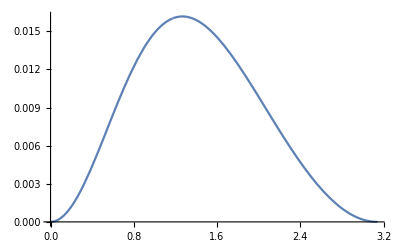

```mathematica
Plot[ZyzSimp[θ, 1, 4],{θ,0,π}]
```

## 3D, Isotropic, Plus-Polarised Wave: Work in Progress

### Basic metric, radially decreasing

We multiply by dG so that hij is uniteless. Applying rotation matricies.

```mathematica
Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].((dG*P)/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
```

```mathematica
h3DIso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].((dG*P)/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DIso]
```

(dG/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | -(1. dG (t-1. tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2))) | (1. dG (-t+tP) Cos[ϕ] Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))
-(1. dG (t-1. tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2))) | (dG (-1. (1. dG+(1. t-1. tP) Cos[θ])^2+(1. (t-1. tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2)) | (0.5 dG (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[(1. (t-1. tP) Sin[θ] Sin[ϕ])/(1. dG+(1. t-1. tP) Cos[θ])]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2))
-(1. dG (t-1. tP) Cos[ϕ] Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | (0.5 dG (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[(1. (t-1. tP) Sin[θ] Sin[ϕ])/(1. dG+(1. t-1. tP) Cos[θ])]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2)) | (dG Sin[θ]^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) Cos[θ])^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
SinSimp[opp, adj]  (*Simplifies Sin[2ArcTan[opp/adj]]*)
```

(2 adj opp)/(adj^2+opp^2)

```mathematica
hij = ({{dG/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)), -(1. dG (t-1. tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2))), (1. dG (-t+tP) Cos[ϕ] Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))}, {-(1. dG (t-1. tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2))), (dG (-1. (1. dG+(1. t-1. tP) Cos[θ])^2+(1. (t-1. tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2)), (0.5 dG (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2)*SinSimp[1. (t-1. tP) Sin[θ] Sin[ϕ], 1. dG+(1. t-1. tP) Cos[θ]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2))}, {-(1. dG (t-1. tP) Cos[ϕ] Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)), (0.5 dG (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) *SinSimp[1. (t-1. tP) Sin[θ] Sin[ϕ], 1. dG+(1. t-1. tP) Cos[θ]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2)), (dG Sin[θ]^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) Cos[θ])^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2))}});
```

```mathematica
MatrixForm[hij]
```

(dG/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | -(1. dG (t-1. tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2))) | (1. dG (-t+tP) Cos[ϕ] Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))
-(1. dG (t-1. tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2))) | (dG (-1. (1. dG+(1. t-1. tP) Cos[θ])^2+(1. (t-1. tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2)) | (1. dG (t-1. tP) (1. dG+(1. t-1. tP) Cos[θ]) Sin[θ] (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) ((1. dG+(1. t-1. tP) Cos[θ])^2+1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2))
-(1. dG (t-1. tP) Cos[ϕ] Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ])/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2)) | (1. dG (t-1. tP) (1. dG+(1. t-1. tP) Cos[θ]) Sin[θ] (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) ((1. dG+(1. t-1. tP) Cos[θ])^2+1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | (dG Sin[θ]^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) Cos[θ])^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
FullSimplify[h3DIso==hij]
```

True

```mathematica
Simplify[hij == Transpose[hij]](*checking that it's symetric*)
```

True

```mathematica
Clear[h3DIso] (*So I don't work with the wrong matrix in the future*)
```

### Redshift

```mathematica
v[θ, ϕ] (*3D looking vector, n is also commonly used*)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].hij]] (*applying 3D looking vector twice, the output is given as a function below*)
```

(dG Cos[ϕ]^2 Sin[θ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-(1. dG (t-1. tP) Cos[θ] Cos[ϕ]^2 Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ]^2)/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))+(1. dG (-t+tP) Cos[θ] Cos[ϕ]^2 Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ]^2)/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))+(2. dG (t-1. tP) Cos[θ] (1. dG+(1. t-1. tP) Cos[θ]) Sin[θ]^2 (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) ((1. dG+(1. t-1. tP) Cos[θ])^2+1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(dG Cos[θ]^2 Sin[θ]^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) Cos[θ])^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2))+(dG Sin[θ]^2 Sin[ϕ]^2 (-1. (1. dG+(1. t-1. tP) Cos[θ])^2+(1. (t-1. tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2))-(0.5 dG (t-1. tP)^2 Sin[θ]^4 Sin[2 ϕ]^2)/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2)))

```mathematica
nnhij[t_] :=(dG Cos[ϕ]^2 Sin[θ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-(1. dG (t-1. tP) Cos[θ] Cos[ϕ]^2 Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ]^2)/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))+(1. dG (-t+tP) Cos[θ] Cos[ϕ]^2 Cos[If[-1. (t-1. tP) Cos[θ]>dG,π-ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]],ArcTan[((1. (-t+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-t+tP)) Cos[θ]]]]] Sin[θ]^2)/(Abs[dG+1. (t-1. tP) Cos[θ]] √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))+(2. dG (t-1. tP) Cos[θ] (1. dG+(1. t-1. tP) Cos[θ]) Sin[θ]^2 (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) ((1. dG+(1. t-1. tP) Cos[θ])^2+1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(dG Cos[θ]^2 Sin[θ]^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) Cos[θ])^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2))+(dG Sin[θ]^2 Sin[ϕ]^2 (-1. (1. dG+(1. t-1. tP) Cos[θ])^2+(1. (t-1. tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) Cos[θ])^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG+1. (t-1. tP) Cos[θ])^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1. dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Sin[θ]^2 Sin[ϕ]^2))-(0.5 dG (t-1. tP)^2 Sin[θ]^4 Sin[2 ϕ]^2)/((dG^2+dG (2. t-2. tP) Cos[θ]+(1. t^2-2. t tP+1. tP^2) Cos[θ]^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+(1. (t-1. tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) Cos[θ])^2)))
```

```mathematica
ζ3DIso = Simplify[Simplify[nnhij[Tmin[tG, tP, dG,θ]],TimeConstraint->1],TimeConstraint->10] (*related to the redshift*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

dG Sin[θ]^2 (-((1. (dG+0.5 tP) tP Cos[θ] (dG (-1. dG-1. tP)+(dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2 Cos[ϕ]^2 Cos[If[((-1. dG-0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])>dG,π-ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]],ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]]]])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+dG Cos[θ]) √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2)))-(1. (1. dG+0.5 tP) tP Cos[θ] (dG (-1. dG-1. tP)+(dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2 Cos[ϕ]^2 Cos[If[((-1. dG-0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])>dG,π-ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]],ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]]]])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+dG Cos[θ]) √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2))+Cos[ϕ]^2/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (1+(1. (1. dG+0.5 tP)^2 tP^2 Cos[ϕ]^2 Sin[θ]^2)/((dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2)))+(2. (1. dG+0.5 tP) tP Cos[θ] (dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ]) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (2. dG^2+2. dG tP+0.5 tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Sin[θ]^2 Sin[ϕ]^2))+((1. dG+0.5 tP)^2 tP^2 Cos[θ]^2 (-1. dG-1. tP+dG Cos[θ])^2 ((1. (dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2 Cos[ϕ]^2)/(dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2)-1. Sin[ϕ]^2))/((1. dG+1. tP-1. dG Cos[θ])^2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Sin[θ]^2 Sin[ϕ]^2))-(0.5 (1. dG+0.5 tP)^2 tP^2 Sin[θ]^2 Sin[2 ϕ]^2)/((dG^2 (dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (1+(1. (1. dG+0.5 tP)^2 tP^2 Sin[θ]^2 Sin[ϕ]^2)/((dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2))))+((-1. dG-1. tP+dG Cos[θ])^2 Sin[ϕ]^2 (-1. (1. dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))^2+(1. (1. dG+0.5 tP)^4 tP^4 Sin[θ]^4 Sin[2 ϕ]^2)/((1. dG+1. tP-1. dG Cos[θ])^2 (dG^2 (4. dG^2+8. dG tP+4. tP^2)+dG (-8. dG^3-16. dG^2 tP-12. dG tP^2-4. tP^3) Cos[θ]+(4. dG^4+8. dG^3 tP+8. dG^2 tP^2+4. dG tP^3+1. tP^4) Cos[θ]^2+tP^2 (4. dG^2+4. dG tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2))))/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
χ[dP, dG, θ,ϕ](*angle between v and R, unit vectors from the Earth to the photon, and the GW source to the photon, defined in the first section.*)
```

If[dP Cos[θ]>dG,ArcTan[(dP Sin[θ])/Abs[dG-dP Cos[θ]]]-θ,π-θ-ArcTan[(dP Sin[θ])/Abs[dG-dP Cos[θ]]]]

```mathematica
vdotR3D = FullSimplify[Cos[χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]] (*n̂.R̂ = Cos[χ]*)
```

Cos[Piecewise[{{π-θ+ArcTan[(1. (dG+0.5 tP) tP Sin[θ])/(dG (-1. dG-1. tP)+(dG^2+1. dG tP+0.5 tP^2) Cos[θ])], dG (1. dG+1. tP)+(-1. dG^2-1. dG tP-0.5 tP^2) Cos[θ]≥0}, {-θ+ArcTan[(1. (dG+0.5 tP) tP Sin[θ])/(dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])], True}}]]

```mathematica
Simplify[Simplify[-1/2 1/Abs[1+vdotR3D] ζ3DIso],TimeConstraint->1,TimeConstraint->10](*full redshift equation*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

-((dG Sin[θ]^2 (-((1. (dG+0.5 tP) tP Cos[θ] (dG (-1. dG-1. tP)+(dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2 Cos[ϕ]^2 Cos[If[((-1. dG-0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])>dG,π-ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]],ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]]]])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+dG Cos[θ]) √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2)))-(1. (1. dG+0.5 tP) tP Cos[θ] (dG (-1. dG-1. tP)+(dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2 Cos[ϕ]^2 Cos[If[((-1. dG-0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])>dG,π-ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]],ArcTan[((1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Sin[θ] Sin[ϕ])/Abs[dG-(1. (-(0.+1. tP^2-2 dG tP Cos[θ])/(0.+2 dG+2. tP-2 dG Cos[θ])+tP)) Cos[θ]]]]])/(Abs[dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])] (-1. dG-1. tP+dG Cos[θ]) √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2))+Cos[ϕ]^2/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (1+(1. (1. dG+0.5 tP)^2 tP^2 Cos[ϕ]^2 Sin[θ]^2)/((dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2)))+(2. (1. dG+0.5 tP) tP Cos[θ] (dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ]) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (2. dG^2+2. dG tP+0.5 tP^2) Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Sin[θ]^2 Sin[ϕ]^2))+((1. dG+0.5 tP)^2 tP^2 Cos[θ]^2 (-1. dG-1. tP+dG Cos[θ])^2 ((1. (dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2 Cos[ϕ]^2)/(dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2)-1. Sin[ϕ]^2))/((1. dG+1. tP-1. dG Cos[θ])^2 √(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Sin[θ]^2 Sin[ϕ]^2))-(0.5 (1. dG+0.5 tP)^2 tP^2 Sin[θ]^2 Sin[2 ϕ]^2)/((dG^2 (dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (1+(1. (1. dG+0.5 tP)^2 tP^2 Sin[θ]^2 Sin[ϕ]^2)/((dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])^2))))+((-1. dG-1. tP+dG Cos[θ])^2 Sin[ϕ]^2 (-1. (1. dG+((1. dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ]))^2+(1. (1. dG+0.5 tP)^4 tP^4 Sin[θ]^4 Sin[2 ϕ]^2)/((1. dG+1. tP-1. dG Cos[θ])^2 (dG^2 (4. dG^2+8. dG tP+4. tP^2)+dG (-8. dG^3-16. dG^2 tP-12. dG tP^2-4. tP^3) Cos[θ]+(4. dG^4+8. dG^3 tP+8. dG^2 tP^2+4. dG tP^3+1. tP^4) Cos[θ]^2+tP^2 (4. dG^2+4. dG tP+1. tP^2) Cos[ϕ]^2 Sin[θ]^2))))/(√(dG^2+(1. (1. dG+0.5 tP)^2 tP^2)/(1. dG+1. tP-1. dG Cos[θ])^2+(2. dG (dG+0.5 tP) tP Cos[θ])/(-1. dG-1. tP+dG Cos[θ])) (dG^2 (1. dG^2+2. dG tP+1. tP^2)+dG (-2. dG^3-4. dG^2 tP-3. dG tP^2-1. tP^3) Cos[θ]+(1. dG^4+2. dG^3 tP+2. dG^2 tP^2+1. dG tP^3+0.25 tP^4) Cos[θ]^2+tP^2 (1. dG^2+1. dG tP+0.25 tP^2) Sin[θ]^2 Sin[ϕ]^2))))/(2 Abs[1+Cos[Piecewise[{{π-θ+ArcTan[(1. (dG+0.5 tP) tP Sin[θ])/(dG (-1. dG-1. tP)+(dG^2+1. dG tP+0.5 tP^2) Cos[θ])], dG (1. dG+1. tP)+(-1. dG^2-1. dG tP-0.5 tP^2) Cos[θ]≥0}, {-θ+ArcTan[(1. (dG+0.5 tP) tP Sin[θ])/(dG (-1. dG-1. tP)+(1. dG^2+1. dG tP+0.5 tP^2) Cos[θ])], True}}]]]))

### Small θ angle approximation

Taking the limit for θ -> 0. This gives a small patch of sky around the GW source as viewed from Earth. ϕ can still vary from 0 to 2π.  I replaced Cos[θ] -> 1 and Sin[θ] -> θ

```mathematica
hijApprox[t_] := ({{dG/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2)), -(1. dG (t-1. tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) 1)^2))), (1. dG (-t+tP) Cos[ϕ] Cos[If[-1. (t-1. tP) 1>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP)) 1]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP)) 1]]]] θ)/(Abs[dG+1. (t-1. tP) 1] √(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2))}, {-(1. dG (t-1. tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) 1)^2))), (dG (-1. (1. dG+(1. t-1. tP) 1)^2+(1. (t-1. tP)^4 Cos[ϕ]^2 θ^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) 1)^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)), (1. dG (t-1. tP) (1. dG+(1. t-1. tP) 1) θ (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) ((1. dG+(1. t-1. tP) 1)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))}, {-(1. dG (t-1. tP) Cos[ϕ] Cos[If[-1. (t-1. tP) 1>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP)) ]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP))]]]] θ)/(Abs[dG+1. (t-1. tP)] √(dG^2+(t-tP)^2+2 dG (t-tP)) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP))^2)), (1. dG (t-1. tP) (1. dG+(1. t-1. tP) ) θ (1. dG^2+dG (2. t-2. tP) +(1. t^2-2. t tP+1. tP^2) +(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP)) (1. dG^2+dG (2. t-2. tP) +(1. t^2-2. t tP+1. tP^2) +(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) ((1. dG+(1. t-1. tP))^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)), (dG θ^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) 1)^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) 1)^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))}});
```

```mathematica
v[θ, ϕ]
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
vApprox[θ_,ϕ_] := {Cos[ϕ]*θ,θ*Sin[ϕ],1} (*small θ version of the looking vector v*)
```

```mathematica
TminApprox[tP_,dG_] := (tP^2-2 dG tP)/(2 dG+2 tP-2 dG)(* approximate Tmin for small θ*)
```

```mathematica
Simplify[hijApprox[t] == Transpose[hijApprox[t]]](*testing to make sure it's symmetric*)
```

True

```mathematica
Simplify[vApprox[θ, ϕ].Transpose[vApprox[θ,ϕ].hijApprox]] (*applying 3D looking vector twice, the results are given as a function below*)
```

1/Abs[dG+t-tP]dG θ^2 ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))

```mathematica
nnhijApprox[t_] := 1/Abs[dG+t-tP] dG θ^2 ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))
```

```mathematica
ζ3DIsoApprox = Simplify[Simplify[nnhijApprox[TminApprox[tP, dG]],TimeConstraint->1],TimeConstraint->10] (*related to redshift*)
```

(8. dG θ^2 (-1. dG^2 tP^2 Sin[ϕ]^2+Cos[ϕ]^2 ((4. dG^4+8. dG^3 tP+6. dG^2 tP^2+2. dG tP^3+0.25 tP^4) θ^4 Sin[ϕ]^4+tP^2 (1. dG^2+dG tP (1.-1. √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^2 (0.5-0.5 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))))+θ^2 (-1. dG^4+dG tP^3 (1.-0.5 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+dG^2 tP^2 (1.5-0.5 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^4 (0.1875-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))) Sin[2 ϕ]^2))/(tP (1. tP^2+(4. dG^2+4. dG tP+1. tP^2) θ^2 Cos[ϕ]^2) (1. tP^2+(4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2))

```mathematica
χ[dP, dG, θ,ϕ] (*original angle between n and R*)
```

If[dP Cos[θ]>dG,ArcTan[(dP Sin[θ])/Abs[dG-dP Cos[θ]]]-θ,π-θ-ArcTan[(dP Sin[θ])/Abs[dG-dP Cos[θ]]]]

```mathematica
χApprox[dP_, dG_, θ_,ϕ_] := If[dP >dG,ArcTan[(dP θ)/Abs[dG-dP ]]-θ,π-θ-ArcTan[(dP θ)/Abs[dG-dP ]]] (*small θ approximation for χ*)
```

```mathematica
vdotR3DApprox = FullSimplify[Cos[χApprox[DP[tP,TminApprox[tP, dG]], dG, θ,ϕ]]] (*n̂.R̂ = Cos[χ]*)
```

Cos[1. θ-ArcTan[(1.+(2. dG)/tP) θ]]

```mathematica
Simplify[Simplify[-1/2 1/Abs[1+vdotR3DApprox] ζ3DIsoApprox],TimeConstraint->1,TimeConstraint->10](*full approximate redshift equation*)
```

-((1. dG θ^2 (-0.25 dG^2 tP^2 Sin[ϕ]^2+Cos[ϕ]^2 ((1. dG^4+2. dG^3 tP+1.5 dG^2 tP^2+0.5 dG tP^3+0.0625 tP^4) θ^4 Sin[ϕ]^4+tP^2 (0.25 dG^2+dG tP (0.25-0.25 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^2 (0.125-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))))+θ^2 (-0.25 dG^4+dG tP^3 (0.25-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+dG^2 tP^2 (0.375-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^4 (0.046875-0.03125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))) Sin[2 ϕ]^2))/(tP (0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Cos[ϕ]^2) (1+Cos[1. θ-ArcTan[(1.+(2. dG)/tP) θ]]) (0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Sin[ϕ]^2)))

This is the full redshift equation for the small θ approximation

```mathematica
z3DIsoApprox[dG_, tP_,θ_,ϕ_] := -((1. dG θ^2 (-0.25 dG^2 tP^2 Sin[ϕ]^2+Cos[ϕ]^2 ((1. dG^4+2. dG^3 tP+1.5 dG^2 tP^2+0.5 dG tP^3+0.0625 tP^4) θ^4 Sin[ϕ]^4+tP^2 (0.25 dG^2+dG tP (0.25-0.25 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^2 (0.125-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))))+θ^2 (-0.25 dG^4+dG tP^3 (0.25-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+dG^2 tP^2 (0.375-0.125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^4 (0.046875-0.03125 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))) Sin[2 ϕ]^2))/(tP (0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Cos[ϕ]^2) (1+Cos[1. θ-ArcTan[(1.+(2. dG)/tP) θ]]) (0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Sin[ϕ]^2)))
```

### Redshift in terms of x=tP/dG

It can be useful to express redshift in terms of the dimensionless variable x = tP/dG

```mathematica
Block[{tP = dG*x}, FullSimplify[z3DIsoApprox[dG, tP,θ,ϕ]]]
```

(θ^2 (4. x^2 Sin[ϕ]^2+Cos[ϕ]^2 (x^2 (-4.+(-4.-2. x) x)-1. (2.+1. x)^4 θ^4 Sin[ϕ]^4+2. x^2 (2.+1. x) √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))+θ^2 (4.+x (-8.88178×10^-16+2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-6.+2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-4.-0.75 x+0.5 √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))))) Sin[2 ϕ]^2))/(x (1. x^2+1. (2.+1. x)^2 θ^2 Cos[ϕ]^2) (1.+Cos[1. θ-ArcTan[(1.+2./x) θ]]) (1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))

```mathematica
FullSimplify[(θ^2 (4. x^2 Sin[ϕ]^2+Cos[ϕ]^2 (x^2 (-4.+(-4.-2. x) x)-1. (2.+1. x)^4 θ^4 Sin[ϕ]^4+2. x^2 (2.+1. x) √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))+θ^2 (3.999999999999999+x (0+2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-5.999999999999999+2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-3.999999999999999-0.7499999999999999 x+0.5 √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))))) Sin[2 ϕ]^2))/(x (1. x^2+1. (2.+1. x)^2 θ^2 Cos[ϕ]^2) (1.+Cos[1. θ-ArcTan[(1.+2./x) θ]]) (1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))]
```

(θ^2 (4. x^2 Sin[ϕ]^2+Cos[ϕ]^2 (x^2 (-4.+(-4.-2. x) x)-1. (2.+1. x)^4 θ^4 Sin[ϕ]^4+2. x^2 (2.+1. x) √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))+θ^2 (4.+x (2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-6.+2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-4.-0.75 x+0.5 √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))))) Sin[2 ϕ]^2))/(x (1. x^2+1. (2.+1. x)^2 θ^2 Cos[ϕ]^2) (1.+Cos[1. θ-ArcTan[(1.+2./x) θ]]) (1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))

```mathematica
Rationalize[(θ^2 (4. x^2 Sin[ϕ]^2+Cos[ϕ]^2 (x^2 (-4.+(-4.-2. x) x)-1. (2.+1. x)^4 θ^4 Sin[ϕ]^4+2. x^2 (2.+1. x) √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))+θ^2 (3.999999999999999+x (2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-5.999999999999999+2. √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2)+x (-3.999999999999999-0.7499999999999999 x+0.5 √(1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))))) Sin[2 ϕ]^2))/(x (1. x^2+1. (2.+1. x)^2 θ^2 Cos[ϕ]^2) (1.+Cos[1. θ-ArcTan[(1.+2./x) θ]]) (1. x^2+1. (2.+1. x)^2 θ^2 Sin[ϕ]^2))]
```

(θ^2 (4 x^2 Sin[ϕ]^2+Cos[ϕ]^2 (x^2 (-4+(-4-2 x) x)-(2+x)^4 θ^4 Sin[ϕ]^4+2 x^2 (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 (4+x (2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)+x (-6+2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)+x (-4-(3 x)/4+1/2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))))) Sin[2 ϕ]^2))/(x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[(1+2/x) θ]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))

```mathematica
FullSimplify[(θ^2 (4 x^2 Sin[ϕ]^2+Cos[ϕ]^2 (x^2 (-4+(-4-2 x) x)-(2+x)^4 θ^4 Sin[ϕ]^4+2 x^2 (2+x) √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+θ^2 (4+x (2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)+x (-6+2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)+x (-4-(3 x)/4+1/2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))))) Sin[2 ϕ]^2))/(x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[(1+2/x) θ]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))]
```

-((θ^2 (-16 x^2 Sin[ϕ]^2+4 Cos[ϕ]^2 (2 x^2 (2+x (2+x))+(2+x) ((2+x)^3 θ^4 Sin[ϕ]^4-2 x^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)))+(2+x)^2 θ^2 (-4+x (4+3 x-2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2)))

```mathematica
zApprox[x_,θ_,ϕ_] := -((θ^2 (-16 x^2 Sin[ϕ]^2+4 Cos[ϕ]^2 (2 x^2 (2+x (2+x))+(2+x) ((2+x)^3 θ^4 Sin[ϕ]^4-2 x^2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)))+(2+x)^2 θ^2 (-4+x (4+3 x-2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(4 x (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2)))
```

```mathematica
Manipulate[Plot[zApprox[x,θ,ϕ] ,{θ,0,0.1}],{x,0.00001,3},{ϕ,0,2 π}]
```

### Plotting redshift

Plots of redshift for small values of θ and various values of x = tP/dG. We start with a static plot where x=1, then two plots where x is free to vary.

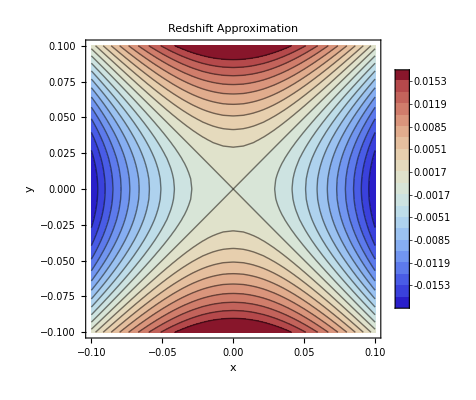

```mathematica
ContourPlot[Re[zApprox[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->20,ColorFunction->"ThermometerColors",FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None, PlotLabel->"Redshift Approximation"]
```

```mathematica
Manipulate[ContourPlot[Re[zApprox[xVal,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->20,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All, Exclusions->None],{xVal,0.001,2}]
```

```mathematica
Manipulate[ContourPlot[Re[zApprox[xVal,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->20,PlotPoints->40,MaxRecursion->2,PerformanceGoal->"Speed"],{xVal,0.001,2,Animator,AnimationRunning->True,AnimationRate->0.2}]
```

### Deflection angle (small θ approximation) approach

The full angular deflection equation is a sum of 5 terms. We will start by calculating the integral term, as that will by far be the most complicated. The integral we have to solve is n^j n^l∫_0^λmin ∂/(∂x^i)h_jl(λ)ⅆλ. This is the the partial derivative of h_jlin the x^i direction, integrated over the photon’s trajectory where it encounters the GW. This will be related to the angular deflection on n^i. We perform this integral three times for the deflections in the x,y, and z directions.

∂/(∂ x) = Sin[θ]Cos[ϕ]∂/(∂ r) + 1/r Cos[ϕ]Cos[θ]∂/(∂ θ)- 1/r Sin[ϕ]/Sin[θ]∂/(∂ ϕ)

We use this formula to convert a partial derivative with respect to x,y, and z to polar coordinates. 

In this case, r is the distance from the Earth to the photon, DP[tP,  t] = c(tP-t). To take ∂/(∂ r), you can take the derivative with respect to either tP or t, they are equal, but opposite.

```mathematica
Simplify[D[nnhijApproxAgl[t, tP, θ, ϕ],tP]+D[nnhijApproxAgl[t, tP, θ, ϕ],t]]
```

0.

The same partial derivative function, in the small θ limit:

∂/(∂ x) = θ Cos[ϕ] D[nnhijApproxAgl[t, tP, θ, ϕ],r] + 1/r Cos[ϕ] D[nnhijApproxAgl[t, tP, θ, ϕ],θ] - 1/r Sin[ϕ]/θ D[nnhijApproxAgl[t, tP, θ, ϕ],ϕ]

### Individual matrix elements - partial with respect to x and integrating over t - WORK IN PROGRESS

#### Approach and diagonal elements

For computational speed, we apply n^j n^l∫_0^λmin ∂/(∂x^i)h_jl(λ)ⅆλ to each h_jlmatrix element individually. 
We use the same small θ matrix as we did in the redshift section.

```mathematica
MatrixForm[hijApprox[t]]
```

(dG/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2)) | -(1. dG (t-1. tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))) | (1. dG (-t+tP) θ Cos[ϕ] Cos[If[-1. (t-1. tP)>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) Abs[dG+1. (t-1. tP)] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2))
-(1. dG (t-1. tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))) | (dG (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. (t-1. tP))^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2))))/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)) | (1. dG (t-1. tP) (1. dG+1. t-1. tP) θ (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))
-(1. dG (t-1. tP) θ Cos[ϕ] Cos[If[-1. (t-1. tP)>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) Abs[dG+1. (t-1. tP)] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2)) | (1. dG (t-1. tP) (1. dG+1. t-1. tP) θ (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)) | (dG θ^2 ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. (t-1. tP))^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))

```mathematica
vApprox[θ,ϕ]  (*small θ version of the looking vector v, defined above*)
```

{θ Cos[ϕ],θ Sin[ϕ],1}

```mathematica
TminApprox[tP,dG] (*Approximate Tmin for small θ, defined above*)
```

(-2 dG tP+tP^2)/(2 tP)

After applying the integral, we apply the looking vector twice to the matrix which will give us

```mathematica
Simplify[vApprox[θ,ϕ].Transpose[vApprox[θ,ϕ].({{δ11, δ12, δ13}, {δ12, δ22, δ23}, {δ13, δ23, δ33}})]]
```

δ33+2 δ13 θ Cos[ϕ]+δ11 θ^2 Cos[ϕ]^2+2 δ23 θ Sin[ϕ]+δ22 θ^2 Sin[ϕ]^2+δ12 θ^2 Sin[2 ϕ]

Selecting the 1,1 matrix element and using 
∂/(∂ x) = Sin[θ]Cos[ϕ]∂/(∂ r) + 1/r Cos[ϕ]Cos[θ]∂/(∂ θ)- 1/r Sin[ϕ]/Sin[θ]∂/(∂ ϕ)
to take the partial derivative with respect to x. 

When then integrate from λ=0 to λmin, which is the same as integrating from tP (the time the photon arrives on Earth) to Tmin (the first time the photon encounters the GW). Converting the integral from λ to time also pulls out a factor of 1/ω_0(ω_0 is the photon’s original frequency). 

Finally, we express the result in terms of the dimensionless variable x = tP/dG. (dG is the distance from the Earth to the GW source).

```mathematica
h11 = hijApprox[[1,1]]
h11dx = Simplify[Simplify[θ Cos[ϕ] D[h11,tP]  + 1/(tP-t)Cos[ϕ] D[h11,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h11,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h11dxInt = Integrate[h11dx,t] (*taking and simplifying the indefinite integral*)
h11dxInt = Simplify[h11dxInt, TimeConstraint->20]
```

dG/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2))

(2. dG θ Cos[ϕ] (1. (t-1. tP)^2 (dG+t-1. tP)^3 Cos[ϕ]^2+1. dG (dG+t-1. tP)^2 (1. t-1. tP)^2 θ^2 Cos[ϕ]^2+0.5 (t-tP) (dG+t-tP) (dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)+1. (t-1. tP)^2 (dG+t-1. tP)^3 Sin[ϕ]^2))/((t-tP) (dG+1. t-1. tP)^3 Abs[dG+t-1. tP]^3 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)

Piecewise[{{(2. dG θ Cos[ϕ] (dG (4.+θ^2)+(t-1. tP) (6.+θ^2)+(dG+t-1. tP) θ^2 Cos[2. ϕ]))/((2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG (t-1. tP)+(t-1. tP)^2 (2.+θ^2)+(t-1. tP)^2 θ^2 Cos[2. ϕ])), dG+t-1. tP<0.}, {-(2. dG θ Cos[ϕ] (dG (4.+θ^2)+(t-1. tP) (6.+θ^2)+(dG+t-1. tP) θ^2 Cos[2. ϕ]))/((2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG (t-1. tP)+(t-1. tP)^2 (2.+θ^2)+(t-1. tP)^2 θ^2 Cos[2. ϕ])), True}}]

Piecewise[{{(2. dG θ Cos[ϕ] (dG (4.+θ^2)+(t-1. tP) (6.+θ^2)+(dG+t-1. tP) θ^2 Cos[2. ϕ]))/((2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG (t-1. tP)+(t-1. tP)^2 (2.+θ^2)+(t-1. tP)^2 θ^2 Cos[2. ϕ])), dG+t-1. tP<0.}, {-(2. dG θ Cos[ϕ] (dG (4.+θ^2)+(t-1. tP) (6.+θ^2)+(dG+t-1. tP) θ^2 Cos[2. ϕ]))/((2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG (t-1. tP)+(t-1. tP)^2 (2.+θ^2)+(t-1. tP)^2 θ^2 Cos[2. ϕ])), True}}]

```mathematica
h11Int[t_] := Piecewise[{{(2. dG θ Cos[ϕ] (dG (4.+θ^2)+(t-1. tP) (6.+θ^2)+(dG+t-1. tP) θ^2 Cos[2. ϕ]))/((2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG (t-1. tP)+(t-1. tP)^2 (2.+θ^2)+(t-1. tP)^2 θ^2 Cos[2. ϕ])), dG+t-1. tP<0.}, {-(2. dG θ Cos[ϕ] (dG (4.+θ^2)+(t-1. tP) (6.+θ^2)+(dG+t-1. tP) θ^2 Cos[2. ϕ]))/((2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG (t-1. tP)+(t-1. tP)^2 (2.+θ^2)+(t-1. tP)^2 θ^2 Cos[2. ϕ])), True}}]
```

```mathematica
h11DefInt = FullSimplify[h11Int[TminApprox[tP,dG]] - h11Int[tP]] (*taking the definite integral*)
```

(θ Cos[ϕ] (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(dG (-4. dG+tP (-6.-1. θ^2)-1. tP θ^2 Cos[2. ϕ]))/(dG^2 θ^2+1. dG tP θ^2+tP^2 (0.5+0.25 θ^2)+(dG^2+1. dG tP+0.25 tP^2) θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])

```mathematica
δ11X = Block[{tP = dG*x}, FullSimplify[h11DefInt]] (*The 1,1 matrix compenent which contributes to the deflection angle δ*)
```

(θ Cos[ϕ] (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(-16.+x (-24.-4. θ^2)-4. x θ^2 Cos[2. ϕ])/(2. x^2+1. (2.+1. x)^2 θ^2+1. (2.+1. x)^2 θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])

```mathematica
δ11X =(θ Cos[ϕ] (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(-16.+x (-24.-4. θ^2)-4. x θ^2 Cos[2. ϕ])/(2. x^2+1. (2.+1. x)^2 θ^2+1. (2.+1. x)^2 θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])
```

(θ Cos[ϕ] (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(-16.+x (-24.-4. θ^2)-4. x θ^2 Cos[2. ϕ])/(2. x^2+1. (2.+1. x)^2 θ^2+1. (2.+1. x)^2 θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])

We then apply the looking vector n^j n^l to h_jl, which will multiply δ11X by a factor of θ^2 Cos[ϕ]^2, as shown above. This is one of the terms that will go into the final expression for the definite integral.

```mathematica
δ11X θ^2 Cos[ϕ]^2
```

(θ^3 Cos[ϕ]^3 (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(-16.+x (-24.-4. θ^2)-4. x θ^2 Cos[2. ϕ])/(2. x^2+1. (2.+1. x)^2 θ^2+1. (2.+1. x)^2 θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])

```mathematica
d11[x_,θ_,ϕ_] := (θ^3 Cos[ϕ]^3 (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(-16.+x (-24.-4. θ^2)-4. x θ^2 Cos[2. ϕ])/(2. x^2+1. (2.+1. x)^2 θ^2+1. (2.+1. x)^2 θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])
```

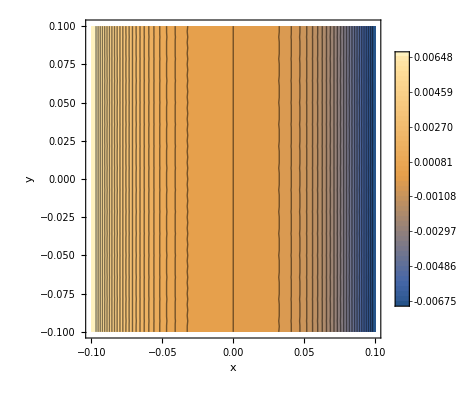

```mathematica
ContourPlot[Re[d11[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, PlotRange->All, Exclusions->None](*plotting to ensure it's well behaved*)(*using Exclusions->None to remove ArcTan disontinuity at π.*)
```

We then repeat the same process for every other matrix element.

```mathematica
h22 = hijApprox[[2,2]]
h22dx = Simplify[Simplify[θ Cos[ϕ] D[h22,tP]  + 1/(tP-t)Cos[ϕ] D[h22,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h22,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h22dxInt = Integrate[h22dx,t]
h22dxInt = Simplify[h22dxInt, TimeConstraint->20]
```

(dG (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. (t-1. tP))^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2))))/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))

(2. dG (dG+t-tP) Cos[ϕ] (1. (dG+t-tP) (dG+1. t-1. tP) θ Sin[ϕ]^2 (1. (t-1. tP)^4 θ^2 (1. (dG+1. t-1. tP)^2 Cos[ϕ]^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^4-1. (dG+1. t-1. tP)^2 Sin[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+1. (1. t^2-2. t tP+1. tP^2) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-0.25 (t-1. tP)^4 θ^4 Sin[2 ϕ]^2))+1. (dG+t-tP) (dG+1. t-1. tP) Sin[ϕ]^2 (1. (-2. (t-1. tP)^4 (dG+1. t-1. tP)^2 θ^3 Cos[ϕ]^2-1. (t-1. tP)^6 θ^5 Cos[ϕ]^4) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-1. (1. t^2-2. t tP+1. tP^2) θ ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-0.25 (t-1. tP)^4 θ^4 Sin[2 ϕ]^2))-0.5 (t-tP) θ (-2. (dG+t-tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2) (1. (dG+1. t-1. tP) (1. dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)^2+1. dG (1. t-1. tP)^5 θ^6 Cos[ϕ]^4 Sin[ϕ]^2+1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-2. (t-1. tP)^3 (dG+1. t-1. tP) θ^4 Cos[ϕ]^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)+1. (dG+t-tP) (dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (2. dG+2. t-2. tP+(2. t-2. tP) θ^2 Sin[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-0.25 (t-1. tP)^4 θ^4 Sin[2 ϕ]^2)+1. (dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-0.25 (t-1. tP)^4 θ^4 Sin[2 ϕ]^2))))/((t-1. tP) (dG+1. t-1. tP) Abs[dG+t-tP]^3 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)

Piecewise[{{-1. dG Cos[ϕ] (-((128. (dG^9 t θ+9. dG^8 t^2 θ+36. dG^7 t^3 θ+84. dG^6 t^4 θ+126. dG^5 t^5 θ+126. dG^4 t^6 θ+84. dG^3 t^7 θ+36. dG^2 t^8 θ+9. dG t^9 θ+t^10 θ-1. dG^9 tP θ-18. dG^8 t tP θ-108. dG^7 t^2 tP θ-336. dG^6 t^3 tP θ-630. dG^5 t^4 tP θ-756. dG^4 t^5 tP θ-588. dG^3 t^6 tP θ-288. dG^2 t^7 tP θ-81. dG t^8 tP θ-10. t^9 tP θ+9. dG^8 tP^2 θ+108. dG^7 t tP^2 θ+504. dG^6 t^2 tP^2 θ+1260. dG^5 t^3 tP^2 θ+1890. dG^4 t^4 tP^2 θ+1764. dG^3 t^5 tP^2 θ+1008. dG^2 t^6 tP^2 θ+324. dG t^7 tP^2 θ+45. t^8 tP^2 θ-36. dG^7 tP^3 θ-336. dG^6 t tP^3 θ-1260. dG^5 t^2 tP^3 θ-2520. dG^4 t^3 tP^3 θ-2940. dG^3 t^4 tP^3 θ-2016. dG^2 t^5 tP^3 θ-756. dG t^6 tP^3 θ-120. t^7 tP^3 θ+84. dG^6 tP^4 θ+630. dG^5 t tP^4 θ+1890. dG^4 t^2 tP^4 θ+2940. dG^3 t^3 tP^4 θ+2520. dG^2 t^4 tP^4 θ+1134. dG t^5 tP^4 θ+210. t^6 tP^4 θ-126. dG^5 tP^5 θ-756. dG^4 t tP^5 θ-1764. dG^3 t^2 tP^5 θ-2016. dG^2 t^3 tP^5 θ-1134. dG t^4 tP^5 θ-252. t^5 tP^5 θ+126. dG^4 tP^6 θ+588. dG^3 t tP^6 θ+1008. dG^2 t^2 tP^6 θ+756. dG t^3 tP^6 θ+210. t^4 tP^6 θ-84. dG^3 tP^7 θ-288. dG^2 t tP^7 θ-324. dG t^2 tP^7 θ-120. t^3 tP^7 θ+36. dG^2 tP^8 θ+81. dG t tP^8 θ+45. t^2 tP^8 θ-9. dG tP^9 θ-10. t tP^9 θ+tP^10 θ+2. dG^7 t^3 θ^3 Cos[ϕ]^2+14. dG^6 t^4 θ^3 Cos[ϕ]^2+42. dG^5 t^5 θ^3 Cos[ϕ]^2+70. dG^4 t^6 θ^3 Cos[ϕ]^2+70. dG^3 t^7 θ^3 Cos[ϕ]^2+42. dG^2 t^8 θ^3 Cos[ϕ]^2+14. dG t^9 θ^3 Cos[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2-6. dG^7 t^2 tP θ^3 Cos[ϕ]^2-56. dG^6 t^3 tP θ^3 Cos[ϕ]^2-210. dG^5 t^4 tP θ^3 Cos[ϕ]^2-420. dG^4 t^5 tP θ^3 Cos[ϕ]^2-490. dG^3 t^6 tP θ^3 Cos[ϕ]^2-336. dG^2 t^7 tP θ^3 Cos[ϕ]^2-126. dG t^8 tP θ^3 Cos[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2+6. dG^7 t tP^2 θ^3 Cos[ϕ]^2+84. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2+420. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2+1050. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2+1470. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2+1176. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2+504. dG t^7 tP^2 θ^3 Cos[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2-2. dG^7 tP^3 θ^3 Cos[ϕ]^2-56. dG^6 t tP^3 θ^3 Cos[ϕ]^2-420. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2-1400. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2-2450. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2-2352. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2-1176. dG t^6 tP^3 θ^3 Cos[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2+14. dG^6 tP^4 θ^3 Cos[ϕ]^2+210. dG^5 t tP^4 θ^3 Cos[ϕ]^2+1050. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2+2450. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2+2940. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2+1764. dG t^5 tP^4 θ^3 Cos[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2-42. dG^5 tP^5 θ^3 Cos[ϕ]^2-420. dG^4 t tP^5 θ^3 Cos[ϕ]^2-1470. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2-2352. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2-1764. dG t^4 tP^5 θ^3 Cos[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2+70. dG^4 tP^6 θ^3 Cos[ϕ]^2+490. dG^3 t tP^6 θ^3 Cos[ϕ]^2+1176. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2+1176. dG t^3 tP^6 θ^3 Cos[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2-70. dG^3 tP^7 θ^3 Cos[ϕ]^2-336. dG^2 t tP^7 θ^3 Cos[ϕ]^2-504. dG t^2 tP^7 θ^3 Cos[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2+42. dG^2 tP^8 θ^3 Cos[ϕ]^2+126. dG t tP^8 θ^3 Cos[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2-14. dG tP^9 θ^3 Cos[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2+dG^5 t^5 θ^5 Cos[ϕ]^4+5. dG^4 t^6 θ^5 Cos[ϕ]^4+10. dG^3 t^7 θ^5 Cos[ϕ]^4+10. dG^2 t^8 θ^5 Cos[ϕ]^4+5. dG t^9 θ^5 Cos[ϕ]^4+t^10 θ^5 Cos[ϕ]^4-5. dG^5 t^4 tP θ^5 Cos[ϕ]^4-30. dG^4 t^5 tP θ^5 Cos[ϕ]^4-70. dG^3 t^6 tP θ^5 Cos[ϕ]^4-80. dG^2 t^7 tP θ^5 Cos[ϕ]^4-45. dG t^8 tP θ^5 Cos[ϕ]^4-10. t^9 tP θ^5 Cos[ϕ]^4+10. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^4+75. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^4+210. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^4+280. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^4+180. dG t^7 tP^2 θ^5 Cos[ϕ]^4+45. t^8 tP^2 θ^5 Cos[ϕ]^4-10. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^4-100. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^4-350. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^4-560. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^4-420. dG t^6 tP^3 θ^5 Cos[ϕ]^4-120. t^7 tP^3 θ^5 Cos[ϕ]^4+5. dG^5 t tP^4 θ^5 Cos[ϕ]^4+75. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^4+350. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^4+700. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^4+630. dG t^5 tP^4 θ^5 Cos[ϕ]^4+210. t^6 tP^4 θ^5 Cos[ϕ]^4-1. dG^5 tP^5 θ^5 Cos[ϕ]^4-30. dG^4 t tP^5 θ^5 Cos[ϕ]^4-210. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^4-560. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^4-630. dG t^4 tP^5 θ^5 Cos[ϕ]^4-252. t^5 tP^5 θ^5 Cos[ϕ]^4+5. dG^4 tP^6 θ^5 Cos[ϕ]^4+70. dG^3 t tP^6 θ^5 Cos[ϕ]^4+280. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^4+420. dG t^3 tP^6 θ^5 Cos[ϕ]^4+210. t^4 tP^6 θ^5 Cos[ϕ]^4-10. dG^3 tP^7 θ^5 Cos[ϕ]^4-80. dG^2 t tP^7 θ^5 Cos[ϕ]^4-180. dG t^2 tP^7 θ^5 Cos[ϕ]^4-120. t^3 tP^7 θ^5 Cos[ϕ]^4+10. dG^2 tP^8 θ^5 Cos[ϕ]^4+45. dG t tP^8 θ^5 Cos[ϕ]^4+45. t^2 tP^8 θ^5 Cos[ϕ]^4-5. dG tP^9 θ^5 Cos[ϕ]^4-10. t tP^9 θ^5 Cos[ϕ]^4+tP^10 θ^5 Cos[ϕ]^4+2. dG^8 t^2 θ^3 Sin[ϕ]^2+15. dG^7 t^3 θ^3 Sin[ϕ]^2+49. dG^6 t^4 θ^3 Sin[ϕ]^2+91. dG^5 t^5 θ^3 Sin[ϕ]^2+105. dG^4 t^6 θ^3 Sin[ϕ]^2+77. dG^3 t^7 θ^3 Sin[ϕ]^2+35. dG^2 t^8 θ^3 Sin[ϕ]^2+9. dG t^9 θ^3 Sin[ϕ]^2+t^10 θ^3 Sin[ϕ]^2-4. dG^8 t tP θ^3 Sin[ϕ]^2-45. dG^7 t^2 tP θ^3 Sin[ϕ]^2-196. dG^6 t^3 tP θ^3 Sin[ϕ]^2-455. dG^5 t^4 tP θ^3 Sin[ϕ]^2-630. dG^4 t^5 tP θ^3 Sin[ϕ]^2-539. dG^3 t^6 tP θ^3 Sin[ϕ]^2-280. dG^2 t^7 tP θ^3 Sin[ϕ]^2-81. dG t^8 tP θ^3 Sin[ϕ]^2-10. t^9 tP θ^3 Sin[ϕ]^2+2. dG^8 tP^2 θ^3 Sin[ϕ]^2+45. dG^7 t tP^2 θ^3 Sin[ϕ]^2+294. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^2+910. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^2+1575. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^2+1617. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^2+980. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^2+324. dG t^7 tP^2 θ^3 Sin[ϕ]^2+45. t^8 tP^2 θ^3 Sin[ϕ]^2-15. dG^7 tP^3 θ^3 Sin[ϕ]^2-196. dG^6 t tP^3 θ^3 Sin[ϕ]^2-910. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^2-2100. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^2-2695. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^2-1960. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^2-756. dG t^6 tP^3 θ^3 Sin[ϕ]^2-120. t^7 tP^3 θ^3 Sin[ϕ]^2+49. dG^6 tP^4 θ^3 Sin[ϕ]^2+455. dG^5 t tP^4 θ^3 Sin[ϕ]^2+1575. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^2+2695. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^2+2450. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^2+1134. dG t^5 tP^4 θ^3 Sin[ϕ]^2+210. t^6 tP^4 θ^3 Sin[ϕ]^2-91. dG^5 tP^5 θ^3 Sin[ϕ]^2-630. dG^4 t tP^5 θ^3 Sin[ϕ]^2-1617. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^2-1960. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^2-1134. dG t^4 tP^5 θ^3 Sin[ϕ]^2-252. t^5 tP^5 θ^3 Sin[ϕ]^2+105. dG^4 tP^6 θ^3 Sin[ϕ]^2+539. dG^3 t tP^6 θ^3 Sin[ϕ]^2+980. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^2+756. dG t^3 tP^6 θ^3 Sin[ϕ]^2+210. t^4 tP^6 θ^3 Sin[ϕ]^2-77. dG^3 tP^7 θ^3 Sin[ϕ]^2-280. dG^2 t tP^7 θ^3 Sin[ϕ]^2-324. dG t^2 tP^7 θ^3 Sin[ϕ]^2-120. t^3 tP^7 θ^3 Sin[ϕ]^2+35. dG^2 tP^8 θ^3 Sin[ϕ]^2+81. dG t tP^8 θ^3 Sin[ϕ]^2+45. t^2 tP^8 θ^3 Sin[ϕ]^2-9. dG tP^9 θ^3 Sin[ϕ]^2-10. t tP^9 θ^3 Sin[ϕ]^2+tP^10 θ^3 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^5 t^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 t^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+40. dG^3 t^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 t^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG t^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t^3 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-60. dG^5 t^4 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t^5 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-280. dG^3 t^6 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t^7 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-108. dG t^8 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+432. dG t^7 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1400. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^6 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. dG^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+60. dG^5 t tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1400. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2100. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1512. dG t^5 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1512. dG t^4 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+280. dG^3 t tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^3 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-40. dG^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-432. dG t^2 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+108. dG t tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 t^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+44. dG^5 t^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+28. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t^3 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-220. dG^5 t^4 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-252. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2+48. dG^6 t^2 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+440. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2520. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-440. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2000. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4200. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2352. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+220. dG^5 t tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4200. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+5600. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+3528. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-44. dG^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2520. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-3528. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2352. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+252. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-28. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. dG^4 t^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+15. dG^3 t^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 t^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+13. dG t^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. t^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t^5 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-105. dG^3 t^6 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t^7 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-117. dG t^8 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t^9 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+315. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+468. dG t^7 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^8 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-525. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1092. dG t^6 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^7 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+525. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1470. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1638. dG t^5 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^6 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-315. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1638. dG t^4 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-756. t^5 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+4. dG^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+105. dG^3 t tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1092. dG t^3 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-15. dG^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-468. dG t^2 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+117. dG t tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-13. dG tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. tP^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Sin[ϕ]^4+12. dG^5 t^5 θ^3 Sin[ϕ]^4+30. dG^4 t^6 θ^3 Sin[ϕ]^4+40. dG^3 t^7 θ^3 Sin[ϕ]^4+30. dG^2 t^8 θ^3 Sin[ϕ]^4+12. dG t^9 θ^3 Sin[ϕ]^4+2. t^10 θ^3 Sin[ϕ]^4-8. dG^6 t^3 tP θ^3 Sin[ϕ]^4-60. dG^5 t^4 tP θ^3 Sin[ϕ]^4-180. dG^4 t^5 tP θ^3 Sin[ϕ]^4-280. dG^3 t^6 tP θ^3 Sin[ϕ]^4-240. dG^2 t^7 tP θ^3 Sin[ϕ]^4-108. dG t^8 tP θ^3 Sin[ϕ]^4-20. t^9 tP θ^3 Sin[ϕ]^4+12. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^4+120. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^4+450. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^4+840. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^4+840. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^4+432. dG t^7 tP^2 θ^3 Sin[ϕ]^4+90. t^8 tP^2 θ^3 Sin[ϕ]^4-8. dG^6 t tP^3 θ^3 Sin[ϕ]^4-120. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^4-600. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^4-1400. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^4-1680. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^4-1008. dG t^6 tP^3 θ^3 Sin[ϕ]^4-240. t^7 tP^3 θ^3 Sin[ϕ]^4+2. dG^6 tP^4 θ^3 Sin[ϕ]^4+60. dG^5 t tP^4 θ^3 Sin[ϕ]^4+450. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^4+1400. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^4+2100. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^4+1512. dG t^5 tP^4 θ^3 Sin[ϕ]^4+420. t^6 tP^4 θ^3 Sin[ϕ]^4-12. dG^5 tP^5 θ^3 Sin[ϕ]^4-180. dG^4 t tP^5 θ^3 Sin[ϕ]^4-840. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^4-1680. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^4-1512. dG t^4 tP^5 θ^3 Sin[ϕ]^4-504. t^5 tP^5 θ^3 Sin[ϕ]^4+30. dG^4 tP^6 θ^3 Sin[ϕ]^4+280. dG^3 t tP^6 θ^3 Sin[ϕ]^4+840. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^4+1008. dG t^3 tP^6 θ^3 Sin[ϕ]^4+420. t^4 tP^6 θ^3 Sin[ϕ]^4-40. dG^3 tP^7 θ^3 Sin[ϕ]^4-240. dG^2 t tP^7 θ^3 Sin[ϕ]^4-432. dG t^2 tP^7 θ^3 Sin[ϕ]^4-240. t^3 tP^7 θ^3 Sin[ϕ]^4+30. dG^2 tP^8 θ^3 Sin[ϕ]^4+108. dG t tP^8 θ^3 Sin[ϕ]^4+90. t^2 tP^8 θ^3 Sin[ϕ]^4-12. dG tP^9 θ^3 Sin[ϕ]^4-20. t tP^9 θ^3 Sin[ϕ]^4+2. tP^10 θ^3 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-56. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-72. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+168. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+288. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-40. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-280. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+280. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+840. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+1008. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-168. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+56. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+672. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-288. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+72. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 t^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+14. dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+10. dG t^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t^5 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-98. dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-90. dG t^8 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+294. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+360. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-490. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-840. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+490. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-294. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1260. dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+98. dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+840. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-14. dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-360. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. dG t tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-10. dG tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^2 t^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+4. dG t^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. t^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t^7 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-36. dG t^8 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t^9 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+144. dG t^7 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^8 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-336. dG t^6 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^7 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+140. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+504. dG t^5 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^6 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. dG t^4 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. t^5 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+336. dG t^3 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^4 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-144. dG t^2 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^3 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+36. dG t tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-4. dG tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. tP^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Sin[ϕ]^6+8. dG^3 t^7 θ^5 Sin[ϕ]^6+12. dG^2 t^8 θ^5 Sin[ϕ]^6+8. dG t^9 θ^5 Sin[ϕ]^6+2. t^10 θ^5 Sin[ϕ]^6-12. dG^4 t^5 tP θ^5 Sin[ϕ]^6-56. dG^3 t^6 tP θ^5 Sin[ϕ]^6-96. dG^2 t^7 tP θ^5 Sin[ϕ]^6-72. dG t^8 tP θ^5 Sin[ϕ]^6-20. t^9 tP θ^5 Sin[ϕ]^6+30. dG^4 t^4 tP^2 θ^5 Sin[ϕ]^6+168. dG^3 t^5 tP^2 θ^5 Sin[ϕ]^6+336. dG^2 t^6 tP^2 θ^5 Sin[ϕ]^6+288. dG t^7 tP^2 θ^5 Sin[ϕ]^6+90. t^8 tP^2 θ^5 Sin[ϕ]^6-40. dG^4 t^3 tP^3 θ^5 Sin[ϕ]^6-280. dG^3 t^4 tP^3 θ^5 Sin[ϕ]^6-672. dG^2 t^5 tP^3 θ^5 Sin[ϕ]^6-672. dG t^6 tP^3 θ^5 Sin[ϕ]^6-240. t^7 tP^3 θ^5 Sin[ϕ]^6+30. dG^4 t^2 tP^4 θ^5 Sin[ϕ]^6+280. dG^3 t^3 tP^4 θ^5 Sin[ϕ]^6+840. dG^2 t^4 tP^4 θ^5 Sin[ϕ]^6+1008. dG t^5 tP^4 θ^5 Sin[ϕ]^6+420. t^6 tP^4 θ^5 Sin[ϕ]^6-12. dG^4 t tP^5 θ^5 Sin[ϕ]^6-168. dG^3 t^2 tP^5 θ^5 Sin[ϕ]^6-672. dG^2 t^3 tP^5 θ^5 Sin[ϕ]^6-1008. dG t^4 tP^5 θ^5 Sin[ϕ]^6-504. t^5 tP^5 θ^5 Sin[ϕ]^6+2. dG^4 tP^6 θ^5 Sin[ϕ]^6+56. dG^3 t tP^6 θ^5 Sin[ϕ]^6+336. dG^2 t^2 tP^6 θ^5 Sin[ϕ]^6+672. dG t^3 tP^6 θ^5 Sin[ϕ]^6+420. t^4 tP^6 θ^5 Sin[ϕ]^6-8. dG^3 tP^7 θ^5 Sin[ϕ]^6-96. dG^2 t tP^7 θ^5 Sin[ϕ]^6-288. dG t^2 tP^7 θ^5 Sin[ϕ]^6-240. t^3 tP^7 θ^5 Sin[ϕ]^6+12. dG^2 tP^8 θ^5 Sin[ϕ]^6+72. dG t tP^8 θ^5 Sin[ϕ]^6+90. t^2 tP^8 θ^5 Sin[ϕ]^6-8. dG tP^9 θ^5 Sin[ϕ]^6-20. t tP^9 θ^5 Sin[ϕ]^6+2. tP^10 θ^5 Sin[ϕ]^6-0.75 dG^5 t^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 t^6 θ^5 Sin[2. ϕ]^2-7.5 dG^3 t^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 t^8 θ^5 Sin[2. ϕ]^2-3.75 dG t^9 θ^5 Sin[2. ϕ]^2-0.75 t^10 θ^5 Sin[2. ϕ]^2+3.75 dG^5 t^4 tP θ^5 Sin[2. ϕ]^2+22.5 dG^4 t^5 tP θ^5 Sin[2. ϕ]^2+52.5 dG^3 t^6 tP θ^5 Sin[2. ϕ]^2+60. dG^2 t^7 tP θ^5 Sin[2. ϕ]^2+33.75 dG t^8 tP θ^5 Sin[2. ϕ]^2+7.5 t^9 tP θ^5 Sin[2. ϕ]^2-7.5 dG^5 t^3 tP^2 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^4 tP^2 θ^5 Sin[2. ϕ]^2-157.5 dG^3 t^5 tP^2 θ^5 Sin[2. ϕ]^2-210. dG^2 t^6 tP^2 θ^5 Sin[2. ϕ]^2-135. dG t^7 tP^2 θ^5 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^5 Sin[2. ϕ]^2+7.5 dG^5 t^2 tP^3 θ^5 Sin[2. ϕ]^2+75. dG^4 t^3 tP^3 θ^5 Sin[2. ϕ]^2+262.5 dG^3 t^4 tP^3 θ^5 Sin[2. ϕ]^2+420. dG^2 t^5 tP^3 θ^5 Sin[2. ϕ]^2+315. dG t^6 tP^3 θ^5 Sin[2. ϕ]^2+90. t^7 tP^3 θ^5 Sin[2. ϕ]^2-3.75 dG^5 t tP^4 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^2 tP^4 θ^5 Sin[2. ϕ]^2-262.5 dG^3 t^3 tP^4 θ^5 Sin[2. ϕ]^2-525. dG^2 t^4 tP^4 θ^5 Sin[2. ϕ]^2-472.5 dG t^5 tP^4 θ^5 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^5 Sin[2. ϕ]^2+0.75 dG^5 tP^5 θ^5 Sin[2. ϕ]^2+22.5 dG^4 t tP^5 θ^5 Sin[2. ϕ]^2+157.5 dG^3 t^2 tP^5 θ^5 Sin[2. ϕ]^2+420. dG^2 t^3 tP^5 θ^5 Sin[2. ϕ]^2+472.5 dG t^4 tP^5 θ^5 Sin[2. ϕ]^2+189. t^5 tP^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 tP^6 θ^5 Sin[2. ϕ]^2-52.5 dG^3 t tP^6 θ^5 Sin[2. ϕ]^2-210. dG^2 t^2 tP^6 θ^5 Sin[2. ϕ]^2-315. dG t^3 tP^6 θ^5 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^5 Sin[2. ϕ]^2+7.5 dG^3 tP^7 θ^5 Sin[2. ϕ]^2+60. dG^2 t tP^7 θ^5 Sin[2. ϕ]^2+135. dG t^2 tP^7 θ^5 Sin[2. ϕ]^2+90. t^3 tP^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 tP^8 θ^5 Sin[2. ϕ]^2-33.75 dG t tP^8 θ^5 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^5 Sin[2. ϕ]^2+3.75 dG tP^9 θ^5 Sin[2. ϕ]^2+7.5 t tP^9 θ^5 Sin[2. ϕ]^2-0.75 tP^10 θ^5 Sin[2. ϕ]^2-0.75 dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG t^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+5.25 dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+20.25 dG t^8 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-81. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+26.25 dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-26.25 dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-283.5 dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+283.5 dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-5.25 dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-189. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+0.75 dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+81. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-20.25 dG t tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+2.25 dG tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 t^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^3 t^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 t^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.75 dG t^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t^5 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^6 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t^7 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+24.75 dG t^8 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^4 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-47.25 dG^3 t^5 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^6 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-99. dG t^7 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+10. dG^4 t^3 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+78.75 dG^3 t^4 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^5 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+231. dG t^6 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^2 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-78.75 dG^3 t^3 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-262.5 dG^2 t^4 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-346.5 dG t^5 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+47.25 dG^3 t^2 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^3 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+346.5 dG t^4 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^2 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-231. dG t^3 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.25 dG^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+99. dG t^2 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-24.75 dG t tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.75 dG tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 t^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-1.25 dG t^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t^7 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+11.25 dG t^8 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-45. dG t^7 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+105. dG t^6 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-35. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 dG t^5 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+157.5 dG t^4 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG t^3 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+45. dG t^2 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-11.25 dG t tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+1.25 dG tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2))/((t-1. tP) (dG+t-1. tP)^2 (-128. dG^8-1024. dG^7 t-3584. dG^6 t^2-7168. dG^5 t^3-8960. dG^4 t^4-7168. dG^3 t^5-3584. dG^2 t^6-1024. dG t^7-128. t^8+1024. dG^7 tP+7168. dG^6 t tP+21504. dG^5 t^2 tP+35840. dG^4 t^3 tP+35840. dG^3 t^4 tP+21504. dG^2 t^5 tP+7168. dG t^6 tP+1024. t^7 tP-3584. dG^6 tP^2-21504. dG^5 t tP^2-53760. dG^4 t^2 tP^2-71680. dG^3 t^3 tP^2-53760. dG^2 t^4 tP^2-21504. dG t^5 tP^2-3584. t^6 tP^2+7168. dG^5 tP^3+35840. dG^4 t tP^3+71680. dG^3 t^2 tP^3+71680. dG^2 t^3 tP^3+35840. dG t^4 tP^3+7168. t^5 tP^3-8960. dG^4 tP^4-35840. dG^3 t tP^4-53760. dG^2 t^2 tP^4-35840. dG t^3 tP^4-8960. t^4 tP^4+7168. dG^3 tP^5+21504. dG^2 t tP^5+21504. dG t^2 tP^5+7168. t^3 tP^5-3584. dG^2 tP^6-7168. dG t tP^6-3584. t^2 tP^6+1024. dG tP^7+1024. t tP^7-128. tP^8-128. dG^7 t θ^2-960. dG^6 t^2 θ^2-3200. dG^5 t^3 θ^2-6080. dG^4 t^4 θ^2-7040. dG^3 t^5 θ^2-4928. dG^2 t^6 θ^2-1920. dG t^7 θ^2-320. t^8 θ^2+128. dG^7 tP θ^2+1920. dG^6 t tP θ^2+9600. dG^5 t^2 tP θ^2+24320. dG^4 t^3 tP θ^2+35200. dG^3 t^4 tP θ^2+29568. dG^2 t^5 tP θ^2+13440. dG t^6 tP θ^2+2560. t^7 tP θ^2-960. dG^6 tP^2 θ^2-9600. dG^5 t tP^2 θ^2-36480. dG^4 t^2 tP^2 θ^2-70400. dG^3 t^3 tP^2 θ^2-73920. dG^2 t^4 tP^2 θ^2-40320. dG t^5 tP^2 θ^2-8960. t^6 tP^2 θ^2+3200. dG^5 tP^3 θ^2+24320. dG^4 t tP^3 θ^2+70400. dG^3 t^2 tP^3 θ^2+98560. dG^2 t^3 tP^3 θ^2+67200. dG t^4 tP^3 θ^2+17920. t^5 tP^3 θ^2-6080. dG^4 tP^4 θ^2-35200. dG^3 t tP^4 θ^2-73920. dG^2 t^2 tP^4 θ^2-67200. dG t^3 tP^4 θ^2-22400. t^4 tP^4 θ^2+7040. dG^3 tP^5 θ^2+29568. dG^2 t tP^5 θ^2+40320. dG t^2 tP^5 θ^2+17920. t^3 tP^5 θ^2-4928. dG^2 tP^6 θ^2-13440. dG t tP^6 θ^2-8960. t^2 tP^6 θ^2+1920. dG tP^7 θ^2+2560. t tP^7 θ^2-320. tP^8 θ^2-128. dG^5 t^3 θ^4-576. dG^4 t^4 θ^4-1120. dG^3 t^5 θ^4-1184. dG^2 t^6 θ^4-672. dG t^7 θ^4-160. t^8 θ^4+384. dG^5 t^2 tP θ^4+2304. dG^4 t^3 tP θ^4+5600. dG^3 t^4 tP θ^4+7104. dG^2 t^5 tP θ^4+4704. dG t^6 tP θ^4+1280. t^7 tP θ^4-384. dG^5 t tP^2 θ^4-3456. dG^4 t^2 tP^2 θ^4-11200. dG^3 t^3 tP^2 θ^4-17760. dG^2 t^4 tP^2 θ^4-14112. dG t^5 tP^2 θ^4-4480. t^6 tP^2 θ^4+128. dG^5 tP^3 θ^4+2304. dG^4 t tP^3 θ^4+11200. dG^3 t^2 tP^3 θ^4+23680. dG^2 t^3 tP^3 θ^4+23520. dG t^4 tP^3 θ^4+8960. t^5 tP^3 θ^4-576. dG^4 tP^4 θ^4-5600. dG^3 t tP^4 θ^4-17760. dG^2 t^2 tP^4 θ^4-23520. dG t^3 tP^4 θ^4-11200. t^4 tP^4 θ^4+1120. dG^3 tP^5 θ^4+7104. dG^2 t tP^5 θ^4+14112. dG t^2 tP^5 θ^4+8960. t^3 tP^5 θ^4-1184. dG^2 tP^6 θ^4-4704. dG t tP^6 θ^4-4480. t^2 tP^6 θ^4+672. dG tP^7 θ^4+1280. t tP^7 θ^4-160. tP^8 θ^4-48. dG^3 t^5 θ^6-88. dG^2 t^6 θ^6-32. dG t^7 θ^6+8. t^8 θ^6+240. dG^3 t^4 tP θ^6+528. dG^2 t^5 tP θ^6+224. dG t^6 tP θ^6-64. t^7 tP θ^6-480. dG^3 t^3 tP^2 θ^6-1320. dG^2 t^4 tP^2 θ^6-672. dG t^5 tP^2 θ^6+224. t^6 tP^2 θ^6+480. dG^3 t^2 tP^3 θ^6+1760. dG^2 t^3 tP^3 θ^6+1120. dG t^4 tP^3 θ^6-448. t^5 tP^3 θ^6-240. dG^3 t tP^4 θ^6-1320. dG^2 t^2 tP^4 θ^6-1120. dG t^3 tP^4 θ^6+560. t^4 tP^4 θ^6+48. dG^3 tP^5 θ^6+528. dG^2 t tP^5 θ^6+672. dG t^2 tP^5 θ^6-448. t^3 tP^5 θ^6-88. dG^2 tP^6 θ^6-224. dG t tP^6 θ^6+224. t^2 tP^6 θ^6+32. dG tP^7 θ^6-64. t tP^7 θ^6+8. tP^8 θ^6+3. t^8 θ^8-24. t^7 tP θ^8+84. t^6 tP^2 θ^8-168. t^5 tP^3 θ^8+210. t^4 tP^4 θ^8-168. t^3 tP^5 θ^8+84. t^2 tP^6 θ^8-24. t tP^7 θ^8+3. tP^8 θ^8+128. dG^7 t θ^2 Cos[2. ϕ]+704. dG^6 t^2 θ^2 Cos[2. ϕ]+1664. dG^5 t^3 θ^2 Cos[2. ϕ]+2240. dG^4 t^4 θ^2 Cos[2. ϕ]+1920. dG^3 t^5 θ^2 Cos[2. ϕ]+1088. dG^2 t^6 θ^2 Cos[2. ϕ]+384. dG t^7 θ^2 Cos[2. ϕ]+64. t^8 θ^2 Cos[2. ϕ]-128. dG^7 tP θ^2 Cos[2. ϕ]-1408. dG^6 t tP θ^2 Cos[2. ϕ]-4992. dG^5 t^2 tP θ^2 Cos[2. ϕ]-8960. dG^4 t^3 tP θ^2 Cos[2. ϕ]-9600. dG^3 t^4 tP θ^2 Cos[2. ϕ]-6528. dG^2 t^5 tP θ^2 Cos[2. ϕ]-2688. dG t^6 tP θ^2 Cos[2. ϕ]-512. t^7 tP θ^2 Cos[2. ϕ]+704. dG^6 tP^2 θ^2 Cos[2. ϕ]+4992. dG^5 t tP^2 θ^2 Cos[2. ϕ]+13440. dG^4 t^2 tP^2 θ^2 Cos[2. ϕ]+19200. dG^3 t^3 tP^2 θ^2 Cos[2. ϕ]+16320. dG^2 t^4 tP^2 θ^2 Cos[2. ϕ]+8064. dG t^5 tP^2 θ^2 Cos[2. ϕ]+1792. t^6 tP^2 θ^2 Cos[2. ϕ]-1664. dG^5 tP^3 θ^2 Cos[2. ϕ]-8960. dG^4 t tP^3 θ^2 Cos[2. ϕ]-19200. dG^3 t^2 tP^3 θ^2 Cos[2. ϕ]-21760. dG^2 t^3 tP^3 θ^2 Cos[2. ϕ]-13440. dG t^4 tP^3 θ^2 Cos[2. ϕ]-3584. t^5 tP^3 θ^2 Cos[2. ϕ]+2240. dG^4 tP^4 θ^2 Cos[2. ϕ]+9600. dG^3 t tP^4 θ^2 Cos[2. ϕ]+16320. dG^2 t^2 tP^4 θ^2 Cos[2. ϕ]+13440. dG t^3 tP^4 θ^2 Cos[2. ϕ]+4480. t^4 tP^4 θ^2 Cos[2. ϕ]-1920. dG^3 tP^5 θ^2 Cos[2. ϕ]-6528. dG^2 t tP^5 θ^2 Cos[2. ϕ]-8064. dG t^2 tP^5 θ^2 Cos[2. ϕ]-3584. t^3 tP^5 θ^2 Cos[2. ϕ]+1088. dG^2 tP^6 θ^2 Cos[2. ϕ]+2688. dG t tP^6 θ^2 Cos[2. ϕ]+1792. t^2 tP^6 θ^2 Cos[2. ϕ]-384. dG tP^7 θ^2 Cos[2. ϕ]-512. t tP^7 θ^2 Cos[2. ϕ]+64. tP^8 θ^2 Cos[2. ϕ]-64. dG^4 t^4 θ^4 Cos[2. ϕ]-128. dG^3 t^5 θ^4 Cos[2. ϕ]+128. dG t^7 θ^4 Cos[2. ϕ]+64. t^8 θ^4 Cos[2. ϕ]+256. dG^4 t^3 tP θ^4 Cos[2. ϕ]+640. dG^3 t^4 tP θ^4 Cos[2. ϕ]-896. dG t^6 tP θ^4 Cos[2. ϕ]-512. t^7 tP θ^4 Cos[2. ϕ]-384. dG^4 t^2 tP^2 θ^4 Cos[2. ϕ]-1280. dG^3 t^3 tP^2 θ^4 Cos[2. ϕ]+2688. dG t^5 tP^2 θ^4 Cos[2. ϕ]+1792. t^6 tP^2 θ^4 Cos[2. ϕ]+256. dG^4 t tP^3 θ^4 Cos[2. ϕ]+1280. dG^3 t^2 tP^3 θ^4 Cos[2. ϕ]-4480. dG t^4 tP^3 θ^4 Cos[2. ϕ]-3584. t^5 tP^3 θ^4 Cos[2. ϕ]-64. dG^4 tP^4 θ^4 Cos[2. ϕ]-640. dG^3 t tP^4 θ^4 Cos[2. ϕ]+4480. dG t^3 tP^4 θ^4 Cos[2. ϕ]+4480. t^4 tP^4 θ^4 Cos[2. ϕ]+128. dG^3 tP^5 θ^4 Cos[2. ϕ]-2688. dG t^2 tP^5 θ^4 Cos[2. ϕ]-3584. t^3 tP^5 θ^4 Cos[2. ϕ]+896. dG t tP^6 θ^4 Cos[2. ϕ]+1792. t^2 tP^6 θ^4 Cos[2. ϕ]-128. dG tP^7 θ^4 Cos[2. ϕ]-512. t tP^7 θ^4 Cos[2. ϕ]+64. tP^8 θ^4 Cos[2. ϕ]-8. dG^3 t^5 θ^6 Cos[2. ϕ]-20. dG^2 t^6 θ^6 Cos[2. ϕ]-16. dG t^7 θ^6 Cos[2. ϕ]-4. t^8 θ^6 Cos[2. ϕ]+40. dG^3 t^4 tP θ^6 Cos[2. ϕ]+120. dG^2 t^5 tP θ^6 Cos[2. ϕ]+112. dG t^6 tP θ^6 Cos[2. ϕ]+32. t^7 tP θ^6 Cos[2. ϕ]-80. dG^3 t^3 tP^2 θ^6 Cos[2. ϕ]-300. dG^2 t^4 tP^2 θ^6 Cos[2. ϕ]-336. dG t^5 tP^2 θ^6 Cos[2. ϕ]-112. t^6 tP^2 θ^6 Cos[2. ϕ]+80. dG^3 t^2 tP^3 θ^6 Cos[2. ϕ]+400. dG^2 t^3 tP^3 θ^6 Cos[2. ϕ]+560. dG t^4 tP^3 θ^6 Cos[2. ϕ]+224. t^5 tP^3 θ^6 Cos[2. ϕ]-40. dG^3 t tP^4 θ^6 Cos[2. ϕ]-300. dG^2 t^2 tP^4 θ^6 Cos[2. ϕ]-560. dG t^3 tP^4 θ^6 Cos[2. ϕ]-280. t^4 tP^4 θ^6 Cos[2. ϕ]+8. dG^3 tP^5 θ^6 Cos[2. ϕ]+120. dG^2 t tP^5 θ^6 Cos[2. ϕ]+336. dG t^2 tP^5 θ^6 Cos[2. ϕ]+224. t^3 tP^5 θ^6 Cos[2. ϕ]-20. dG^2 tP^6 θ^6 Cos[2. ϕ]-112. dG t tP^6 θ^6 Cos[2. ϕ]-112. t^2 tP^6 θ^6 Cos[2. ϕ]+16. dG tP^7 θ^6 Cos[2. ϕ]+32. t tP^7 θ^6 Cos[2. ϕ]-4. tP^8 θ^6 Cos[2. ϕ]+128. dG^5 t^3 θ^4 Cos[4. ϕ]+512. dG^4 t^4 θ^4 Cos[4. ϕ]+736. dG^3 t^5 θ^4 Cos[4. ϕ]+416. dG^2 t^6 θ^4 Cos[4. ϕ]+32. dG t^7 θ^4 Cos[4. ϕ]-32. t^8 θ^4 Cos[4. ϕ]-384. dG^5 t^2 tP θ^4 Cos[4. ϕ]-2048. dG^4 t^3 tP θ^4 Cos[4. ϕ]-3680. dG^3 t^4 tP θ^4 Cos[4. ϕ]-2496. dG^2 t^5 tP θ^4 Cos[4. ϕ]-224. dG t^6 tP θ^4 Cos[4. ϕ]+256. t^7 tP θ^4 Cos[4. ϕ]+384. dG^5 t tP^2 θ^4 Cos[4. ϕ]+3072. dG^4 t^2 tP^2 θ^4 Cos[4. ϕ]+7360. dG^3 t^3 tP^2 θ^4 Cos[4. ϕ]+6240. dG^2 t^4 tP^2 θ^4 Cos[4. ϕ]+672. dG t^5 tP^2 θ^4 Cos[4. ϕ]-896. t^6 tP^2 θ^4 Cos[4. ϕ]-128. dG^5 tP^3 θ^4 Cos[4. ϕ]-2048. dG^4 t tP^3 θ^4 Cos[4. ϕ]-7360. dG^3 t^2 tP^3 θ^4 Cos[4. ϕ]-8320. dG^2 t^3 tP^3 θ^4 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^4 Cos[4. ϕ]+1792. t^5 tP^3 θ^4 Cos[4. ϕ]+512. dG^4 tP^4 θ^4 Cos[4. ϕ]+3680. dG^3 t tP^4 θ^4 Cos[4. ϕ]+6240. dG^2 t^2 tP^4 θ^4 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^4 Cos[4. ϕ]-2240. t^4 tP^4 θ^4 Cos[4. ϕ]-736. dG^3 tP^5 θ^4 Cos[4. ϕ]-2496. dG^2 t tP^5 θ^4 Cos[4. ϕ]-672. dG t^2 tP^5 θ^4 Cos[4. ϕ]+1792. t^3 tP^5 θ^4 Cos[4. ϕ]+416. dG^2 tP^6 θ^4 Cos[4. ϕ]+224. dG t tP^6 θ^4 Cos[4. ϕ]-896. t^2 tP^6 θ^4 Cos[4. ϕ]-32. dG tP^7 θ^4 Cos[4. ϕ]+256. t tP^7 θ^4 Cos[4. ϕ]-32. tP^8 θ^4 Cos[4. ϕ]+48. dG^3 t^5 θ^6 Cos[4. ϕ]+88. dG^2 t^6 θ^6 Cos[4. ϕ]+32. dG t^7 θ^6 Cos[4. ϕ]-8. t^8 θ^6 Cos[4. ϕ]-240. dG^3 t^4 tP θ^6 Cos[4. ϕ]-528. dG^2 t^5 tP θ^6 Cos[4. ϕ]-224. dG t^6 tP θ^6 Cos[4. ϕ]+64. t^7 tP θ^6 Cos[4. ϕ]+480. dG^3 t^3 tP^2 θ^6 Cos[4. ϕ]+1320. dG^2 t^4 tP^2 θ^6 Cos[4. ϕ]+672. dG t^5 tP^2 θ^6 Cos[4. ϕ]-224. t^6 tP^2 θ^6 Cos[4. ϕ]-480. dG^3 t^2 tP^3 θ^6 Cos[4. ϕ]-1760. dG^2 t^3 tP^3 θ^6 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^6 Cos[4. ϕ]+448. t^5 tP^3 θ^6 Cos[4. ϕ]+240. dG^3 t tP^4 θ^6 Cos[4. ϕ]+1320. dG^2 t^2 tP^4 θ^6 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^6 Cos[4. ϕ]-560. t^4 tP^4 θ^6 Cos[4. ϕ]-48. dG^3 tP^5 θ^6 Cos[4. ϕ]-528. dG^2 t tP^5 θ^6 Cos[4. ϕ]-672. dG t^2 tP^5 θ^6 Cos[4. ϕ]+448. t^3 tP^5 θ^6 Cos[4. ϕ]+88. dG^2 tP^6 θ^6 Cos[4. ϕ]+224. dG t tP^6 θ^6 Cos[4. ϕ]-224. t^2 tP^6 θ^6 Cos[4. ϕ]-32. dG tP^7 θ^6 Cos[4. ϕ]+64. t tP^7 θ^6 Cos[4. ϕ]-8. tP^8 θ^6 Cos[4. ϕ]-4. t^8 θ^8 Cos[4. ϕ]+32. t^7 tP θ^8 Cos[4. ϕ]-112. t^6 tP^2 θ^8 Cos[4. ϕ]+224. t^5 tP^3 θ^8 Cos[4. ϕ]-280. t^4 tP^4 θ^8 Cos[4. ϕ]+224. t^3 tP^5 θ^8 Cos[4. ϕ]-112. t^2 tP^6 θ^8 Cos[4. ϕ]+32. t tP^7 θ^8 Cos[4. ϕ]-4. tP^8 θ^8 Cos[4. ϕ]+8. dG^3 t^5 θ^6 Cos[6. ϕ]+20. dG^2 t^6 θ^6 Cos[6. ϕ]+16. dG t^7 θ^6 Cos[6. ϕ]+4. t^8 θ^6 Cos[6. ϕ]-40. dG^3 t^4 tP θ^6 Cos[6. ϕ]-120. dG^2 t^5 tP θ^6 Cos[6. ϕ]-112. dG t^6 tP θ^6 Cos[6. ϕ]-32. t^7 tP θ^6 Cos[6. ϕ]+80. dG^3 t^3 tP^2 θ^6 Cos[6. ϕ]+300. dG^2 t^4 tP^2 θ^6 Cos[6. ϕ]+336. dG t^5 tP^2 θ^6 Cos[6. ϕ]+112. t^6 tP^2 θ^6 Cos[6. ϕ]-80. dG^3 t^2 tP^3 θ^6 Cos[6. ϕ]-400. dG^2 t^3 tP^3 θ^6 Cos[6. ϕ]-560. dG t^4 tP^3 θ^6 Cos[6. ϕ]-224. t^5 tP^3 θ^6 Cos[6. ϕ]+40. dG^3 t tP^4 θ^6 Cos[6. ϕ]+300. dG^2 t^2 tP^4 θ^6 Cos[6. ϕ]+560. dG t^3 tP^4 θ^6 Cos[6. ϕ]+280. t^4 tP^4 θ^6 Cos[6. ϕ]-8. dG^3 tP^5 θ^6 Cos[6. ϕ]-120. dG^2 t tP^5 θ^6 Cos[6. ϕ]-336. dG t^2 tP^5 θ^6 Cos[6. ϕ]-224. t^3 tP^5 θ^6 Cos[6. ϕ]+20. dG^2 tP^6 θ^6 Cos[6. ϕ]+112. dG t tP^6 θ^6 Cos[6. ϕ]+112. t^2 tP^6 θ^6 Cos[6. ϕ]-16. dG tP^7 θ^6 Cos[6. ϕ]-32. t tP^7 θ^6 Cos[6. ϕ]+4. tP^8 θ^6 Cos[6. ϕ]+t^8 θ^8 Cos[8. ϕ]-8. t^7 tP θ^8 Cos[8. ϕ]+28. t^6 tP^2 θ^8 Cos[8. ϕ]-56. t^5 tP^3 θ^8 Cos[8. ϕ]+70. t^4 tP^4 θ^8 Cos[8. ϕ]-56. t^3 tP^5 θ^8 Cos[8. ϕ]+28. t^2 tP^6 θ^8 Cos[8. ϕ]-8. t tP^7 θ^8 Cos[8. ϕ]+tP^8 θ^8 Cos[8. ϕ])))-(128. (dG+t-1. tP+3. dG Cos[2. ϕ]+3. t Cos[2. ϕ]-3. tP Cos[2. ϕ]) Sec[2. ϕ] (dG^9 t θ+9. dG^8 t^2 θ+36. dG^7 t^3 θ+84. dG^6 t^4 θ+126. dG^5 t^5 θ+126. dG^4 t^6 θ+84. dG^3 t^7 θ+36. dG^2 t^8 θ+9. dG t^9 θ+t^10 θ-1. dG^9 tP θ-18. dG^8 t tP θ-108. dG^7 t^2 tP θ-336. dG^6 t^3 tP θ-630. dG^5 t^4 tP θ-756. dG^4 t^5 tP θ-588. dG^3 t^6 tP θ-288. dG^2 t^7 tP θ-81. dG t^8 tP θ-10. t^9 tP θ+9. dG^8 tP^2 θ+108. dG^7 t tP^2 θ+504. dG^6 t^2 tP^2 θ+1260. dG^5 t^3 tP^2 θ+1890. dG^4 t^4 tP^2 θ+1764. dG^3 t^5 tP^2 θ+1008. dG^2 t^6 tP^2 θ+324. dG t^7 tP^2 θ+45. t^8 tP^2 θ-36. dG^7 tP^3 θ-336. dG^6 t tP^3 θ-1260. dG^5 t^2 tP^3 θ-2520. dG^4 t^3 tP^3 θ-2940. dG^3 t^4 tP^3 θ-2016. dG^2 t^5 tP^3 θ-756. dG t^6 tP^3 θ-120. t^7 tP^3 θ+84. dG^6 tP^4 θ+630. dG^5 t tP^4 θ+1890. dG^4 t^2 tP^4 θ+2940. dG^3 t^3 tP^4 θ+2520. dG^2 t^4 tP^4 θ+1134. dG t^5 tP^4 θ+210. t^6 tP^4 θ-126. dG^5 tP^5 θ-756. dG^4 t tP^5 θ-1764. dG^3 t^2 tP^5 θ-2016. dG^2 t^3 tP^5 θ-1134. dG t^4 tP^5 θ-252. t^5 tP^5 θ+126. dG^4 tP^6 θ+588. dG^3 t tP^6 θ+1008. dG^2 t^2 tP^6 θ+756. dG t^3 tP^6 θ+210. t^4 tP^6 θ-84. dG^3 tP^7 θ-288. dG^2 t tP^7 θ-324. dG t^2 tP^7 θ-120. t^3 tP^7 θ+36. dG^2 tP^8 θ+81. dG t tP^8 θ+45. t^2 tP^8 θ-9. dG tP^9 θ-10. t tP^9 θ+tP^10 θ+2. dG^7 t^3 θ^3 Cos[ϕ]^2+14. dG^6 t^4 θ^3 Cos[ϕ]^2+42. dG^5 t^5 θ^3 Cos[ϕ]^2+70. dG^4 t^6 θ^3 Cos[ϕ]^2+70. dG^3 t^7 θ^3 Cos[ϕ]^2+42. dG^2 t^8 θ^3 Cos[ϕ]^2+14. dG t^9 θ^3 Cos[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2-6. dG^7 t^2 tP θ^3 Cos[ϕ]^2-56. dG^6 t^3 tP θ^3 Cos[ϕ]^2-210. dG^5 t^4 tP θ^3 Cos[ϕ]^2-420. dG^4 t^5 tP θ^3 Cos[ϕ]^2-490. dG^3 t^6 tP θ^3 Cos[ϕ]^2-336. dG^2 t^7 tP θ^3 Cos[ϕ]^2-126. dG t^8 tP θ^3 Cos[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2+6. dG^7 t tP^2 θ^3 Cos[ϕ]^2+84. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2+420. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2+1050. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2+1470. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2+1176. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2+504. dG t^7 tP^2 θ^3 Cos[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2-2. dG^7 tP^3 θ^3 Cos[ϕ]^2-56. dG^6 t tP^3 θ^3 Cos[ϕ]^2-420. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2-1400. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2-2450. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2-2352. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2-1176. dG t^6 tP^3 θ^3 Cos[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2+14. dG^6 tP^4 θ^3 Cos[ϕ]^2+210. dG^5 t tP^4 θ^3 Cos[ϕ]^2+1050. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2+2450. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2+2940. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2+1764. dG t^5 tP^4 θ^3 Cos[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2-42. dG^5 tP^5 θ^3 Cos[ϕ]^2-420. dG^4 t tP^5 θ^3 Cos[ϕ]^2-1470. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2-2352. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2-1764. dG t^4 tP^5 θ^3 Cos[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2+70. dG^4 tP^6 θ^3 Cos[ϕ]^2+490. dG^3 t tP^6 θ^3 Cos[ϕ]^2+1176. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2+1176. dG t^3 tP^6 θ^3 Cos[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2-70. dG^3 tP^7 θ^3 Cos[ϕ]^2-336. dG^2 t tP^7 θ^3 Cos[ϕ]^2-504. dG t^2 tP^7 θ^3 Cos[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2+42. dG^2 tP^8 θ^3 Cos[ϕ]^2+126. dG t tP^8 θ^3 Cos[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2-14. dG tP^9 θ^3 Cos[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2+dG^5 t^5 θ^5 Cos[ϕ]^4+5. dG^4 t^6 θ^5 Cos[ϕ]^4+10. dG^3 t^7 θ^5 Cos[ϕ]^4+10. dG^2 t^8 θ^5 Cos[ϕ]^4+5. dG t^9 θ^5 Cos[ϕ]^4+t^10 θ^5 Cos[ϕ]^4-5. dG^5 t^4 tP θ^5 Cos[ϕ]^4-30. dG^4 t^5 tP θ^5 Cos[ϕ]^4-70. dG^3 t^6 tP θ^5 Cos[ϕ]^4-80. dG^2 t^7 tP θ^5 Cos[ϕ]^4-45. dG t^8 tP θ^5 Cos[ϕ]^4-10. t^9 tP θ^5 Cos[ϕ]^4+10. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^4+75. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^4+210. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^4+280. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^4+180. dG t^7 tP^2 θ^5 Cos[ϕ]^4+45. t^8 tP^2 θ^5 Cos[ϕ]^4-10. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^4-100. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^4-350. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^4-560. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^4-420. dG t^6 tP^3 θ^5 Cos[ϕ]^4-120. t^7 tP^3 θ^5 Cos[ϕ]^4+5. dG^5 t tP^4 θ^5 Cos[ϕ]^4+75. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^4+350. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^4+700. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^4+630. dG t^5 tP^4 θ^5 Cos[ϕ]^4+210. t^6 tP^4 θ^5 Cos[ϕ]^4-1. dG^5 tP^5 θ^5 Cos[ϕ]^4-30. dG^4 t tP^5 θ^5 Cos[ϕ]^4-210. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^4-560. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^4-630. dG t^4 tP^5 θ^5 Cos[ϕ]^4-252. t^5 tP^5 θ^5 Cos[ϕ]^4+5. dG^4 tP^6 θ^5 Cos[ϕ]^4+70. dG^3 t tP^6 θ^5 Cos[ϕ]^4+280. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^4+420. dG t^3 tP^6 θ^5 Cos[ϕ]^4+210. t^4 tP^6 θ^5 Cos[ϕ]^4-10. dG^3 tP^7 θ^5 Cos[ϕ]^4-80. dG^2 t tP^7 θ^5 Cos[ϕ]^4-180. dG t^2 tP^7 θ^5 Cos[ϕ]^4-120. t^3 tP^7 θ^5 Cos[ϕ]^4+10. dG^2 tP^8 θ^5 Cos[ϕ]^4+45. dG t tP^8 θ^5 Cos[ϕ]^4+45. t^2 tP^8 θ^5 Cos[ϕ]^4-5. dG tP^9 θ^5 Cos[ϕ]^4-10. t tP^9 θ^5 Cos[ϕ]^4+tP^10 θ^5 Cos[ϕ]^4+2. dG^8 t^2 θ^3 Sin[ϕ]^2+15. dG^7 t^3 θ^3 Sin[ϕ]^2+49. dG^6 t^4 θ^3 Sin[ϕ]^2+91. dG^5 t^5 θ^3 Sin[ϕ]^2+105. dG^4 t^6 θ^3 Sin[ϕ]^2+77. dG^3 t^7 θ^3 Sin[ϕ]^2+35. dG^2 t^8 θ^3 Sin[ϕ]^2+9. dG t^9 θ^3 Sin[ϕ]^2+t^10 θ^3 Sin[ϕ]^2-4. dG^8 t tP θ^3 Sin[ϕ]^2-45. dG^7 t^2 tP θ^3 Sin[ϕ]^2-196. dG^6 t^3 tP θ^3 Sin[ϕ]^2-455. dG^5 t^4 tP θ^3 Sin[ϕ]^2-630. dG^4 t^5 tP θ^3 Sin[ϕ]^2-539. dG^3 t^6 tP θ^3 Sin[ϕ]^2-280. dG^2 t^7 tP θ^3 Sin[ϕ]^2-81. dG t^8 tP θ^3 Sin[ϕ]^2-10. t^9 tP θ^3 Sin[ϕ]^2+2. dG^8 tP^2 θ^3 Sin[ϕ]^2+45. dG^7 t tP^2 θ^3 Sin[ϕ]^2+294. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^2+910. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^2+1575. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^2+1617. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^2+980. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^2+324. dG t^7 tP^2 θ^3 Sin[ϕ]^2+45. t^8 tP^2 θ^3 Sin[ϕ]^2-15. dG^7 tP^3 θ^3 Sin[ϕ]^2-196. dG^6 t tP^3 θ^3 Sin[ϕ]^2-910. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^2-2100. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^2-2695. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^2-1960. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^2-756. dG t^6 tP^3 θ^3 Sin[ϕ]^2-120. t^7 tP^3 θ^3 Sin[ϕ]^2+49. dG^6 tP^4 θ^3 Sin[ϕ]^2+455. dG^5 t tP^4 θ^3 Sin[ϕ]^2+1575. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^2+2695. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^2+2450. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^2+1134. dG t^5 tP^4 θ^3 Sin[ϕ]^2+210. t^6 tP^4 θ^3 Sin[ϕ]^2-91. dG^5 tP^5 θ^3 Sin[ϕ]^2-630. dG^4 t tP^5 θ^3 Sin[ϕ]^2-1617. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^2-1960. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^2-1134. dG t^4 tP^5 θ^3 Sin[ϕ]^2-252. t^5 tP^5 θ^3 Sin[ϕ]^2+105. dG^4 tP^6 θ^3 Sin[ϕ]^2+539. dG^3 t tP^6 θ^3 Sin[ϕ]^2+980. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^2+756. dG t^3 tP^6 θ^3 Sin[ϕ]^2+210. t^4 tP^6 θ^3 Sin[ϕ]^2-77. dG^3 tP^7 θ^3 Sin[ϕ]^2-280. dG^2 t tP^7 θ^3 Sin[ϕ]^2-324. dG t^2 tP^7 θ^3 Sin[ϕ]^2-120. t^3 tP^7 θ^3 Sin[ϕ]^2+35. dG^2 tP^8 θ^3 Sin[ϕ]^2+81. dG t tP^8 θ^3 Sin[ϕ]^2+45. t^2 tP^8 θ^3 Sin[ϕ]^2-9. dG tP^9 θ^3 Sin[ϕ]^2-10. t tP^9 θ^3 Sin[ϕ]^2+tP^10 θ^3 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^5 t^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 t^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+40. dG^3 t^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 t^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG t^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t^3 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-60. dG^5 t^4 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t^5 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-280. dG^3 t^6 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t^7 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-108. dG t^8 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+432. dG t^7 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1400. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^6 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. dG^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+60. dG^5 t tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1400. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2100. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1512. dG t^5 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1512. dG t^4 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+280. dG^3 t tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^3 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-40. dG^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-432. dG t^2 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+108. dG t tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 t^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+44. dG^5 t^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+28. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t^3 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-220. dG^5 t^4 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-252. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2+48. dG^6 t^2 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+440. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2520. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-440. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2000. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4200. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2352. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+220. dG^5 t tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4200. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+5600. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+3528. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-44. dG^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2520. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-3528. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2352. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+252. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-28. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. dG^4 t^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+15. dG^3 t^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 t^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+13. dG t^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. t^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t^5 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-105. dG^3 t^6 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t^7 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-117. dG t^8 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t^9 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+315. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+468. dG t^7 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^8 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-525. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1092. dG t^6 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^7 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+525. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1470. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1638. dG t^5 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^6 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-315. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1638. dG t^4 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-756. t^5 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+4. dG^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+105. dG^3 t tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1092. dG t^3 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-15. dG^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-468. dG t^2 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+117. dG t tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-13. dG tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. tP^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Sin[ϕ]^4+12. dG^5 t^5 θ^3 Sin[ϕ]^4+30. dG^4 t^6 θ^3 Sin[ϕ]^4+40. dG^3 t^7 θ^3 Sin[ϕ]^4+30. dG^2 t^8 θ^3 Sin[ϕ]^4+12. dG t^9 θ^3 Sin[ϕ]^4+2. t^10 θ^3 Sin[ϕ]^4-8. dG^6 t^3 tP θ^3 Sin[ϕ]^4-60. dG^5 t^4 tP θ^3 Sin[ϕ]^4-180. dG^4 t^5 tP θ^3 Sin[ϕ]^4-280. dG^3 t^6 tP θ^3 Sin[ϕ]^4-240. dG^2 t^7 tP θ^3 Sin[ϕ]^4-108. dG t^8 tP θ^3 Sin[ϕ]^4-20. t^9 tP θ^3 Sin[ϕ]^4+12. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^4+120. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^4+450. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^4+840. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^4+840. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^4+432. dG t^7 tP^2 θ^3 Sin[ϕ]^4+90. t^8 tP^2 θ^3 Sin[ϕ]^4-8. dG^6 t tP^3 θ^3 Sin[ϕ]^4-120. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^4-600. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^4-1400. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^4-1680. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^4-1008. dG t^6 tP^3 θ^3 Sin[ϕ]^4-240. t^7 tP^3 θ^3 Sin[ϕ]^4+2. dG^6 tP^4 θ^3 Sin[ϕ]^4+60. dG^5 t tP^4 θ^3 Sin[ϕ]^4+450. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^4+1400. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^4+2100. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^4+1512. dG t^5 tP^4 θ^3 Sin[ϕ]^4+420. t^6 tP^4 θ^3 Sin[ϕ]^4-12. dG^5 tP^5 θ^3 Sin[ϕ]^4-180. dG^4 t tP^5 θ^3 Sin[ϕ]^4-840. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^4-1680. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^4-1512. dG t^4 tP^5 θ^3 Sin[ϕ]^4-504. t^5 tP^5 θ^3 Sin[ϕ]^4+30. dG^4 tP^6 θ^3 Sin[ϕ]^4+280. dG^3 t tP^6 θ^3 Sin[ϕ]^4+840. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^4+1008. dG t^3 tP^6 θ^3 Sin[ϕ]^4+420. t^4 tP^6 θ^3 Sin[ϕ]^4-40. dG^3 tP^7 θ^3 Sin[ϕ]^4-240. dG^2 t tP^7 θ^3 Sin[ϕ]^4-432. dG t^2 tP^7 θ^3 Sin[ϕ]^4-240. t^3 tP^7 θ^3 Sin[ϕ]^4+30. dG^2 tP^8 θ^3 Sin[ϕ]^4+108. dG t tP^8 θ^3 Sin[ϕ]^4+90. t^2 tP^8 θ^3 Sin[ϕ]^4-12. dG tP^9 θ^3 Sin[ϕ]^4-20. t tP^9 θ^3 Sin[ϕ]^4+2. tP^10 θ^3 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-56. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-72. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+168. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+288. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-40. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-280. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+280. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+840. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+1008. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-168. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+56. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+672. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-288. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+72. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 t^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+14. dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+10. dG t^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t^5 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-98. dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-90. dG t^8 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+294. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+360. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-490. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-840. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+490. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-294. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1260. dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+98. dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+840. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-14. dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-360. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. dG t tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-10. dG tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^2 t^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+4. dG t^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. t^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t^7 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-36. dG t^8 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t^9 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+144. dG t^7 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^8 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-336. dG t^6 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^7 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+140. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+504. dG t^5 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^6 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. dG t^4 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. t^5 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+336. dG t^3 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^4 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-144. dG t^2 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^3 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+36. dG t tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-4. dG tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. tP^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Sin[ϕ]^6+8. dG^3 t^7 θ^5 Sin[ϕ]^6+12. dG^2 t^8 θ^5 Sin[ϕ]^6+8. dG t^9 θ^5 Sin[ϕ]^6+2. t^10 θ^5 Sin[ϕ]^6-12. dG^4 t^5 tP θ^5 Sin[ϕ]^6-56. dG^3 t^6 tP θ^5 Sin[ϕ]^6-96. dG^2 t^7 tP θ^5 Sin[ϕ]^6-72. dG t^8 tP θ^5 Sin[ϕ]^6-20. t^9 tP θ^5 Sin[ϕ]^6+30. dG^4 t^4 tP^2 θ^5 Sin[ϕ]^6+168. dG^3 t^5 tP^2 θ^5 Sin[ϕ]^6+336. dG^2 t^6 tP^2 θ^5 Sin[ϕ]^6+288. dG t^7 tP^2 θ^5 Sin[ϕ]^6+90. t^8 tP^2 θ^5 Sin[ϕ]^6-40. dG^4 t^3 tP^3 θ^5 Sin[ϕ]^6-280. dG^3 t^4 tP^3 θ^5 Sin[ϕ]^6-672. dG^2 t^5 tP^3 θ^5 Sin[ϕ]^6-672. dG t^6 tP^3 θ^5 Sin[ϕ]^6-240. t^7 tP^3 θ^5 Sin[ϕ]^6+30. dG^4 t^2 tP^4 θ^5 Sin[ϕ]^6+280. dG^3 t^3 tP^4 θ^5 Sin[ϕ]^6+840. dG^2 t^4 tP^4 θ^5 Sin[ϕ]^6+1008. dG t^5 tP^4 θ^5 Sin[ϕ]^6+420. t^6 tP^4 θ^5 Sin[ϕ]^6-12. dG^4 t tP^5 θ^5 Sin[ϕ]^6-168. dG^3 t^2 tP^5 θ^5 Sin[ϕ]^6-672. dG^2 t^3 tP^5 θ^5 Sin[ϕ]^6-1008. dG t^4 tP^5 θ^5 Sin[ϕ]^6-504. t^5 tP^5 θ^5 Sin[ϕ]^6+2. dG^4 tP^6 θ^5 Sin[ϕ]^6+56. dG^3 t tP^6 θ^5 Sin[ϕ]^6+336. dG^2 t^2 tP^6 θ^5 Sin[ϕ]^6+672. dG t^3 tP^6 θ^5 Sin[ϕ]^6+420. t^4 tP^6 θ^5 Sin[ϕ]^6-8. dG^3 tP^7 θ^5 Sin[ϕ]^6-96. dG^2 t tP^7 θ^5 Sin[ϕ]^6-288. dG t^2 tP^7 θ^5 Sin[ϕ]^6-240. t^3 tP^7 θ^5 Sin[ϕ]^6+12. dG^2 tP^8 θ^5 Sin[ϕ]^6+72. dG t tP^8 θ^5 Sin[ϕ]^6+90. t^2 tP^8 θ^5 Sin[ϕ]^6-8. dG tP^9 θ^5 Sin[ϕ]^6-20. t tP^9 θ^5 Sin[ϕ]^6+2. tP^10 θ^5 Sin[ϕ]^6-0.75 dG^5 t^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 t^6 θ^5 Sin[2. ϕ]^2-7.5 dG^3 t^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 t^8 θ^5 Sin[2. ϕ]^2-3.75 dG t^9 θ^5 Sin[2. ϕ]^2-0.75 t^10 θ^5 Sin[2. ϕ]^2+3.75 dG^5 t^4 tP θ^5 Sin[2. ϕ]^2+22.5 dG^4 t^5 tP θ^5 Sin[2. ϕ]^2+52.5 dG^3 t^6 tP θ^5 Sin[2. ϕ]^2+60. dG^2 t^7 tP θ^5 Sin[2. ϕ]^2+33.75 dG t^8 tP θ^5 Sin[2. ϕ]^2+7.5 t^9 tP θ^5 Sin[2. ϕ]^2-7.5 dG^5 t^3 tP^2 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^4 tP^2 θ^5 Sin[2. ϕ]^2-157.5 dG^3 t^5 tP^2 θ^5 Sin[2. ϕ]^2-210. dG^2 t^6 tP^2 θ^5 Sin[2. ϕ]^2-135. dG t^7 tP^2 θ^5 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^5 Sin[2. ϕ]^2+7.5 dG^5 t^2 tP^3 θ^5 Sin[2. ϕ]^2+75. dG^4 t^3 tP^3 θ^5 Sin[2. ϕ]^2+262.5 dG^3 t^4 tP^3 θ^5 Sin[2. ϕ]^2+420. dG^2 t^5 tP^3 θ^5 Sin[2. ϕ]^2+315. dG t^6 tP^3 θ^5 Sin[2. ϕ]^2+90. t^7 tP^3 θ^5 Sin[2. ϕ]^2-3.75 dG^5 t tP^4 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^2 tP^4 θ^5 Sin[2. ϕ]^2-262.5 dG^3 t^3 tP^4 θ^5 Sin[2. ϕ]^2-525. dG^2 t^4 tP^4 θ^5 Sin[2. ϕ]^2-472.5 dG t^5 tP^4 θ^5 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^5 Sin[2. ϕ]^2+0.75 dG^5 tP^5 θ^5 Sin[2. ϕ]^2+22.5 dG^4 t tP^5 θ^5 Sin[2. ϕ]^2+157.5 dG^3 t^2 tP^5 θ^5 Sin[2. ϕ]^2+420. dG^2 t^3 tP^5 θ^5 Sin[2. ϕ]^2+472.5 dG t^4 tP^5 θ^5 Sin[2. ϕ]^2+189. t^5 tP^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 tP^6 θ^5 Sin[2. ϕ]^2-52.5 dG^3 t tP^6 θ^5 Sin[2. ϕ]^2-210. dG^2 t^2 tP^6 θ^5 Sin[2. ϕ]^2-315. dG t^3 tP^6 θ^5 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^5 Sin[2. ϕ]^2+7.5 dG^3 tP^7 θ^5 Sin[2. ϕ]^2+60. dG^2 t tP^7 θ^5 Sin[2. ϕ]^2+135. dG t^2 tP^7 θ^5 Sin[2. ϕ]^2+90. t^3 tP^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 tP^8 θ^5 Sin[2. ϕ]^2-33.75 dG t tP^8 θ^5 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^5 Sin[2. ϕ]^2+3.75 dG tP^9 θ^5 Sin[2. ϕ]^2+7.5 t tP^9 θ^5 Sin[2. ϕ]^2-0.75 tP^10 θ^5 Sin[2. ϕ]^2-0.75 dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG t^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+5.25 dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+20.25 dG t^8 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-81. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+26.25 dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-26.25 dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-283.5 dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+283.5 dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-5.25 dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-189. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+0.75 dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+81. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-20.25 dG t tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+2.25 dG tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 t^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^3 t^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 t^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.75 dG t^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t^5 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^6 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t^7 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+24.75 dG t^8 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^4 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-47.25 dG^3 t^5 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^6 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-99. dG t^7 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+10. dG^4 t^3 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+78.75 dG^3 t^4 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^5 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+231. dG t^6 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^2 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-78.75 dG^3 t^3 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-262.5 dG^2 t^4 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-346.5 dG t^5 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+47.25 dG^3 t^2 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^3 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+346.5 dG t^4 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^2 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-231. dG t^3 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.25 dG^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+99. dG t^2 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-24.75 dG t tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.75 dG tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 t^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-1.25 dG t^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t^7 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+11.25 dG t^8 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-45. dG t^7 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+105. dG t^6 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-35. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 dG t^5 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+157.5 dG t^4 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG t^3 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+45. dG t^2 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-11.25 dG t tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+1.25 dG tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2))/((t-1. tP) (dG+t-1. tP) (-2. dG^2-4. dG t-2. t^2+4. dG tP+4. t tP-2. tP^2-1. t^2 θ^2+2. t tP θ^2-1. tP^2 θ^2+t^2 θ^2 Cos[2. ϕ]-2. t tP θ^2 Cos[2. ϕ]+tP^2 θ^2 Cos[2. ϕ]) (-128. dG^8-1024. dG^7 t-3584. dG^6 t^2-7168. dG^5 t^3-8960. dG^4 t^4-7168. dG^3 t^5-3584. dG^2 t^6-1024. dG t^7-128. t^8+1024. dG^7 tP+7168. dG^6 t tP+21504. dG^5 t^2 tP+35840. dG^4 t^3 tP+35840. dG^3 t^4 tP+21504. dG^2 t^5 tP+7168. dG t^6 tP+1024. t^7 tP-3584. dG^6 tP^2-21504. dG^5 t tP^2-53760. dG^4 t^2 tP^2-71680. dG^3 t^3 tP^2-53760. dG^2 t^4 tP^2-21504. dG t^5 tP^2-3584. t^6 tP^2+7168. dG^5 tP^3+35840. dG^4 t tP^3+71680. dG^3 t^2 tP^3+71680. dG^2 t^3 tP^3+35840. dG t^4 tP^3+7168. t^5 tP^3-8960. dG^4 tP^4-35840. dG^3 t tP^4-53760. dG^2 t^2 tP^4-35840. dG t^3 tP^4-8960. t^4 tP^4+7168. dG^3 tP^5+21504. dG^2 t tP^5+21504. dG t^2 tP^5+7168. t^3 tP^5-3584. dG^2 tP^6-7168. dG t tP^6-3584. t^2 tP^6+1024. dG tP^7+1024. t tP^7-128. tP^8-128. dG^7 t θ^2-960. dG^6 t^2 θ^2-3200. dG^5 t^3 θ^2-6080. dG^4 t^4 θ^2-7040. dG^3 t^5 θ^2-4928. dG^2 t^6 θ^2-1920. dG t^7 θ^2-320. t^8 θ^2+128. dG^7 tP θ^2+1920. dG^6 t tP θ^2+9600. dG^5 t^2 tP θ^2+24320. dG^4 t^3 tP θ^2+35200. dG^3 t^4 tP θ^2+29568. dG^2 t^5 tP θ^2+13440. dG t^6 tP θ^2+2560. t^7 tP θ^2-960. dG^6 tP^2 θ^2-9600. dG^5 t tP^2 θ^2-36480. dG^4 t^2 tP^2 θ^2-70400. dG^3 t^3 tP^2 θ^2-73920. dG^2 t^4 tP^2 θ^2-40320. dG t^5 tP^2 θ^2-8960. t^6 tP^2 θ^2+3200. dG^5 tP^3 θ^2+24320. dG^4 t tP^3 θ^2+70400. dG^3 t^2 tP^3 θ^2+98560. dG^2 t^3 tP^3 θ^2+67200. dG t^4 tP^3 θ^2+17920. t^5 tP^3 θ^2-6080. dG^4 tP^4 θ^2-35200. dG^3 t tP^4 θ^2-73920. dG^2 t^2 tP^4 θ^2-67200. dG t^3 tP^4 θ^2-22400. t^4 tP^4 θ^2+7040. dG^3 tP^5 θ^2+29568. dG^2 t tP^5 θ^2+40320. dG t^2 tP^5 θ^2+17920. t^3 tP^5 θ^2-4928. dG^2 tP^6 θ^2-13440. dG t tP^6 θ^2-8960. t^2 tP^6 θ^2+1920. dG tP^7 θ^2+2560. t tP^7 θ^2-320. tP^8 θ^2-128. dG^5 t^3 θ^4-576. dG^4 t^4 θ^4-1120. dG^3 t^5 θ^4-1184. dG^2 t^6 θ^4-672. dG t^7 θ^4-160. t^8 θ^4+384. dG^5 t^2 tP θ^4+2304. dG^4 t^3 tP θ^4+5600. dG^3 t^4 tP θ^4+7104. dG^2 t^5 tP θ^4+4704. dG t^6 tP θ^4+1280. t^7 tP θ^4-384. dG^5 t tP^2 θ^4-3456. dG^4 t^2 tP^2 θ^4-11200. dG^3 t^3 tP^2 θ^4-17760. dG^2 t^4 tP^2 θ^4-14112. dG t^5 tP^2 θ^4-4480. t^6 tP^2 θ^4+128. dG^5 tP^3 θ^4+2304. dG^4 t tP^3 θ^4+11200. dG^3 t^2 tP^3 θ^4+23680. dG^2 t^3 tP^3 θ^4+23520. dG t^4 tP^3 θ^4+8960. t^5 tP^3 θ^4-576. dG^4 tP^4 θ^4-5600. dG^3 t tP^4 θ^4-17760. dG^2 t^2 tP^4 θ^4-23520. dG t^3 tP^4 θ^4-11200. t^4 tP^4 θ^4+1120. dG^3 tP^5 θ^4+7104. dG^2 t tP^5 θ^4+14112. dG t^2 tP^5 θ^4+8960. t^3 tP^5 θ^4-1184. dG^2 tP^6 θ^4-4704. dG t tP^6 θ^4-4480. t^2 tP^6 θ^4+672. dG tP^7 θ^4+1280. t tP^7 θ^4-160. tP^8 θ^4-48. dG^3 t^5 θ^6-88. dG^2 t^6 θ^6-32. dG t^7 θ^6+8. t^8 θ^6+240. dG^3 t^4 tP θ^6+528. dG^2 t^5 tP θ^6+224. dG t^6 tP θ^6-64. t^7 tP θ^6-480. dG^3 t^3 tP^2 θ^6-1320. dG^2 t^4 tP^2 θ^6-672. dG t^5 tP^2 θ^6+224. t^6 tP^2 θ^6+480. dG^3 t^2 tP^3 θ^6+1760. dG^2 t^3 tP^3 θ^6+1120. dG t^4 tP^3 θ^6-448. t^5 tP^3 θ^6-240. dG^3 t tP^4 θ^6-1320. dG^2 t^2 tP^4 θ^6-1120. dG t^3 tP^4 θ^6+560. t^4 tP^4 θ^6+48. dG^3 tP^5 θ^6+528. dG^2 t tP^5 θ^6+672. dG t^2 tP^5 θ^6-448. t^3 tP^5 θ^6-88. dG^2 tP^6 θ^6-224. dG t tP^6 θ^6+224. t^2 tP^6 θ^6+32. dG tP^7 θ^6-64. t tP^7 θ^6+8. tP^8 θ^6+3. t^8 θ^8-24. t^7 tP θ^8+84. t^6 tP^2 θ^8-168. t^5 tP^3 θ^8+210. t^4 tP^4 θ^8-168. t^3 tP^5 θ^8+84. t^2 tP^6 θ^8-24. t tP^7 θ^8+3. tP^8 θ^8+128. dG^7 t θ^2 Cos[2. ϕ]+704. dG^6 t^2 θ^2 Cos[2. ϕ]+1664. dG^5 t^3 θ^2 Cos[2. ϕ]+2240. dG^4 t^4 θ^2 Cos[2. ϕ]+1920. dG^3 t^5 θ^2 Cos[2. ϕ]+1088. dG^2 t^6 θ^2 Cos[2. ϕ]+384. dG t^7 θ^2 Cos[2. ϕ]+64. t^8 θ^2 Cos[2. ϕ]-128. dG^7 tP θ^2 Cos[2. ϕ]-1408. dG^6 t tP θ^2 Cos[2. ϕ]-4992. dG^5 t^2 tP θ^2 Cos[2. ϕ]-8960. dG^4 t^3 tP θ^2 Cos[2. ϕ]-9600. dG^3 t^4 tP θ^2 Cos[2. ϕ]-6528. dG^2 t^5 tP θ^2 Cos[2. ϕ]-2688. dG t^6 tP θ^2 Cos[2. ϕ]-512. t^7 tP θ^2 Cos[2. ϕ]+704. dG^6 tP^2 θ^2 Cos[2. ϕ]+4992. dG^5 t tP^2 θ^2 Cos[2. ϕ]+13440. dG^4 t^2 tP^2 θ^2 Cos[2. ϕ]+19200. dG^3 t^3 tP^2 θ^2 Cos[2. ϕ]+16320. dG^2 t^4 tP^2 θ^2 Cos[2. ϕ]+8064. dG t^5 tP^2 θ^2 Cos[2. ϕ]+1792. t^6 tP^2 θ^2 Cos[2. ϕ]-1664. dG^5 tP^3 θ^2 Cos[2. ϕ]-8960. dG^4 t tP^3 θ^2 Cos[2. ϕ]-19200. dG^3 t^2 tP^3 θ^2 Cos[2. ϕ]-21760. dG^2 t^3 tP^3 θ^2 Cos[2. ϕ]-13440. dG t^4 tP^3 θ^2 Cos[2. ϕ]-3584. t^5 tP^3 θ^2 Cos[2. ϕ]+2240. dG^4 tP^4 θ^2 Cos[2. ϕ]+9600. dG^3 t tP^4 θ^2 Cos[2. ϕ]+16320. dG^2 t^2 tP^4 θ^2 Cos[2. ϕ]+13440. dG t^3 tP^4 θ^2 Cos[2. ϕ]+4480. t^4 tP^4 θ^2 Cos[2. ϕ]-1920. dG^3 tP^5 θ^2 Cos[2. ϕ]-6528. dG^2 t tP^5 θ^2 Cos[2. ϕ]-8064. dG t^2 tP^5 θ^2 Cos[2. ϕ]-3584. t^3 tP^5 θ^2 Cos[2. ϕ]+1088. dG^2 tP^6 θ^2 Cos[2. ϕ]+2688. dG t tP^6 θ^2 Cos[2. ϕ]+1792. t^2 tP^6 θ^2 Cos[2. ϕ]-384. dG tP^7 θ^2 Cos[2. ϕ]-512. t tP^7 θ^2 Cos[2. ϕ]+64. tP^8 θ^2 Cos[2. ϕ]-64. dG^4 t^4 θ^4 Cos[2. ϕ]-128. dG^3 t^5 θ^4 Cos[2. ϕ]+128. dG t^7 θ^4 Cos[2. ϕ]+64. t^8 θ^4 Cos[2. ϕ]+256. dG^4 t^3 tP θ^4 Cos[2. ϕ]+640. dG^3 t^4 tP θ^4 Cos[2. ϕ]-896. dG t^6 tP θ^4 Cos[2. ϕ]-512. t^7 tP θ^4 Cos[2. ϕ]-384. dG^4 t^2 tP^2 θ^4 Cos[2. ϕ]-1280. dG^3 t^3 tP^2 θ^4 Cos[2. ϕ]+2688. dG t^5 tP^2 θ^4 Cos[2. ϕ]+1792. t^6 tP^2 θ^4 Cos[2. ϕ]+256. dG^4 t tP^3 θ^4 Cos[2. ϕ]+1280. dG^3 t^2 tP^3 θ^4 Cos[2. ϕ]-4480. dG t^4 tP^3 θ^4 Cos[2. ϕ]-3584. t^5 tP^3 θ^4 Cos[2. ϕ]-64. dG^4 tP^4 θ^4 Cos[2. ϕ]-640. dG^3 t tP^4 θ^4 Cos[2. ϕ]+4480. dG t^3 tP^4 θ^4 Cos[2. ϕ]+4480. t^4 tP^4 θ^4 Cos[2. ϕ]+128. dG^3 tP^5 θ^4 Cos[2. ϕ]-2688. dG t^2 tP^5 θ^4 Cos[2. ϕ]-3584. t^3 tP^5 θ^4 Cos[2. ϕ]+896. dG t tP^6 θ^4 Cos[2. ϕ]+1792. t^2 tP^6 θ^4 Cos[2. ϕ]-128. dG tP^7 θ^4 Cos[2. ϕ]-512. t tP^7 θ^4 Cos[2. ϕ]+64. tP^8 θ^4 Cos[2. ϕ]-8. dG^3 t^5 θ^6 Cos[2. ϕ]-20. dG^2 t^6 θ^6 Cos[2. ϕ]-16. dG t^7 θ^6 Cos[2. ϕ]-4. t^8 θ^6 Cos[2. ϕ]+40. dG^3 t^4 tP θ^6 Cos[2. ϕ]+120. dG^2 t^5 tP θ^6 Cos[2. ϕ]+112. dG t^6 tP θ^6 Cos[2. ϕ]+32. t^7 tP θ^6 Cos[2. ϕ]-80. dG^3 t^3 tP^2 θ^6 Cos[2. ϕ]-300. dG^2 t^4 tP^2 θ^6 Cos[2. ϕ]-336. dG t^5 tP^2 θ^6 Cos[2. ϕ]-112. t^6 tP^2 θ^6 Cos[2. ϕ]+80. dG^3 t^2 tP^3 θ^6 Cos[2. ϕ]+400. dG^2 t^3 tP^3 θ^6 Cos[2. ϕ]+560. dG t^4 tP^3 θ^6 Cos[2. ϕ]+224. t^5 tP^3 θ^6 Cos[2. ϕ]-40. dG^3 t tP^4 θ^6 Cos[2. ϕ]-300. dG^2 t^2 tP^4 θ^6 Cos[2. ϕ]-560. dG t^3 tP^4 θ^6 Cos[2. ϕ]-280. t^4 tP^4 θ^6 Cos[2. ϕ]+8. dG^3 tP^5 θ^6 Cos[2. ϕ]+120. dG^2 t tP^5 θ^6 Cos[2. ϕ]+336. dG t^2 tP^5 θ^6 Cos[2. ϕ]+224. t^3 tP^5 θ^6 Cos[2. ϕ]-20. dG^2 tP^6 θ^6 Cos[2. ϕ]-112. dG t tP^6 θ^6 Cos[2. ϕ]-112. t^2 tP^6 θ^6 Cos[2. ϕ]+16. dG tP^7 θ^6 Cos[2. ϕ]+32. t tP^7 θ^6 Cos[2. ϕ]-4. tP^8 θ^6 Cos[2. ϕ]+128. dG^5 t^3 θ^4 Cos[4. ϕ]+512. dG^4 t^4 θ^4 Cos[4. ϕ]+736. dG^3 t^5 θ^4 Cos[4. ϕ]+416. dG^2 t^6 θ^4 Cos[4. ϕ]+32. dG t^7 θ^4 Cos[4. ϕ]-32. t^8 θ^4 Cos[4. ϕ]-384. dG^5 t^2 tP θ^4 Cos[4. ϕ]-2048. dG^4 t^3 tP θ^4 Cos[4. ϕ]-3680. dG^3 t^4 tP θ^4 Cos[4. ϕ]-2496. dG^2 t^5 tP θ^4 Cos[4. ϕ]-224. dG t^6 tP θ^4 Cos[4. ϕ]+256. t^7 tP θ^4 Cos[4. ϕ]+384. dG^5 t tP^2 θ^4 Cos[4. ϕ]+3072. dG^4 t^2 tP^2 θ^4 Cos[4. ϕ]+7360. dG^3 t^3 tP^2 θ^4 Cos[4. ϕ]+6240. dG^2 t^4 tP^2 θ^4 Cos[4. ϕ]+672. dG t^5 tP^2 θ^4 Cos[4. ϕ]-896. t^6 tP^2 θ^4 Cos[4. ϕ]-128. dG^5 tP^3 θ^4 Cos[4. ϕ]-2048. dG^4 t tP^3 θ^4 Cos[4. ϕ]-7360. dG^3 t^2 tP^3 θ^4 Cos[4. ϕ]-8320. dG^2 t^3 tP^3 θ^4 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^4 Cos[4. ϕ]+1792. t^5 tP^3 θ^4 Cos[4. ϕ]+512. dG^4 tP^4 θ^4 Cos[4. ϕ]+3680. dG^3 t tP^4 θ^4 Cos[4. ϕ]+6240. dG^2 t^2 tP^4 θ^4 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^4 Cos[4. ϕ]-2240. t^4 tP^4 θ^4 Cos[4. ϕ]-736. dG^3 tP^5 θ^4 Cos[4. ϕ]-2496. dG^2 t tP^5 θ^4 Cos[4. ϕ]-672. dG t^2 tP^5 θ^4 Cos[4. ϕ]+1792. t^3 tP^5 θ^4 Cos[4. ϕ]+416. dG^2 tP^6 θ^4 Cos[4. ϕ]+224. dG t tP^6 θ^4 Cos[4. ϕ]-896. t^2 tP^6 θ^4 Cos[4. ϕ]-32. dG tP^7 θ^4 Cos[4. ϕ]+256. t tP^7 θ^4 Cos[4. ϕ]-32. tP^8 θ^4 Cos[4. ϕ]+48. dG^3 t^5 θ^6 Cos[4. ϕ]+88. dG^2 t^6 θ^6 Cos[4. ϕ]+32. dG t^7 θ^6 Cos[4. ϕ]-8. t^8 θ^6 Cos[4. ϕ]-240. dG^3 t^4 tP θ^6 Cos[4. ϕ]-528. dG^2 t^5 tP θ^6 Cos[4. ϕ]-224. dG t^6 tP θ^6 Cos[4. ϕ]+64. t^7 tP θ^6 Cos[4. ϕ]+480. dG^3 t^3 tP^2 θ^6 Cos[4. ϕ]+1320. dG^2 t^4 tP^2 θ^6 Cos[4. ϕ]+672. dG t^5 tP^2 θ^6 Cos[4. ϕ]-224. t^6 tP^2 θ^6 Cos[4. ϕ]-480. dG^3 t^2 tP^3 θ^6 Cos[4. ϕ]-1760. dG^2 t^3 tP^3 θ^6 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^6 Cos[4. ϕ]+448. t^5 tP^3 θ^6 Cos[4. ϕ]+240. dG^3 t tP^4 θ^6 Cos[4. ϕ]+1320. dG^2 t^2 tP^4 θ^6 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^6 Cos[4. ϕ]-560. t^4 tP^4 θ^6 Cos[4. ϕ]-48. dG^3 tP^5 θ^6 Cos[4. ϕ]-528. dG^2 t tP^5 θ^6 Cos[4. ϕ]-672. dG t^2 tP^5 θ^6 Cos[4. ϕ]+448. t^3 tP^5 θ^6 Cos[4. ϕ]+88. dG^2 tP^6 θ^6 Cos[4. ϕ]+224. dG t tP^6 θ^6 Cos[4. ϕ]-224. t^2 tP^6 θ^6 Cos[4. ϕ]-32. dG tP^7 θ^6 Cos[4. ϕ]+64. t tP^7 θ^6 Cos[4. ϕ]-8. tP^8 θ^6 Cos[4. ϕ]-4. t^8 θ^8 Cos[4. ϕ]+32. t^7 tP θ^8 Cos[4. ϕ]-112. t^6 tP^2 θ^8 Cos[4. ϕ]+224. t^5 tP^3 θ^8 Cos[4. ϕ]-280. t^4 tP^4 θ^8 Cos[4. ϕ]+224. t^3 tP^5 θ^8 Cos[4. ϕ]-112. t^2 tP^6 θ^8 Cos[4. ϕ]+32. t tP^7 θ^8 Cos[4. ϕ]-4. tP^8 θ^8 Cos[4. ϕ]+8. dG^3 t^5 θ^6 Cos[6. ϕ]+20. dG^2 t^6 θ^6 Cos[6. ϕ]+16. dG t^7 θ^6 Cos[6. ϕ]+4. t^8 θ^6 Cos[6. ϕ]-40. dG^3 t^4 tP θ^6 Cos[6. ϕ]-120. dG^2 t^5 tP θ^6 Cos[6. ϕ]-112. dG t^6 tP θ^6 Cos[6. ϕ]-32. t^7 tP θ^6 Cos[6. ϕ]+80. dG^3 t^3 tP^2 θ^6 Cos[6. ϕ]+300. dG^2 t^4 tP^2 θ^6 Cos[6. ϕ]+336. dG t^5 tP^2 θ^6 Cos[6. ϕ]+112. t^6 tP^2 θ^6 Cos[6. ϕ]-80. dG^3 t^2 tP^3 θ^6 Cos[6. ϕ]-400. dG^2 t^3 tP^3 θ^6 Cos[6. ϕ]-560. dG t^4 tP^3 θ^6 Cos[6. ϕ]-224. t^5 tP^3 θ^6 Cos[6. ϕ]+40. dG^3 t tP^4 θ^6 Cos[6. ϕ]+300. dG^2 t^2 tP^4 θ^6 Cos[6. ϕ]+560. dG t^3 tP^4 θ^6 Cos[6. ϕ]+280. t^4 tP^4 θ^6 Cos[6. ϕ]-8. dG^3 tP^5 θ^6 Cos[6. ϕ]-120. dG^2 t tP^5 θ^6 Cos[6. ϕ]-336. dG t^2 tP^5 θ^6 Cos[6. ϕ]-224. t^3 tP^5 θ^6 Cos[6. ϕ]+20. dG^2 tP^6 θ^6 Cos[6. ϕ]+112. dG t tP^6 θ^6 Cos[6. ϕ]+112. t^2 tP^6 θ^6 Cos[6. ϕ]-16. dG tP^7 θ^6 Cos[6. ϕ]-32. t tP^7 θ^6 Cos[6. ϕ]+4. tP^8 θ^6 Cos[6. ϕ]+t^8 θ^8 Cos[8. ϕ]-8. t^7 tP θ^8 Cos[8. ϕ]+28. t^6 tP^2 θ^8 Cos[8. ϕ]-56. t^5 tP^3 θ^8 Cos[8. ϕ]+70. t^4 tP^4 θ^8 Cos[8. ϕ]-56. t^3 tP^5 θ^8 Cos[8. ϕ]+28. t^2 tP^6 θ^8 Cos[8. ϕ]-8. t tP^7 θ^8 Cos[8. ϕ]+tP^8 θ^8 Cos[8. ϕ]))+(64. (-8. dG-12. t+12. tP-1. dG θ^2-1. t θ^2+tP θ^2+8. dG Cos[2. ϕ]+12. t Cos[2. ϕ]-12. tP Cos[2. ϕ]+dG θ^2 Cos[4. ϕ]+t θ^2 Cos[4. ϕ]-1. tP θ^2 Cos[4. ϕ]) Sec[2. ϕ] (dG^9 t θ+9. dG^8 t^2 θ+36. dG^7 t^3 θ+84. dG^6 t^4 θ+126. dG^5 t^5 θ+126. dG^4 t^6 θ+84. dG^3 t^7 θ+36. dG^2 t^8 θ+9. dG t^9 θ+t^10 θ-1. dG^9 tP θ-18. dG^8 t tP θ-108. dG^7 t^2 tP θ-336. dG^6 t^3 tP θ-630. dG^5 t^4 tP θ-756. dG^4 t^5 tP θ-588. dG^3 t^6 tP θ-288. dG^2 t^7 tP θ-81. dG t^8 tP θ-10. t^9 tP θ+9. dG^8 tP^2 θ+108. dG^7 t tP^2 θ+504. dG^6 t^2 tP^2 θ+1260. dG^5 t^3 tP^2 θ+1890. dG^4 t^4 tP^2 θ+1764. dG^3 t^5 tP^2 θ+1008. dG^2 t^6 tP^2 θ+324. dG t^7 tP^2 θ+45. t^8 tP^2 θ-36. dG^7 tP^3 θ-336. dG^6 t tP^3 θ-1260. dG^5 t^2 tP^3 θ-2520. dG^4 t^3 tP^3 θ-2940. dG^3 t^4 tP^3 θ-2016. dG^2 t^5 tP^3 θ-756. dG t^6 tP^3 θ-120. t^7 tP^3 θ+84. dG^6 tP^4 θ+630. dG^5 t tP^4 θ+1890. dG^4 t^2 tP^4 θ+2940. dG^3 t^3 tP^4 θ+2520. dG^2 t^4 tP^4 θ+1134. dG t^5 tP^4 θ+210. t^6 tP^4 θ-126. dG^5 tP^5 θ-756. dG^4 t tP^5 θ-1764. dG^3 t^2 tP^5 θ-2016. dG^2 t^3 tP^5 θ-1134. dG t^4 tP^5 θ-252. t^5 tP^5 θ+126. dG^4 tP^6 θ+588. dG^3 t tP^6 θ+1008. dG^2 t^2 tP^6 θ+756. dG t^3 tP^6 θ+210. t^4 tP^6 θ-84. dG^3 tP^7 θ-288. dG^2 t tP^7 θ-324. dG t^2 tP^7 θ-120. t^3 tP^7 θ+36. dG^2 tP^8 θ+81. dG t tP^8 θ+45. t^2 tP^8 θ-9. dG tP^9 θ-10. t tP^9 θ+tP^10 θ+2. dG^7 t^3 θ^3 Cos[ϕ]^2+14. dG^6 t^4 θ^3 Cos[ϕ]^2+42. dG^5 t^5 θ^3 Cos[ϕ]^2+70. dG^4 t^6 θ^3 Cos[ϕ]^2+70. dG^3 t^7 θ^3 Cos[ϕ]^2+42. dG^2 t^8 θ^3 Cos[ϕ]^2+14. dG t^9 θ^3 Cos[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2-6. dG^7 t^2 tP θ^3 Cos[ϕ]^2-56. dG^6 t^3 tP θ^3 Cos[ϕ]^2-210. dG^5 t^4 tP θ^3 Cos[ϕ]^2-420. dG^4 t^5 tP θ^3 Cos[ϕ]^2-490. dG^3 t^6 tP θ^3 Cos[ϕ]^2-336. dG^2 t^7 tP θ^3 Cos[ϕ]^2-126. dG t^8 tP θ^3 Cos[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2+6. dG^7 t tP^2 θ^3 Cos[ϕ]^2+84. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2+420. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2+1050. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2+1470. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2+1176. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2+504. dG t^7 tP^2 θ^3 Cos[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2-2. dG^7 tP^3 θ^3 Cos[ϕ]^2-56. dG^6 t tP^3 θ^3 Cos[ϕ]^2-420. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2-1400. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2-2450. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2-2352. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2-1176. dG t^6 tP^3 θ^3 Cos[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2+14. dG^6 tP^4 θ^3 Cos[ϕ]^2+210. dG^5 t tP^4 θ^3 Cos[ϕ]^2+1050. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2+2450. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2+2940. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2+1764. dG t^5 tP^4 θ^3 Cos[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2-42. dG^5 tP^5 θ^3 Cos[ϕ]^2-420. dG^4 t tP^5 θ^3 Cos[ϕ]^2-1470. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2-2352. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2-1764. dG t^4 tP^5 θ^3 Cos[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2+70. dG^4 tP^6 θ^3 Cos[ϕ]^2+490. dG^3 t tP^6 θ^3 Cos[ϕ]^2+1176. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2+1176. dG t^3 tP^6 θ^3 Cos[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2-70. dG^3 tP^7 θ^3 Cos[ϕ]^2-336. dG^2 t tP^7 θ^3 Cos[ϕ]^2-504. dG t^2 tP^7 θ^3 Cos[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2+42. dG^2 tP^8 θ^3 Cos[ϕ]^2+126. dG t tP^8 θ^3 Cos[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2-14. dG tP^9 θ^3 Cos[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2+dG^5 t^5 θ^5 Cos[ϕ]^4+5. dG^4 t^6 θ^5 Cos[ϕ]^4+10. dG^3 t^7 θ^5 Cos[ϕ]^4+10. dG^2 t^8 θ^5 Cos[ϕ]^4+5. dG t^9 θ^5 Cos[ϕ]^4+t^10 θ^5 Cos[ϕ]^4-5. dG^5 t^4 tP θ^5 Cos[ϕ]^4-30. dG^4 t^5 tP θ^5 Cos[ϕ]^4-70. dG^3 t^6 tP θ^5 Cos[ϕ]^4-80. dG^2 t^7 tP θ^5 Cos[ϕ]^4-45. dG t^8 tP θ^5 Cos[ϕ]^4-10. t^9 tP θ^5 Cos[ϕ]^4+10. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^4+75. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^4+210. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^4+280. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^4+180. dG t^7 tP^2 θ^5 Cos[ϕ]^4+45. t^8 tP^2 θ^5 Cos[ϕ]^4-10. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^4-100. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^4-350. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^4-560. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^4-420. dG t^6 tP^3 θ^5 Cos[ϕ]^4-120. t^7 tP^3 θ^5 Cos[ϕ]^4+5. dG^5 t tP^4 θ^5 Cos[ϕ]^4+75. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^4+350. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^4+700. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^4+630. dG t^5 tP^4 θ^5 Cos[ϕ]^4+210. t^6 tP^4 θ^5 Cos[ϕ]^4-1. dG^5 tP^5 θ^5 Cos[ϕ]^4-30. dG^4 t tP^5 θ^5 Cos[ϕ]^4-210. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^4-560. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^4-630. dG t^4 tP^5 θ^5 Cos[ϕ]^4-252. t^5 tP^5 θ^5 Cos[ϕ]^4+5. dG^4 tP^6 θ^5 Cos[ϕ]^4+70. dG^3 t tP^6 θ^5 Cos[ϕ]^4+280. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^4+420. dG t^3 tP^6 θ^5 Cos[ϕ]^4+210. t^4 tP^6 θ^5 Cos[ϕ]^4-10. dG^3 tP^7 θ^5 Cos[ϕ]^4-80. dG^2 t tP^7 θ^5 Cos[ϕ]^4-180. dG t^2 tP^7 θ^5 Cos[ϕ]^4-120. t^3 tP^7 θ^5 Cos[ϕ]^4+10. dG^2 tP^8 θ^5 Cos[ϕ]^4+45. dG t tP^8 θ^5 Cos[ϕ]^4+45. t^2 tP^8 θ^5 Cos[ϕ]^4-5. dG tP^9 θ^5 Cos[ϕ]^4-10. t tP^9 θ^5 Cos[ϕ]^4+tP^10 θ^5 Cos[ϕ]^4+2. dG^8 t^2 θ^3 Sin[ϕ]^2+15. dG^7 t^3 θ^3 Sin[ϕ]^2+49. dG^6 t^4 θ^3 Sin[ϕ]^2+91. dG^5 t^5 θ^3 Sin[ϕ]^2+105. dG^4 t^6 θ^3 Sin[ϕ]^2+77. dG^3 t^7 θ^3 Sin[ϕ]^2+35. dG^2 t^8 θ^3 Sin[ϕ]^2+9. dG t^9 θ^3 Sin[ϕ]^2+t^10 θ^3 Sin[ϕ]^2-4. dG^8 t tP θ^3 Sin[ϕ]^2-45. dG^7 t^2 tP θ^3 Sin[ϕ]^2-196. dG^6 t^3 tP θ^3 Sin[ϕ]^2-455. dG^5 t^4 tP θ^3 Sin[ϕ]^2-630. dG^4 t^5 tP θ^3 Sin[ϕ]^2-539. dG^3 t^6 tP θ^3 Sin[ϕ]^2-280. dG^2 t^7 tP θ^3 Sin[ϕ]^2-81. dG t^8 tP θ^3 Sin[ϕ]^2-10. t^9 tP θ^3 Sin[ϕ]^2+2. dG^8 tP^2 θ^3 Sin[ϕ]^2+45. dG^7 t tP^2 θ^3 Sin[ϕ]^2+294. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^2+910. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^2+1575. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^2+1617. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^2+980. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^2+324. dG t^7 tP^2 θ^3 Sin[ϕ]^2+45. t^8 tP^2 θ^3 Sin[ϕ]^2-15. dG^7 tP^3 θ^3 Sin[ϕ]^2-196. dG^6 t tP^3 θ^3 Sin[ϕ]^2-910. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^2-2100. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^2-2695. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^2-1960. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^2-756. dG t^6 tP^3 θ^3 Sin[ϕ]^2-120. t^7 tP^3 θ^3 Sin[ϕ]^2+49. dG^6 tP^4 θ^3 Sin[ϕ]^2+455. dG^5 t tP^4 θ^3 Sin[ϕ]^2+1575. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^2+2695. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^2+2450. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^2+1134. dG t^5 tP^4 θ^3 Sin[ϕ]^2+210. t^6 tP^4 θ^3 Sin[ϕ]^2-91. dG^5 tP^5 θ^3 Sin[ϕ]^2-630. dG^4 t tP^5 θ^3 Sin[ϕ]^2-1617. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^2-1960. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^2-1134. dG t^4 tP^5 θ^3 Sin[ϕ]^2-252. t^5 tP^5 θ^3 Sin[ϕ]^2+105. dG^4 tP^6 θ^3 Sin[ϕ]^2+539. dG^3 t tP^6 θ^3 Sin[ϕ]^2+980. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^2+756. dG t^3 tP^6 θ^3 Sin[ϕ]^2+210. t^4 tP^6 θ^3 Sin[ϕ]^2-77. dG^3 tP^7 θ^3 Sin[ϕ]^2-280. dG^2 t tP^7 θ^3 Sin[ϕ]^2-324. dG t^2 tP^7 θ^3 Sin[ϕ]^2-120. t^3 tP^7 θ^3 Sin[ϕ]^2+35. dG^2 tP^8 θ^3 Sin[ϕ]^2+81. dG t tP^8 θ^3 Sin[ϕ]^2+45. t^2 tP^8 θ^3 Sin[ϕ]^2-9. dG tP^9 θ^3 Sin[ϕ]^2-10. t tP^9 θ^3 Sin[ϕ]^2+tP^10 θ^3 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^5 t^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 t^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+40. dG^3 t^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 t^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG t^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t^3 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-60. dG^5 t^4 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t^5 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-280. dG^3 t^6 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t^7 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-108. dG t^8 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+432. dG t^7 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1400. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^6 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. dG^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+60. dG^5 t tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1400. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2100. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1512. dG t^5 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1512. dG t^4 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+280. dG^3 t tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^3 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-40. dG^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-432. dG t^2 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+108. dG t tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 t^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+44. dG^5 t^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+28. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t^3 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-220. dG^5 t^4 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-252. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2+48. dG^6 t^2 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+440. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2520. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-440. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2000. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4200. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2352. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+220. dG^5 t tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4200. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+5600. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+3528. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-44. dG^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2520. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-3528. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2352. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+252. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-28. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. dG^4 t^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+15. dG^3 t^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 t^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+13. dG t^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. t^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t^5 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-105. dG^3 t^6 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t^7 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-117. dG t^8 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t^9 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+315. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+468. dG t^7 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^8 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-525. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1092. dG t^6 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^7 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+525. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1470. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1638. dG t^5 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^6 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-315. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1638. dG t^4 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-756. t^5 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+4. dG^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+105. dG^3 t tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1092. dG t^3 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-15. dG^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-468. dG t^2 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+117. dG t tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-13. dG tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. tP^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Sin[ϕ]^4+12. dG^5 t^5 θ^3 Sin[ϕ]^4+30. dG^4 t^6 θ^3 Sin[ϕ]^4+40. dG^3 t^7 θ^3 Sin[ϕ]^4+30. dG^2 t^8 θ^3 Sin[ϕ]^4+12. dG t^9 θ^3 Sin[ϕ]^4+2. t^10 θ^3 Sin[ϕ]^4-8. dG^6 t^3 tP θ^3 Sin[ϕ]^4-60. dG^5 t^4 tP θ^3 Sin[ϕ]^4-180. dG^4 t^5 tP θ^3 Sin[ϕ]^4-280. dG^3 t^6 tP θ^3 Sin[ϕ]^4-240. dG^2 t^7 tP θ^3 Sin[ϕ]^4-108. dG t^8 tP θ^3 Sin[ϕ]^4-20. t^9 tP θ^3 Sin[ϕ]^4+12. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^4+120. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^4+450. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^4+840. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^4+840. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^4+432. dG t^7 tP^2 θ^3 Sin[ϕ]^4+90. t^8 tP^2 θ^3 Sin[ϕ]^4-8. dG^6 t tP^3 θ^3 Sin[ϕ]^4-120. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^4-600. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^4-1400. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^4-1680. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^4-1008. dG t^6 tP^3 θ^3 Sin[ϕ]^4-240. t^7 tP^3 θ^3 Sin[ϕ]^4+2. dG^6 tP^4 θ^3 Sin[ϕ]^4+60. dG^5 t tP^4 θ^3 Sin[ϕ]^4+450. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^4+1400. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^4+2100. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^4+1512. dG t^5 tP^4 θ^3 Sin[ϕ]^4+420. t^6 tP^4 θ^3 Sin[ϕ]^4-12. dG^5 tP^5 θ^3 Sin[ϕ]^4-180. dG^4 t tP^5 θ^3 Sin[ϕ]^4-840. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^4-1680. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^4-1512. dG t^4 tP^5 θ^3 Sin[ϕ]^4-504. t^5 tP^5 θ^3 Sin[ϕ]^4+30. dG^4 tP^6 θ^3 Sin[ϕ]^4+280. dG^3 t tP^6 θ^3 Sin[ϕ]^4+840. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^4+1008. dG t^3 tP^6 θ^3 Sin[ϕ]^4+420. t^4 tP^6 θ^3 Sin[ϕ]^4-40. dG^3 tP^7 θ^3 Sin[ϕ]^4-240. dG^2 t tP^7 θ^3 Sin[ϕ]^4-432. dG t^2 tP^7 θ^3 Sin[ϕ]^4-240. t^3 tP^7 θ^3 Sin[ϕ]^4+30. dG^2 tP^8 θ^3 Sin[ϕ]^4+108. dG t tP^8 θ^3 Sin[ϕ]^4+90. t^2 tP^8 θ^3 Sin[ϕ]^4-12. dG tP^9 θ^3 Sin[ϕ]^4-20. t tP^9 θ^3 Sin[ϕ]^4+2. tP^10 θ^3 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-56. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-72. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+168. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+288. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-40. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-280. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+280. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+840. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+1008. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-168. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+56. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+672. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-288. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+72. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 t^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+14. dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+10. dG t^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t^5 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-98. dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-90. dG t^8 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+294. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+360. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-490. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-840. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+490. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-294. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1260. dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+98. dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+840. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-14. dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-360. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. dG t tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-10. dG tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^2 t^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+4. dG t^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. t^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t^7 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-36. dG t^8 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t^9 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+144. dG t^7 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^8 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-336. dG t^6 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^7 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+140. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+504. dG t^5 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^6 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. dG t^4 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. t^5 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+336. dG t^3 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^4 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-144. dG t^2 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^3 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+36. dG t tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-4. dG tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. tP^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Sin[ϕ]^6+8. dG^3 t^7 θ^5 Sin[ϕ]^6+12. dG^2 t^8 θ^5 Sin[ϕ]^6+8. dG t^9 θ^5 Sin[ϕ]^6+2. t^10 θ^5 Sin[ϕ]^6-12. dG^4 t^5 tP θ^5 Sin[ϕ]^6-56. dG^3 t^6 tP θ^5 Sin[ϕ]^6-96. dG^2 t^7 tP θ^5 Sin[ϕ]^6-72. dG t^8 tP θ^5 Sin[ϕ]^6-20. t^9 tP θ^5 Sin[ϕ]^6+30. dG^4 t^4 tP^2 θ^5 Sin[ϕ]^6+168. dG^3 t^5 tP^2 θ^5 Sin[ϕ]^6+336. dG^2 t^6 tP^2 θ^5 Sin[ϕ]^6+288. dG t^7 tP^2 θ^5 Sin[ϕ]^6+90. t^8 tP^2 θ^5 Sin[ϕ]^6-40. dG^4 t^3 tP^3 θ^5 Sin[ϕ]^6-280. dG^3 t^4 tP^3 θ^5 Sin[ϕ]^6-672. dG^2 t^5 tP^3 θ^5 Sin[ϕ]^6-672. dG t^6 tP^3 θ^5 Sin[ϕ]^6-240. t^7 tP^3 θ^5 Sin[ϕ]^6+30. dG^4 t^2 tP^4 θ^5 Sin[ϕ]^6+280. dG^3 t^3 tP^4 θ^5 Sin[ϕ]^6+840. dG^2 t^4 tP^4 θ^5 Sin[ϕ]^6+1008. dG t^5 tP^4 θ^5 Sin[ϕ]^6+420. t^6 tP^4 θ^5 Sin[ϕ]^6-12. dG^4 t tP^5 θ^5 Sin[ϕ]^6-168. dG^3 t^2 tP^5 θ^5 Sin[ϕ]^6-672. dG^2 t^3 tP^5 θ^5 Sin[ϕ]^6-1008. dG t^4 tP^5 θ^5 Sin[ϕ]^6-504. t^5 tP^5 θ^5 Sin[ϕ]^6+2. dG^4 tP^6 θ^5 Sin[ϕ]^6+56. dG^3 t tP^6 θ^5 Sin[ϕ]^6+336. dG^2 t^2 tP^6 θ^5 Sin[ϕ]^6+672. dG t^3 tP^6 θ^5 Sin[ϕ]^6+420. t^4 tP^6 θ^5 Sin[ϕ]^6-8. dG^3 tP^7 θ^5 Sin[ϕ]^6-96. dG^2 t tP^7 θ^5 Sin[ϕ]^6-288. dG t^2 tP^7 θ^5 Sin[ϕ]^6-240. t^3 tP^7 θ^5 Sin[ϕ]^6+12. dG^2 tP^8 θ^5 Sin[ϕ]^6+72. dG t tP^8 θ^5 Sin[ϕ]^6+90. t^2 tP^8 θ^5 Sin[ϕ]^6-8. dG tP^9 θ^5 Sin[ϕ]^6-20. t tP^9 θ^5 Sin[ϕ]^6+2. tP^10 θ^5 Sin[ϕ]^6-0.75 dG^5 t^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 t^6 θ^5 Sin[2. ϕ]^2-7.5 dG^3 t^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 t^8 θ^5 Sin[2. ϕ]^2-3.75 dG t^9 θ^5 Sin[2. ϕ]^2-0.75 t^10 θ^5 Sin[2. ϕ]^2+3.75 dG^5 t^4 tP θ^5 Sin[2. ϕ]^2+22.5 dG^4 t^5 tP θ^5 Sin[2. ϕ]^2+52.5 dG^3 t^6 tP θ^5 Sin[2. ϕ]^2+60. dG^2 t^7 tP θ^5 Sin[2. ϕ]^2+33.75 dG t^8 tP θ^5 Sin[2. ϕ]^2+7.5 t^9 tP θ^5 Sin[2. ϕ]^2-7.5 dG^5 t^3 tP^2 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^4 tP^2 θ^5 Sin[2. ϕ]^2-157.5 dG^3 t^5 tP^2 θ^5 Sin[2. ϕ]^2-210. dG^2 t^6 tP^2 θ^5 Sin[2. ϕ]^2-135. dG t^7 tP^2 θ^5 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^5 Sin[2. ϕ]^2+7.5 dG^5 t^2 tP^3 θ^5 Sin[2. ϕ]^2+75. dG^4 t^3 tP^3 θ^5 Sin[2. ϕ]^2+262.5 dG^3 t^4 tP^3 θ^5 Sin[2. ϕ]^2+420. dG^2 t^5 tP^3 θ^5 Sin[2. ϕ]^2+315. dG t^6 tP^3 θ^5 Sin[2. ϕ]^2+90. t^7 tP^3 θ^5 Sin[2. ϕ]^2-3.75 dG^5 t tP^4 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^2 tP^4 θ^5 Sin[2. ϕ]^2-262.5 dG^3 t^3 tP^4 θ^5 Sin[2. ϕ]^2-525. dG^2 t^4 tP^4 θ^5 Sin[2. ϕ]^2-472.5 dG t^5 tP^4 θ^5 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^5 Sin[2. ϕ]^2+0.75 dG^5 tP^5 θ^5 Sin[2. ϕ]^2+22.5 dG^4 t tP^5 θ^5 Sin[2. ϕ]^2+157.5 dG^3 t^2 tP^5 θ^5 Sin[2. ϕ]^2+420. dG^2 t^3 tP^5 θ^5 Sin[2. ϕ]^2+472.5 dG t^4 tP^5 θ^5 Sin[2. ϕ]^2+189. t^5 tP^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 tP^6 θ^5 Sin[2. ϕ]^2-52.5 dG^3 t tP^6 θ^5 Sin[2. ϕ]^2-210. dG^2 t^2 tP^6 θ^5 Sin[2. ϕ]^2-315. dG t^3 tP^6 θ^5 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^5 Sin[2. ϕ]^2+7.5 dG^3 tP^7 θ^5 Sin[2. ϕ]^2+60. dG^2 t tP^7 θ^5 Sin[2. ϕ]^2+135. dG t^2 tP^7 θ^5 Sin[2. ϕ]^2+90. t^3 tP^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 tP^8 θ^5 Sin[2. ϕ]^2-33.75 dG t tP^8 θ^5 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^5 Sin[2. ϕ]^2+3.75 dG tP^9 θ^5 Sin[2. ϕ]^2+7.5 t tP^9 θ^5 Sin[2. ϕ]^2-0.75 tP^10 θ^5 Sin[2. ϕ]^2-0.75 dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG t^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+5.25 dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+20.25 dG t^8 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-81. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+26.25 dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-26.25 dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-283.5 dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+283.5 dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-5.25 dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-189. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+0.75 dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+81. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-20.25 dG t tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+2.25 dG tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 t^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^3 t^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 t^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.75 dG t^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t^5 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^6 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t^7 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+24.75 dG t^8 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^4 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-47.25 dG^3 t^5 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^6 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-99. dG t^7 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+10. dG^4 t^3 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+78.75 dG^3 t^4 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^5 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+231. dG t^6 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^2 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-78.75 dG^3 t^3 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-262.5 dG^2 t^4 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-346.5 dG t^5 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+47.25 dG^3 t^2 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^3 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+346.5 dG t^4 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^2 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-231. dG t^3 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.25 dG^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+99. dG t^2 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-24.75 dG t tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.75 dG tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 t^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-1.25 dG t^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t^7 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+11.25 dG t^8 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-45. dG t^7 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+105. dG t^6 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-35. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 dG t^5 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+157.5 dG t^4 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG t^3 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+45. dG t^2 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-11.25 dG t tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+1.25 dG tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2))/((t-1. tP) (dG+t-1. tP) (2.+θ^2+θ^2 Cos[2. ϕ]) (2. dG^2+4. dG t+2. t^2-4. dG tP-4. t tP+2. tP^2+t^2 θ^2-2. t tP θ^2+tP^2 θ^2+t^2 θ^2 Cos[2. ϕ]-2. t tP θ^2 Cos[2. ϕ]+tP^2 θ^2 Cos[2. ϕ]) (-128. dG^8-1024. dG^7 t-3584. dG^6 t^2-7168. dG^5 t^3-8960. dG^4 t^4-7168. dG^3 t^5-3584. dG^2 t^6-1024. dG t^7-128. t^8+1024. dG^7 tP+7168. dG^6 t tP+21504. dG^5 t^2 tP+35840. dG^4 t^3 tP+35840. dG^3 t^4 tP+21504. dG^2 t^5 tP+7168. dG t^6 tP+1024. t^7 tP-3584. dG^6 tP^2-21504. dG^5 t tP^2-53760. dG^4 t^2 tP^2-71680. dG^3 t^3 tP^2-53760. dG^2 t^4 tP^2-21504. dG t^5 tP^2-3584. t^6 tP^2+7168. dG^5 tP^3+35840. dG^4 t tP^3+71680. dG^3 t^2 tP^3+71680. dG^2 t^3 tP^3+35840. dG t^4 tP^3+7168. t^5 tP^3-8960. dG^4 tP^4-35840. dG^3 t tP^4-53760. dG^2 t^2 tP^4-35840. dG t^3 tP^4-8960. t^4 tP^4+7168. dG^3 tP^5+21504. dG^2 t tP^5+21504. dG t^2 tP^5+7168. t^3 tP^5-3584. dG^2 tP^6-7168. dG t tP^6-3584. t^2 tP^6+1024. dG tP^7+1024. t tP^7-128. tP^8-128. dG^7 t θ^2-960. dG^6 t^2 θ^2-3200. dG^5 t^3 θ^2-6080. dG^4 t^4 θ^2-7040. dG^3 t^5 θ^2-4928. dG^2 t^6 θ^2-1920. dG t^7 θ^2-320. t^8 θ^2+128. dG^7 tP θ^2+1920. dG^6 t tP θ^2+9600. dG^5 t^2 tP θ^2+24320. dG^4 t^3 tP θ^2+35200. dG^3 t^4 tP θ^2+29568. dG^2 t^5 tP θ^2+13440. dG t^6 tP θ^2+2560. t^7 tP θ^2-960. dG^6 tP^2 θ^2-9600. dG^5 t tP^2 θ^2-36480. dG^4 t^2 tP^2 θ^2-70400. dG^3 t^3 tP^2 θ^2-73920. dG^2 t^4 tP^2 θ^2-40320. dG t^5 tP^2 θ^2-8960. t^6 tP^2 θ^2+3200. dG^5 tP^3 θ^2+24320. dG^4 t tP^3 θ^2+70400. dG^3 t^2 tP^3 θ^2+98560. dG^2 t^3 tP^3 θ^2+67200. dG t^4 tP^3 θ^2+17920. t^5 tP^3 θ^2-6080. dG^4 tP^4 θ^2-35200. dG^3 t tP^4 θ^2-73920. dG^2 t^2 tP^4 θ^2-67200. dG t^3 tP^4 θ^2-22400. t^4 tP^4 θ^2+7040. dG^3 tP^5 θ^2+29568. dG^2 t tP^5 θ^2+40320. dG t^2 tP^5 θ^2+17920. t^3 tP^5 θ^2-4928. dG^2 tP^6 θ^2-13440. dG t tP^6 θ^2-8960. t^2 tP^6 θ^2+1920. dG tP^7 θ^2+2560. t tP^7 θ^2-320. tP^8 θ^2-128. dG^5 t^3 θ^4-576. dG^4 t^4 θ^4-1120. dG^3 t^5 θ^4-1184. dG^2 t^6 θ^4-672. dG t^7 θ^4-160. t^8 θ^4+384. dG^5 t^2 tP θ^4+2304. dG^4 t^3 tP θ^4+5600. dG^3 t^4 tP θ^4+7104. dG^2 t^5 tP θ^4+4704. dG t^6 tP θ^4+1280. t^7 tP θ^4-384. dG^5 t tP^2 θ^4-3456. dG^4 t^2 tP^2 θ^4-11200. dG^3 t^3 tP^2 θ^4-17760. dG^2 t^4 tP^2 θ^4-14112. dG t^5 tP^2 θ^4-4480. t^6 tP^2 θ^4+128. dG^5 tP^3 θ^4+2304. dG^4 t tP^3 θ^4+11200. dG^3 t^2 tP^3 θ^4+23680. dG^2 t^3 tP^3 θ^4+23520. dG t^4 tP^3 θ^4+8960. t^5 tP^3 θ^4-576. dG^4 tP^4 θ^4-5600. dG^3 t tP^4 θ^4-17760. dG^2 t^2 tP^4 θ^4-23520. dG t^3 tP^4 θ^4-11200. t^4 tP^4 θ^4+1120. dG^3 tP^5 θ^4+7104. dG^2 t tP^5 θ^4+14112. dG t^2 tP^5 θ^4+8960. t^3 tP^5 θ^4-1184. dG^2 tP^6 θ^4-4704. dG t tP^6 θ^4-4480. t^2 tP^6 θ^4+672. dG tP^7 θ^4+1280. t tP^7 θ^4-160. tP^8 θ^4-48. dG^3 t^5 θ^6-88. dG^2 t^6 θ^6-32. dG t^7 θ^6+8. t^8 θ^6+240. dG^3 t^4 tP θ^6+528. dG^2 t^5 tP θ^6+224. dG t^6 tP θ^6-64. t^7 tP θ^6-480. dG^3 t^3 tP^2 θ^6-1320. dG^2 t^4 tP^2 θ^6-672. dG t^5 tP^2 θ^6+224. t^6 tP^2 θ^6+480. dG^3 t^2 tP^3 θ^6+1760. dG^2 t^3 tP^3 θ^6+1120. dG t^4 tP^3 θ^6-448. t^5 tP^3 θ^6-240. dG^3 t tP^4 θ^6-1320. dG^2 t^2 tP^4 θ^6-1120. dG t^3 tP^4 θ^6+560. t^4 tP^4 θ^6+48. dG^3 tP^5 θ^6+528. dG^2 t tP^5 θ^6+672. dG t^2 tP^5 θ^6-448. t^3 tP^5 θ^6-88. dG^2 tP^6 θ^6-224. dG t tP^6 θ^6+224. t^2 tP^6 θ^6+32. dG tP^7 θ^6-64. t tP^7 θ^6+8. tP^8 θ^6+3. t^8 θ^8-24. t^7 tP θ^8+84. t^6 tP^2 θ^8-168. t^5 tP^3 θ^8+210. t^4 tP^4 θ^8-168. t^3 tP^5 θ^8+84. t^2 tP^6 θ^8-24. t tP^7 θ^8+3. tP^8 θ^8+128. dG^7 t θ^2 Cos[2. ϕ]+704. dG^6 t^2 θ^2 Cos[2. ϕ]+1664. dG^5 t^3 θ^2 Cos[2. ϕ]+2240. dG^4 t^4 θ^2 Cos[2. ϕ]+1920. dG^3 t^5 θ^2 Cos[2. ϕ]+1088. dG^2 t^6 θ^2 Cos[2. ϕ]+384. dG t^7 θ^2 Cos[2. ϕ]+64. t^8 θ^2 Cos[2. ϕ]-128. dG^7 tP θ^2 Cos[2. ϕ]-1408. dG^6 t tP θ^2 Cos[2. ϕ]-4992. dG^5 t^2 tP θ^2 Cos[2. ϕ]-8960. dG^4 t^3 tP θ^2 Cos[2. ϕ]-9600. dG^3 t^4 tP θ^2 Cos[2. ϕ]-6528. dG^2 t^5 tP θ^2 Cos[2. ϕ]-2688. dG t^6 tP θ^2 Cos[2. ϕ]-512. t^7 tP θ^2 Cos[2. ϕ]+704. dG^6 tP^2 θ^2 Cos[2. ϕ]+4992. dG^5 t tP^2 θ^2 Cos[2. ϕ]+13440. dG^4 t^2 tP^2 θ^2 Cos[2. ϕ]+19200. dG^3 t^3 tP^2 θ^2 Cos[2. ϕ]+16320. dG^2 t^4 tP^2 θ^2 Cos[2. ϕ]+8064. dG t^5 tP^2 θ^2 Cos[2. ϕ]+1792. t^6 tP^2 θ^2 Cos[2. ϕ]-1664. dG^5 tP^3 θ^2 Cos[2. ϕ]-8960. dG^4 t tP^3 θ^2 Cos[2. ϕ]-19200. dG^3 t^2 tP^3 θ^2 Cos[2. ϕ]-21760. dG^2 t^3 tP^3 θ^2 Cos[2. ϕ]-13440. dG t^4 tP^3 θ^2 Cos[2. ϕ]-3584. t^5 tP^3 θ^2 Cos[2. ϕ]+2240. dG^4 tP^4 θ^2 Cos[2. ϕ]+9600. dG^3 t tP^4 θ^2 Cos[2. ϕ]+16320. dG^2 t^2 tP^4 θ^2 Cos[2. ϕ]+13440. dG t^3 tP^4 θ^2 Cos[2. ϕ]+4480. t^4 tP^4 θ^2 Cos[2. ϕ]-1920. dG^3 tP^5 θ^2 Cos[2. ϕ]-6528. dG^2 t tP^5 θ^2 Cos[2. ϕ]-8064. dG t^2 tP^5 θ^2 Cos[2. ϕ]-3584. t^3 tP^5 θ^2 Cos[2. ϕ]+1088. dG^2 tP^6 θ^2 Cos[2. ϕ]+2688. dG t tP^6 θ^2 Cos[2. ϕ]+1792. t^2 tP^6 θ^2 Cos[2. ϕ]-384. dG tP^7 θ^2 Cos[2. ϕ]-512. t tP^7 θ^2 Cos[2. ϕ]+64. tP^8 θ^2 Cos[2. ϕ]-64. dG^4 t^4 θ^4 Cos[2. ϕ]-128. dG^3 t^5 θ^4 Cos[2. ϕ]+128. dG t^7 θ^4 Cos[2. ϕ]+64. t^8 θ^4 Cos[2. ϕ]+256. dG^4 t^3 tP θ^4 Cos[2. ϕ]+640. dG^3 t^4 tP θ^4 Cos[2. ϕ]-896. dG t^6 tP θ^4 Cos[2. ϕ]-512. t^7 tP θ^4 Cos[2. ϕ]-384. dG^4 t^2 tP^2 θ^4 Cos[2. ϕ]-1280. dG^3 t^3 tP^2 θ^4 Cos[2. ϕ]+2688. dG t^5 tP^2 θ^4 Cos[2. ϕ]+1792. t^6 tP^2 θ^4 Cos[2. ϕ]+256. dG^4 t tP^3 θ^4 Cos[2. ϕ]+1280. dG^3 t^2 tP^3 θ^4 Cos[2. ϕ]-4480. dG t^4 tP^3 θ^4 Cos[2. ϕ]-3584. t^5 tP^3 θ^4 Cos[2. ϕ]-64. dG^4 tP^4 θ^4 Cos[2. ϕ]-640. dG^3 t tP^4 θ^4 Cos[2. ϕ]+4480. dG t^3 tP^4 θ^4 Cos[2. ϕ]+4480. t^4 tP^4 θ^4 Cos[2. ϕ]+128. dG^3 tP^5 θ^4 Cos[2. ϕ]-2688. dG t^2 tP^5 θ^4 Cos[2. ϕ]-3584. t^3 tP^5 θ^4 Cos[2. ϕ]+896. dG t tP^6 θ^4 Cos[2. ϕ]+1792. t^2 tP^6 θ^4 Cos[2. ϕ]-128. dG tP^7 θ^4 Cos[2. ϕ]-512. t tP^7 θ^4 Cos[2. ϕ]+64. tP^8 θ^4 Cos[2. ϕ]-8. dG^3 t^5 θ^6 Cos[2. ϕ]-20. dG^2 t^6 θ^6 Cos[2. ϕ]-16. dG t^7 θ^6 Cos[2. ϕ]-4. t^8 θ^6 Cos[2. ϕ]+40. dG^3 t^4 tP θ^6 Cos[2. ϕ]+120. dG^2 t^5 tP θ^6 Cos[2. ϕ]+112. dG t^6 tP θ^6 Cos[2. ϕ]+32. t^7 tP θ^6 Cos[2. ϕ]-80. dG^3 t^3 tP^2 θ^6 Cos[2. ϕ]-300. dG^2 t^4 tP^2 θ^6 Cos[2. ϕ]-336. dG t^5 tP^2 θ^6 Cos[2. ϕ]-112. t^6 tP^2 θ^6 Cos[2. ϕ]+80. dG^3 t^2 tP^3 θ^6 Cos[2. ϕ]+400. dG^2 t^3 tP^3 θ^6 Cos[2. ϕ]+560. dG t^4 tP^3 θ^6 Cos[2. ϕ]+224. t^5 tP^3 θ^6 Cos[2. ϕ]-40. dG^3 t tP^4 θ^6 Cos[2. ϕ]-300. dG^2 t^2 tP^4 θ^6 Cos[2. ϕ]-560. dG t^3 tP^4 θ^6 Cos[2. ϕ]-280. t^4 tP^4 θ^6 Cos[2. ϕ]+8. dG^3 tP^5 θ^6 Cos[2. ϕ]+120. dG^2 t tP^5 θ^6 Cos[2. ϕ]+336. dG t^2 tP^5 θ^6 Cos[2. ϕ]+224. t^3 tP^5 θ^6 Cos[2. ϕ]-20. dG^2 tP^6 θ^6 Cos[2. ϕ]-112. dG t tP^6 θ^6 Cos[2. ϕ]-112. t^2 tP^6 θ^6 Cos[2. ϕ]+16. dG tP^7 θ^6 Cos[2. ϕ]+32. t tP^7 θ^6 Cos[2. ϕ]-4. tP^8 θ^6 Cos[2. ϕ]+128. dG^5 t^3 θ^4 Cos[4. ϕ]+512. dG^4 t^4 θ^4 Cos[4. ϕ]+736. dG^3 t^5 θ^4 Cos[4. ϕ]+416. dG^2 t^6 θ^4 Cos[4. ϕ]+32. dG t^7 θ^4 Cos[4. ϕ]-32. t^8 θ^4 Cos[4. ϕ]-384. dG^5 t^2 tP θ^4 Cos[4. ϕ]-2048. dG^4 t^3 tP θ^4 Cos[4. ϕ]-3680. dG^3 t^4 tP θ^4 Cos[4. ϕ]-2496. dG^2 t^5 tP θ^4 Cos[4. ϕ]-224. dG t^6 tP θ^4 Cos[4. ϕ]+256. t^7 tP θ^4 Cos[4. ϕ]+384. dG^5 t tP^2 θ^4 Cos[4. ϕ]+3072. dG^4 t^2 tP^2 θ^4 Cos[4. ϕ]+7360. dG^3 t^3 tP^2 θ^4 Cos[4. ϕ]+6240. dG^2 t^4 tP^2 θ^4 Cos[4. ϕ]+672. dG t^5 tP^2 θ^4 Cos[4. ϕ]-896. t^6 tP^2 θ^4 Cos[4. ϕ]-128. dG^5 tP^3 θ^4 Cos[4. ϕ]-2048. dG^4 t tP^3 θ^4 Cos[4. ϕ]-7360. dG^3 t^2 tP^3 θ^4 Cos[4. ϕ]-8320. dG^2 t^3 tP^3 θ^4 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^4 Cos[4. ϕ]+1792. t^5 tP^3 θ^4 Cos[4. ϕ]+512. dG^4 tP^4 θ^4 Cos[4. ϕ]+3680. dG^3 t tP^4 θ^4 Cos[4. ϕ]+6240. dG^2 t^2 tP^4 θ^4 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^4 Cos[4. ϕ]-2240. t^4 tP^4 θ^4 Cos[4. ϕ]-736. dG^3 tP^5 θ^4 Cos[4. ϕ]-2496. dG^2 t tP^5 θ^4 Cos[4. ϕ]-672. dG t^2 tP^5 θ^4 Cos[4. ϕ]+1792. t^3 tP^5 θ^4 Cos[4. ϕ]+416. dG^2 tP^6 θ^4 Cos[4. ϕ]+224. dG t tP^6 θ^4 Cos[4. ϕ]-896. t^2 tP^6 θ^4 Cos[4. ϕ]-32. dG tP^7 θ^4 Cos[4. ϕ]+256. t tP^7 θ^4 Cos[4. ϕ]-32. tP^8 θ^4 Cos[4. ϕ]+48. dG^3 t^5 θ^6 Cos[4. ϕ]+88. dG^2 t^6 θ^6 Cos[4. ϕ]+32. dG t^7 θ^6 Cos[4. ϕ]-8. t^8 θ^6 Cos[4. ϕ]-240. dG^3 t^4 tP θ^6 Cos[4. ϕ]-528. dG^2 t^5 tP θ^6 Cos[4. ϕ]-224. dG t^6 tP θ^6 Cos[4. ϕ]+64. t^7 tP θ^6 Cos[4. ϕ]+480. dG^3 t^3 tP^2 θ^6 Cos[4. ϕ]+1320. dG^2 t^4 tP^2 θ^6 Cos[4. ϕ]+672. dG t^5 tP^2 θ^6 Cos[4. ϕ]-224. t^6 tP^2 θ^6 Cos[4. ϕ]-480. dG^3 t^2 tP^3 θ^6 Cos[4. ϕ]-1760. dG^2 t^3 tP^3 θ^6 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^6 Cos[4. ϕ]+448. t^5 tP^3 θ^6 Cos[4. ϕ]+240. dG^3 t tP^4 θ^6 Cos[4. ϕ]+1320. dG^2 t^2 tP^4 θ^6 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^6 Cos[4. ϕ]-560. t^4 tP^4 θ^6 Cos[4. ϕ]-48. dG^3 tP^5 θ^6 Cos[4. ϕ]-528. dG^2 t tP^5 θ^6 Cos[4. ϕ]-672. dG t^2 tP^5 θ^6 Cos[4. ϕ]+448. t^3 tP^5 θ^6 Cos[4. ϕ]+88. dG^2 tP^6 θ^6 Cos[4. ϕ]+224. dG t tP^6 θ^6 Cos[4. ϕ]-224. t^2 tP^6 θ^6 Cos[4. ϕ]-32. dG tP^7 θ^6 Cos[4. ϕ]+64. t tP^7 θ^6 Cos[4. ϕ]-8. tP^8 θ^6 Cos[4. ϕ]-4. t^8 θ^8 Cos[4. ϕ]+32. t^7 tP θ^8 Cos[4. ϕ]-112. t^6 tP^2 θ^8 Cos[4. ϕ]+224. t^5 tP^3 θ^8 Cos[4. ϕ]-280. t^4 tP^4 θ^8 Cos[4. ϕ]+224. t^3 tP^5 θ^8 Cos[4. ϕ]-112. t^2 tP^6 θ^8 Cos[4. ϕ]+32. t tP^7 θ^8 Cos[4. ϕ]-4. tP^8 θ^8 Cos[4. ϕ]+8. dG^3 t^5 θ^6 Cos[6. ϕ]+20. dG^2 t^6 θ^6 Cos[6. ϕ]+16. dG t^7 θ^6 Cos[6. ϕ]+4. t^8 θ^6 Cos[6. ϕ]-40. dG^3 t^4 tP θ^6 Cos[6. ϕ]-120. dG^2 t^5 tP θ^6 Cos[6. ϕ]-112. dG t^6 tP θ^6 Cos[6. ϕ]-32. t^7 tP θ^6 Cos[6. ϕ]+80. dG^3 t^3 tP^2 θ^6 Cos[6. ϕ]+300. dG^2 t^4 tP^2 θ^6 Cos[6. ϕ]+336. dG t^5 tP^2 θ^6 Cos[6. ϕ]+112. t^6 tP^2 θ^6 Cos[6. ϕ]-80. dG^3 t^2 tP^3 θ^6 Cos[6. ϕ]-400. dG^2 t^3 tP^3 θ^6 Cos[6. ϕ]-560. dG t^4 tP^3 θ^6 Cos[6. ϕ]-224. t^5 tP^3 θ^6 Cos[6. ϕ]+40. dG^3 t tP^4 θ^6 Cos[6. ϕ]+300. dG^2 t^2 tP^4 θ^6 Cos[6. ϕ]+560. dG t^3 tP^4 θ^6 Cos[6. ϕ]+280. t^4 tP^4 θ^6 Cos[6. ϕ]-8. dG^3 tP^5 θ^6 Cos[6. ϕ]-120. dG^2 t tP^5 θ^6 Cos[6. ϕ]-336. dG t^2 tP^5 θ^6 Cos[6. ϕ]-224. t^3 tP^5 θ^6 Cos[6. ϕ]+20. dG^2 tP^6 θ^6 Cos[6. ϕ]+112. dG t tP^6 θ^6 Cos[6. ϕ]+112. t^2 tP^6 θ^6 Cos[6. ϕ]-16. dG tP^7 θ^6 Cos[6. ϕ]-32. t tP^7 θ^6 Cos[6. ϕ]+4. tP^8 θ^6 Cos[6. ϕ]+t^8 θ^8 Cos[8. ϕ]-8. t^7 tP θ^8 Cos[8. ϕ]+28. t^6 tP^2 θ^8 Cos[8. ϕ]-56. t^5 tP^3 θ^8 Cos[8. ϕ]+70. t^4 tP^4 θ^8 Cos[8. ϕ]-56. t^3 tP^5 θ^8 Cos[8. ϕ]+28. t^2 tP^6 θ^8 Cos[8. ϕ]-8. t tP^7 θ^8 Cos[8. ϕ]+tP^8 θ^8 Cos[8. ϕ]))-(64. (-1.+Cos[2. ϕ]) Log[-2. dG^2-4. dG t-2. t^2+4. dG tP+4. t tP-2. tP^2-1. t^2 θ^2+2. t tP θ^2-1. tP^2 θ^2+t^2 θ^2 Cos[2. ϕ]-2. t tP θ^2 Cos[2. ϕ]+tP^2 θ^2 Cos[2. ϕ]] Sec[2. ϕ]^2 (dG^9 t θ+9. dG^8 t^2 θ+36. dG^7 t^3 θ+84. dG^6 t^4 θ+126. dG^5 t^5 θ+126. dG^4 t^6 θ+84. dG^3 t^7 θ+36. dG^2 t^8 θ+9. dG t^9 θ+t^10 θ-1. dG^9 tP θ-18. dG^8 t tP θ-108. dG^7 t^2 tP θ-336. dG^6 t^3 tP θ-630. dG^5 t^4 tP θ-756. dG^4 t^5 tP θ-588. dG^3 t^6 tP θ-288. dG^2 t^7 tP θ-81. dG t^8 tP θ-10. t^9 tP θ+9. dG^8 tP^2 θ+108. dG^7 t tP^2 θ+504. dG^6 t^2 tP^2 θ+1260. dG^5 t^3 tP^2 θ+1890. dG^4 t^4 tP^2 θ+1764. dG^3 t^5 tP^2 θ+1008. dG^2 t^6 tP^2 θ+324. dG t^7 tP^2 θ+45. t^8 tP^2 θ-36. dG^7 tP^3 θ-336. dG^6 t tP^3 θ-1260. dG^5 t^2 tP^3 θ-2520. dG^4 t^3 tP^3 θ-2940. dG^3 t^4 tP^3 θ-2016. dG^2 t^5 tP^3 θ-756. dG t^6 tP^3 θ-120. t^7 tP^3 θ+84. dG^6 tP^4 θ+630. dG^5 t tP^4 θ+1890. dG^4 t^2 tP^4 θ+2940. dG^3 t^3 tP^4 θ+2520. dG^2 t^4 tP^4 θ+1134. dG t^5 tP^4 θ+210. t^6 tP^4 θ-126. dG^5 tP^5 θ-756. dG^4 t tP^5 θ-1764. dG^3 t^2 tP^5 θ-2016. dG^2 t^3 tP^5 θ-1134. dG t^4 tP^5 θ-252. t^5 tP^5 θ+126. dG^4 tP^6 θ+588. dG^3 t tP^6 θ+1008. dG^2 t^2 tP^6 θ+756. dG t^3 tP^6 θ+210. t^4 tP^6 θ-84. dG^3 tP^7 θ-288. dG^2 t tP^7 θ-324. dG t^2 tP^7 θ-120. t^3 tP^7 θ+36. dG^2 tP^8 θ+81. dG t tP^8 θ+45. t^2 tP^8 θ-9. dG tP^9 θ-10. t tP^9 θ+tP^10 θ+2. dG^7 t^3 θ^3 Cos[ϕ]^2+14. dG^6 t^4 θ^3 Cos[ϕ]^2+42. dG^5 t^5 θ^3 Cos[ϕ]^2+70. dG^4 t^6 θ^3 Cos[ϕ]^2+70. dG^3 t^7 θ^3 Cos[ϕ]^2+42. dG^2 t^8 θ^3 Cos[ϕ]^2+14. dG t^9 θ^3 Cos[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2-6. dG^7 t^2 tP θ^3 Cos[ϕ]^2-56. dG^6 t^3 tP θ^3 Cos[ϕ]^2-210. dG^5 t^4 tP θ^3 Cos[ϕ]^2-420. dG^4 t^5 tP θ^3 Cos[ϕ]^2-490. dG^3 t^6 tP θ^3 Cos[ϕ]^2-336. dG^2 t^7 tP θ^3 Cos[ϕ]^2-126. dG t^8 tP θ^3 Cos[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2+6. dG^7 t tP^2 θ^3 Cos[ϕ]^2+84. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2+420. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2+1050. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2+1470. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2+1176. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2+504. dG t^7 tP^2 θ^3 Cos[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2-2. dG^7 tP^3 θ^3 Cos[ϕ]^2-56. dG^6 t tP^3 θ^3 Cos[ϕ]^2-420. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2-1400. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2-2450. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2-2352. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2-1176. dG t^6 tP^3 θ^3 Cos[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2+14. dG^6 tP^4 θ^3 Cos[ϕ]^2+210. dG^5 t tP^4 θ^3 Cos[ϕ]^2+1050. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2+2450. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2+2940. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2+1764. dG t^5 tP^4 θ^3 Cos[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2-42. dG^5 tP^5 θ^3 Cos[ϕ]^2-420. dG^4 t tP^5 θ^3 Cos[ϕ]^2-1470. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2-2352. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2-1764. dG t^4 tP^5 θ^3 Cos[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2+70. dG^4 tP^6 θ^3 Cos[ϕ]^2+490. dG^3 t tP^6 θ^3 Cos[ϕ]^2+1176. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2+1176. dG t^3 tP^6 θ^3 Cos[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2-70. dG^3 tP^7 θ^3 Cos[ϕ]^2-336. dG^2 t tP^7 θ^3 Cos[ϕ]^2-504. dG t^2 tP^7 θ^3 Cos[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2+42. dG^2 tP^8 θ^3 Cos[ϕ]^2+126. dG t tP^8 θ^3 Cos[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2-14. dG tP^9 θ^3 Cos[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2+dG^5 t^5 θ^5 Cos[ϕ]^4+5. dG^4 t^6 θ^5 Cos[ϕ]^4+10. dG^3 t^7 θ^5 Cos[ϕ]^4+10. dG^2 t^8 θ^5 Cos[ϕ]^4+5. dG t^9 θ^5 Cos[ϕ]^4+t^10 θ^5 Cos[ϕ]^4-5. dG^5 t^4 tP θ^5 Cos[ϕ]^4-30. dG^4 t^5 tP θ^5 Cos[ϕ]^4-70. dG^3 t^6 tP θ^5 Cos[ϕ]^4-80. dG^2 t^7 tP θ^5 Cos[ϕ]^4-45. dG t^8 tP θ^5 Cos[ϕ]^4-10. t^9 tP θ^5 Cos[ϕ]^4+10. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^4+75. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^4+210. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^4+280. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^4+180. dG t^7 tP^2 θ^5 Cos[ϕ]^4+45. t^8 tP^2 θ^5 Cos[ϕ]^4-10. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^4-100. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^4-350. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^4-560. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^4-420. dG t^6 tP^3 θ^5 Cos[ϕ]^4-120. t^7 tP^3 θ^5 Cos[ϕ]^4+5. dG^5 t tP^4 θ^5 Cos[ϕ]^4+75. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^4+350. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^4+700. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^4+630. dG t^5 tP^4 θ^5 Cos[ϕ]^4+210. t^6 tP^4 θ^5 Cos[ϕ]^4-1. dG^5 tP^5 θ^5 Cos[ϕ]^4-30. dG^4 t tP^5 θ^5 Cos[ϕ]^4-210. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^4-560. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^4-630. dG t^4 tP^5 θ^5 Cos[ϕ]^4-252. t^5 tP^5 θ^5 Cos[ϕ]^4+5. dG^4 tP^6 θ^5 Cos[ϕ]^4+70. dG^3 t tP^6 θ^5 Cos[ϕ]^4+280. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^4+420. dG t^3 tP^6 θ^5 Cos[ϕ]^4+210. t^4 tP^6 θ^5 Cos[ϕ]^4-10. dG^3 tP^7 θ^5 Cos[ϕ]^4-80. dG^2 t tP^7 θ^5 Cos[ϕ]^4-180. dG t^2 tP^7 θ^5 Cos[ϕ]^4-120. t^3 tP^7 θ^5 Cos[ϕ]^4+10. dG^2 tP^8 θ^5 Cos[ϕ]^4+45. dG t tP^8 θ^5 Cos[ϕ]^4+45. t^2 tP^8 θ^5 Cos[ϕ]^4-5. dG tP^9 θ^5 Cos[ϕ]^4-10. t tP^9 θ^5 Cos[ϕ]^4+tP^10 θ^5 Cos[ϕ]^4+2. dG^8 t^2 θ^3 Sin[ϕ]^2+15. dG^7 t^3 θ^3 Sin[ϕ]^2+49. dG^6 t^4 θ^3 Sin[ϕ]^2+91. dG^5 t^5 θ^3 Sin[ϕ]^2+105. dG^4 t^6 θ^3 Sin[ϕ]^2+77. dG^3 t^7 θ^3 Sin[ϕ]^2+35. dG^2 t^8 θ^3 Sin[ϕ]^2+9. dG t^9 θ^3 Sin[ϕ]^2+t^10 θ^3 Sin[ϕ]^2-4. dG^8 t tP θ^3 Sin[ϕ]^2-45. dG^7 t^2 tP θ^3 Sin[ϕ]^2-196. dG^6 t^3 tP θ^3 Sin[ϕ]^2-455. dG^5 t^4 tP θ^3 Sin[ϕ]^2-630. dG^4 t^5 tP θ^3 Sin[ϕ]^2-539. dG^3 t^6 tP θ^3 Sin[ϕ]^2-280. dG^2 t^7 tP θ^3 Sin[ϕ]^2-81. dG t^8 tP θ^3 Sin[ϕ]^2-10. t^9 tP θ^3 Sin[ϕ]^2+2. dG^8 tP^2 θ^3 Sin[ϕ]^2+45. dG^7 t tP^2 θ^3 Sin[ϕ]^2+294. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^2+910. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^2+1575. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^2+1617. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^2+980. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^2+324. dG t^7 tP^2 θ^3 Sin[ϕ]^2+45. t^8 tP^2 θ^3 Sin[ϕ]^2-15. dG^7 tP^3 θ^3 Sin[ϕ]^2-196. dG^6 t tP^3 θ^3 Sin[ϕ]^2-910. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^2-2100. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^2-2695. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^2-1960. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^2-756. dG t^6 tP^3 θ^3 Sin[ϕ]^2-120. t^7 tP^3 θ^3 Sin[ϕ]^2+49. dG^6 tP^4 θ^3 Sin[ϕ]^2+455. dG^5 t tP^4 θ^3 Sin[ϕ]^2+1575. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^2+2695. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^2+2450. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^2+1134. dG t^5 tP^4 θ^3 Sin[ϕ]^2+210. t^6 tP^4 θ^3 Sin[ϕ]^2-91. dG^5 tP^5 θ^3 Sin[ϕ]^2-630. dG^4 t tP^5 θ^3 Sin[ϕ]^2-1617. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^2-1960. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^2-1134. dG t^4 tP^5 θ^3 Sin[ϕ]^2-252. t^5 tP^5 θ^3 Sin[ϕ]^2+105. dG^4 tP^6 θ^3 Sin[ϕ]^2+539. dG^3 t tP^6 θ^3 Sin[ϕ]^2+980. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^2+756. dG t^3 tP^6 θ^3 Sin[ϕ]^2+210. t^4 tP^6 θ^3 Sin[ϕ]^2-77. dG^3 tP^7 θ^3 Sin[ϕ]^2-280. dG^2 t tP^7 θ^3 Sin[ϕ]^2-324. dG t^2 tP^7 θ^3 Sin[ϕ]^2-120. t^3 tP^7 θ^3 Sin[ϕ]^2+35. dG^2 tP^8 θ^3 Sin[ϕ]^2+81. dG t tP^8 θ^3 Sin[ϕ]^2+45. t^2 tP^8 θ^3 Sin[ϕ]^2-9. dG tP^9 θ^3 Sin[ϕ]^2-10. t tP^9 θ^3 Sin[ϕ]^2+tP^10 θ^3 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^5 t^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 t^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+40. dG^3 t^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 t^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG t^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t^3 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-60. dG^5 t^4 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t^5 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-280. dG^3 t^6 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t^7 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-108. dG t^8 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+432. dG t^7 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1400. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^6 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. dG^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+60. dG^5 t tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1400. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2100. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1512. dG t^5 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1512. dG t^4 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+280. dG^3 t tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^3 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-40. dG^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-432. dG t^2 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+108. dG t tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 t^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+44. dG^5 t^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+28. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t^3 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-220. dG^5 t^4 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-252. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2+48. dG^6 t^2 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+440. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2520. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-440. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2000. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4200. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2352. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+220. dG^5 t tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4200. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+5600. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+3528. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-44. dG^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2520. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-3528. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2352. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+252. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-28. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. dG^4 t^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+15. dG^3 t^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 t^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+13. dG t^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. t^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t^5 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-105. dG^3 t^6 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t^7 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-117. dG t^8 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t^9 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+315. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+468. dG t^7 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^8 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-525. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1092. dG t^6 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^7 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+525. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1470. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1638. dG t^5 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^6 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-315. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1638. dG t^4 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-756. t^5 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+4. dG^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+105. dG^3 t tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1092. dG t^3 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-15. dG^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-468. dG t^2 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+117. dG t tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-13. dG tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. tP^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Sin[ϕ]^4+12. dG^5 t^5 θ^3 Sin[ϕ]^4+30. dG^4 t^6 θ^3 Sin[ϕ]^4+40. dG^3 t^7 θ^3 Sin[ϕ]^4+30. dG^2 t^8 θ^3 Sin[ϕ]^4+12. dG t^9 θ^3 Sin[ϕ]^4+2. t^10 θ^3 Sin[ϕ]^4-8. dG^6 t^3 tP θ^3 Sin[ϕ]^4-60. dG^5 t^4 tP θ^3 Sin[ϕ]^4-180. dG^4 t^5 tP θ^3 Sin[ϕ]^4-280. dG^3 t^6 tP θ^3 Sin[ϕ]^4-240. dG^2 t^7 tP θ^3 Sin[ϕ]^4-108. dG t^8 tP θ^3 Sin[ϕ]^4-20. t^9 tP θ^3 Sin[ϕ]^4+12. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^4+120. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^4+450. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^4+840. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^4+840. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^4+432. dG t^7 tP^2 θ^3 Sin[ϕ]^4+90. t^8 tP^2 θ^3 Sin[ϕ]^4-8. dG^6 t tP^3 θ^3 Sin[ϕ]^4-120. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^4-600. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^4-1400. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^4-1680. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^4-1008. dG t^6 tP^3 θ^3 Sin[ϕ]^4-240. t^7 tP^3 θ^3 Sin[ϕ]^4+2. dG^6 tP^4 θ^3 Sin[ϕ]^4+60. dG^5 t tP^4 θ^3 Sin[ϕ]^4+450. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^4+1400. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^4+2100. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^4+1512. dG t^5 tP^4 θ^3 Sin[ϕ]^4+420. t^6 tP^4 θ^3 Sin[ϕ]^4-12. dG^5 tP^5 θ^3 Sin[ϕ]^4-180. dG^4 t tP^5 θ^3 Sin[ϕ]^4-840. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^4-1680. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^4-1512. dG t^4 tP^5 θ^3 Sin[ϕ]^4-504. t^5 tP^5 θ^3 Sin[ϕ]^4+30. dG^4 tP^6 θ^3 Sin[ϕ]^4+280. dG^3 t tP^6 θ^3 Sin[ϕ]^4+840. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^4+1008. dG t^3 tP^6 θ^3 Sin[ϕ]^4+420. t^4 tP^6 θ^3 Sin[ϕ]^4-40. dG^3 tP^7 θ^3 Sin[ϕ]^4-240. dG^2 t tP^7 θ^3 Sin[ϕ]^4-432. dG t^2 tP^7 θ^3 Sin[ϕ]^4-240. t^3 tP^7 θ^3 Sin[ϕ]^4+30. dG^2 tP^8 θ^3 Sin[ϕ]^4+108. dG t tP^8 θ^3 Sin[ϕ]^4+90. t^2 tP^8 θ^3 Sin[ϕ]^4-12. dG tP^9 θ^3 Sin[ϕ]^4-20. t tP^9 θ^3 Sin[ϕ]^4+2. tP^10 θ^3 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-56. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-72. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+168. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+288. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-40. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-280. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+280. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+840. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+1008. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-168. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+56. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+672. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-288. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+72. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 t^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+14. dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+10. dG t^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t^5 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-98. dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-90. dG t^8 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+294. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+360. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-490. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-840. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+490. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-294. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1260. dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+98. dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+840. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-14. dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-360. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. dG t tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-10. dG tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^2 t^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+4. dG t^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. t^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t^7 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-36. dG t^8 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t^9 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+144. dG t^7 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^8 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-336. dG t^6 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^7 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+140. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+504. dG t^5 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^6 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. dG t^4 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. t^5 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+336. dG t^3 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^4 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-144. dG t^2 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^3 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+36. dG t tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-4. dG tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. tP^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Sin[ϕ]^6+8. dG^3 t^7 θ^5 Sin[ϕ]^6+12. dG^2 t^8 θ^5 Sin[ϕ]^6+8. dG t^9 θ^5 Sin[ϕ]^6+2. t^10 θ^5 Sin[ϕ]^6-12. dG^4 t^5 tP θ^5 Sin[ϕ]^6-56. dG^3 t^6 tP θ^5 Sin[ϕ]^6-96. dG^2 t^7 tP θ^5 Sin[ϕ]^6-72. dG t^8 tP θ^5 Sin[ϕ]^6-20. t^9 tP θ^5 Sin[ϕ]^6+30. dG^4 t^4 tP^2 θ^5 Sin[ϕ]^6+168. dG^3 t^5 tP^2 θ^5 Sin[ϕ]^6+336. dG^2 t^6 tP^2 θ^5 Sin[ϕ]^6+288. dG t^7 tP^2 θ^5 Sin[ϕ]^6+90. t^8 tP^2 θ^5 Sin[ϕ]^6-40. dG^4 t^3 tP^3 θ^5 Sin[ϕ]^6-280. dG^3 t^4 tP^3 θ^5 Sin[ϕ]^6-672. dG^2 t^5 tP^3 θ^5 Sin[ϕ]^6-672. dG t^6 tP^3 θ^5 Sin[ϕ]^6-240. t^7 tP^3 θ^5 Sin[ϕ]^6+30. dG^4 t^2 tP^4 θ^5 Sin[ϕ]^6+280. dG^3 t^3 tP^4 θ^5 Sin[ϕ]^6+840. dG^2 t^4 tP^4 θ^5 Sin[ϕ]^6+1008. dG t^5 tP^4 θ^5 Sin[ϕ]^6+420. t^6 tP^4 θ^5 Sin[ϕ]^6-12. dG^4 t tP^5 θ^5 Sin[ϕ]^6-168. dG^3 t^2 tP^5 θ^5 Sin[ϕ]^6-672. dG^2 t^3 tP^5 θ^5 Sin[ϕ]^6-1008. dG t^4 tP^5 θ^5 Sin[ϕ]^6-504. t^5 tP^5 θ^5 Sin[ϕ]^6+2. dG^4 tP^6 θ^5 Sin[ϕ]^6+56. dG^3 t tP^6 θ^5 Sin[ϕ]^6+336. dG^2 t^2 tP^6 θ^5 Sin[ϕ]^6+672. dG t^3 tP^6 θ^5 Sin[ϕ]^6+420. t^4 tP^6 θ^5 Sin[ϕ]^6-8. dG^3 tP^7 θ^5 Sin[ϕ]^6-96. dG^2 t tP^7 θ^5 Sin[ϕ]^6-288. dG t^2 tP^7 θ^5 Sin[ϕ]^6-240. t^3 tP^7 θ^5 Sin[ϕ]^6+12. dG^2 tP^8 θ^5 Sin[ϕ]^6+72. dG t tP^8 θ^5 Sin[ϕ]^6+90. t^2 tP^8 θ^5 Sin[ϕ]^6-8. dG tP^9 θ^5 Sin[ϕ]^6-20. t tP^9 θ^5 Sin[ϕ]^6+2. tP^10 θ^5 Sin[ϕ]^6-0.75 dG^5 t^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 t^6 θ^5 Sin[2. ϕ]^2-7.5 dG^3 t^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 t^8 θ^5 Sin[2. ϕ]^2-3.75 dG t^9 θ^5 Sin[2. ϕ]^2-0.75 t^10 θ^5 Sin[2. ϕ]^2+3.75 dG^5 t^4 tP θ^5 Sin[2. ϕ]^2+22.5 dG^4 t^5 tP θ^5 Sin[2. ϕ]^2+52.5 dG^3 t^6 tP θ^5 Sin[2. ϕ]^2+60. dG^2 t^7 tP θ^5 Sin[2. ϕ]^2+33.75 dG t^8 tP θ^5 Sin[2. ϕ]^2+7.5 t^9 tP θ^5 Sin[2. ϕ]^2-7.5 dG^5 t^3 tP^2 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^4 tP^2 θ^5 Sin[2. ϕ]^2-157.5 dG^3 t^5 tP^2 θ^5 Sin[2. ϕ]^2-210. dG^2 t^6 tP^2 θ^5 Sin[2. ϕ]^2-135. dG t^7 tP^2 θ^5 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^5 Sin[2. ϕ]^2+7.5 dG^5 t^2 tP^3 θ^5 Sin[2. ϕ]^2+75. dG^4 t^3 tP^3 θ^5 Sin[2. ϕ]^2+262.5 dG^3 t^4 tP^3 θ^5 Sin[2. ϕ]^2+420. dG^2 t^5 tP^3 θ^5 Sin[2. ϕ]^2+315. dG t^6 tP^3 θ^5 Sin[2. ϕ]^2+90. t^7 tP^3 θ^5 Sin[2. ϕ]^2-3.75 dG^5 t tP^4 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^2 tP^4 θ^5 Sin[2. ϕ]^2-262.5 dG^3 t^3 tP^4 θ^5 Sin[2. ϕ]^2-525. dG^2 t^4 tP^4 θ^5 Sin[2. ϕ]^2-472.5 dG t^5 tP^4 θ^5 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^5 Sin[2. ϕ]^2+0.75 dG^5 tP^5 θ^5 Sin[2. ϕ]^2+22.5 dG^4 t tP^5 θ^5 Sin[2. ϕ]^2+157.5 dG^3 t^2 tP^5 θ^5 Sin[2. ϕ]^2+420. dG^2 t^3 tP^5 θ^5 Sin[2. ϕ]^2+472.5 dG t^4 tP^5 θ^5 Sin[2. ϕ]^2+189. t^5 tP^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 tP^6 θ^5 Sin[2. ϕ]^2-52.5 dG^3 t tP^6 θ^5 Sin[2. ϕ]^2-210. dG^2 t^2 tP^6 θ^5 Sin[2. ϕ]^2-315. dG t^3 tP^6 θ^5 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^5 Sin[2. ϕ]^2+7.5 dG^3 tP^7 θ^5 Sin[2. ϕ]^2+60. dG^2 t tP^7 θ^5 Sin[2. ϕ]^2+135. dG t^2 tP^7 θ^5 Sin[2. ϕ]^2+90. t^3 tP^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 tP^8 θ^5 Sin[2. ϕ]^2-33.75 dG t tP^8 θ^5 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^5 Sin[2. ϕ]^2+3.75 dG tP^9 θ^5 Sin[2. ϕ]^2+7.5 t tP^9 θ^5 Sin[2. ϕ]^2-0.75 tP^10 θ^5 Sin[2. ϕ]^2-0.75 dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG t^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+5.25 dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+20.25 dG t^8 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-81. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+26.25 dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-26.25 dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-283.5 dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+283.5 dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-5.25 dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-189. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+0.75 dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+81. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-20.25 dG t tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+2.25 dG tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 t^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^3 t^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 t^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.75 dG t^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t^5 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^6 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t^7 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+24.75 dG t^8 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^4 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-47.25 dG^3 t^5 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^6 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-99. dG t^7 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+10. dG^4 t^3 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+78.75 dG^3 t^4 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^5 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+231. dG t^6 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^2 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-78.75 dG^3 t^3 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-262.5 dG^2 t^4 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-346.5 dG t^5 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+47.25 dG^3 t^2 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^3 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+346.5 dG t^4 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^2 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-231. dG t^3 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.25 dG^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+99. dG t^2 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-24.75 dG t tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.75 dG tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 t^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-1.25 dG t^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t^7 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+11.25 dG t^8 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-45. dG t^7 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+105. dG t^6 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-35. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 dG t^5 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+157.5 dG t^4 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG t^3 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+45. dG t^2 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-11.25 dG t tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+1.25 dG tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2))/(dG (t-1. tP) (dG+t-1. tP) θ^2 (-128. dG^8-1024. dG^7 t-3584. dG^6 t^2-7168. dG^5 t^3-8960. dG^4 t^4-7168. dG^3 t^5-3584. dG^2 t^6-1024. dG t^7-128. t^8+1024. dG^7 tP+7168. dG^6 t tP+21504. dG^5 t^2 tP+35840. dG^4 t^3 tP+35840. dG^3 t^4 tP+21504. dG^2 t^5 tP+7168. dG t^6 tP+1024. t^7 tP-3584. dG^6 tP^2-21504. dG^5 t tP^2-53760. dG^4 t^2 tP^2-71680. dG^3 t^3 tP^2-53760. dG^2 t^4 tP^2-21504. dG t^5 tP^2-3584. t^6 tP^2+7168. dG^5 tP^3+35840. dG^4 t tP^3+71680. dG^3 t^2 tP^3+71680. dG^2 t^3 tP^3+35840. dG t^4 tP^3+7168. t^5 tP^3-8960. dG^4 tP^4-35840. dG^3 t tP^4-53760. dG^2 t^2 tP^4-35840. dG t^3 tP^4-8960. t^4 tP^4+7168. dG^3 tP^5+21504. dG^2 t tP^5+21504. dG t^2 tP^5+7168. t^3 tP^5-3584. dG^2 tP^6-7168. dG t tP^6-3584. t^2 tP^6+1024. dG tP^7+1024. t tP^7-128. tP^8-128. dG^7 t θ^2-960. dG^6 t^2 θ^2-3200. dG^5 t^3 θ^2-6080. dG^4 t^4 θ^2-7040. dG^3 t^5 θ^2-4928. dG^2 t^6 θ^2-1920. dG t^7 θ^2-320. t^8 θ^2+128. dG^7 tP θ^2+1920. dG^6 t tP θ^2+9600. dG^5 t^2 tP θ^2+24320. dG^4 t^3 tP θ^2+35200. dG^3 t^4 tP θ^2+29568. dG^2 t^5 tP θ^2+13440. dG t^6 tP θ^2+2560. t^7 tP θ^2-960. dG^6 tP^2 θ^2-9600. dG^5 t tP^2 θ^2-36480. dG^4 t^2 tP^2 θ^2-70400. dG^3 t^3 tP^2 θ^2-73920. dG^2 t^4 tP^2 θ^2-40320. dG t^5 tP^2 θ^2-8960. t^6 tP^2 θ^2+3200. dG^5 tP^3 θ^2+24320. dG^4 t tP^3 θ^2+70400. dG^3 t^2 tP^3 θ^2+98560. dG^2 t^3 tP^3 θ^2+67200. dG t^4 tP^3 θ^2+17920. t^5 tP^3 θ^2-6080. dG^4 tP^4 θ^2-35200. dG^3 t tP^4 θ^2-73920. dG^2 t^2 tP^4 θ^2-67200. dG t^3 tP^4 θ^2-22400. t^4 tP^4 θ^2+7040. dG^3 tP^5 θ^2+29568. dG^2 t tP^5 θ^2+40320. dG t^2 tP^5 θ^2+17920. t^3 tP^5 θ^2-4928. dG^2 tP^6 θ^2-13440. dG t tP^6 θ^2-8960. t^2 tP^6 θ^2+1920. dG tP^7 θ^2+2560. t tP^7 θ^2-320. tP^8 θ^2-128. dG^5 t^3 θ^4-576. dG^4 t^4 θ^4-1120. dG^3 t^5 θ^4-1184. dG^2 t^6 θ^4-672. dG t^7 θ^4-160. t^8 θ^4+384. dG^5 t^2 tP θ^4+2304. dG^4 t^3 tP θ^4+5600. dG^3 t^4 tP θ^4+7104. dG^2 t^5 tP θ^4+4704. dG t^6 tP θ^4+1280. t^7 tP θ^4-384. dG^5 t tP^2 θ^4-3456. dG^4 t^2 tP^2 θ^4-11200. dG^3 t^3 tP^2 θ^4-17760. dG^2 t^4 tP^2 θ^4-14112. dG t^5 tP^2 θ^4-4480. t^6 tP^2 θ^4+128. dG^5 tP^3 θ^4+2304. dG^4 t tP^3 θ^4+11200. dG^3 t^2 tP^3 θ^4+23680. dG^2 t^3 tP^3 θ^4+23520. dG t^4 tP^3 θ^4+8960. t^5 tP^3 θ^4-576. dG^4 tP^4 θ^4-5600. dG^3 t tP^4 θ^4-17760. dG^2 t^2 tP^4 θ^4-23520. dG t^3 tP^4 θ^4-11200. t^4 tP^4 θ^4+1120. dG^3 tP^5 θ^4+7104. dG^2 t tP^5 θ^4+14112. dG t^2 tP^5 θ^4+8960. t^3 tP^5 θ^4-1184. dG^2 tP^6 θ^4-4704. dG t tP^6 θ^4-4480. t^2 tP^6 θ^4+672. dG tP^7 θ^4+1280. t tP^7 θ^4-160. tP^8 θ^4-48. dG^3 t^5 θ^6-88. dG^2 t^6 θ^6-32. dG t^7 θ^6+8. t^8 θ^6+240. dG^3 t^4 tP θ^6+528. dG^2 t^5 tP θ^6+224. dG t^6 tP θ^6-64. t^7 tP θ^6-480. dG^3 t^3 tP^2 θ^6-1320. dG^2 t^4 tP^2 θ^6-672. dG t^5 tP^2 θ^6+224. t^6 tP^2 θ^6+480. dG^3 t^2 tP^3 θ^6+1760. dG^2 t^3 tP^3 θ^6+1120. dG t^4 tP^3 θ^6-448. t^5 tP^3 θ^6-240. dG^3 t tP^4 θ^6-1320. dG^2 t^2 tP^4 θ^6-1120. dG t^3 tP^4 θ^6+560. t^4 tP^4 θ^6+48. dG^3 tP^5 θ^6+528. dG^2 t tP^5 θ^6+672. dG t^2 tP^5 θ^6-448. t^3 tP^5 θ^6-88. dG^2 tP^6 θ^6-224. dG t tP^6 θ^6+224. t^2 tP^6 θ^6+32. dG tP^7 θ^6-64. t tP^7 θ^6+8. tP^8 θ^6+3. t^8 θ^8-24. t^7 tP θ^8+84. t^6 tP^2 θ^8-168. t^5 tP^3 θ^8+210. t^4 tP^4 θ^8-168. t^3 tP^5 θ^8+84. t^2 tP^6 θ^8-24. t tP^7 θ^8+3. tP^8 θ^8+128. dG^7 t θ^2 Cos[2. ϕ]+704. dG^6 t^2 θ^2 Cos[2. ϕ]+1664. dG^5 t^3 θ^2 Cos[2. ϕ]+2240. dG^4 t^4 θ^2 Cos[2. ϕ]+1920. dG^3 t^5 θ^2 Cos[2. ϕ]+1088. dG^2 t^6 θ^2 Cos[2. ϕ]+384. dG t^7 θ^2 Cos[2. ϕ]+64. t^8 θ^2 Cos[2. ϕ]-128. dG^7 tP θ^2 Cos[2. ϕ]-1408. dG^6 t tP θ^2 Cos[2. ϕ]-4992. dG^5 t^2 tP θ^2 Cos[2. ϕ]-8960. dG^4 t^3 tP θ^2 Cos[2. ϕ]-9600. dG^3 t^4 tP θ^2 Cos[2. ϕ]-6528. dG^2 t^5 tP θ^2 Cos[2. ϕ]-2688. dG t^6 tP θ^2 Cos[2. ϕ]-512. t^7 tP θ^2 Cos[2. ϕ]+704. dG^6 tP^2 θ^2 Cos[2. ϕ]+4992. dG^5 t tP^2 θ^2 Cos[2. ϕ]+13440. dG^4 t^2 tP^2 θ^2 Cos[2. ϕ]+19200. dG^3 t^3 tP^2 θ^2 Cos[2. ϕ]+16320. dG^2 t^4 tP^2 θ^2 Cos[2. ϕ]+8064. dG t^5 tP^2 θ^2 Cos[2. ϕ]+1792. t^6 tP^2 θ^2 Cos[2. ϕ]-1664. dG^5 tP^3 θ^2 Cos[2. ϕ]-8960. dG^4 t tP^3 θ^2 Cos[2. ϕ]-19200. dG^3 t^2 tP^3 θ^2 Cos[2. ϕ]-21760. dG^2 t^3 tP^3 θ^2 Cos[2. ϕ]-13440. dG t^4 tP^3 θ^2 Cos[2. ϕ]-3584. t^5 tP^3 θ^2 Cos[2. ϕ]+2240. dG^4 tP^4 θ^2 Cos[2. ϕ]+9600. dG^3 t tP^4 θ^2 Cos[2. ϕ]+16320. dG^2 t^2 tP^4 θ^2 Cos[2. ϕ]+13440. dG t^3 tP^4 θ^2 Cos[2. ϕ]+4480. t^4 tP^4 θ^2 Cos[2. ϕ]-1920. dG^3 tP^5 θ^2 Cos[2. ϕ]-6528. dG^2 t tP^5 θ^2 Cos[2. ϕ]-8064. dG t^2 tP^5 θ^2 Cos[2. ϕ]-3584. t^3 tP^5 θ^2 Cos[2. ϕ]+1088. dG^2 tP^6 θ^2 Cos[2. ϕ]+2688. dG t tP^6 θ^2 Cos[2. ϕ]+1792. t^2 tP^6 θ^2 Cos[2. ϕ]-384. dG tP^7 θ^2 Cos[2. ϕ]-512. t tP^7 θ^2 Cos[2. ϕ]+64. tP^8 θ^2 Cos[2. ϕ]-64. dG^4 t^4 θ^4 Cos[2. ϕ]-128. dG^3 t^5 θ^4 Cos[2. ϕ]+128. dG t^7 θ^4 Cos[2. ϕ]+64. t^8 θ^4 Cos[2. ϕ]+256. dG^4 t^3 tP θ^4 Cos[2. ϕ]+640. dG^3 t^4 tP θ^4 Cos[2. ϕ]-896. dG t^6 tP θ^4 Cos[2. ϕ]-512. t^7 tP θ^4 Cos[2. ϕ]-384. dG^4 t^2 tP^2 θ^4 Cos[2. ϕ]-1280. dG^3 t^3 tP^2 θ^4 Cos[2. ϕ]+2688. dG t^5 tP^2 θ^4 Cos[2. ϕ]+1792. t^6 tP^2 θ^4 Cos[2. ϕ]+256. dG^4 t tP^3 θ^4 Cos[2. ϕ]+1280. dG^3 t^2 tP^3 θ^4 Cos[2. ϕ]-4480. dG t^4 tP^3 θ^4 Cos[2. ϕ]-3584. t^5 tP^3 θ^4 Cos[2. ϕ]-64. dG^4 tP^4 θ^4 Cos[2. ϕ]-640. dG^3 t tP^4 θ^4 Cos[2. ϕ]+4480. dG t^3 tP^4 θ^4 Cos[2. ϕ]+4480. t^4 tP^4 θ^4 Cos[2. ϕ]+128. dG^3 tP^5 θ^4 Cos[2. ϕ]-2688. dG t^2 tP^5 θ^4 Cos[2. ϕ]-3584. t^3 tP^5 θ^4 Cos[2. ϕ]+896. dG t tP^6 θ^4 Cos[2. ϕ]+1792. t^2 tP^6 θ^4 Cos[2. ϕ]-128. dG tP^7 θ^4 Cos[2. ϕ]-512. t tP^7 θ^4 Cos[2. ϕ]+64. tP^8 θ^4 Cos[2. ϕ]-8. dG^3 t^5 θ^6 Cos[2. ϕ]-20. dG^2 t^6 θ^6 Cos[2. ϕ]-16. dG t^7 θ^6 Cos[2. ϕ]-4. t^8 θ^6 Cos[2. ϕ]+40. dG^3 t^4 tP θ^6 Cos[2. ϕ]+120. dG^2 t^5 tP θ^6 Cos[2. ϕ]+112. dG t^6 tP θ^6 Cos[2. ϕ]+32. t^7 tP θ^6 Cos[2. ϕ]-80. dG^3 t^3 tP^2 θ^6 Cos[2. ϕ]-300. dG^2 t^4 tP^2 θ^6 Cos[2. ϕ]-336. dG t^5 tP^2 θ^6 Cos[2. ϕ]-112. t^6 tP^2 θ^6 Cos[2. ϕ]+80. dG^3 t^2 tP^3 θ^6 Cos[2. ϕ]+400. dG^2 t^3 tP^3 θ^6 Cos[2. ϕ]+560. dG t^4 tP^3 θ^6 Cos[2. ϕ]+224. t^5 tP^3 θ^6 Cos[2. ϕ]-40. dG^3 t tP^4 θ^6 Cos[2. ϕ]-300. dG^2 t^2 tP^4 θ^6 Cos[2. ϕ]-560. dG t^3 tP^4 θ^6 Cos[2. ϕ]-280. t^4 tP^4 θ^6 Cos[2. ϕ]+8. dG^3 tP^5 θ^6 Cos[2. ϕ]+120. dG^2 t tP^5 θ^6 Cos[2. ϕ]+336. dG t^2 tP^5 θ^6 Cos[2. ϕ]+224. t^3 tP^5 θ^6 Cos[2. ϕ]-20. dG^2 tP^6 θ^6 Cos[2. ϕ]-112. dG t tP^6 θ^6 Cos[2. ϕ]-112. t^2 tP^6 θ^6 Cos[2. ϕ]+16. dG tP^7 θ^6 Cos[2. ϕ]+32. t tP^7 θ^6 Cos[2. ϕ]-4. tP^8 θ^6 Cos[2. ϕ]+128. dG^5 t^3 θ^4 Cos[4. ϕ]+512. dG^4 t^4 θ^4 Cos[4. ϕ]+736. dG^3 t^5 θ^4 Cos[4. ϕ]+416. dG^2 t^6 θ^4 Cos[4. ϕ]+32. dG t^7 θ^4 Cos[4. ϕ]-32. t^8 θ^4 Cos[4. ϕ]-384. dG^5 t^2 tP θ^4 Cos[4. ϕ]-2048. dG^4 t^3 tP θ^4 Cos[4. ϕ]-3680. dG^3 t^4 tP θ^4 Cos[4. ϕ]-2496. dG^2 t^5 tP θ^4 Cos[4. ϕ]-224. dG t^6 tP θ^4 Cos[4. ϕ]+256. t^7 tP θ^4 Cos[4. ϕ]+384. dG^5 t tP^2 θ^4 Cos[4. ϕ]+3072. dG^4 t^2 tP^2 θ^4 Cos[4. ϕ]+7360. dG^3 t^3 tP^2 θ^4 Cos[4. ϕ]+6240. dG^2 t^4 tP^2 θ^4 Cos[4. ϕ]+672. dG t^5 tP^2 θ^4 Cos[4. ϕ]-896. t^6 tP^2 θ^4 Cos[4. ϕ]-128. dG^5 tP^3 θ^4 Cos[4. ϕ]-2048. dG^4 t tP^3 θ^4 Cos[4. ϕ]-7360. dG^3 t^2 tP^3 θ^4 Cos[4. ϕ]-8320. dG^2 t^3 tP^3 θ^4 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^4 Cos[4. ϕ]+1792. t^5 tP^3 θ^4 Cos[4. ϕ]+512. dG^4 tP^4 θ^4 Cos[4. ϕ]+3680. dG^3 t tP^4 θ^4 Cos[4. ϕ]+6240. dG^2 t^2 tP^4 θ^4 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^4 Cos[4. ϕ]-2240. t^4 tP^4 θ^4 Cos[4. ϕ]-736. dG^3 tP^5 θ^4 Cos[4. ϕ]-2496. dG^2 t tP^5 θ^4 Cos[4. ϕ]-672. dG t^2 tP^5 θ^4 Cos[4. ϕ]+1792. t^3 tP^5 θ^4 Cos[4. ϕ]+416. dG^2 tP^6 θ^4 Cos[4. ϕ]+224. dG t tP^6 θ^4 Cos[4. ϕ]-896. t^2 tP^6 θ^4 Cos[4. ϕ]-32. dG tP^7 θ^4 Cos[4. ϕ]+256. t tP^7 θ^4 Cos[4. ϕ]-32. tP^8 θ^4 Cos[4. ϕ]+48. dG^3 t^5 θ^6 Cos[4. ϕ]+88. dG^2 t^6 θ^6 Cos[4. ϕ]+32. dG t^7 θ^6 Cos[4. ϕ]-8. t^8 θ^6 Cos[4. ϕ]-240. dG^3 t^4 tP θ^6 Cos[4. ϕ]-528. dG^2 t^5 tP θ^6 Cos[4. ϕ]-224. dG t^6 tP θ^6 Cos[4. ϕ]+64. t^7 tP θ^6 Cos[4. ϕ]+480. dG^3 t^3 tP^2 θ^6 Cos[4. ϕ]+1320. dG^2 t^4 tP^2 θ^6 Cos[4. ϕ]+672. dG t^5 tP^2 θ^6 Cos[4. ϕ]-224. t^6 tP^2 θ^6 Cos[4. ϕ]-480. dG^3 t^2 tP^3 θ^6 Cos[4. ϕ]-1760. dG^2 t^3 tP^3 θ^6 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^6 Cos[4. ϕ]+448. t^5 tP^3 θ^6 Cos[4. ϕ]+240. dG^3 t tP^4 θ^6 Cos[4. ϕ]+1320. dG^2 t^2 tP^4 θ^6 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^6 Cos[4. ϕ]-560. t^4 tP^4 θ^6 Cos[4. ϕ]-48. dG^3 tP^5 θ^6 Cos[4. ϕ]-528. dG^2 t tP^5 θ^6 Cos[4. ϕ]-672. dG t^2 tP^5 θ^6 Cos[4. ϕ]+448. t^3 tP^5 θ^6 Cos[4. ϕ]+88. dG^2 tP^6 θ^6 Cos[4. ϕ]+224. dG t tP^6 θ^6 Cos[4. ϕ]-224. t^2 tP^6 θ^6 Cos[4. ϕ]-32. dG tP^7 θ^6 Cos[4. ϕ]+64. t tP^7 θ^6 Cos[4. ϕ]-8. tP^8 θ^6 Cos[4. ϕ]-4. t^8 θ^8 Cos[4. ϕ]+32. t^7 tP θ^8 Cos[4. ϕ]-112. t^6 tP^2 θ^8 Cos[4. ϕ]+224. t^5 tP^3 θ^8 Cos[4. ϕ]-280. t^4 tP^4 θ^8 Cos[4. ϕ]+224. t^3 tP^5 θ^8 Cos[4. ϕ]-112. t^2 tP^6 θ^8 Cos[4. ϕ]+32. t tP^7 θ^8 Cos[4. ϕ]-4. tP^8 θ^8 Cos[4. ϕ]+8. dG^3 t^5 θ^6 Cos[6. ϕ]+20. dG^2 t^6 θ^6 Cos[6. ϕ]+16. dG t^7 θ^6 Cos[6. ϕ]+4. t^8 θ^6 Cos[6. ϕ]-40. dG^3 t^4 tP θ^6 Cos[6. ϕ]-120. dG^2 t^5 tP θ^6 Cos[6. ϕ]-112. dG t^6 tP θ^6 Cos[6. ϕ]-32. t^7 tP θ^6 Cos[6. ϕ]+80. dG^3 t^3 tP^2 θ^6 Cos[6. ϕ]+300. dG^2 t^4 tP^2 θ^6 Cos[6. ϕ]+336. dG t^5 tP^2 θ^6 Cos[6. ϕ]+112. t^6 tP^2 θ^6 Cos[6. ϕ]-80. dG^3 t^2 tP^3 θ^6 Cos[6. ϕ]-400. dG^2 t^3 tP^3 θ^6 Cos[6. ϕ]-560. dG t^4 tP^3 θ^6 Cos[6. ϕ]-224. t^5 tP^3 θ^6 Cos[6. ϕ]+40. dG^3 t tP^4 θ^6 Cos[6. ϕ]+300. dG^2 t^2 tP^4 θ^6 Cos[6. ϕ]+560. dG t^3 tP^4 θ^6 Cos[6. ϕ]+280. t^4 tP^4 θ^6 Cos[6. ϕ]-8. dG^3 tP^5 θ^6 Cos[6. ϕ]-120. dG^2 t tP^5 θ^6 Cos[6. ϕ]-336. dG t^2 tP^5 θ^6 Cos[6. ϕ]-224. t^3 tP^5 θ^6 Cos[6. ϕ]+20. dG^2 tP^6 θ^6 Cos[6. ϕ]+112. dG t tP^6 θ^6 Cos[6. ϕ]+112. t^2 tP^6 θ^6 Cos[6. ϕ]-16. dG tP^7 θ^6 Cos[6. ϕ]-32. t tP^7 θ^6 Cos[6. ϕ]+4. tP^8 θ^6 Cos[6. ϕ]+t^8 θ^8 Cos[8. ϕ]-8. t^7 tP θ^8 Cos[8. ϕ]+28. t^6 tP^2 θ^8 Cos[8. ϕ]-56. t^5 tP^3 θ^8 Cos[8. ϕ]+70. t^4 tP^4 θ^8 Cos[8. ϕ]-56. t^3 tP^5 θ^8 Cos[8. ϕ]+28. t^2 tP^6 θ^8 Cos[8. ϕ]-8. t tP^7 θ^8 Cos[8. ϕ]+tP^8 θ^8 Cos[8. ϕ]))+(64. (-1.+Cos[2. ϕ]) Log[2. dG^2+4. dG t+2. t^2-4. dG tP-4. t tP+2. tP^2+t^2 θ^2-2. t tP θ^2+tP^2 θ^2+t^2 θ^2 Cos[2. ϕ]-2. t tP θ^2 Cos[2. ϕ]+tP^2 θ^2 Cos[2. ϕ]] Sec[2. ϕ]^2 (dG^9 t θ+9. dG^8 t^2 θ+36. dG^7 t^3 θ+84. dG^6 t^4 θ+126. dG^5 t^5 θ+126. dG^4 t^6 θ+84. dG^3 t^7 θ+36. dG^2 t^8 θ+9. dG t^9 θ+t^10 θ-1. dG^9 tP θ-18. dG^8 t tP θ-108. dG^7 t^2 tP θ-336. dG^6 t^3 tP θ-630. dG^5 t^4 tP θ-756. dG^4 t^5 tP θ-588. dG^3 t^6 tP θ-288. dG^2 t^7 tP θ-81. dG t^8 tP θ-10. t^9 tP θ+9. dG^8 tP^2 θ+108. dG^7 t tP^2 θ+504. dG^6 t^2 tP^2 θ+1260. dG^5 t^3 tP^2 θ+1890. dG^4 t^4 tP^2 θ+1764. dG^3 t^5 tP^2 θ+1008. dG^2 t^6 tP^2 θ+324. dG t^7 tP^2 θ+45. t^8 tP^2 θ-36. dG^7 tP^3 θ-336. dG^6 t tP^3 θ-1260. dG^5 t^2 tP^3 θ-2520. dG^4 t^3 tP^3 θ-2940. dG^3 t^4 tP^3 θ-2016. dG^2 t^5 tP^3 θ-756. dG t^6 tP^3 θ-120. t^7 tP^3 θ+84. dG^6 tP^4 θ+630. dG^5 t tP^4 θ+1890. dG^4 t^2 tP^4 θ+2940. dG^3 t^3 tP^4 θ+2520. dG^2 t^4 tP^4 θ+1134. dG t^5 tP^4 θ+210. t^6 tP^4 θ-126. dG^5 tP^5 θ-756. dG^4 t tP^5 θ-1764. dG^3 t^2 tP^5 θ-2016. dG^2 t^3 tP^5 θ-1134. dG t^4 tP^5 θ-252. t^5 tP^5 θ+126. dG^4 tP^6 θ+588. dG^3 t tP^6 θ+1008. dG^2 t^2 tP^6 θ+756. dG t^3 tP^6 θ+210. t^4 tP^6 θ-84. dG^3 tP^7 θ-288. dG^2 t tP^7 θ-324. dG t^2 tP^7 θ-120. t^3 tP^7 θ+36. dG^2 tP^8 θ+81. dG t tP^8 θ+45. t^2 tP^8 θ-9. dG tP^9 θ-10. t tP^9 θ+tP^10 θ+2. dG^7 t^3 θ^3 Cos[ϕ]^2+14. dG^6 t^4 θ^3 Cos[ϕ]^2+42. dG^5 t^5 θ^3 Cos[ϕ]^2+70. dG^4 t^6 θ^3 Cos[ϕ]^2+70. dG^3 t^7 θ^3 Cos[ϕ]^2+42. dG^2 t^8 θ^3 Cos[ϕ]^2+14. dG t^9 θ^3 Cos[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2-6. dG^7 t^2 tP θ^3 Cos[ϕ]^2-56. dG^6 t^3 tP θ^3 Cos[ϕ]^2-210. dG^5 t^4 tP θ^3 Cos[ϕ]^2-420. dG^4 t^5 tP θ^3 Cos[ϕ]^2-490. dG^3 t^6 tP θ^3 Cos[ϕ]^2-336. dG^2 t^7 tP θ^3 Cos[ϕ]^2-126. dG t^8 tP θ^3 Cos[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2+6. dG^7 t tP^2 θ^3 Cos[ϕ]^2+84. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2+420. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2+1050. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2+1470. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2+1176. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2+504. dG t^7 tP^2 θ^3 Cos[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2-2. dG^7 tP^3 θ^3 Cos[ϕ]^2-56. dG^6 t tP^3 θ^3 Cos[ϕ]^2-420. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2-1400. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2-2450. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2-2352. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2-1176. dG t^6 tP^3 θ^3 Cos[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2+14. dG^6 tP^4 θ^3 Cos[ϕ]^2+210. dG^5 t tP^4 θ^3 Cos[ϕ]^2+1050. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2+2450. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2+2940. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2+1764. dG t^5 tP^4 θ^3 Cos[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2-42. dG^5 tP^5 θ^3 Cos[ϕ]^2-420. dG^4 t tP^5 θ^3 Cos[ϕ]^2-1470. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2-2352. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2-1764. dG t^4 tP^5 θ^3 Cos[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2+70. dG^4 tP^6 θ^3 Cos[ϕ]^2+490. dG^3 t tP^6 θ^3 Cos[ϕ]^2+1176. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2+1176. dG t^3 tP^6 θ^3 Cos[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2-70. dG^3 tP^7 θ^3 Cos[ϕ]^2-336. dG^2 t tP^7 θ^3 Cos[ϕ]^2-504. dG t^2 tP^7 θ^3 Cos[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2+42. dG^2 tP^8 θ^3 Cos[ϕ]^2+126. dG t tP^8 θ^3 Cos[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2-14. dG tP^9 θ^3 Cos[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2+dG^5 t^5 θ^5 Cos[ϕ]^4+5. dG^4 t^6 θ^5 Cos[ϕ]^4+10. dG^3 t^7 θ^5 Cos[ϕ]^4+10. dG^2 t^8 θ^5 Cos[ϕ]^4+5. dG t^9 θ^5 Cos[ϕ]^4+t^10 θ^5 Cos[ϕ]^4-5. dG^5 t^4 tP θ^5 Cos[ϕ]^4-30. dG^4 t^5 tP θ^5 Cos[ϕ]^4-70. dG^3 t^6 tP θ^5 Cos[ϕ]^4-80. dG^2 t^7 tP θ^5 Cos[ϕ]^4-45. dG t^8 tP θ^5 Cos[ϕ]^4-10. t^9 tP θ^5 Cos[ϕ]^4+10. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^4+75. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^4+210. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^4+280. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^4+180. dG t^7 tP^2 θ^5 Cos[ϕ]^4+45. t^8 tP^2 θ^5 Cos[ϕ]^4-10. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^4-100. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^4-350. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^4-560. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^4-420. dG t^6 tP^3 θ^5 Cos[ϕ]^4-120. t^7 tP^3 θ^5 Cos[ϕ]^4+5. dG^5 t tP^4 θ^5 Cos[ϕ]^4+75. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^4+350. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^4+700. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^4+630. dG t^5 tP^4 θ^5 Cos[ϕ]^4+210. t^6 tP^4 θ^5 Cos[ϕ]^4-1. dG^5 tP^5 θ^5 Cos[ϕ]^4-30. dG^4 t tP^5 θ^5 Cos[ϕ]^4-210. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^4-560. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^4-630. dG t^4 tP^5 θ^5 Cos[ϕ]^4-252. t^5 tP^5 θ^5 Cos[ϕ]^4+5. dG^4 tP^6 θ^5 Cos[ϕ]^4+70. dG^3 t tP^6 θ^5 Cos[ϕ]^4+280. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^4+420. dG t^3 tP^6 θ^5 Cos[ϕ]^4+210. t^4 tP^6 θ^5 Cos[ϕ]^4-10. dG^3 tP^7 θ^5 Cos[ϕ]^4-80. dG^2 t tP^7 θ^5 Cos[ϕ]^4-180. dG t^2 tP^7 θ^5 Cos[ϕ]^4-120. t^3 tP^7 θ^5 Cos[ϕ]^4+10. dG^2 tP^8 θ^5 Cos[ϕ]^4+45. dG t tP^8 θ^5 Cos[ϕ]^4+45. t^2 tP^8 θ^5 Cos[ϕ]^4-5. dG tP^9 θ^5 Cos[ϕ]^4-10. t tP^9 θ^5 Cos[ϕ]^4+tP^10 θ^5 Cos[ϕ]^4+2. dG^8 t^2 θ^3 Sin[ϕ]^2+15. dG^7 t^3 θ^3 Sin[ϕ]^2+49. dG^6 t^4 θ^3 Sin[ϕ]^2+91. dG^5 t^5 θ^3 Sin[ϕ]^2+105. dG^4 t^6 θ^3 Sin[ϕ]^2+77. dG^3 t^7 θ^3 Sin[ϕ]^2+35. dG^2 t^8 θ^3 Sin[ϕ]^2+9. dG t^9 θ^3 Sin[ϕ]^2+t^10 θ^3 Sin[ϕ]^2-4. dG^8 t tP θ^3 Sin[ϕ]^2-45. dG^7 t^2 tP θ^3 Sin[ϕ]^2-196. dG^6 t^3 tP θ^3 Sin[ϕ]^2-455. dG^5 t^4 tP θ^3 Sin[ϕ]^2-630. dG^4 t^5 tP θ^3 Sin[ϕ]^2-539. dG^3 t^6 tP θ^3 Sin[ϕ]^2-280. dG^2 t^7 tP θ^3 Sin[ϕ]^2-81. dG t^8 tP θ^3 Sin[ϕ]^2-10. t^9 tP θ^3 Sin[ϕ]^2+2. dG^8 tP^2 θ^3 Sin[ϕ]^2+45. dG^7 t tP^2 θ^3 Sin[ϕ]^2+294. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^2+910. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^2+1575. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^2+1617. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^2+980. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^2+324. dG t^7 tP^2 θ^3 Sin[ϕ]^2+45. t^8 tP^2 θ^3 Sin[ϕ]^2-15. dG^7 tP^3 θ^3 Sin[ϕ]^2-196. dG^6 t tP^3 θ^3 Sin[ϕ]^2-910. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^2-2100. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^2-2695. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^2-1960. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^2-756. dG t^6 tP^3 θ^3 Sin[ϕ]^2-120. t^7 tP^3 θ^3 Sin[ϕ]^2+49. dG^6 tP^4 θ^3 Sin[ϕ]^2+455. dG^5 t tP^4 θ^3 Sin[ϕ]^2+1575. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^2+2695. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^2+2450. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^2+1134. dG t^5 tP^4 θ^3 Sin[ϕ]^2+210. t^6 tP^4 θ^3 Sin[ϕ]^2-91. dG^5 tP^5 θ^3 Sin[ϕ]^2-630. dG^4 t tP^5 θ^3 Sin[ϕ]^2-1617. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^2-1960. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^2-1134. dG t^4 tP^5 θ^3 Sin[ϕ]^2-252. t^5 tP^5 θ^3 Sin[ϕ]^2+105. dG^4 tP^6 θ^3 Sin[ϕ]^2+539. dG^3 t tP^6 θ^3 Sin[ϕ]^2+980. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^2+756. dG t^3 tP^6 θ^3 Sin[ϕ]^2+210. t^4 tP^6 θ^3 Sin[ϕ]^2-77. dG^3 tP^7 θ^3 Sin[ϕ]^2-280. dG^2 t tP^7 θ^3 Sin[ϕ]^2-324. dG t^2 tP^7 θ^3 Sin[ϕ]^2-120. t^3 tP^7 θ^3 Sin[ϕ]^2+35. dG^2 tP^8 θ^3 Sin[ϕ]^2+81. dG t tP^8 θ^3 Sin[ϕ]^2+45. t^2 tP^8 θ^3 Sin[ϕ]^2-9. dG tP^9 θ^3 Sin[ϕ]^2-10. t tP^9 θ^3 Sin[ϕ]^2+tP^10 θ^3 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^5 t^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 t^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+40. dG^3 t^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 t^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG t^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t^3 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-60. dG^5 t^4 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t^5 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-280. dG^3 t^6 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t^7 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-108. dG t^8 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+432. dG t^7 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1400. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^6 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. dG^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+60. dG^5 t tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1400. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2100. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1512. dG t^5 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1512. dG t^4 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+280. dG^3 t tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^3 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-40. dG^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-432. dG t^2 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+108. dG t tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 t^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+44. dG^5 t^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+28. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t^3 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-220. dG^5 t^4 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-252. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2+48. dG^6 t^2 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+440. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2520. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-440. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2000. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4200. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2352. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+220. dG^5 t tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4200. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+5600. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+3528. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-44. dG^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2520. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-3528. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2352. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+252. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-28. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. dG^4 t^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+15. dG^3 t^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 t^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+13. dG t^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. t^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t^5 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-105. dG^3 t^6 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t^7 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-117. dG t^8 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t^9 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+315. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+468. dG t^7 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^8 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-525. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1092. dG t^6 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^7 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+525. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1470. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1638. dG t^5 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^6 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-315. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1638. dG t^4 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-756. t^5 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+4. dG^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+105. dG^3 t tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1092. dG t^3 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-15. dG^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-468. dG t^2 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+117. dG t tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-13. dG tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. tP^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Sin[ϕ]^4+12. dG^5 t^5 θ^3 Sin[ϕ]^4+30. dG^4 t^6 θ^3 Sin[ϕ]^4+40. dG^3 t^7 θ^3 Sin[ϕ]^4+30. dG^2 t^8 θ^3 Sin[ϕ]^4+12. dG t^9 θ^3 Sin[ϕ]^4+2. t^10 θ^3 Sin[ϕ]^4-8. dG^6 t^3 tP θ^3 Sin[ϕ]^4-60. dG^5 t^4 tP θ^3 Sin[ϕ]^4-180. dG^4 t^5 tP θ^3 Sin[ϕ]^4-280. dG^3 t^6 tP θ^3 Sin[ϕ]^4-240. dG^2 t^7 tP θ^3 Sin[ϕ]^4-108. dG t^8 tP θ^3 Sin[ϕ]^4-20. t^9 tP θ^3 Sin[ϕ]^4+12. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^4+120. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^4+450. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^4+840. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^4+840. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^4+432. dG t^7 tP^2 θ^3 Sin[ϕ]^4+90. t^8 tP^2 θ^3 Sin[ϕ]^4-8. dG^6 t tP^3 θ^3 Sin[ϕ]^4-120. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^4-600. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^4-1400. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^4-1680. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^4-1008. dG t^6 tP^3 θ^3 Sin[ϕ]^4-240. t^7 tP^3 θ^3 Sin[ϕ]^4+2. dG^6 tP^4 θ^3 Sin[ϕ]^4+60. dG^5 t tP^4 θ^3 Sin[ϕ]^4+450. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^4+1400. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^4+2100. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^4+1512. dG t^5 tP^4 θ^3 Sin[ϕ]^4+420. t^6 tP^4 θ^3 Sin[ϕ]^4-12. dG^5 tP^5 θ^3 Sin[ϕ]^4-180. dG^4 t tP^5 θ^3 Sin[ϕ]^4-840. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^4-1680. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^4-1512. dG t^4 tP^5 θ^3 Sin[ϕ]^4-504. t^5 tP^5 θ^3 Sin[ϕ]^4+30. dG^4 tP^6 θ^3 Sin[ϕ]^4+280. dG^3 t tP^6 θ^3 Sin[ϕ]^4+840. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^4+1008. dG t^3 tP^6 θ^3 Sin[ϕ]^4+420. t^4 tP^6 θ^3 Sin[ϕ]^4-40. dG^3 tP^7 θ^3 Sin[ϕ]^4-240. dG^2 t tP^7 θ^3 Sin[ϕ]^4-432. dG t^2 tP^7 θ^3 Sin[ϕ]^4-240. t^3 tP^7 θ^3 Sin[ϕ]^4+30. dG^2 tP^8 θ^3 Sin[ϕ]^4+108. dG t tP^8 θ^3 Sin[ϕ]^4+90. t^2 tP^8 θ^3 Sin[ϕ]^4-12. dG tP^9 θ^3 Sin[ϕ]^4-20. t tP^9 θ^3 Sin[ϕ]^4+2. tP^10 θ^3 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-56. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-72. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+168. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+288. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-40. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-280. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+280. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+840. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+1008. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-168. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+56. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+672. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-288. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+72. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 t^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+14. dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+10. dG t^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t^5 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-98. dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-90. dG t^8 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+294. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+360. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-490. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-840. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+490. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-294. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1260. dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+98. dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+840. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-14. dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-360. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. dG t tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-10. dG tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^2 t^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+4. dG t^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. t^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t^7 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-36. dG t^8 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t^9 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+144. dG t^7 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^8 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-336. dG t^6 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^7 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+140. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+504. dG t^5 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^6 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. dG t^4 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. t^5 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+336. dG t^3 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^4 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-144. dG t^2 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^3 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+36. dG t tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-4. dG tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. tP^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Sin[ϕ]^6+8. dG^3 t^7 θ^5 Sin[ϕ]^6+12. dG^2 t^8 θ^5 Sin[ϕ]^6+8. dG t^9 θ^5 Sin[ϕ]^6+2. t^10 θ^5 Sin[ϕ]^6-12. dG^4 t^5 tP θ^5 Sin[ϕ]^6-56. dG^3 t^6 tP θ^5 Sin[ϕ]^6-96. dG^2 t^7 tP θ^5 Sin[ϕ]^6-72. dG t^8 tP θ^5 Sin[ϕ]^6-20. t^9 tP θ^5 Sin[ϕ]^6+30. dG^4 t^4 tP^2 θ^5 Sin[ϕ]^6+168. dG^3 t^5 tP^2 θ^5 Sin[ϕ]^6+336. dG^2 t^6 tP^2 θ^5 Sin[ϕ]^6+288. dG t^7 tP^2 θ^5 Sin[ϕ]^6+90. t^8 tP^2 θ^5 Sin[ϕ]^6-40. dG^4 t^3 tP^3 θ^5 Sin[ϕ]^6-280. dG^3 t^4 tP^3 θ^5 Sin[ϕ]^6-672. dG^2 t^5 tP^3 θ^5 Sin[ϕ]^6-672. dG t^6 tP^3 θ^5 Sin[ϕ]^6-240. t^7 tP^3 θ^5 Sin[ϕ]^6+30. dG^4 t^2 tP^4 θ^5 Sin[ϕ]^6+280. dG^3 t^3 tP^4 θ^5 Sin[ϕ]^6+840. dG^2 t^4 tP^4 θ^5 Sin[ϕ]^6+1008. dG t^5 tP^4 θ^5 Sin[ϕ]^6+420. t^6 tP^4 θ^5 Sin[ϕ]^6-12. dG^4 t tP^5 θ^5 Sin[ϕ]^6-168. dG^3 t^2 tP^5 θ^5 Sin[ϕ]^6-672. dG^2 t^3 tP^5 θ^5 Sin[ϕ]^6-1008. dG t^4 tP^5 θ^5 Sin[ϕ]^6-504. t^5 tP^5 θ^5 Sin[ϕ]^6+2. dG^4 tP^6 θ^5 Sin[ϕ]^6+56. dG^3 t tP^6 θ^5 Sin[ϕ]^6+336. dG^2 t^2 tP^6 θ^5 Sin[ϕ]^6+672. dG t^3 tP^6 θ^5 Sin[ϕ]^6+420. t^4 tP^6 θ^5 Sin[ϕ]^6-8. dG^3 tP^7 θ^5 Sin[ϕ]^6-96. dG^2 t tP^7 θ^5 Sin[ϕ]^6-288. dG t^2 tP^7 θ^5 Sin[ϕ]^6-240. t^3 tP^7 θ^5 Sin[ϕ]^6+12. dG^2 tP^8 θ^5 Sin[ϕ]^6+72. dG t tP^8 θ^5 Sin[ϕ]^6+90. t^2 tP^8 θ^5 Sin[ϕ]^6-8. dG tP^9 θ^5 Sin[ϕ]^6-20. t tP^9 θ^5 Sin[ϕ]^6+2. tP^10 θ^5 Sin[ϕ]^6-0.75 dG^5 t^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 t^6 θ^5 Sin[2. ϕ]^2-7.5 dG^3 t^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 t^8 θ^5 Sin[2. ϕ]^2-3.75 dG t^9 θ^5 Sin[2. ϕ]^2-0.75 t^10 θ^5 Sin[2. ϕ]^2+3.75 dG^5 t^4 tP θ^5 Sin[2. ϕ]^2+22.5 dG^4 t^5 tP θ^5 Sin[2. ϕ]^2+52.5 dG^3 t^6 tP θ^5 Sin[2. ϕ]^2+60. dG^2 t^7 tP θ^5 Sin[2. ϕ]^2+33.75 dG t^8 tP θ^5 Sin[2. ϕ]^2+7.5 t^9 tP θ^5 Sin[2. ϕ]^2-7.5 dG^5 t^3 tP^2 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^4 tP^2 θ^5 Sin[2. ϕ]^2-157.5 dG^3 t^5 tP^2 θ^5 Sin[2. ϕ]^2-210. dG^2 t^6 tP^2 θ^5 Sin[2. ϕ]^2-135. dG t^7 tP^2 θ^5 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^5 Sin[2. ϕ]^2+7.5 dG^5 t^2 tP^3 θ^5 Sin[2. ϕ]^2+75. dG^4 t^3 tP^3 θ^5 Sin[2. ϕ]^2+262.5 dG^3 t^4 tP^3 θ^5 Sin[2. ϕ]^2+420. dG^2 t^5 tP^3 θ^5 Sin[2. ϕ]^2+315. dG t^6 tP^3 θ^5 Sin[2. ϕ]^2+90. t^7 tP^3 θ^5 Sin[2. ϕ]^2-3.75 dG^5 t tP^4 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^2 tP^4 θ^5 Sin[2. ϕ]^2-262.5 dG^3 t^3 tP^4 θ^5 Sin[2. ϕ]^2-525. dG^2 t^4 tP^4 θ^5 Sin[2. ϕ]^2-472.5 dG t^5 tP^4 θ^5 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^5 Sin[2. ϕ]^2+0.75 dG^5 tP^5 θ^5 Sin[2. ϕ]^2+22.5 dG^4 t tP^5 θ^5 Sin[2. ϕ]^2+157.5 dG^3 t^2 tP^5 θ^5 Sin[2. ϕ]^2+420. dG^2 t^3 tP^5 θ^5 Sin[2. ϕ]^2+472.5 dG t^4 tP^5 θ^5 Sin[2. ϕ]^2+189. t^5 tP^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 tP^6 θ^5 Sin[2. ϕ]^2-52.5 dG^3 t tP^6 θ^5 Sin[2. ϕ]^2-210. dG^2 t^2 tP^6 θ^5 Sin[2. ϕ]^2-315. dG t^3 tP^6 θ^5 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^5 Sin[2. ϕ]^2+7.5 dG^3 tP^7 θ^5 Sin[2. ϕ]^2+60. dG^2 t tP^7 θ^5 Sin[2. ϕ]^2+135. dG t^2 tP^7 θ^5 Sin[2. ϕ]^2+90. t^3 tP^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 tP^8 θ^5 Sin[2. ϕ]^2-33.75 dG t tP^8 θ^5 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^5 Sin[2. ϕ]^2+3.75 dG tP^9 θ^5 Sin[2. ϕ]^2+7.5 t tP^9 θ^5 Sin[2. ϕ]^2-0.75 tP^10 θ^5 Sin[2. ϕ]^2-0.75 dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG t^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+5.25 dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+20.25 dG t^8 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-81. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+26.25 dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-26.25 dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-283.5 dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+283.5 dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-5.25 dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-189. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+0.75 dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+81. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-20.25 dG t tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+2.25 dG tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 t^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^3 t^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 t^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-2.75 dG t^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t^5 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^6 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t^7 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+24.75 dG t^8 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^4 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-47.25 dG^3 t^5 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^6 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-99. dG t^7 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+10. dG^4 t^3 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+78.75 dG^3 t^4 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^5 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+231. dG t^6 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-7.5 dG^4 t^2 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-78.75 dG^3 t^3 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-262.5 dG^2 t^4 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-346.5 dG t^5 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+3. dG^4 t tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+47.25 dG^3 t^2 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+210. dG^2 t^3 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+346.5 dG t^4 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG^2 t^2 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-231. dG t^3 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.25 dG^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+30. dG^2 t tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+99. dG t^2 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-3.75 dG^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-24.75 dG t tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+2.75 dG tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^7 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 t^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-1.25 dG t^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t^7 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+11.25 dG t^8 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-45. dG t^7 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+105. dG t^6 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-35. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 dG t^5 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+28. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+157.5 dG t^4 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-14. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-105. dG t^3 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+4. dG^2 t tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+45. dG t^2 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+90. t^3 tP^7 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.5 dG^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-11.25 dG t tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+1.25 dG tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2+7.5 t tP^9 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2-0.75 tP^10 θ^9 Cos[ϕ]^2 Sin[ϕ]^2 Sin[2. ϕ]^2))/(dG (t-1. tP) (dG+t-1. tP) θ^2 (-128. dG^8-1024. dG^7 t-3584. dG^6 t^2-7168. dG^5 t^3-8960. dG^4 t^4-7168. dG^3 t^5-3584. dG^2 t^6-1024. dG t^7-128. t^8+1024. dG^7 tP+7168. dG^6 t tP+21504. dG^5 t^2 tP+35840. dG^4 t^3 tP+35840. dG^3 t^4 tP+21504. dG^2 t^5 tP+7168. dG t^6 tP+1024. t^7 tP-3584. dG^6 tP^2-21504. dG^5 t tP^2-53760. dG^4 t^2 tP^2-71680. dG^3 t^3 tP^2-53760. dG^2 t^4 tP^2-21504. dG t^5 tP^2-3584. t^6 tP^2+7168. dG^5 tP^3+35840. dG^4 t tP^3+71680. dG^3 t^2 tP^3+71680. dG^2 t^3 tP^3+35840. dG t^4 tP^3+7168. t^5 tP^3-8960. dG^4 tP^4-35840. dG^3 t tP^4-53760. dG^2 t^2 tP^4-35840. dG t^3 tP^4-8960. t^4 tP^4+7168. dG^3 tP^5+21504. dG^2 t tP^5+21504. dG t^2 tP^5+7168. t^3 tP^5-3584. dG^2 tP^6-7168. dG t tP^6-3584. t^2 tP^6+1024. dG tP^7+1024. t tP^7-128. tP^8-128. dG^7 t θ^2-960. dG^6 t^2 θ^2-3200. dG^5 t^3 θ^2-6080. dG^4 t^4 θ^2-7040. dG^3 t^5 θ^2-4928. dG^2 t^6 θ^2-1920. dG t^7 θ^2-320. t^8 θ^2+128. dG^7 tP θ^2+1920. dG^6 t tP θ^2+9600. dG^5 t^2 tP θ^2+24320. dG^4 t^3 tP θ^2+35200. dG^3 t^4 tP θ^2+29568. dG^2 t^5 tP θ^2+13440. dG t^6 tP θ^2+2560. t^7 tP θ^2-960. dG^6 tP^2 θ^2-9600. dG^5 t tP^2 θ^2-36480. dG^4 t^2 tP^2 θ^2-70400. dG^3 t^3 tP^2 θ^2-73920. dG^2 t^4 tP^2 θ^2-40320. dG t^5 tP^2 θ^2-8960. t^6 tP^2 θ^2+3200. dG^5 tP^3 θ^2+24320. dG^4 t tP^3 θ^2+70400. dG^3 t^2 tP^3 θ^2+98560. dG^2 t^3 tP^3 θ^2+67200. dG t^4 tP^3 θ^2+17920. t^5 tP^3 θ^2-6080. dG^4 tP^4 θ^2-35200. dG^3 t tP^4 θ^2-73920. dG^2 t^2 tP^4 θ^2-67200. dG t^3 tP^4 θ^2-22400. t^4 tP^4 θ^2+7040. dG^3 tP^5 θ^2+29568. dG^2 t tP^5 θ^2+40320. dG t^2 tP^5 θ^2+17920. t^3 tP^5 θ^2-4928. dG^2 tP^6 θ^2-13440. dG t tP^6 θ^2-8960. t^2 tP^6 θ^2+1920. dG tP^7 θ^2+2560. t tP^7 θ^2-320. tP^8 θ^2-128. dG^5 t^3 θ^4-576. dG^4 t^4 θ^4-1120. dG^3 t^5 θ^4-1184. dG^2 t^6 θ^4-672. dG t^7 θ^4-160. t^8 θ^4+384. dG^5 t^2 tP θ^4+2304. dG^4 t^3 tP θ^4+5600. dG^3 t^4 tP θ^4+7104. dG^2 t^5 tP θ^4+4704. dG t^6 tP θ^4+1280. t^7 tP θ^4-384. dG^5 t tP^2 θ^4-3456. dG^4 t^2 tP^2 θ^4-11200. dG^3 t^3 tP^2 θ^4-17760. dG^2 t^4 tP^2 θ^4-14112. dG t^5 tP^2 θ^4-4480. t^6 tP^2 θ^4+128. dG^5 tP^3 θ^4+2304. dG^4 t tP^3 θ^4+11200. dG^3 t^2 tP^3 θ^4+23680. dG^2 t^3 tP^3 θ^4+23520. dG t^4 tP^3 θ^4+8960. t^5 tP^3 θ^4-576. dG^4 tP^4 θ^4-5600. dG^3 t tP^4 θ^4-17760. dG^2 t^2 tP^4 θ^4-23520. dG t^3 tP^4 θ^4-11200. t^4 tP^4 θ^4+1120. dG^3 tP^5 θ^4+7104. dG^2 t tP^5 θ^4+14112. dG t^2 tP^5 θ^4+8960. t^3 tP^5 θ^4-1184. dG^2 tP^6 θ^4-4704. dG t tP^6 θ^4-4480. t^2 tP^6 θ^4+672. dG tP^7 θ^4+1280. t tP^7 θ^4-160. tP^8 θ^4-48. dG^3 t^5 θ^6-88. dG^2 t^6 θ^6-32. dG t^7 θ^6+8. t^8 θ^6+240. dG^3 t^4 tP θ^6+528. dG^2 t^5 tP θ^6+224. dG t^6 tP θ^6-64. t^7 tP θ^6-480. dG^3 t^3 tP^2 θ^6-1320. dG^2 t^4 tP^2 θ^6-672. dG t^5 tP^2 θ^6+224. t^6 tP^2 θ^6+480. dG^3 t^2 tP^3 θ^6+1760. dG^2 t^3 tP^3 θ^6+1120. dG t^4 tP^3 θ^6-448. t^5 tP^3 θ^6-240. dG^3 t tP^4 θ^6-1320. dG^2 t^2 tP^4 θ^6-1120. dG t^3 tP^4 θ^6+560. t^4 tP^4 θ^6+48. dG^3 tP^5 θ^6+528. dG^2 t tP^5 θ^6+672. dG t^2 tP^5 θ^6-448. t^3 tP^5 θ^6-88. dG^2 tP^6 θ^6-224. dG t tP^6 θ^6+224. t^2 tP^6 θ^6+32. dG tP^7 θ^6-64. t tP^7 θ^6+8. tP^8 θ^6+3. t^8 θ^8-24. t^7 tP θ^8+84. t^6 tP^2 θ^8-168. t^5 tP^3 θ^8+210. t^4 tP^4 θ^8-168. t^3 tP^5 θ^8+84. t^2 tP^6 θ^8-24. t tP^7 θ^8+3. tP^8 θ^8+128. dG^7 t θ^2 Cos[2. ϕ]+704. dG^6 t^2 θ^2 Cos[2. ϕ]+1664. dG^5 t^3 θ^2 Cos[2. ϕ]+2240. dG^4 t^4 θ^2 Cos[2. ϕ]+1920. dG^3 t^5 θ^2 Cos[2. ϕ]+1088. dG^2 t^6 θ^2 Cos[2. ϕ]+384. dG t^7 θ^2 Cos[2. ϕ]+64. t^8 θ^2 Cos[2. ϕ]-128. dG^7 tP θ^2 Cos[2. ϕ]-1408. dG^6 t tP θ^2 Cos[2. ϕ]-4992. dG^5 t^2 tP θ^2 Cos[2. ϕ]-8960. dG^4 t^3 tP θ^2 Cos[2. ϕ]-9600. dG^3 t^4 tP θ^2 Cos[2. ϕ]-6528. dG^2 t^5 tP θ^2 Cos[2. ϕ]-2688. dG t^6 tP θ^2 Cos[2. ϕ]-512. t^7 tP θ^2 Cos[2. ϕ]+704. dG^6 tP^2 θ^2 Cos[2. ϕ]+4992. dG^5 t tP^2 θ^2 Cos[2. ϕ]+13440. dG^4 t^2 tP^2 θ^2 Cos[2. ϕ]+19200. dG^3 t^3 tP^2 θ^2 Cos[2. ϕ]+16320. dG^2 t^4 tP^2 θ^2 Cos[2. ϕ]+8064. dG t^5 tP^2 θ^2 Cos[2. ϕ]+1792. t^6 tP^2 θ^2 Cos[2. ϕ]-1664. dG^5 tP^3 θ^2 Cos[2. ϕ]-8960. dG^4 t tP^3 θ^2 Cos[2. ϕ]-19200. dG^3 t^2 tP^3 θ^2 Cos[2. ϕ]-21760. dG^2 t^3 tP^3 θ^2 Cos[2. ϕ]-13440. dG t^4 tP^3 θ^2 Cos[2. ϕ]-3584. t^5 tP^3 θ^2 Cos[2. ϕ]+2240. dG^4 tP^4 θ^2 Cos[2. ϕ]+9600. dG^3 t tP^4 θ^2 Cos[2. ϕ]+16320. dG^2 t^2 tP^4 θ^2 Cos[2. ϕ]+13440. dG t^3 tP^4 θ^2 Cos[2. ϕ]+4480. t^4 tP^4 θ^2 Cos[2. ϕ]-1920. dG^3 tP^5 θ^2 Cos[2. ϕ]-6528. dG^2 t tP^5 θ^2 Cos[2. ϕ]-8064. dG t^2 tP^5 θ^2 Cos[2. ϕ]-3584. t^3 tP^5 θ^2 Cos[2. ϕ]+1088. dG^2 tP^6 θ^2 Cos[2. ϕ]+2688. dG t tP^6 θ^2 Cos[2. ϕ]+1792. t^2 tP^6 θ^2 Cos[2. ϕ]-384. dG tP^7 θ^2 Cos[2. ϕ]-512. t tP^7 θ^2 Cos[2. ϕ]+64. tP^8 θ^2 Cos[2. ϕ]-64. dG^4 t^4 θ^4 Cos[2. ϕ]-128. dG^3 t^5 θ^4 Cos[2. ϕ]+128. dG t^7 θ^4 Cos[2. ϕ]+64. t^8 θ^4 Cos[2. ϕ]+256. dG^4 t^3 tP θ^4 Cos[2. ϕ]+640. dG^3 t^4 tP θ^4 Cos[2. ϕ]-896. dG t^6 tP θ^4 Cos[2. ϕ]-512. t^7 tP θ^4 Cos[2. ϕ]-384. dG^4 t^2 tP^2 θ^4 Cos[2. ϕ]-1280. dG^3 t^3 tP^2 θ^4 Cos[2. ϕ]+2688. dG t^5 tP^2 θ^4 Cos[2. ϕ]+1792. t^6 tP^2 θ^4 Cos[2. ϕ]+256. dG^4 t tP^3 θ^4 Cos[2. ϕ]+1280. dG^3 t^2 tP^3 θ^4 Cos[2. ϕ]-4480. dG t^4 tP^3 θ^4 Cos[2. ϕ]-3584. t^5 tP^3 θ^4 Cos[2. ϕ]-64. dG^4 tP^4 θ^4 Cos[2. ϕ]-640. dG^3 t tP^4 θ^4 Cos[2. ϕ]+4480. dG t^3 tP^4 θ^4 Cos[2. ϕ]+4480. t^4 tP^4 θ^4 Cos[2. ϕ]+128. dG^3 tP^5 θ^4 Cos[2. ϕ]-2688. dG t^2 tP^5 θ^4 Cos[2. ϕ]-3584. t^3 tP^5 θ^4 Cos[2. ϕ]+896. dG t tP^6 θ^4 Cos[2. ϕ]+1792. t^2 tP^6 θ^4 Cos[2. ϕ]-128. dG tP^7 θ^4 Cos[2. ϕ]-512. t tP^7 θ^4 Cos[2. ϕ]+64. tP^8 θ^4 Cos[2. ϕ]-8. dG^3 t^5 θ^6 Cos[2. ϕ]-20. dG^2 t^6 θ^6 Cos[2. ϕ]-16. dG t^7 θ^6 Cos[2. ϕ]-4. t^8 θ^6 Cos[2. ϕ]+40. dG^3 t^4 tP θ^6 Cos[2. ϕ]+120. dG^2 t^5 tP θ^6 Cos[2. ϕ]+112. dG t^6 tP θ^6 Cos[2. ϕ]+32. t^7 tP θ^6 Cos[2. ϕ]-80. dG^3 t^3 tP^2 θ^6 Cos[2. ϕ]-300. dG^2 t^4 tP^2 θ^6 Cos[2. ϕ]-336. dG t^5 tP^2 θ^6 Cos[2. ϕ]-112. t^6 tP^2 θ^6 Cos[2. ϕ]+80. dG^3 t^2 tP^3 θ^6 Cos[2. ϕ]+400. dG^2 t^3 tP^3 θ^6 Cos[2. ϕ]+560. dG t^4 tP^3 θ^6 Cos[2. ϕ]+224. t^5 tP^3 θ^6 Cos[2. ϕ]-40. dG^3 t tP^4 θ^6 Cos[2. ϕ]-300. dG^2 t^2 tP^4 θ^6 Cos[2. ϕ]-560. dG t^3 tP^4 θ^6 Cos[2. ϕ]-280. t^4 tP^4 θ^6 Cos[2. ϕ]+8. dG^3 tP^5 θ^6 Cos[2. ϕ]+120. dG^2 t tP^5 θ^6 Cos[2. ϕ]+336. dG t^2 tP^5 θ^6 Cos[2. ϕ]+224. t^3 tP^5 θ^6 Cos[2. ϕ]-20. dG^2 tP^6 θ^6 Cos[2. ϕ]-112. dG t tP^6 θ^6 Cos[2. ϕ]-112. t^2 tP^6 θ^6 Cos[2. ϕ]+16. dG tP^7 θ^6 Cos[2. ϕ]+32. t tP^7 θ^6 Cos[2. ϕ]-4. tP^8 θ^6 Cos[2. ϕ]+128. dG^5 t^3 θ^4 Cos[4. ϕ]+512. dG^4 t^4 θ^4 Cos[4. ϕ]+736. dG^3 t^5 θ^4 Cos[4. ϕ]+416. dG^2 t^6 θ^4 Cos[4. ϕ]+32. dG t^7 θ^4 Cos[4. ϕ]-32. t^8 θ^4 Cos[4. ϕ]-384. dG^5 t^2 tP θ^4 Cos[4. ϕ]-2048. dG^4 t^3 tP θ^4 Cos[4. ϕ]-3680. dG^3 t^4 tP θ^4 Cos[4. ϕ]-2496. dG^2 t^5 tP θ^4 Cos[4. ϕ]-224. dG t^6 tP θ^4 Cos[4. ϕ]+256. t^7 tP θ^4 Cos[4. ϕ]+384. dG^5 t tP^2 θ^4 Cos[4. ϕ]+3072. dG^4 t^2 tP^2 θ^4 Cos[4. ϕ]+7360. dG^3 t^3 tP^2 θ^4 Cos[4. ϕ]+6240. dG^2 t^4 tP^2 θ^4 Cos[4. ϕ]+672. dG t^5 tP^2 θ^4 Cos[4. ϕ]-896. t^6 tP^2 θ^4 Cos[4. ϕ]-128. dG^5 tP^3 θ^4 Cos[4. ϕ]-2048. dG^4 t tP^3 θ^4 Cos[4. ϕ]-7360. dG^3 t^2 tP^3 θ^4 Cos[4. ϕ]-8320. dG^2 t^3 tP^3 θ^4 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^4 Cos[4. ϕ]+1792. t^5 tP^3 θ^4 Cos[4. ϕ]+512. dG^4 tP^4 θ^4 Cos[4. ϕ]+3680. dG^3 t tP^4 θ^4 Cos[4. ϕ]+6240. dG^2 t^2 tP^4 θ^4 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^4 Cos[4. ϕ]-2240. t^4 tP^4 θ^4 Cos[4. ϕ]-736. dG^3 tP^5 θ^4 Cos[4. ϕ]-2496. dG^2 t tP^5 θ^4 Cos[4. ϕ]-672. dG t^2 tP^5 θ^4 Cos[4. ϕ]+1792. t^3 tP^5 θ^4 Cos[4. ϕ]+416. dG^2 tP^6 θ^4 Cos[4. ϕ]+224. dG t tP^6 θ^4 Cos[4. ϕ]-896. t^2 tP^6 θ^4 Cos[4. ϕ]-32. dG tP^7 θ^4 Cos[4. ϕ]+256. t tP^7 θ^4 Cos[4. ϕ]-32. tP^8 θ^4 Cos[4. ϕ]+48. dG^3 t^5 θ^6 Cos[4. ϕ]+88. dG^2 t^6 θ^6 Cos[4. ϕ]+32. dG t^7 θ^6 Cos[4. ϕ]-8. t^8 θ^6 Cos[4. ϕ]-240. dG^3 t^4 tP θ^6 Cos[4. ϕ]-528. dG^2 t^5 tP θ^6 Cos[4. ϕ]-224. dG t^6 tP θ^6 Cos[4. ϕ]+64. t^7 tP θ^6 Cos[4. ϕ]+480. dG^3 t^3 tP^2 θ^6 Cos[4. ϕ]+1320. dG^2 t^4 tP^2 θ^6 Cos[4. ϕ]+672. dG t^5 tP^2 θ^6 Cos[4. ϕ]-224. t^6 tP^2 θ^6 Cos[4. ϕ]-480. dG^3 t^2 tP^3 θ^6 Cos[4. ϕ]-1760. dG^2 t^3 tP^3 θ^6 Cos[4. ϕ]-1120. dG t^4 tP^3 θ^6 Cos[4. ϕ]+448. t^5 tP^3 θ^6 Cos[4. ϕ]+240. dG^3 t tP^4 θ^6 Cos[4. ϕ]+1320. dG^2 t^2 tP^4 θ^6 Cos[4. ϕ]+1120. dG t^3 tP^4 θ^6 Cos[4. ϕ]-560. t^4 tP^4 θ^6 Cos[4. ϕ]-48. dG^3 tP^5 θ^6 Cos[4. ϕ]-528. dG^2 t tP^5 θ^6 Cos[4. ϕ]-672. dG t^2 tP^5 θ^6 Cos[4. ϕ]+448. t^3 tP^5 θ^6 Cos[4. ϕ]+88. dG^2 tP^6 θ^6 Cos[4. ϕ]+224. dG t tP^6 θ^6 Cos[4. ϕ]-224. t^2 tP^6 θ^6 Cos[4. ϕ]-32. dG tP^7 θ^6 Cos[4. ϕ]+64. t tP^7 θ^6 Cos[4. ϕ]-8. tP^8 θ^6 Cos[4. ϕ]-4. t^8 θ^8 Cos[4. ϕ]+32. t^7 tP θ^8 Cos[4. ϕ]-112. t^6 tP^2 θ^8 Cos[4. ϕ]+224. t^5 tP^3 θ^8 Cos[4. ϕ]-280. t^4 tP^4 θ^8 Cos[4. ϕ]+224. t^3 tP^5 θ^8 Cos[4. ϕ]-112. t^2 tP^6 θ^8 Cos[4. ϕ]+32. t tP^7 θ^8 Cos[4. ϕ]-4. tP^8 θ^8 Cos[4. ϕ]+8. dG^3 t^5 θ^6 Cos[6. ϕ]+20. dG^2 t^6 θ^6 Cos[6. ϕ]+16. dG t^7 θ^6 Cos[6. ϕ]+4. t^8 θ^6 Cos[6. ϕ]-40. dG^3 t^4 tP θ^6 Cos[6. ϕ]-120. dG^2 t^5 tP θ^6 Cos[6. ϕ]-112. dG t^6 tP θ^6 Cos[6. ϕ]-32. t^7 tP θ^6 Cos[6. ϕ]+80. dG^3 t^3 tP^2 θ^6 Cos[6. ϕ]+300. dG^2 t^4 tP^2 θ^6 Cos[6. ϕ]+336. dG t^5 tP^2 θ^6 Cos[6. ϕ]+112. t^6 tP^2 θ^6 Cos[6. ϕ]-80. dG^3 t^2 tP^3 θ^6 Cos[6. ϕ]-400. dG^2 t^3 tP^3 θ^6 Cos[6. ϕ]-560. dG t^4 tP^3 θ^6 Cos[6. ϕ]-224. t^5 tP^3 θ^6 Cos[6. ϕ]+40. dG^3 t tP^4 θ^6 Cos[6. ϕ]+300. dG^2 t^2 tP^4 θ^6 Cos[6. ϕ]+560. dG t^3 tP^4 θ^6 Cos[6. ϕ]+280. t^4 tP^4 θ^6 Cos[6. ϕ]-8. dG^3 tP^5 θ^6 Cos[6. ϕ]-120. dG^2 t tP^5 θ^6 Cos[6. ϕ]-336. dG t^2 tP^5 θ^6 Cos[6. ϕ]-224. t^3 tP^5 θ^6 Cos[6. ϕ]+20. dG^2 tP^6 θ^6 Cos[6. ϕ]+112. dG t tP^6 θ^6 Cos[6. ϕ]+112. t^2 tP^6 θ^6 Cos[6. ϕ]-16. dG tP^7 θ^6 Cos[6. ϕ]-32. t tP^7 θ^6 Cos[6. ϕ]+4. tP^8 θ^6 Cos[6. ϕ]+t^8 θ^8 Cos[8. ϕ]-8. t^7 tP θ^8 Cos[8. ϕ]+28. t^6 tP^2 θ^8 Cos[8. ϕ]-56. t^5 tP^3 θ^8 Cos[8. ϕ]+70. t^4 tP^4 θ^8 Cos[8. ϕ]-56. t^3 tP^5 θ^8 Cos[8. ϕ]+28. t^2 tP^6 θ^8 Cos[8. ϕ]-8. t tP^7 θ^8 Cos[8. ϕ]+tP^8 θ^8 Cos[8. ϕ]))), dG+t-1. tP≥0.}, {dG Cos[ϕ] (-((128. (dG^9 t θ+9. dG^8 t^2 θ+36. dG^7 t^3 θ+84. dG^6 t^4 θ+126. dG^5 t^5 θ+126. dG^4 t^6 θ+84. dG^3 t^7 θ+36. dG^2 t^8 θ+9. dG t^9 θ+t^10 θ-1. dG^9 tP θ-18. dG^8 t tP θ-108. dG^7 t^2 tP θ-336. dG^6 t^3 tP θ-630. dG^5 t^4 tP θ-756. dG^4 t^5 tP θ-588. dG^3 t^6 tP θ-288. dG^2 t^7 tP θ-81. dG t^8 tP θ-10. t^9 tP θ+9. dG^8 tP^2 θ+108. dG^7 t tP^2 θ+504. dG^6 t^2 tP^2 θ+1260. dG^5 t^3 tP^2 θ+1890. dG^4 t^4 tP^2 θ+1764. dG^3 t^5 tP^2 θ+1008. dG^2 t^6 tP^2 θ+324. dG t^7 tP^2 θ+45. t^8 tP^2 θ-36. dG^7 tP^3 θ-336. dG^6 t tP^3 θ-1260. dG^5 t^2 tP^3 θ-2520. dG^4 t^3 tP^3 θ-2940. dG^3 t^4 tP^3 θ-2016. dG^2 t^5 tP^3 θ-756. dG t^6 tP^3 θ-120. t^7 tP^3 θ+84. dG^6 tP^4 θ+630. dG^5 t tP^4 θ+1890. dG^4 t^2 tP^4 θ+2940. dG^3 t^3 tP^4 θ+2520. dG^2 t^4 tP^4 θ+1134. dG t^5 tP^4 θ+210. t^6 tP^4 θ-126. dG^5 tP^5 θ-756. dG^4 t tP^5 θ-1764. dG^3 t^2 tP^5 θ-2016. dG^2 t^3 tP^5 θ-1134. dG t^4 tP^5 θ-252. t^5 tP^5 θ+126. dG^4 tP^6 θ+588. dG^3 t tP^6 θ+1008. dG^2 t^2 tP^6 θ+756. dG t^3 tP^6 θ+210. t^4 tP^6 θ-84. dG^3 tP^7 θ-288. dG^2 t tP^7 θ-324. dG t^2 tP^7 θ-120. t^3 tP^7 θ+36. dG^2 tP^8 θ+81. dG t tP^8 θ+45. t^2 tP^8 θ-9. dG tP^9 θ-10. t tP^9 θ+tP^10 θ+2. dG^7 t^3 θ^3 Cos[ϕ]^2+14. dG^6 t^4 θ^3 Cos[ϕ]^2+42. dG^5 t^5 θ^3 Cos[ϕ]^2+70. dG^4 t^6 θ^3 Cos[ϕ]^2+70. dG^3 t^7 θ^3 Cos[ϕ]^2+42. dG^2 t^8 θ^3 Cos[ϕ]^2+14. dG t^9 θ^3 Cos[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2-6. dG^7 t^2 tP θ^3 Cos[ϕ]^2-56. dG^6 t^3 tP θ^3 Cos[ϕ]^2-210. dG^5 t^4 tP θ^3 Cos[ϕ]^2-420. dG^4 t^5 tP θ^3 Cos[ϕ]^2-490. dG^3 t^6 tP θ^3 Cos[ϕ]^2-336. dG^2 t^7 tP θ^3 Cos[ϕ]^2-126. dG t^8 tP θ^3 Cos[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2+6. dG^7 t tP^2 θ^3 Cos[ϕ]^2+84. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2+420. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2+1050. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2+1470. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2+1176. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2+504. dG t^7 tP^2 θ^3 Cos[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2-2. dG^7 tP^3 θ^3 Cos[ϕ]^2-56. dG^6 t tP^3 θ^3 Cos[ϕ]^2-420. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2-1400. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2-2450. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2-2352. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2-1176. dG t^6 tP^3 θ^3 Cos[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2+14. dG^6 tP^4 θ^3 Cos[ϕ]^2+210. dG^5 t tP^4 θ^3 Cos[ϕ]^2+1050. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2+2450. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2+2940. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2+1764. dG t^5 tP^4 θ^3 Cos[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2-42. dG^5 tP^5 θ^3 Cos[ϕ]^2-420. dG^4 t tP^5 θ^3 Cos[ϕ]^2-1470. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2-2352. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2-1764. dG t^4 tP^5 θ^3 Cos[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2+70. dG^4 tP^6 θ^3 Cos[ϕ]^2+490. dG^3 t tP^6 θ^3 Cos[ϕ]^2+1176. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2+1176. dG t^3 tP^6 θ^3 Cos[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2-70. dG^3 tP^7 θ^3 Cos[ϕ]^2-336. dG^2 t tP^7 θ^3 Cos[ϕ]^2-504. dG t^2 tP^7 θ^3 Cos[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2+42. dG^2 tP^8 θ^3 Cos[ϕ]^2+126. dG t tP^8 θ^3 Cos[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2-14. dG tP^9 θ^3 Cos[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2+dG^5 t^5 θ^5 Cos[ϕ]^4+5. dG^4 t^6 θ^5 Cos[ϕ]^4+10. dG^3 t^7 θ^5 Cos[ϕ]^4+10. dG^2 t^8 θ^5 Cos[ϕ]^4+5. dG t^9 θ^5 Cos[ϕ]^4+t^10 θ^5 Cos[ϕ]^4-5. dG^5 t^4 tP θ^5 Cos[ϕ]^4-30. dG^4 t^5 tP θ^5 Cos[ϕ]^4-70. dG^3 t^6 tP θ^5 Cos[ϕ]^4-80. dG^2 t^7 tP θ^5 Cos[ϕ]^4-45. dG t^8 tP θ^5 Cos[ϕ]^4-10. t^9 tP θ^5 Cos[ϕ]^4+10. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^4+75. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^4+210. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^4+280. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^4+180. dG t^7 tP^2 θ^5 Cos[ϕ]^4+45. t^8 tP^2 θ^5 Cos[ϕ]^4-10. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^4-100. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^4-350. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^4-560. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^4-420. dG t^6 tP^3 θ^5 Cos[ϕ]^4-120. t^7 tP^3 θ^5 Cos[ϕ]^4+5. dG^5 t tP^4 θ^5 Cos[ϕ]^4+75. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^4+350. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^4+700. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^4+630. dG t^5 tP^4 θ^5 Cos[ϕ]^4+210. t^6 tP^4 θ^5 Cos[ϕ]^4-1. dG^5 tP^5 θ^5 Cos[ϕ]^4-30. dG^4 t tP^5 θ^5 Cos[ϕ]^4-210. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^4-560. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^4-630. dG t^4 tP^5 θ^5 Cos[ϕ]^4-252. t^5 tP^5 θ^5 Cos[ϕ]^4+5. dG^4 tP^6 θ^5 Cos[ϕ]^4+70. dG^3 t tP^6 θ^5 Cos[ϕ]^4+280. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^4+420. dG t^3 tP^6 θ^5 Cos[ϕ]^4+210. t^4 tP^6 θ^5 Cos[ϕ]^4-10. dG^3 tP^7 θ^5 Cos[ϕ]^4-80. dG^2 t tP^7 θ^5 Cos[ϕ]^4-180. dG t^2 tP^7 θ^5 Cos[ϕ]^4-120. t^3 tP^7 θ^5 Cos[ϕ]^4+10. dG^2 tP^8 θ^5 Cos[ϕ]^4+45. dG t tP^8 θ^5 Cos[ϕ]^4+45. t^2 tP^8 θ^5 Cos[ϕ]^4-5. dG tP^9 θ^5 Cos[ϕ]^4-10. t tP^9 θ^5 Cos[ϕ]^4+tP^10 θ^5 Cos[ϕ]^4+2. dG^8 t^2 θ^3 Sin[ϕ]^2+15. dG^7 t^3 θ^3 Sin[ϕ]^2+49. dG^6 t^4 θ^3 Sin[ϕ]^2+91. dG^5 t^5 θ^3 Sin[ϕ]^2+105. dG^4 t^6 θ^3 Sin[ϕ]^2+77. dG^3 t^7 θ^3 Sin[ϕ]^2+35. dG^2 t^8 θ^3 Sin[ϕ]^2+9. dG t^9 θ^3 Sin[ϕ]^2+t^10 θ^3 Sin[ϕ]^2-4. dG^8 t tP θ^3 Sin[ϕ]^2-45. dG^7 t^2 tP θ^3 Sin[ϕ]^2-196. dG^6 t^3 tP θ^3 Sin[ϕ]^2-455. dG^5 t^4 tP θ^3 Sin[ϕ]^2-630. dG^4 t^5 tP θ^3 Sin[ϕ]^2-539. dG^3 t^6 tP θ^3 Sin[ϕ]^2-280. dG^2 t^7 tP θ^3 Sin[ϕ]^2-81. dG t^8 tP θ^3 Sin[ϕ]^2-10. t^9 tP θ^3 Sin[ϕ]^2+2. dG^8 tP^2 θ^3 Sin[ϕ]^2+45. dG^7 t tP^2 θ^3 Sin[ϕ]^2+294. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^2+910. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^2+1575. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^2+1617. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^2+980. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^2+324. dG t^7 tP^2 θ^3 Sin[ϕ]^2+45. t^8 tP^2 θ^3 Sin[ϕ]^2-15. dG^7 tP^3 θ^3 Sin[ϕ]^2-196. dG^6 t tP^3 θ^3 Sin[ϕ]^2-910. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^2-2100. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^2-2695. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^2-1960. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^2-756. dG t^6 tP^3 θ^3 Sin[ϕ]^2-120. t^7 tP^3 θ^3 Sin[ϕ]^2+49. dG^6 tP^4 θ^3 Sin[ϕ]^2+455. dG^5 t tP^4 θ^3 Sin[ϕ]^2+1575. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^2+2695. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^2+2450. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^2+1134. dG t^5 tP^4 θ^3 Sin[ϕ]^2+210. t^6 tP^4 θ^3 Sin[ϕ]^2-91. dG^5 tP^5 θ^3 Sin[ϕ]^2-630. dG^4 t tP^5 θ^3 Sin[ϕ]^2-1617. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^2-1960. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^2-1134. dG t^4 tP^5 θ^3 Sin[ϕ]^2-252. t^5 tP^5 θ^3 Sin[ϕ]^2+105. dG^4 tP^6 θ^3 Sin[ϕ]^2+539. dG^3 t tP^6 θ^3 Sin[ϕ]^2+980. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^2+756. dG t^3 tP^6 θ^3 Sin[ϕ]^2+210. t^4 tP^6 θ^3 Sin[ϕ]^2-77. dG^3 tP^7 θ^3 Sin[ϕ]^2-280. dG^2 t tP^7 θ^3 Sin[ϕ]^2-324. dG t^2 tP^7 θ^3 Sin[ϕ]^2-120. t^3 tP^7 θ^3 Sin[ϕ]^2+35. dG^2 tP^8 θ^3 Sin[ϕ]^2+81. dG t tP^8 θ^3 Sin[ϕ]^2+45. t^2 tP^8 θ^3 Sin[ϕ]^2-9. dG tP^9 θ^3 Sin[ϕ]^2-10. t tP^9 θ^3 Sin[ϕ]^2+tP^10 θ^3 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^5 t^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 t^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+40. dG^3 t^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 t^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG t^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. t^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t^3 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-60. dG^5 t^4 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t^5 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-280. dG^3 t^6 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t^7 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-108. dG t^8 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t^9 tP θ^3 Cos[ϕ]^2 Sin[ϕ]^2+12. dG^6 t^2 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^5 t^3 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^4 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t^5 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^6 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+432. dG t^7 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^8 tP^2 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-8. dG^6 t tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^5 t^2 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^3 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1400. dG^3 t^4 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^5 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^6 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^7 tP^3 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. dG^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+60. dG^5 t tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+450. dG^4 t^2 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1400. dG^3 t^3 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2100. dG^2 t^4 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1512. dG t^5 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^6 tP^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-180. dG^4 t tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^2 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1680. dG^2 t^3 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-1512. dG t^4 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-504. t^5 tP^5 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+280. dG^3 t tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^2 t^2 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^3 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+420. t^4 tP^6 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-40. dG^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. dG^2 t tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-432. dG t^2 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-240. t^3 tP^7 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+30. dG^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+108. dG t tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+90. t^2 tP^8 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-12. dG tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2-20. t tP^9 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+2. tP^10 θ^3 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 t^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+44. dG^5 t^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+120. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+28. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t^3 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-220. dG^5 t^4 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-840. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-252. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^2+48. dG^6 t^2 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+440. dG^5 t^3 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2520. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1008. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-32. dG^6 t tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-440. dG^5 t^2 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2000. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4200. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2352. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+8. dG^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+220. dG^5 t tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+1500. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4200. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+5600. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+3528. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-44. dG^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-600. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-2520. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-4480. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-3528. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+100. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2240. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+2352. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+840. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-120. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-640. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-1008. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-480. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+80. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+252. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+180. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-28. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2-40. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^2+4. dG^4 t^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+15. dG^3 t^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 t^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+13. dG t^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. t^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t^5 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-105. dG^3 t^6 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t^7 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-117. dG t^8 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t^9 tP θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+315. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+468. dG t^7 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^8 tP^2 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-525. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1092. dG t^6 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^7 tP^3 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+525. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1470. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1638. dG t^5 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^6 tP^4 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-24. dG^4 t tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-315. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1176. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-1638. dG t^4 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-756. t^5 tP^5 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+4. dG^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+105. dG^3 t tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+588. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+1092. dG t^3 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+630. t^4 tP^6 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-15. dG^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-168. dG^2 t tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-468. dG t^2 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-360. t^3 tP^7 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+21. dG^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+117. dG t tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+135. t^2 tP^8 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-13. dG tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2-30. t tP^9 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+3. tP^10 θ^7 Cos[ϕ]^4 Sin[ϕ]^2+2. dG^6 t^4 θ^3 Sin[ϕ]^4+12. dG^5 t^5 θ^3 Sin[ϕ]^4+30. dG^4 t^6 θ^3 Sin[ϕ]^4+40. dG^3 t^7 θ^3 Sin[ϕ]^4+30. dG^2 t^8 θ^3 Sin[ϕ]^4+12. dG t^9 θ^3 Sin[ϕ]^4+2. t^10 θ^3 Sin[ϕ]^4-8. dG^6 t^3 tP θ^3 Sin[ϕ]^4-60. dG^5 t^4 tP θ^3 Sin[ϕ]^4-180. dG^4 t^5 tP θ^3 Sin[ϕ]^4-280. dG^3 t^6 tP θ^3 Sin[ϕ]^4-240. dG^2 t^7 tP θ^3 Sin[ϕ]^4-108. dG t^8 tP θ^3 Sin[ϕ]^4-20. t^9 tP θ^3 Sin[ϕ]^4+12. dG^6 t^2 tP^2 θ^3 Sin[ϕ]^4+120. dG^5 t^3 tP^2 θ^3 Sin[ϕ]^4+450. dG^4 t^4 tP^2 θ^3 Sin[ϕ]^4+840. dG^3 t^5 tP^2 θ^3 Sin[ϕ]^4+840. dG^2 t^6 tP^2 θ^3 Sin[ϕ]^4+432. dG t^7 tP^2 θ^3 Sin[ϕ]^4+90. t^8 tP^2 θ^3 Sin[ϕ]^4-8. dG^6 t tP^3 θ^3 Sin[ϕ]^4-120. dG^5 t^2 tP^3 θ^3 Sin[ϕ]^4-600. dG^4 t^3 tP^3 θ^3 Sin[ϕ]^4-1400. dG^3 t^4 tP^3 θ^3 Sin[ϕ]^4-1680. dG^2 t^5 tP^3 θ^3 Sin[ϕ]^4-1008. dG t^6 tP^3 θ^3 Sin[ϕ]^4-240. t^7 tP^3 θ^3 Sin[ϕ]^4+2. dG^6 tP^4 θ^3 Sin[ϕ]^4+60. dG^5 t tP^4 θ^3 Sin[ϕ]^4+450. dG^4 t^2 tP^4 θ^3 Sin[ϕ]^4+1400. dG^3 t^3 tP^4 θ^3 Sin[ϕ]^4+2100. dG^2 t^4 tP^4 θ^3 Sin[ϕ]^4+1512. dG t^5 tP^4 θ^3 Sin[ϕ]^4+420. t^6 tP^4 θ^3 Sin[ϕ]^4-12. dG^5 tP^5 θ^3 Sin[ϕ]^4-180. dG^4 t tP^5 θ^3 Sin[ϕ]^4-840. dG^3 t^2 tP^5 θ^3 Sin[ϕ]^4-1680. dG^2 t^3 tP^5 θ^3 Sin[ϕ]^4-1512. dG t^4 tP^5 θ^3 Sin[ϕ]^4-504. t^5 tP^5 θ^3 Sin[ϕ]^4+30. dG^4 tP^6 θ^3 Sin[ϕ]^4+280. dG^3 t tP^6 θ^3 Sin[ϕ]^4+840. dG^2 t^2 tP^6 θ^3 Sin[ϕ]^4+1008. dG t^3 tP^6 θ^3 Sin[ϕ]^4+420. t^4 tP^6 θ^3 Sin[ϕ]^4-40. dG^3 tP^7 θ^3 Sin[ϕ]^4-240. dG^2 t tP^7 θ^3 Sin[ϕ]^4-432. dG t^2 tP^7 θ^3 Sin[ϕ]^4-240. t^3 tP^7 θ^3 Sin[ϕ]^4+30. dG^2 tP^8 θ^3 Sin[ϕ]^4+108. dG t tP^8 θ^3 Sin[ϕ]^4+90. t^2 tP^8 θ^3 Sin[ϕ]^4-12. dG tP^9 θ^3 Sin[ϕ]^4-20. t tP^9 θ^3 Sin[ϕ]^4+2. tP^10 θ^3 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG^3 t^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 t^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+8. dG t^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t^5 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-56. dG^3 t^6 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t^7 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-72. dG t^8 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^4 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+168. dG^3 t^5 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^6 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+288. dG t^7 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-40. dG^4 t^3 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-280. dG^3 t^4 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^5 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG t^6 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+30. dG^4 t^2 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+280. dG^3 t^3 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+840. dG^2 t^4 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+1008. dG t^5 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-12. dG^4 t tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-168. dG^3 t^2 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-672. dG^2 t^3 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG t^4 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+56. dG^3 t tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+336. dG^2 t^2 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+672. dG t^3 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-96. dG^2 t tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-288. dG t^2 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+12. dG^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+72. dG t tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-8. dG tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^5 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 t^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+14. dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+10. dG t^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. t^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t^5 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-98. dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-90. dG t^8 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t^9 tP θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^4 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+294. dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+360. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-80. dG^4 t^3 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-490. dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-840. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+60. dG^4 t^2 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+490. dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+1260. dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-24. dG^4 t tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-294. dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1008. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-1260. dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-504. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+4. dG^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+98. dG^3 t tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+504. dG^2 t^2 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+840. dG t^3 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+420. t^4 tP^6 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-14. dG^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-144. dG^2 t tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-360. dG t^2 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-240. t^3 tP^7 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+18. dG^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. dG t tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+90. t^2 tP^8 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-10. dG tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4-20. t tP^9 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. tP^10 θ^7 Cos[ϕ]^2 Sin[ϕ]^4+2. dG^2 t^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+4. dG t^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. t^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t^7 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-36. dG t^8 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t^9 tP θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^6 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+144. dG t^7 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^8 tP^2 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^5 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-336. dG t^6 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^7 tP^3 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+140. dG^2 t^4 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+504. dG t^5 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^6 tP^4 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-112. dG^2 t^3 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. dG t^4 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-504. t^5 tP^5 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+56. dG^2 t^2 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+336. dG t^3 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+420. t^4 tP^6 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-16. dG^2 t tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-144. dG t^2 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-240. t^3 tP^7 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+36. dG t tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+90. t^2 tP^8 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-4. dG tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4-20. t tP^9 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. tP^10 θ^9 Cos[ϕ]^4 Sin[ϕ]^4+2. dG^4 t^6 θ^5 Sin[ϕ]^6+8. dG^3 t^7 θ^5 Sin[ϕ]^6+12. dG^2 t^8 θ^5 Sin[ϕ]^6+8. dG t^9 θ^5 Sin[ϕ]^6+2. t^10 θ^5 Sin[ϕ]^6-12. dG^4 t^5 tP θ^5 Sin[ϕ]^6-56. dG^3 t^6 tP θ^5 Sin[ϕ]^6-96. dG^2 t^7 tP θ^5 Sin[ϕ]^6-72. dG t^8 tP θ^5 Sin[ϕ]^6-20. t^9 tP θ^5 Sin[ϕ]^6+30. dG^4 t^4 tP^2 θ^5 Sin[ϕ]^6+168. dG^3 t^5 tP^2 θ^5 Sin[ϕ]^6+336. dG^2 t^6 tP^2 θ^5 Sin[ϕ]^6+288. dG t^7 tP^2 θ^5 Sin[ϕ]^6+90. t^8 tP^2 θ^5 Sin[ϕ]^6-40. dG^4 t^3 tP^3 θ^5 Sin[ϕ]^6-280. dG^3 t^4 tP^3 θ^5 Sin[ϕ]^6-672. dG^2 t^5 tP^3 θ^5 Sin[ϕ]^6-672. dG t^6 tP^3 θ^5 Sin[ϕ]^6-240. t^7 tP^3 θ^5 Sin[ϕ]^6+30. dG^4 t^2 tP^4 θ^5 Sin[ϕ]^6+280. dG^3 t^3 tP^4 θ^5 Sin[ϕ]^6+840. dG^2 t^4 tP^4 θ^5 Sin[ϕ]^6+1008. dG t^5 tP^4 θ^5 Sin[ϕ]^6+420. t^6 tP^4 θ^5 Sin[ϕ]^6-12. dG^4 t tP^5 θ^5 Sin[ϕ]^6-168. dG^3 t^2 tP^5 θ^5 Sin[ϕ]^6-672. dG^2 t^3 tP^5 θ^5 Sin[ϕ]^6-1008. dG t^4 tP^5 θ^5 Sin[ϕ]^6-504. t^5 tP^5 θ^5 Sin[ϕ]^6+2. dG^4 tP^6 θ^5 Sin[ϕ]^6+56. dG^3 t tP^6 θ^5 Sin[ϕ]^6+336. dG^2 t^2 tP^6 θ^5 Sin[ϕ]^6+672. dG t^3 tP^6 θ^5 Sin[ϕ]^6+420. t^4 tP^6 θ^5 Sin[ϕ]^6-8. dG^3 tP^7 θ^5 Sin[ϕ]^6-96. dG^2 t tP^7 θ^5 Sin[ϕ]^6-288. dG t^2 tP^7 θ^5 Sin[ϕ]^6-240. t^3 tP^7 θ^5 Sin[ϕ]^6+12. dG^2 tP^8 θ^5 Sin[ϕ]^6+72. dG t tP^8 θ^5 Sin[ϕ]^6+90. t^2 tP^8 θ^5 Sin[ϕ]^6-8. dG tP^9 θ^5 Sin[ϕ]^6-20. t tP^9 θ^5 Sin[ϕ]^6+2. tP^10 θ^5 Sin[ϕ]^6-0.75 dG^5 t^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 t^6 θ^5 Sin[2. ϕ]^2-7.5 dG^3 t^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 t^8 θ^5 Sin[2. ϕ]^2-3.75 dG t^9 θ^5 Sin[2. ϕ]^2-0.75 t^10 θ^5 Sin[2. ϕ]^2+3.75 dG^5 t^4 tP θ^5 Sin[2. ϕ]^2+22.5 dG^4 t^5 tP θ^5 Sin[2. ϕ]^2+52.5 dG^3 t^6 tP θ^5 Sin[2. ϕ]^2+60. dG^2 t^7 tP θ^5 Sin[2. ϕ]^2+33.75 dG t^8 tP θ^5 Sin[2. ϕ]^2+7.5 t^9 tP θ^5 Sin[2. ϕ]^2-7.5 dG^5 t^3 tP^2 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^4 tP^2 θ^5 Sin[2. ϕ]^2-157.5 dG^3 t^5 tP^2 θ^5 Sin[2. ϕ]^2-210. dG^2 t^6 tP^2 θ^5 Sin[2. ϕ]^2-135. dG t^7 tP^2 θ^5 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^5 Sin[2. ϕ]^2+7.5 dG^5 t^2 tP^3 θ^5 Sin[2. ϕ]^2+75. dG^4 t^3 tP^3 θ^5 Sin[2. ϕ]^2+262.5 dG^3 t^4 tP^3 θ^5 Sin[2. ϕ]^2+420. dG^2 t^5 tP^3 θ^5 Sin[2. ϕ]^2+315. dG t^6 tP^3 θ^5 Sin[2. ϕ]^2+90. t^7 tP^3 θ^5 Sin[2. ϕ]^2-3.75 dG^5 t tP^4 θ^5 Sin[2. ϕ]^2-56.25 dG^4 t^2 tP^4 θ^5 Sin[2. ϕ]^2-262.5 dG^3 t^3 tP^4 θ^5 Sin[2. ϕ]^2-525. dG^2 t^4 tP^4 θ^5 Sin[2. ϕ]^2-472.5 dG t^5 tP^4 θ^5 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^5 Sin[2. ϕ]^2+0.75 dG^5 tP^5 θ^5 Sin[2. ϕ]^2+22.5 dG^4 t tP^5 θ^5 Sin[2. ϕ]^2+157.5 dG^3 t^2 tP^5 θ^5 Sin[2. ϕ]^2+420. dG^2 t^3 tP^5 θ^5 Sin[2. ϕ]^2+472.5 dG t^4 tP^5 θ^5 Sin[2. ϕ]^2+189. t^5 tP^5 θ^5 Sin[2. ϕ]^2-3.75 dG^4 tP^6 θ^5 Sin[2. ϕ]^2-52.5 dG^3 t tP^6 θ^5 Sin[2. ϕ]^2-210. dG^2 t^2 tP^6 θ^5 Sin[2. ϕ]^2-315. dG t^3 tP^6 θ^5 Sin[2. ϕ]^2-157.5 t^4 tP^6 θ^5 Sin[2. ϕ]^2+7.5 dG^3 tP^7 θ^5 Sin[2. ϕ]^2+60. dG^2 t tP^7 θ^5 Sin[2. ϕ]^2+135. dG t^2 tP^7 θ^5 Sin[2. ϕ]^2+90. t^3 tP^7 θ^5 Sin[2. ϕ]^2-7.5 dG^2 tP^8 θ^5 Sin[2. ϕ]^2-33.75 dG t tP^8 θ^5 Sin[2. ϕ]^2-33.75 t^2 tP^8 θ^5 Sin[2. ϕ]^2+3.75 dG tP^9 θ^5 Sin[2. ϕ]^2+7.5 t tP^9 θ^5 Sin[2. ϕ]^2-0.75 tP^10 θ^5 Sin[2. ϕ]^2-0.75 dG^3 t^7 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG^2 t^8 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-2.25 dG t^9 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-0.75 t^10 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+5.25 dG^3 t^6 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+18. dG^2 t^7 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+20.25 dG t^8 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+7.5 t^9 tP θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-15.75 dG^3 t^5 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-63. dG^2 t^6 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-81. dG t^7 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-33.75 t^8 tP^2 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+26.25 dG^3 t^4 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^5 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. dG t^6 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+90. t^7 tP^3 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-26.25 dG^3 t^3 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 dG^2 t^4 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-283.5 dG t^5 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-157.5 t^6 tP^4 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+15.75 dG^3 t^2 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+126. dG^2 t^3 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+283.5 dG t^4 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2+189. t^5 tP^5 θ^7 Cos[ϕ]^2 Sin[2. ϕ]^2-5.25 dG^3 t tP^6 θ^

Simplify::time: Time spent on a transformation exceeded 20. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
h22Int[t_] :=
```

```mathematica
h22DefInt = Simplify[Simplify[h22Int[TminApprox[tP,dG]] - h22Int[tP],TimeConstraint->1],TimeConstraint->10]
```

0

```mathematica
δ22X = 0
```

0

```mathematica
h33 = hijApprox[[3,3]]
h33dx = Simplify[Simplify[θ Cos[ϕ] D[h33,tP]  + 1/(tP-t)Cos[ϕ] D[h33,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h33,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
h33dxInt = Integrate[h33dx,t]
h33dxInt = Simplify[h33dxInt, TimeConstraint->10]
```

(dG θ^2 ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. (t-1. tP))^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. (t-1. tP))^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))

(2. dG θ Cos[ϕ] (1. (t-1. tP)^2 (dG+t-1. tP)^2 (dG+1. t-1. tP) Sin[ϕ]^2 (1. (-1. (1. dG+1. t-1. tP)^4-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-1. (1. t^2-2. t tP+1. tP^2) θ^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 Cos[ϕ]^2-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2))+1. (t-1. tP)^2 (dG+t-1. tP)^2 (dG+1. t-1. tP) (1. (t-1. tP)^2 (1. dG+1. t-1. tP)^2 θ^2 Cos[ϕ]^4 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+1. (1. t^2-2. t tP+1. tP^2) θ^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2 (1. (1. dG+1. t-1. tP)^2 Cos[ϕ]^2-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 Cos[ϕ]^2-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2))+0.5 (t-tP) θ^2 (1. (t-1. tP)^2 (dG+t-1. tP)^2 (dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (2. dG+2. t-2. tP+(2. t-2. tP) θ^2 Sin[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 Cos[ϕ]^2-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)+1. (dG+t-tP) (t-1. tP)^2 (dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2) (1. (1. dG+1. t-1. tP)^2 Cos[ϕ]^2-1. ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)+2. (dG+t-tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2) (1. dG (1. t-1. tP)^3 (1. dG+1. t-1. tP)^2 θ^2 Cos[ϕ]^4-1. (t-tP)^2 (dG+1. t-1. tP) (1. dG+1. t-1. tP) Cos[ϕ]^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)+1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-1. (t-tP) (dG+1. t-1. tP) (1. dG+1. t-1. tP)^2 Cos[ϕ]^2 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)+1. (t-1. tP) (dG+1. t-1. tP) ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)^2 Sin[ϕ]^2))))/((t-1. tP) (dG+1. t-1. tP) Abs[dG+t-tP]^3 ((dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
h33Int[t_] :=
```

```mathematica
h33DefInt = Simplify[Simplify[h33Int[TminApprox[tP,dG]] - h33Int[tP],TimeConstraint->1],TimeConstraint->10]
```

0

```mathematica
δ33X = 0
```

0

#### h23

This is the same approach as h11, see above.

```mathematica
h23 = hijApprox[[2,3]] (*don't run FullSimplify here, does a weird convert to Abs[dG+1. (t-1. tP)], which is tricky integrating*)
```

(1. dG (t-1. tP) (1. dG+1. t-1. tP) θ (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (1. dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
h23 = Rationalize[h23,0]
```

(dG (t-tP) (dG+t-tP) θ (dG^2+t^2+dG (2 t-2 tP)-2 t tP+tP^2+(2 t^2-4 t tP+2 tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) (dG^2+t^2+dG (2 t-2 tP)-2 t tP+tP^2+(t^2-2 t tP+tP^2) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
h23dx = Simplify[Simplify[θ Cos[ϕ] D[h23,tP]  + 1/(tP-t)Cos[ϕ] D[h23,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h23,ϕ], TimeConstraint->1],TimeConstraint->10] (*partial with respect to x*)
```

-((dG (dG+t-tP) θ^2 (16 dG^6+64 dG^5 t+112 dG^4 t^2+128 dG^3 t^3+112 dG^2 t^4+64 dG t^5+16 t^6-64 dG^5 tP-224 dG^4 t tP-384 dG^3 t^2 tP-448 dG^2 t^3 tP-320 dG t^4 tP-96 t^5 tP+112 dG^4 tP^2+384 dG^3 t tP^2+672 dG^2 t^2 tP^2+640 dG t^3 tP^2+240 t^4 tP^2-128 dG^3 tP^3-448 dG^2 t tP^3-640 dG t^2 tP^3-320 t^3 tP^3+112 dG^2 tP^4+320 dG t tP^4+240 t^2 tP^4-64 dG tP^5-96 t tP^5+16 tP^6+32 dG^4 t^2 θ^2+64 dG^3 t^3 θ^2+16 dG^2 t^4 θ^2-32 dG t^5 θ^2-16 t^6 θ^2-64 dG^4 t tP θ^2-192 dG^3 t^2 tP θ^2-64 dG^2 t^3 tP θ^2+160 dG t^4 tP θ^2+96 t^5 tP θ^2+32 dG^4 tP^2 θ^2+192 dG^3 t tP^2 θ^2+96 dG^2 t^2 tP^2 θ^2-320 dG t^3 tP^2 θ^2-240 t^4 tP^2 θ^2-64 dG^3 tP^3 θ^2-64 dG^2 t tP^3 θ^2+320 dG t^2 tP^3 θ^2+320 t^3 tP^3 θ^2+16 dG^2 tP^4 θ^2-160 dG t tP^4 θ^2-240 t^2 tP^4 θ^2+32 dG tP^5 θ^2+96 t tP^5 θ^2-16 tP^6 θ^2+10 dG^2 t^4 θ^4-8 dG t^5 θ^4-18 t^6 θ^4-40 dG^2 t^3 tP θ^4+40 dG t^4 tP θ^4+108 t^5 tP θ^4+60 dG^2 t^2 tP^2 θ^4-80 dG t^3 tP^2 θ^4-270 t^4 tP^2 θ^4-40 dG^2 t tP^3 θ^4+80 dG t^2 tP^3 θ^4+360 t^3 tP^3 θ^4+10 dG^2 tP^4 θ^4-40 dG t tP^4 θ^4-270 t^2 tP^4 θ^4+8 dG tP^5 θ^4+108 t tP^5 θ^4-18 tP^6 θ^4-2 t^6 θ^6+12 t^5 tP θ^6-30 t^4 tP^2 θ^6+40 t^3 tP^3 θ^6-30 t^2 tP^4 θ^6+12 t tP^5 θ^6-2 tP^6 θ^6-(t-tP)^2 θ^2 (-48 dG^4-128 dG^3 (t-tP)+32 dG (t-tP)^3-16 dG^2 (t-tP)^2 (5+θ^2)+(t-tP)^4 (32+16 θ^2+θ^4)) Cos[2 ϕ]+2 (t-tP)^4 θ^4 (3 dG^2+4 dG (t-tP)+(t-tP)^2 (1+θ^2)) Cos[4 ϕ]+t^6 θ^6 Cos[6 ϕ]-6 t^5 tP θ^6 Cos[6 ϕ]+15 t^4 tP^2 θ^6 Cos[6 ϕ]-20 t^3 tP^3 θ^6 Cos[6 ϕ]+15 t^2 tP^4 θ^6 Cos[6 ϕ]-6 t tP^5 θ^6 Cos[6 ϕ]+tP^6 θ^6 Cos[6 ϕ]) Sin[2 ϕ])/(32 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))

```mathematica
h23dxInt = Integrate[h23dx,t]
```

Piecewise[{{-1/32 dG θ^2 (-(16 (t-tP) (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(8 (-8 dG-8 (t-tP)+8 (t-tP) θ^2+3 (t-tP) θ^4+8 (t-tP) θ^2 Cos[2 ϕ]+4 (t-tP) θ^4 Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ^2 (2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+1/(dG θ^3 (2+θ^2+θ^2 Cos[2 ϕ]))16 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2+(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ] Sec[2 ϕ]^2-1/(dG θ^3 (-2-θ^2+θ^2 Cos[2 ϕ]))32 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2-(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Csc[ϕ])/(2 dG θ (-2-θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[2 ϕ]^2 Sin[ϕ]) Sin[2 ϕ], dG+t-tP≥0}, {1/32 dG θ^2 (-(16 (t-tP) (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(8 (-8 dG-8 (t-tP)+8 (t-tP) θ^2+3 (t-tP) θ^4+8 (t-tP) θ^2 Cos[2 ϕ]+4 (t-tP) θ^4 Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ^2 (2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+1/(dG θ^3 (2+θ^2+θ^2 Cos[2 ϕ]))16 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2+(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ] Sec[2 ϕ]^2-1/(dG θ^3 (-2-θ^2+θ^2 Cos[2 ϕ]))32 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2-(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Csc[ϕ])/(2 dG θ (-2-θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[2 ϕ]^2 Sin[ϕ]) Sin[2 ϕ], True}}]

```mathematica
h23Int[t_] := Piecewise[{{-1/32 dG θ^2 (-(16 (t-tP) (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(8 (-8 dG-8 (t-tP)+8 (t-tP) θ^2+3 (t-tP) θ^4+8 (t-tP) θ^2 Cos[2 ϕ]+4 (t-tP) θ^4 Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ^2 (2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+1/(dG θ^3 (2+θ^2+θ^2 Cos[2 ϕ]))16 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2+(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ] Sec[2 ϕ]^2-1/(dG θ^3 (-2-θ^2+θ^2 Cos[2 ϕ]))32 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2-(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Csc[ϕ])/(2 dG θ (-2-θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[2 ϕ]^2 Sin[ϕ]) Sin[2 ϕ], dG+t-tP≥0}, {1/32 dG θ^2 (-(16 (t-tP) (1+3 Cos[2 ϕ]) Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(8 (-8 dG-8 (t-tP)+8 (t-tP) θ^2+3 (t-tP) θ^4+8 (t-tP) θ^2 Cos[2 ϕ]+4 (t-tP) θ^4 Cos[2 ϕ]+(t-tP) θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ^2 (2+θ^2+θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ]))+1/(dG θ^3 (2+θ^2+θ^2 Cos[2 ϕ]))16 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2+(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ])/(2 dG θ (2+θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[ϕ] Sec[2 ϕ]^2-1/(dG θ^3 (-2-θ^2+θ^2 Cos[2 ϕ]))32 ArcTan[((2 dG+2 (t-tP)+(t-tP) θ^2-(t-tP) θ^2 Cos[2 ϕ]) √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Csc[ϕ])/(2 dG θ (-2-θ^2+θ^2 Cos[2 ϕ]))] √(4+4 θ^2+θ^4-4 θ^2 Cos[2 ϕ]-2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Sec[2 ϕ]^2 Sin[ϕ]) Sin[2 ϕ], True}}]
```

```mathematica
h23DefInt = Simplify[Simplify[h23Int[TminApprox[tP,dG]] - h23Int[tP],TimeConstraint->1],TimeConstraint->10](*definite integral*)
```

1/4 ((4 dG (2 dG+tP) θ^2 (1+3 Cos[2 ϕ]))/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(2 dG (-8 tP+16 dG θ^2+8 tP θ^2+6 dG θ^4+3 tP θ^4+4 (2 dG+tP) θ^2 (2+θ^2) Cos[2 ϕ]+(2 dG+tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 dG θ^2+tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 dG θ^2-tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]

```mathematica
δ23X = Block[{tP = dG*x}, Simplify[1/4 ((4 dG (2 dG+tP) θ^2 (1+3 Cos[2 ϕ]))/(-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ])+(2 dG (-8 tP+16 dG θ^2+8 tP θ^2+6 dG θ^4+3 tP θ^4+4 (2 dG+tP) θ^2 (2+θ^2) Cos[2 ϕ]+(2 dG+tP) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 dG θ^2+tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 dG θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 dG θ^2-tP (2+θ^2)+(2 dG+tP) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 dG θ)] Sec[2 ϕ] Sin[ϕ])/θ-1/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ])) Tan[2 ϕ]]](*expressing in terms of x = tP/dG*)
```

1/4 ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]

```mathematica
δ23X = 1/4 ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]
```

1/4 ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]

We multiply δ23X  by 2θ Sin[ϕ] to get the final expression

```mathematica
2 δ23X θ Sin[ϕ]
```

1/2 θ Sin[ϕ] ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]

```mathematica
d23[x_,θ_,ϕ_] := 1/2 θ Sin[ϕ] ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]
```

```mathematica
ContourPlot[Re[d23[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None]
```

-Graphics-

#### d23 discontinuities

Applying l’hopital’s rule to the discontinuities in d23.

```mathematica
d23[x,θ,ϕ]
```

1/2 θ Sin[ϕ] ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]

Together separates d23 into a single fraction. The numerator and denominator are below.

```mathematica
Simplify[Together[1/2 θ Sin[ϕ] ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]]]
```

((-8-8 θ^2-θ^4+θ^4 Cos[4 ϕ]) Sec[2 ϕ]^2 Sin[ϕ]^2 (-2 ArcTan[Sec[ϕ]/θ] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ])+2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ])+2 Cos[ϕ] (4 θ Cos[2 ϕ] (16 x^3-8 x^4+32 x θ^2-16 x^2 θ^2-32 x^3 θ^2-8 x^4 θ^2+32 θ^4+40 x θ^4+20 x^2 θ^4+2 x^3 θ^4-x^4 θ^4+64 θ^6+96 x θ^6+48 x^2 θ^6+8 x^3 θ^6+2 (2+x) θ^2 (4 θ^2 (8+7 θ^2)+x^2 θ^2 (12+7 θ^2)+4 x (-2+8 θ^2+7 θ^4)) Cos[2 ϕ]+(2+x) θ^4 (48+x^3+32 θ^2+4 x^2 (5+2 θ^2)+4 x (13+8 θ^2)) Cos[4 ϕ]+16 θ^6 Cos[6 ϕ]+24 x θ^6 Cos[6 ϕ]+12 x^2 θ^6 Cos[6 ϕ]+2 x^3 θ^6 Cos[6 ϕ])+2 ArcTan[Csc[ϕ]/θ] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ]) Sin[ϕ]+2 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ]) Sin[ϕ])))/(8 (-2-θ^2+θ^2 Cos[2 ϕ]) (2+θ^2+θ^2 Cos[2 ϕ])^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))

I moved Sec[2 ϕ]^2 in the numerator to Cos[2 ϕ]^2 in the denominator to get a 0/0 expression, then applied l'hopital's rule

```mathematica
num[ϕ_] := ((-8-8 θ^2-θ^4+θ^4 Cos[4 ϕ]) Sin[ϕ]^2 (-2 ArcTan[Sec[ϕ]/θ] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ])+2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ])+2 Cos[ϕ] (4 θ Cos[2 ϕ] (16 x^3-8 x^4+32 x θ^2-16 x^2 θ^2-32 x^3 θ^2-8 x^4 θ^2+32 θ^4+40 x θ^4+20 x^2 θ^4+2 x^3 θ^4-x^4 θ^4+64 θ^6+96 x θ^6+48 x^2 θ^6+8 x^3 θ^6+2 (2+x) θ^2 (4 θ^2 (8+7 θ^2)+x^2 θ^2 (12+7 θ^2)+4 x (-2+8 θ^2+7 θ^4)) Cos[2 ϕ]+(2+x) θ^4 (48+x^3+32 θ^2+4 x^2 (5+2 θ^2)+4 x (13+8 θ^2)) Cos[4 ϕ]+16 θ^6 Cos[6 ϕ]+24 x θ^6 Cos[6 ϕ]+12 x^2 θ^6 Cos[6 ϕ]+2 x^3 θ^6 Cos[6 ϕ])+2 ArcTan[Csc[ϕ]/θ] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ]) Sin[ϕ]+2 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] (32 x^4+128 x^2 θ^2+128 x^3 θ^2+48 x^4 θ^2+64 θ^4+128 x θ^4+160 x^2 θ^4+96 x^3 θ^4+20 x^4 θ^4+32 θ^6+64 x θ^6+48 x^2 θ^6+16 x^3 θ^6+2 x^4 θ^6+θ^2 (16 θ^4+32 x θ^4+8 x^3 θ^2 (8+θ^2)+8 x^2 θ^2 (8+3 θ^2)+x^4 (16+16 θ^2+θ^4)) Cos[2 ϕ]-2 (2+x)^4 θ^4 (2+θ^2) Cos[4 ϕ]-16 θ^6 Cos[6 ϕ]-32 x θ^6 Cos[6 ϕ]-24 x^2 θ^6 Cos[6 ϕ]-8 x^3 θ^6 Cos[6 ϕ]-x^4 θ^6 Cos[6 ϕ]) Sin[ϕ])))
```

```mathematica
den[ϕ_] := Cos[2 ϕ]^2(8 (-2-θ^2+θ^2 Cos[2 ϕ]) (2+θ^2+θ^2 Cos[2 ϕ])^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))
```

num & den are 0 at ϕ=π/4, as are there derivatives. 
The four limits for the four discontinuities

```mathematica
Simplify[Limit[num''[ϕ]/den''[ϕ],ϕ->π/4]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (-((√2 θ (x^4 (-2+θ^2) (2+θ^2)^2+32 θ^4 (6+9 θ^2+2 θ^4)+8 x θ^2 (-4+28 θ^2+55 θ^4+12 θ^6)+4 x^2 θ^2 (-12+36 θ^2+61 θ^4+12 θ^6)+2 x^3 (8-20 θ^2+22 θ^4+25 θ^6+4 θ^8)))/((2+θ^2)^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2))^2))+ArcTan[(√2)/θ]-ArcTan[(2 θ^2+x (2+θ^2))/(2 √2 θ)])

```mathematica
Simplify[Limit[num''[ϕ]/den''[ϕ],ϕ->3π/4]] (*same as π/4 but negative, as we expect*)
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (1/((2+θ^2)^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2))^2)√2 θ (x^4 (-2+θ^2) (2+θ^2)^2+32 θ^4 (6+9 θ^2+2 θ^4)+8 x θ^2 (-4+28 θ^2+55 θ^4+12 θ^6)+4 x^2 θ^2 (-12+36 θ^2+61 θ^4+12 θ^6)+2 x^3 (8-20 θ^2+22 θ^4+25 θ^6+4 θ^8))-ArcTan[(√2)/θ]+ArcTan[(2 θ^2+x (2+θ^2))/(2 √2 θ)])

```mathematica
Simplify[Limit[num''[ϕ]/den''[ϕ],ϕ->-π/4]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (-((√2 θ (x^4 (-2+θ^2) (2+θ^2)^2+32 θ^4 (6+9 θ^2+2 θ^4)+8 x θ^2 (-4+28 θ^2+55 θ^4+12 θ^6)+4 x^2 θ^2 (-12+36 θ^2+61 θ^4+12 θ^6)+2 x^3 (8-20 θ^2+22 θ^4+25 θ^6+4 θ^8)))/((2+θ^2)^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2))^2))+ArcTan[(√2)/θ]-ArcTan[(2 θ^2+x (2+θ^2))/(2 √2 θ)])

```mathematica
Simplify[Limit[num''[ϕ]/den''[ϕ],ϕ->-3π/4]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (1/((2+θ^2)^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2))^2)√2 θ (x^4 (-2+θ^2) (2+θ^2)^2+32 θ^4 (6+9 θ^2+2 θ^4)+8 x θ^2 (-4+28 θ^2+55 θ^4+12 θ^6)+4 x^2 θ^2 (-12+36 θ^2+61 θ^4+12 θ^6)+2 x^3 (8-20 θ^2+22 θ^4+25 θ^6+4 θ^8))-ArcTan[(√2)/θ]+ArcTan[(2 θ^2+x (2+θ^2))/(2 √2 θ)])

```mathematica
ContourPlot[Re[d23[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None](*original graph with discontinuities*)
```

-Graphics-

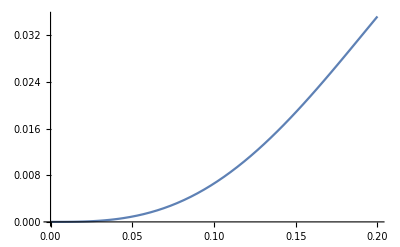

```mathematica
Block[{x=1},Plot[1/2 (-((√2 θ (x^4 (-2+θ^2) (2+θ^2)^2+32 θ^4 (6+9 θ^2+2 θ^4)+8 x θ^2 (-4+28 θ^2+55 θ^4+12 θ^6)+4 x^2 θ^2 (-12+36 θ^2+61 θ^4+12 θ^6)+2 x^3 (8-20 θ^2+22 θ^4+25 θ^6+4 θ^8)))/((2+θ^2)^2 (4 θ^2+4 x θ^2+x^2 (2+θ^2))^2))+ArcTan[(√2)/θ]-ArcTan[(2 θ^2+x (2+θ^2))/(2 √2 θ)]), {θ,0,0.2}]] (*True values of the function for ϕ=π/4.*)
```

ToDo: Combine the discontinuity limits to my equation and graph

#### h13

Have to solve for h13 manually. I think because of the Abs[dG+1. (t-1. tP)]

```mathematica
hijBasic = Simplify[Rx[B].Ry[-A].((dG*P)/Rp).Transpose[Ry[-A]].Transpose[Rx[B]]];
MatrixForm[hijBasic]
```

((dG Cos[A]^2)/Rp | -(dG Cos[A] Sin[A] Sin[B])/Rp | (dG Cos[A] Cos[B] Sin[A])/Rp
-(dG Cos[A] Sin[A] Sin[B])/Rp | (-dG Cos[B]^2+dG Sin[A]^2 Sin[B]^2)/Rp | (dG (-3+Cos[2 A]) Sin[2 B])/(4 Rp)
(dG Cos[A] Cos[B] Sin[A])/Rp | (dG (-3+Cos[2 A]) Sin[2 B])/(4 Rp) | (dG (Cos[B]^2 Sin[A]^2-Sin[B]^2))/Rp)

```mathematica
RP[dG,tP, t,θ]
```

√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ])

Manually plugging in the values for the h13 entry.

```mathematica
Simplify[Rationalize[
dG*Cos[A[DP[tP,t], dG, θ,ϕ]]Sin[A[DP[tP,t], dG, θ,ϕ]] Cos[B[DP[tP,t], dG, θ,ϕ]]*1/(√(dG^2+(-t+tP)^2-2 dG (-t+tP) Cos[θ]))
]]
```

-(dG (t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))

```mathematica
Rationalize[hijApprox[t][[1,3]]](*original h13 matrix entry*)
```

(dG (-t+tP) θ Cos[ϕ] Cos[If[-t+tP>dG,π-ArcTan[((-t+tP) θ Sin[ϕ])/Abs[dG-(1 (-t+tP)) 1]],ArcTan[((-t+tP) θ Sin[ϕ])/Abs[dG-(1 (-t+tP)) 1]]]])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) Abs[dG+t-tP] (1+((t-tP)^2 θ^2 Cos[ϕ]^2)/(dG+t-tP)^2))

Testing that these are equivalent, they are.

```mathematica
h13Manual[t_,tP_,dG_,θ_,ϕ_] :=-(dG (t-tP) (dG+(t-tP)) Cos[ϕ] θ)/((dG^2+2 dG (t-tP) +(t-tP)^2 +(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP)) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP))^2)))
```

```mathematica
h13Original[t_,tP_,dG_,θ_,ϕ_] :=(dG (-t+tP) θ Cos[ϕ] Cos[If[-t+tP>dG,π-ArcTan[((-t+tP) θ Sin[ϕ])/Abs[dG-(1 (-t+tP)) 1]],ArcTan[((-t+tP) θ Sin[ϕ])/Abs[dG-(1 (-t+tP)) 1]]]])/(√(dG^2+2 dG (t-tP)+(t-tP)^2) Abs[dG+t-tP] (1+((t-tP)^2 θ^2 Cos[ϕ]^2)/(dG+t-tP)^2))
```

```mathematica
h13Manual[2,3,3,0.002,1]
```

0.000810453

```mathematica
h13Original[2,3,3,0.002,1]
```

0.000810453

```mathematica
Manipulate[Labeled[Plot[h13Manual[t,tP,dG,θ,ϕ]-h13Original[t,tP,dG,θ,ϕ] ,{θ,0.001,0.2}, PlotRange->All],Row[{"tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}],", t = ",NumberForm[t,{3,2}],", dG = ",NumberForm[dG,{3,2}]}],Top],{tP,1,5},{ϕ,0,π},{t,-5,5},{dG,0.01,5}]
```

```mathematica
h13 = -(dG (t-tP) (dG+(t-tP)) Cos[ϕ] θ)/((dG^2+2 dG (t-tP) +(t-tP)^2 +(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP)) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP))^2)));(*taking small θ approximation of the manually found entry*)
```

```mathematica
h13dx = FullSimplify[Simplify[Simplify[θ Cos[ϕ] D[h13,tP]  + 1/(tP-t)Cos[ϕ] D[h13,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h13,ϕ], TimeConstraint->1],TimeConstraint->10] ](*partial with respect to x*)
```

(dG ((dG+t-tP) Cos[ϕ]^2 (8 (dG+t-tP)^4+8 (dG+t-tP)^3 (dG-t+tP) θ^2-(8 dG+11 (t-tP)) (t-tP)^3 θ^4-(t-tP)^4 θ^6+(t-tP)^4 θ^4 (4 Cos[2 ϕ]+(-1+θ^2) Cos[4 ϕ]))+4 (dG+t-tP)^3 (2 (dG+t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^2 θ^2 (dG+t-tP+dG θ^2) Cos[ϕ]^4 (-(dG+t-tP)^2-(t-tP)^2 θ^2 Sin[ϕ]^2)))/(8 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))

```mathematica
Simplify[Simplify[Integrate[h13dx,t] ,TimeConstraint->1]](*time integral*)
```

-((t-tP) Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(-2 dG^2-2 dG (t-tP)+(t-tP)^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(dG^2+2 dG (t-tP)+1/2 (t-tP)^2 (2+θ^2)-1/2 (t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-1/(2 θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))(-ⅈ+θ Cos[ϕ])^3 Log[((2+θ^2+θ^2 Cos[2 ϕ]) (√(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ])+((-ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((-t+tP) θ-ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Sec[ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(32 (-ⅈ+θ Cos[ϕ])^2 (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2+((1-ⅈ θ Cos[ϕ]) Log[((2+θ^2+θ^2 Cos[2 ϕ]) (√(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ])+((ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (t-tP) θ+(dG+t-tP) Cot[ϕ] Csc[ϕ]) Sec[ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(32 (ⅈ+θ Cos[ϕ])^2 (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2)/(2 θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))

```mathematica
h13Int[t_] := -((t-tP) Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(-2 dG^2-2 dG (t-tP)+(t-tP)^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(dG^2+2 dG (t-tP)+1/2 (t-tP)^2 (2+θ^2)-1/2 (t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]))-1/(2 θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))(-ⅈ+θ Cos[ϕ])^3 Log[((2+θ^2+θ^2 Cos[2 ϕ]) (√(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ])+((-ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) ((-t+tP) θ-ⅈ (dG+t-tP) Cot[ϕ] Csc[ϕ]) Sec[ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(32 (-ⅈ+θ Cos[ϕ])^2 (dG+t-tP-ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2+((1-ⅈ θ Cos[ϕ]) Log[((2+θ^2+θ^2 Cos[2 ϕ]) (√(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (-1+Cot[ϕ]) (1+Cot[ϕ])+((ⅈ+θ Cos[ϕ]) (Cos[ϕ]+Cos[3 ϕ]) (ⅈ (t-tP) θ+(dG+t-tP) Cot[ϕ] Csc[ϕ]) Sec[ϕ])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))/(32 (ⅈ+θ Cos[ϕ])^2 (dG+t-tP+ⅈ (t-tP) θ Cos[ϕ]))] Sin[ϕ]^2)/(2 θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))
```

```mathematica
h13DefInt = Simplify[Simplify[h13Int[TminApprox[tP,dG]] - h13Int[tP],TimeConstraint->1],TimeConstraint->10](*Definite integral*)
```

1/2 ((2 √2 (2 dG+tP) Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]+4 dG θ Cos[2 ϕ]+4 tP θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2+(ⅈ (ⅈ+θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+((1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]-4 ⅈ dG θ Cos[2 ϕ]-4 ⅈ tP θ Cos[2 ϕ]+2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))

Expressing in terms of x = tP/dG

```mathematica
δ13X = Block[{tP = dG*x}, Simplify[Simplify[1/2 ((2 √2 (2 dG+tP) Cos[ϕ]^2 (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(4 dG^2+8 dG tP+tP^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]+4 dG θ Cos[2 ϕ]+4 tP θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2+(ⅈ (ⅈ+θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+((1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]-4 ⅈ dG θ Cos[2 ϕ]-4 ⅈ tP θ Cos[2 ϕ]+2 ⅈ √2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)-(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))),TimeConstraint->1],TimeConstraint->10]]
```

1/2 ((2 √2 (2+x) Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2+(ⅈ (ⅈ+θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+((1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))

```mathematica
δ13X = 1/2 ((2 √2 (2+x) Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2+(ⅈ (ⅈ+θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+((1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])));
```

We multiply δ13X by 2θ Cos[ϕ] when we apply the n^j n^l looking vector to get the final d13 expression.

```mathematica
Simplify[2 δ13X θ Cos[ϕ]]
```

Cos[ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2)

```mathematica
d13[x_,θ_,ϕ_] := Cos[ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2)
```

Plotting the final expression. There are discontinuities at  π/4, 3π/4,-π/4, and -3π/4.

```mathematica
ContourPlot[Re[d13[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None](*using Exclusions->None to remove ArcTan discontinuities.*)
```

-Graphics-

#### d13 discontinuities - work in progress

The discontinuities in h13 are not physical and we can remove them by taking the limit and l’hopital’s rule. 
I will attempt to use the same approach that worked for h23. I ran out of time before being able to successfully take the limit, but I believe the process is straightforward from here. See the notes below.

```mathematica
d13[x,θ,ϕ]
```

Cos[ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((-ⅈ+θ Cos[ϕ])^3 Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+(ⅈ (ⅈ+θ Cos[ϕ])^3 Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sin[ϕ]^2)/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(1-ⅈ θ Cos[ϕ]) Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))] Sec[2 ϕ] Sin[ϕ]^2+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))(-ⅈ+θ Cos[ϕ]) Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ] Sin[ϕ]^2)

Together separates d13 into a single fraction. The numerator and denominator are below.

```mathematica
Simplify[Simplify[Together[d13[x,θ,ϕ] ],TimeConstraint->1],TimeConstraint->20]
```

Cos[ϕ] Sec[2 ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]))/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((ⅈ Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))]) Sin[ϕ]^2+θ Cos[ϕ] (-Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(ⅈ Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))]) Sin[ϕ]^2)

```mathematica
Limit[Cos[ϕ] Sec[2 ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(4+8 x+x^2) θ^2 Cos[2 ϕ]))/(√(4 θ^2+4 x θ^2+x^2 (2+θ^2)-(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+((ⅈ Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]-1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))]) Sin[ϕ]^2+θ Cos[ϕ] (-Log[-(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-ⅈ θ-2 Cos[ϕ]-ⅈ θ Cos[2 ϕ]+2 √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+(ⅈ Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))-1/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))ⅈ Log[(Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (4 ⅈ θ+2 θ^2 Cos[ϕ]+x (4+θ^2) Cos[ϕ]-4 ⅈ (1+x) θ Cos[2 ϕ]+2 ⅈ √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+1/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))Log[-((Cos[2 ϕ]^2 (2+θ^2+θ^2 Cos[2 ϕ]) (-4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]+4 θ Cos[2 ϕ]+4 x θ Cos[2 ϕ]-2 ⅈ √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Csc[ϕ]^2)/(64 (ⅈ x+(2+x) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))]) Sin[ϕ]^2),ϕ->π/4]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

$Aborted

I tried taking the limit in many different ways, I’ve added some of them below. The best method, I believe, will be to copy what worked for d23. That is, finding a numerator and denominator that can be used with l’hopital’s rule. It’s difficult to manipulate the expression to find the right numerator and denominator.

```mathematica
Simplify[Limit[num''[ϕ]/den''[ϕ],ϕ->π/4]]
```

```mathematica
Limit[Simplify[d13[1,θ,ϕ]],ϕ->π/4]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

$Aborted

```mathematica
Limit[Simplify[d13[x,0.3,ϕ]],ϕ->π/4]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

```mathematica
exprV = Block[{ϕ=v+π/4},Simplify[expr]]
```

```mathematica
Series[exprV,{v,0,1}]
```

-1/(8 (√2 √(-2-2 ⅈ √2 θ+θ^2)) v^(3/2))(√2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2 ⅈ Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+√2 θ Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+2 ⅈ Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-√2 θ Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-√2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))])+(-32 ⅈ √2 x^2 θ √(-2-2 ⅈ √2 θ+θ^2)-16 ⅈ √2 x^3 θ √(-2-2 ⅈ √2 θ+θ^2)-32 x^2 θ^2 √(-2-2 ⅈ √2 θ+θ^2)-16 x^3 θ^2 √(-2-2 ⅈ √2 θ+θ^2)-64 ⅈ √2 θ^3 √(-2-2 ⅈ √2 θ+θ^2)-96 ⅈ √2 x θ^3 √(-2-2 ⅈ √2 θ+θ^2)-80 ⅈ √2 x^2 θ^3 √(-2-2 ⅈ √2 θ+θ^2)-24 ⅈ √2 x^3 θ^3 √(-2-2 ⅈ √2 θ+θ^2)-64 θ^4 √(-2-2 ⅈ √2 θ+θ^2)-96 x θ^4 √(-2-2 ⅈ √2 θ+θ^2)-80 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2)-24 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2)-64 ⅈ √2 θ^5 √(-2-2 ⅈ √2 θ+θ^2)-96 ⅈ √2 x θ^5 √(-2-2 ⅈ √2 θ+θ^2)-56 ⅈ √2 x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2)-12 ⅈ √2 x^3 θ^5 √(-2-2 ⅈ √2 θ+θ^2)-64 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-96 x θ^6 √(-2-2 ⅈ √2 θ+θ^2)-56 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-12 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-16 ⅈ √2 θ^7 √(-2-2 ⅈ √2 θ+θ^2)-24 ⅈ √2 x θ^7 √(-2-2 ⅈ √2 θ+θ^2)-12 ⅈ √2 x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2)-2 ⅈ √2 x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2)-16 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-24 x θ^8 √(-2-2 ⅈ √2 θ+θ^2)-12 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-4 √2 x √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 ⅈ θ √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4 ⅈ x θ √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-4 √2 x θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 ⅈ θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4 ⅈ x θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-√2 x θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2 ⅈ θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+ⅈ x θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 x √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 ⅈ √2 θ √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+12 x θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 ⅈ √2 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6 x θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2 ⅈ √2 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+x θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2)))/(√2 (√2-ⅈ θ) (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2) (2 √2 x-4 ⅈ θ+2 √2 θ^2+√2 x θ^2) (2 √2 x+4 ⅈ θ+2 √2 θ^2+√2 x θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) v)+(32 √2 x^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-192 ⅈ x^2 θ √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-192 √2 x θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+96 √2 x^2 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+80 √2 x^3 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+128 ⅈ θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-384 ⅈ x θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-384 ⅈ x^2 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-192 √2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-192 √2 x θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+192 √2 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+80 √2 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-64 ⅈ θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-576 ⅈ x θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-288 ⅈ x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-160 √2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+144 √2 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+40 √2 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-160 ⅈ θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-288 ⅈ x θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-96 ⅈ x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-16 √2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+48 √2 x θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+48 √2 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+10 √2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-48 ⅈ θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-48 ⅈ x θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-12 ⅈ x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+8 √2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+12 √2 x θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+6 √2 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+√2 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-64 ⅈ x^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-192 √2 x^2 θ Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+32 √2 x^3 θ Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+384 ⅈ x θ^2 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-384 ⅈ x^2 θ^2 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-160 ⅈ x^3 θ^2 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+128 √2 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-576 √2 x θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-288 √2 x^2 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+80 √2 x^3 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+512 ⅈ θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-768 ⅈ x^2 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-160 ⅈ x^3 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-256 √2 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-768 √2 x θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-96 √2 x^2 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+80 √2 x^3 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+256 ⅈ θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-576 ⅈ x θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-576 ⅈ x^2 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-80 ⅈ x^3 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-320 √2 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-288 √2 x θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+48 √2 x^2 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+40 √2 x^3 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-128 ⅈ θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-384 ⅈ x θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-192 ⅈ x^2 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-20 ⅈ x^3 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-64 √2 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+36 √2 x^2 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+10 √2 x^3 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-64 ⅈ θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-72 ⅈ x θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-24 ⅈ x^2 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-2 ⅈ x^3 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+8 √2 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+12 √2 x θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+6 √2 x^2 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+√2 x^3 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+64 ⅈ x^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+192 √2 x^2 θ Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-32 √2 x^3 θ Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-384 ⅈ x θ^2 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+384 ⅈ x^2 θ^2 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+160 ⅈ x^3 θ^2 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-128 √2 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+576 √2 x θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+288 √2 x^2 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-80 √2 x^3 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-512 ⅈ θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+768 ⅈ x^2 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+160 ⅈ x^3 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+256 √2 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+768 √2 x θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+96 √2 x^2 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-80 √2 x^3 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-256 ⅈ θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+576 ⅈ x θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+576 ⅈ x^2 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+80 ⅈ x^3 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+320 √2 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+288 √2 x θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-48 √2 x^2 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-40 √2 x^3 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+128 ⅈ θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+384 ⅈ x θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+192 ⅈ x^2 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+20 ⅈ x^3 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+64 √2 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-36 √2 x^2 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-10 √2 x^3 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+64 ⅈ θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+72 ⅈ x θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+24 ⅈ x^2 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+2 ⅈ x^3 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-8 √2 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-12 √2 x θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-6 √2 x^2 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-√2 x^3 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-32 √2 x^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+192 ⅈ x^2 θ √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+192 √2 x θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-96 √2 x^2 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-80 √2 x^3 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-128 ⅈ θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+384 ⅈ x θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+384 ⅈ x^2 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+192 √2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+192 √2 x θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-192 √2 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-80 √2 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+64 ⅈ θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+576 ⅈ x θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+288 ⅈ x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+160 √2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-144 √2 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-40 √2 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+160 ⅈ θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+288 ⅈ x θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+96 ⅈ x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+16 √2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-48 √2 x θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-48 √2 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-10 √2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+48 ⅈ θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+48 ⅈ x θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+12 ⅈ x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-8 √2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-12 √2 x θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-6 √2 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-√2 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))])/(√2 (√2+ⅈ θ)^2 (-2 ⅈ+√2 θ) (2 ⅈ+√2 θ)^2 (2 ⅈ x+2 √2 θ+√2 x θ) √(-2-2 ⅈ √2 θ+θ^2) (2 √2 x-4 ⅈ θ+2 √2 θ^2+√2 x θ^2)^2 √v)+(8 √2 (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2)^(3/2) (18432 ⅈ √2 x^4 θ √(-2-2 ⅈ √2 θ+θ^2)+9216 ⅈ √2 x^5 θ √(-2-2 ⅈ √2 θ+θ^2)+18432 x^4 θ^2 √(-2-2 ⅈ √2 θ+θ^2)+9216 x^5 θ^2 √(-2-2 ⅈ √2 θ+θ^2)+36864 ⅈ √2 x^2 θ^3 √(-2-2 ⅈ √2 θ+θ^2)+30720 ⅈ √2 x^3 θ^3 √(-2-2 ⅈ √2 θ+θ^2)+79872 ⅈ √2 x^4 θ^3 √(-2-2 ⅈ √2 θ+θ^2)+36864 ⅈ √2 x^5 θ^3 √(-2-2 ⅈ √2 θ+θ^2)+36864 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2)+30720 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2)+79872 x^4 θ^4 √(-2-2 ⅈ √2 θ+θ^2)+36864 x^5 θ^4 √(-2-2 ⅈ √2 θ+θ^2)-49152 ⅈ √2 x θ^5 √(-2-2 ⅈ √2 θ+θ^2)+55296 ⅈ √2 x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+70656 ⅈ √2 x^3 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+144384 ⅈ √2 x^4 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+64512 ⅈ √2 x^5 θ^5 √(-2-2 ⅈ √2 θ+θ^2)-49152 x θ^6 √(-2-2 ⅈ √2 θ+θ^2)+55296 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2)+70656 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2)+144384 x^4 θ^6 √(-2-2 ⅈ √2 θ+θ^2)+64512 x^5 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-172032 ⅈ √2 x θ^7 √(-2-2 ⅈ √2 θ+θ^2)-64512 ⅈ √2 x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+32256 ⅈ √2 x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+139776 ⅈ √2 x^4 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+64512 ⅈ √2 x^5 θ^7 √(-2-2 ⅈ √2 θ+θ^2)-172032 x θ^8 √(-2-2 ⅈ √2 θ+θ^2)-64512 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2)+32256 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2)+139776 x^4 θ^8 √(-2-2 ⅈ √2 θ+θ^2)+64512 x^5 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-258048 ⅈ √2 x θ^9 √(-2-2 ⅈ √2 θ+θ^2)-225792 ⅈ √2 x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2)-59136 ⅈ √2 x^3 θ^9 √(-2-2 ⅈ √2 θ+θ^2)+75264 ⅈ √2 x^4 θ^9 √(-2-2 ⅈ √2 θ+θ^2)+40320 ⅈ √2 x^5 θ^9 √(-2-2 ⅈ √2 θ+θ^2)-258048 x θ^10 √(-2-2 ⅈ √2 θ+θ^2)-225792 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-59136 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2)+75264 x^4 θ^10 √(-2-2 ⅈ √2 θ+θ^2)+40320 x^5 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-215040 ⅈ √2 x θ^11 √(-2-2 ⅈ √2 θ+θ^2)-241920 ⅈ √2 x^2 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-94080 ⅈ √2 x^3 θ^11 √(-2-2 ⅈ √2 θ+θ^2)+18816 ⅈ √2 x^4 θ^11 √(-2-2 ⅈ √2 θ+θ^2)+16128 ⅈ √2 x^5 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-215040 x θ^12 √(-2-2 ⅈ √2 θ+θ^2)-241920 x^2 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-94080 x^3 θ^12 √(-2-2 ⅈ √2 θ+θ^2)+18816 x^4 θ^12 √(-2-2 ⅈ √2 θ+θ^2)+16128 x^5 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-107520 ⅈ √2 x θ^13 √(-2-2 ⅈ √2 θ+θ^2)-137088 ⅈ √2 x^2 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-60480 ⅈ √2 x^3 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-1344 ⅈ √2 x^4 θ^13 √(-2-2 ⅈ √2 θ+θ^2)+4032 ⅈ √2 x^5 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-107520 x θ^14 √(-2-2 ⅈ √2 θ+θ^2)-137088 x^2 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-60480 x^3 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-1344 x^4 θ^14 √(-2-2 ⅈ √2 θ+θ^2)+4032 x^5 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-32256 ⅈ √2 x θ^15 √(-2-2 ⅈ √2 θ+θ^2)-44352 ⅈ √2 x^2 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-20832 ⅈ √2 x^3 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-2208 ⅈ √2 x^4 θ^15 √(-2-2 ⅈ √2 θ+θ^2)+576 ⅈ √2 x^5 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-32256 x θ^16 √(-2-2 ⅈ √2 θ+θ^2)-44352 x^2 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-20832 x^3 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-2208 x^4 θ^16 √(-2-2 ⅈ √2 θ+θ^2)+576 x^5 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-5376 ⅈ √2 x θ^17 √(-2-2 ⅈ √2 θ+θ^2)-7776 ⅈ √2 x^2 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-3792 ⅈ √2 x^3 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-552 ⅈ √2 x^4 θ^17 √(-2-2 ⅈ √2 θ+θ^2)+36 ⅈ √2 x^5 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-5376 x θ^18 √(-2-2 ⅈ √2 θ+θ^2)-7776 x^2 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-3792 x^3 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-552 x^4 θ^18 √(-2-2 ⅈ √2 θ+θ^2)+36 x^5 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-384 ⅈ √2 x θ^19 √(-2-2 ⅈ √2 θ+θ^2)-576 ⅈ √2 x^2 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-288 ⅈ √2 x^3 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-48 ⅈ √2 x^4 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-384 x θ^20 √(-2-2 ⅈ √2 θ+θ^2)-576 x^2 θ^20 √(-2-2 ⅈ √2 θ+θ^2)-288 x^3 θ^20 √(-2-2 ⅈ √2 θ+θ^2)-48 x^4 θ^20 √(-2-2 ⅈ √2 θ+θ^2)-512 √2 x^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1536 ⅈ x^2 θ √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+768 ⅈ x^3 θ √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1536 √2 x θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1536 √2 x^2 θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-2176 √2 x^3 θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4096 ⅈ θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6144 ⅈ x θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8448 ⅈ x^2 θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3200 ⅈ x^3 θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-5376 √2 x θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-5376 √2 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-4032 √2 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+14336 ⅈ θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+21504 ⅈ x θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+18816 ⅈ x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+5824 ⅈ x^3 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-8064 √2 x θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-8064 √2 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-4256 √2 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+21504 ⅈ θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+32256 ⅈ x θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+22848 ⅈ x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6048 ⅈ x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6720 √2 x θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6720 √2 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-2800 √2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+17920 ⅈ θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+26880 ⅈ x θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+16800 ⅈ x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3920 ⅈ x^3 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3360 √2 x θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3360 √2 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1176 √2 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8960 ⅈ θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+13440 ⅈ x θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+7728 ⅈ x^2 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1624 ⅈ x^3 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1008 √2 x θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1008 √2 x^2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-308 √2 x^3 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2688 ⅈ θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4032 ⅈ x θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2184 ⅈ x^2 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+420 ⅈ x^3 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-168 √2 x θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-168 √2 x^2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-46 √2 x^3 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+448 ⅈ θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+672 ⅈ x θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+348 ⅈ x^2 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+62 ⅈ x^3 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-12 √2 x θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-12 √2 x^2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3 √2 x^3 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+32 ⅈ θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+48 ⅈ x θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+24 ⅈ x^2 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4 ⅈ x^3 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1024 x^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1536 ⅈ √2 x^2 θ √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+256 ⅈ √2 x^3 θ √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3072 x θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4608 x^2 θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+5120 x^3 θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4096 ⅈ √2 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4608 ⅈ √2 x θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6912 ⅈ √2 x^2 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1024 ⅈ √2 x^3 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4096 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+16896 x θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+19200 x^2 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+11264 x^3 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+14336 ⅈ √2 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+16128 ⅈ √2 x θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+13440 ⅈ √2 x^2 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1792 ⅈ √2 x^3 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+14336 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+37632 x θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+34944 x^2 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+14336 x^3 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+21504 ⅈ √2 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+24192 ⅈ √2 x θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+14784 ⅈ √2 x^2 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1792 ⅈ √2 x^3 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+21504 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+45696 x θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+36288 x^2 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+11648 x^3 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+17920 ⅈ √2 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+20160 ⅈ √2 x θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+10080 ⅈ √2 x^2 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1120 ⅈ √2 x^3 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+17920 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+33600 x θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+23520 x^2 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6272 x^3 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8960 ⅈ √2 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+10080 ⅈ √2 x θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4368 ⅈ √2 x^2 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+448 ⅈ √2 x^3 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8960 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+15456 x θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+9744 x^2 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2240 x^3 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2688 ⅈ √2 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3024 ⅈ √2 x θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1176 ⅈ √2 x^2 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+112 ⅈ √2 x^3 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2688 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4368 x θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2520 x^2 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+512 x^3 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+448 ⅈ √2 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+504 ⅈ √2 x θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+180 ⅈ √2 x^2 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+16 ⅈ √2 x^3 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+448 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+696 x θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+372 x^2 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+68 x^3 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+32 ⅈ √2 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+36 ⅈ √2 x θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+12 ⅈ √2 x^2 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+ⅈ √2 x^3 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+32 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+48 x θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+24 x^2 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4 x^3 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))))/(3 (√2-ⅈ θ)^3 (√2+ⅈ θ)^3 (-2 ⅈ+√2 θ) (2 ⅈ+√2 θ)^2 (-2 ⅈ x+2 √2 θ+√2 x θ) (2 ⅈ x+2 √2 θ+√2 x θ) √(-2-2 ⅈ √2 θ+θ^2) (2 √2 x-4 ⅈ θ+2 √2 θ^2+√2 x θ^2)^3 (2 √2 x+4 ⅈ θ+2 √2 θ^2+√2 x θ^2)^3)+(6 √2 (-512 ⅈ √2 x^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-6144 x^5 θ √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+512 x^6 θ √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+15360 ⅈ √2 x^4 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-6144 ⅈ √2 x^5 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2304 ⅈ √2 x^6 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+40960 x^3 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-46080 x^4 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-21504 x^5 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+2304 x^6 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-30720 ⅈ √2 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+81920 ⅈ √2 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+30720 ⅈ √2 x^4 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-24576 ⅈ √2 x^5 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-4608 ⅈ √2 x^6 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-24576 x θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+153600 x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-153600 x^4 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-30720 x^5 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+4608 x^6 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+4096 ⅈ √2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-73728 ⅈ √2 x θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+76800 ⅈ √2 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+204800 ⅈ √2 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-43008 ⅈ √2 x^5 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-5376 ⅈ √2 x^6 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-28672 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+135168 x θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+230400 x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-204800 x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-215040 x^4 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-21504 x^5 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+5376 x^6 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-36864 ⅈ √2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-24576 ⅈ √2 x θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+268800 ⅈ √2 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+184320 ⅈ √2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-53760 ⅈ √2 x^4 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-43008 ⅈ √2 x^5 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-4032 ⅈ √2 x^6 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+28672 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+239616 x θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+7680 x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-327680 x^3 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-161280 x^4 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-5376 x^5 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+4032 x^6 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-25600 ⅈ √2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+116736 ⅈ √2 x θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+249600 ⅈ √2 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+51200 ⅈ √2 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-67200 ⅈ √2 x^4 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-26880 ⅈ √2 x^5 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2016 ⅈ √2 x^6 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+64512 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+82944 x θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-172800 x^2 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-230400 x^3 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-67200 x^4 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+2688 x^5 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+2016 x^6 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+18432 ⅈ √2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+110592 ⅈ √2 x θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+86400 ⅈ √2 x^2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-25600 ⅈ √2 x^3 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-40320 ⅈ √2 x^4 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-10752 ⅈ √2 x^5 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-672 ⅈ √2 x^6 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+18432 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-41472 x θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-124800 x^2 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-81920 x^3 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-13440 x^4 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+2688 x^5 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+672 x^6 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+16128 ⅈ √2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+29184 ⅈ √2 x θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-960 ⅈ √2 x^2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-23040 ⅈ √2 x^3 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-13440 ⅈ √2 x^4 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2688 ⅈ √2 x^5 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-144 ⅈ √2 x^6 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-6400 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-29952 x θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-33600 x^2 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-12800 x^3 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+960 x^5 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+144 x^6 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+1792 ⅈ √2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-1536 ⅈ √2 x θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-7200 ⅈ √2 x^2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-6400 ⅈ √2 x^3 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2400 ⅈ √2 x^4 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-384 ⅈ √2 x^5 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-18 ⅈ √2 x^6 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2304 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-4224 x θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-2400 x^2 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+480 x^4 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+168 x^5 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+18 x^6 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-448 ⅈ √2 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-1152 ⅈ √2 x θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-1200 ⅈ √2 x^2 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-640 ⅈ √2 x^3 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-180 ⅈ √2 x^4 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-24 ⅈ √2 x^5 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-ⅈ √2 x^6 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+64 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+192 x θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+240 x^2 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+160 x^3 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+60 x^4 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+12 x^5 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]+x^6 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[(8 √2 √v (√2-ⅈ θ) (-2 ⅈ+√2 θ))/(2 ⅈ+√2 θ)^2]-1024 x^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+6144 ⅈ √2 x^5 θ Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-1024 ⅈ √2 x^6 θ Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+30720 x^4 θ^2 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-18432 x^5 θ^2 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-4096 x^6 θ^2 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-40960 ⅈ √2 x^3 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+61440 ⅈ √2 x^4 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+15360 ⅈ √2 x^5 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-4608 ⅈ √2 x^6 θ^3 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-61440 x^2 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+204800 x^3 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+15360 x^4 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-70656 x^5 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-6912 x^6 θ^4 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+24576 ⅈ √2 x θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-184320 ⅈ √2 x^2 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+81920 ⅈ √2 x^3 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+184320 ⅈ √2 x^4 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+6144 ⅈ √2 x^5 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-9216 ⅈ √2 x^6 θ^5 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+8192 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-172032 x θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+307200 x^2 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+409600 x^3 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-153600 x^4 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-116736 x^5 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-6144 x^6 θ^6 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+32768 ⅈ √2 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-208896 ⅈ √2 x θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-153600 ⅈ √2 x^2 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+409600 ⅈ √2 x^3 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+215040 ⅈ √2 x^4 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-21504 ⅈ √2 x^5 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-10752 ⅈ √2 x^6 θ^7 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-102400 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+86016 x θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+768000 x^2 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+163840 x^3 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-322560 x^4 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-107520 x^5 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-2688 x^6 θ^8 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-65536 ⅈ √2 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-264192 ⅈ √2 x θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+261120 ⅈ √2 x^2 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+512000 ⅈ √2 x^3 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+107520 ⅈ √2 x^4 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-37632 ⅈ √2 x^5 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-8064 ⅈ √2 x^6 θ^9 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-22528 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+473088 x θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+506880 x^2 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-225280 x^3 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-295680 x^4 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-59136 x^5 θ^10 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-90112 ⅈ √2 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+33792 ⅈ √2 x θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+422400 ⅈ √2 x^2 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+281600 ⅈ √2 x^3 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-29568 ⅈ √2 x^5 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-4032 ⅈ √2 x^6 θ^11 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+101376 θ^12 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+304128 x θ^12 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-281600 x^3 θ^12 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-147840 x^4 θ^12 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-18816 x^5 θ^12 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+672 x^6 θ^12 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+152064 ⅈ √2 x θ^13 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+211200 ⅈ √2 x^2 θ^13 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+56320 ⅈ √2 x^3 θ^13 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-26880 ⅈ √2 x^4 θ^13 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-13440 ⅈ √2 x^5 θ^13 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-1344 ⅈ √2 x^6 θ^13 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+50688 θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+16896 x θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-126720 x^2 θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-128000 x^3 θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-40320 x^4 θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-2688 x^5 θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+384 x^6 θ^14 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+22528 ⅈ √2 θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+59136 ⅈ √2 x θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+32640 ⅈ √2 x^2 θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-10240 ⅈ √2 x^3 θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-13440 ⅈ √2 x^4 θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-3648 ⅈ √2 x^5 θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-288 ⅈ √2 x^6 θ^15 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-2816 θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-33024 x θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-48000 x^2 θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-25600 x^3 θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-4800 x^4 θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+192 x^5 θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+108 x^6 θ^16 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+4096 ⅈ √2 θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+2688 ⅈ √2 x θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-4800 ⅈ √2 x^2 θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-6400 ⅈ √2 x^3 θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-2880 ⅈ √2 x^4 θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-552 ⅈ √2 x^5 θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-36 ⅈ √2 x^6 θ^17 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-3200 θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-6528 x θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-4800 x^2 θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-1280 x^3 θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+120 x^4 θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+120 x^5 θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+16 x^6 θ^18 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-512 ⅈ √2 θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-1344 ⅈ √2 x θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-1440 ⅈ √2 x^2 θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-800 ⅈ √2 x^3 θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-240 ⅈ √2 x^4 θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-36 ⅈ √2 x^5 θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]-2 ⅈ √2 x^6 θ^19 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+64 θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+192 x θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+240 x^2 θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+160 x^3 θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+60 x^4 θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+12 x^5 θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+x^6 θ^20 Log[(√v (√2+ⅈ θ) (2 ⅈ+√2 θ) √(-2-2 ⅈ √2 θ+θ^2))/(8 (-2 ⅈ+√2 θ)^3)]+1024 x^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-6144 ⅈ √2 x^5 θ Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+1024 ⅈ √2 x^6 θ Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-30720 x^4 θ^2 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+18432 x^5 θ^2 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+4096 x^6 θ^2 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+40960 ⅈ √2 x^3 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-61440 ⅈ √2 x^4 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-15360 ⅈ √2 x^5 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+4608 ⅈ √2 x^6 θ^3 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+61440 x^2 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-204800 x^3 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-15360 x^4 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+70656 x^5 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+6912 x^6 θ^4 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-24576 ⅈ √2 x θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+184320 ⅈ √2 x^2 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-81920 ⅈ √2 x^3 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-184320 ⅈ √2 x^4 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-6144 ⅈ √2 x^5 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+9216 ⅈ √2 x^6 θ^5 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-8192 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+172032 x θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-307200 x^2 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-409600 x^3 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+153600 x^4 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+116736 x^5 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+6144 x^6 θ^6 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-32768 ⅈ √2 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+208896 ⅈ √2 x θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+153600 ⅈ √2 x^2 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-409600 ⅈ √2 x^3 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-215040 ⅈ √2 x^4 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+21504 ⅈ √2 x^5 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+10752 ⅈ √2 x^6 θ^7 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+102400 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-86016 x θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-768000 x^2 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-163840 x^3 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+322560 x^4 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+107520 x^5 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+2688 x^6 θ^8 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+65536 ⅈ √2 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+264192 ⅈ √2 x θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-261120 ⅈ √2 x^2 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-512000 ⅈ √2 x^3 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-107520 ⅈ √2 x^4 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+37632 ⅈ √2 x^5 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+8064 ⅈ √2 x^6 θ^9 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+22528 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-473088 x θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-506880 x^2 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+225280 x^3 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+295680 x^4 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+59136 x^5 θ^10 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+90112 ⅈ √2 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-33792 ⅈ √2 x θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-422400 ⅈ √2 x^2 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-281600 ⅈ √2 x^3 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+29568 ⅈ √2 x^5 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+4032 ⅈ √2 x^6 θ^11 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-101376 θ^12 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-304128 x θ^12 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+281600 x^3 θ^12 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+147840 x^4 θ^12 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+18816 x^5 θ^12 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-672 x^6 θ^12 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-152064 ⅈ √2 x θ^13 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-211200 ⅈ √2 x^2 θ^13 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-56320 ⅈ √2 x^3 θ^13 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+26880 ⅈ √2 x^4 θ^13 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+13440 ⅈ √2 x^5 θ^13 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+1344 ⅈ √2 x^6 θ^13 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-50688 θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-16896 x θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+126720 x^2 θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+128000 x^3 θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+40320 x^4 θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+2688 x^5 θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-384 x^6 θ^14 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-22528 ⅈ √2 θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-59136 ⅈ √2 x θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-32640 ⅈ √2 x^2 θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+10240 ⅈ √2 x^3 θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+13440 ⅈ √2 x^4 θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+3648 ⅈ √2 x^5 θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+288 ⅈ √2 x^6 θ^15 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+2816 θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+33024 x θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+48000 x^2 θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+25600 x^3 θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+4800 x^4 θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-192 x^5 θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-108 x^6 θ^16 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-4096 ⅈ √2 θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-2688 ⅈ √2 x θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+4800 ⅈ √2 x^2 θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+6400 ⅈ √2 x^3 θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+2880 ⅈ √2 x^4 θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+552 ⅈ √2 x^5 θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+36 ⅈ √2 x^6 θ^17 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+3200 θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+6528 x θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+4800 x^2 θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+1280 x^3 θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-120 x^4 θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-120 x^5 θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-16 x^6 θ^18 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+512 ⅈ √2 θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+1344 ⅈ √2 x θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+1440 ⅈ √2 x^2 θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+800 ⅈ √2 x^3 θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+240 ⅈ √2 x^4 θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+36 ⅈ √2 x^5 θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+2 ⅈ √2 x^6 θ^19 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-64 θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-192 x θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-240 x^2 θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-160 x^3 θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-60 x^4 θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-12 x^5 θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]-x^6 θ^20 Log[(√v (ⅈ+θ/(√2)) √(-2-2 ⅈ √2 θ+θ^2) ((ⅈ (2+x) θ^2)/(√2)+2 ((ⅈ x)/(√2)+θ)))/(32 (-ⅈ+θ/(√2))^3 (ⅈ x+((2+x) θ)/(√2)))]+512 ⅈ √2 x^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+6144 x^5 θ √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-512 x^6 θ √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-15360 ⅈ √2 x^4 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+6144 ⅈ √2 x^5 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+2304 ⅈ √2 x^6 θ^2 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-40960 x^3 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+46080 x^4 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+21504 x^5 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-2304 x^6 θ^3 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+30720 ⅈ √2 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-81920 ⅈ √2 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-30720 ⅈ √2 x^4 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+24576 ⅈ √2 x^5 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+4608 ⅈ √2 x^6 θ^4 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+24576 x θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-153600 x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+153600 x^4 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+30720 x^5 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-4608 x^6 θ^5 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-4096 ⅈ √2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+73728 ⅈ √2 x θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-76800 ⅈ √2 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-204800 ⅈ √2 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+43008 ⅈ √2 x^5 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+5376 ⅈ √2 x^6 θ^6 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+28672 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-135168 x θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-230400 x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+204800 x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+215040 x^4 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+21504 x^5 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-5376 x^6 θ^7 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+36864 ⅈ √2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+24576 ⅈ √2 x θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-268800 ⅈ √2 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-184320 ⅈ √2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+53760 ⅈ √2 x^4 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+43008 ⅈ √2 x^5 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+4032 ⅈ √2 x^6 θ^8 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-28672 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-239616 x θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-7680 x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+327680 x^3 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+161280 x^4 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+5376 x^5 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-4032 x^6 θ^9 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+25600 ⅈ √2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-116736 ⅈ √2 x θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-249600 ⅈ √2 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-51200 ⅈ √2 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+67200 ⅈ √2 x^4 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+26880 ⅈ √2 x^5 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+2016 ⅈ √2 x^6 θ^10 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-64512 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-82944 x θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+172800 x^2 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+230400 x^3 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+67200 x^4 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-2688 x^5 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-2016 x^6 θ^11 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-18432 ⅈ √2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-110592 ⅈ √2 x θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-86400 ⅈ √2 x^2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+25600 ⅈ √2 x^3 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+40320 ⅈ √2 x^4 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+10752 ⅈ √2 x^5 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+672 ⅈ √2 x^6 θ^12 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-18432 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+41472 x θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+124800 x^2 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+81920 x^3 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+13440 x^4 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-2688 x^5 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-672 x^6 θ^13 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-16128 ⅈ √2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-29184 ⅈ √2 x θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+960 ⅈ √2 x^2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+23040 ⅈ √2 x^3 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+13440 ⅈ √2 x^4 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+2688 ⅈ √2 x^5 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+144 ⅈ √2 x^6 θ^14 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+6400 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+29952 x θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+33600 x^2 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+12800 x^3 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-960 x^5 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-144 x^6 θ^15 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-1792 ⅈ √2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+1536 ⅈ √2 x θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+7200 ⅈ √2 x^2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+6400 ⅈ √2 x^3 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+2400 ⅈ √2 x^4 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+384 ⅈ √2 x^5 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+18 ⅈ √2 x^6 θ^16 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+2304 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+4224 x θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+2400 x^2 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-480 x^4 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-168 x^5 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-18 x^6 θ^17 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+448 ⅈ √2 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+1152 ⅈ √2 x θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+1200 ⅈ √2 x^2 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+640 ⅈ √2 x^3 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+180 ⅈ √2 x^4 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+24 ⅈ √2 x^5 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]+ⅈ √2 x^6 θ^18 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-64 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-192 x θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-240 x^2 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-160 x^3 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-60 x^4 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-12 x^5 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]-x^6 θ^19 √(-2-2 ⅈ √2 θ+θ^2) Log[-(2 ⅈ √2 √v (-ⅈ+θ/(√2)) (4 ⅈ θ+2 √2 (x+1/2 (2+x) θ^2)))/((ⅈ+θ/(√2)) (x+(θ (2 ⅈ+((2+x) θ)/(√2)))/(√2)))]) √v)/((√2+ⅈ θ)^4 (-2 ⅈ+√2 θ)^2 (2 ⅈ+√2 θ)^3 (2 ⅈ x+2 √2 θ+√2 x θ)^2 √(-2-2 ⅈ √2 θ+θ^2) (2 √2 x-4 ⅈ θ+2 √2 θ^2+√2 x θ^2)^4)+(256 √2 (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2)^(7/2) (-17039360 √2 x^6 θ √(-2-2 ⅈ √2 θ+θ^2)-8519680 √2 x^7 θ √(-2-2 ⅈ √2 θ+θ^2)+68157440 ⅈ x^6 θ^2 √(-2-2 ⅈ √2 θ+θ^2)+34078720 ⅈ x^7 θ^2 √(-2-2 ⅈ √2 θ+θ^2)+39321600 √2 x^4 θ^3 √(-2-2 ⅈ √2 θ+θ^2)+153354240 √2 x^5 θ^3 √(-2-2 ⅈ √2 θ+θ^2)+25559040 √2 x^6 θ^3 √(-2-2 ⅈ √2 θ+θ^2)-20643840 √2 x^7 θ^3 √(-2-2 ⅈ √2 θ+θ^2)-157286400 ⅈ x^4 θ^4 √(-2-2 ⅈ √2 θ+θ^2)-613416960 ⅈ x^5 θ^4 √(-2-2 ⅈ √2 θ+θ^2)+68157440 ⅈ x^6 θ^4 √(-2-2 ⅈ √2 θ+θ^2)+167772160 ⅈ x^7 θ^4 √(-2-2 ⅈ √2 θ+θ^2)+188743680 √2 x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+786432000 √2 x^3 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+1061683200 √2 x^4 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+931921920 √2 x^5 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+349634560 √2 x^6 θ^5 √(-2-2 ⅈ √2 θ+θ^2)+31293440 √2 x^7 θ^5 √(-2-2 ⅈ √2 θ+θ^2)-754974720 ⅈ x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-3145728000 ⅈ x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-4639948800 ⅈ x^4 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-5261230080 ⅈ x^5 θ^6 √(-2-2 ⅈ √2 θ+θ^2)-1159987200 ⅈ x^6 θ^6 √(-2-2 ⅈ √2 θ+θ^2)+328335360 ⅈ x^7 θ^6 √(-2-2 ⅈ √2 θ+θ^2)+83886080 √2 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+545259520 √2 x θ^7 √(-2-2 ⅈ √2 θ+θ^2)+1635778560 √2 x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+3355443200 √2 x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+3280076800 √2 x^4 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+1357578240 √2 x^5 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+565411840 √2 x^6 θ^7 √(-2-2 ⅈ √2 θ+θ^2)+186859520 √2 x^7 θ^7 √(-2-2 ⅈ √2 θ+θ^2)-335544320 ⅈ θ^8 √(-2-2 ⅈ √2 θ+θ^2)-2181038080 ⅈ x θ^8 √(-2-2 ⅈ √2 θ+θ^2)-8430551040 ⅈ x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-21286092800 ⅈ x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-24877465600 ⅈ x^4 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-19196805120 ⅈ x^5 θ^8 √(-2-2 ⅈ √2 θ+θ^2)-5059379200 ⅈ x^6 θ^8 √(-2-2 ⅈ √2 θ+θ^2)+258211840 ⅈ x^7 θ^8 √(-2-2 ⅈ √2 θ+θ^2)+251658240 √2 θ^9 √(-2-2 ⅈ √2 θ+θ^2)+1635778560 √2 x θ^9 √(-2-2 ⅈ √2 θ+θ^2)+2972712960 √2 x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2)+2005401600 √2 x^3 θ^9 √(-2-2 ⅈ √2 θ+θ^2)-491520000 √2 x^4 θ^9 √(-2-2 ⅈ √2 θ+θ^2)-3332505600 √2 x^5 θ^9 √(-2-2 ⅈ √2 θ+θ^2)-835338240 √2 x^6 θ^9 √(-2-2 ⅈ √2 θ+θ^2)+297984000 √2 x^7 θ^9 √(-2-2 ⅈ √2 θ+θ^2)-1845493760 ⅈ θ^10 √(-2-2 ⅈ √2 θ+θ^2)-11995709440 ⅈ x θ^10 √(-2-2 ⅈ √2 θ+θ^2)-33722204160 ⅈ x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-64382566400 ⅈ x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-64946176000 ⅈ x^4 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-40229928960 ⅈ x^5 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-10415964160 ⅈ x^6 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-125665280 ⅈ x^7 θ^10 √(-2-2 ⅈ √2 θ+θ^2)-104857600 √2 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-681574400 √2 x θ^11 √(-2-2 ⅈ √2 θ+θ^2)-5206179840 √2 x^2 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-17367040000 √2 x^3 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-21834137600 √2 x^4 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-17114972160 √2 x^5 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-4631306240 √2 x^6 θ^11 √(-2-2 ⅈ √2 θ+θ^2)+166400000 √2 x^7 θ^11 √(-2-2 ⅈ √2 θ+θ^2)-4529848320 ⅈ θ^12 √(-2-2 ⅈ √2 θ+θ^2)-29444014080 ⅈ x θ^12 √(-2-2 ⅈ √2 θ+θ^2)-72288829440 ⅈ x^2 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-114347212800 ⅈ x^3 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-102265651200 ⅈ x^4 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-54095708160 ⅈ x^5 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-13128499200 ⅈ x^6 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-511180800 ⅈ x^7 θ^12 √(-2-2 ⅈ √2 θ+θ^2)-1719664640 √2 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-11177820160 √2 x θ^13 √(-2-2 ⅈ √2 θ+θ^2)-30879252480 √2 x^2 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-57727385600 √2 x^3 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-57384140800 √2 x^4 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-34507898880 √2 x^5 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-8816906240 √2 x^6 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-150292480 √2 x^7 θ^13 √(-2-2 ⅈ √2 θ+θ^2)-6459228160 ⅈ θ^14 √(-2-2 ⅈ √2 θ+θ^2)-41984983040 ⅈ x θ^14 √(-2-2 ⅈ √2 θ+θ^2)-95331287040 ⅈ x^2 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-130770534400 ⅈ x^3 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-104692121600 ⅈ x^4 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-48427991040 ⅈ x^5 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-10776494080 ⅈ x^6 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-568156160 ⅈ x^7 θ^14 √(-2-2 ⅈ √2 θ+θ^2)-3979345920 √2 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-25865748480 √2 x θ^15 √(-2-2 ⅈ √2 θ+θ^2)-62285414400 √2 x^2 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-95374540800 √2 x^3 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-83418931200 √2 x^4 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-43200368640 √2 x^5 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-10289326080 √2 x^6 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-384384000 √2 x^7 θ^15 √(-2-2 ⅈ √2 θ+θ^2)-5767168000 ⅈ θ^16 √(-2-2 ⅈ √2 θ+θ^2)-37486592000 ⅈ x θ^16 √(-2-2 ⅈ √2 θ+θ^2)-80538501120 ⅈ x^2 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-97681408000 ⅈ x^3 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-69602508800 ⅈ x^4 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-27974369280 ⅈ x^5 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-5523865600 ⅈ x^6 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-339722240 ⅈ x^7 θ^16 √(-2-2 ⅈ √2 θ+θ^2)-5132779520 √2 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-33363066880 √2 x θ^17 √(-2-2 ⅈ √2 θ+θ^2)-75272355840 √2 x^2 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-101907660800 √2 x^3 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-80839475200 √2 x^4 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-37498306560 √2 x^5 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-8312437760 √2 x^6 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-388410880 √2 x^7 θ^17 √(-2-2 ⅈ √2 θ+θ^2)-3114270720 ⅈ θ^18 √(-2-2 ⅈ √2 θ+θ^2)-20242759680 ⅈ x θ^18 √(-2-2 ⅈ √2 θ+θ^2)-41264087040 ⅈ x^2 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-43470028800 ⅈ x^3 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-26114457600 ⅈ x^4 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-8223621120 ⅈ x^5 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-1206374400 ⅈ x^6 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-92252160 ⅈ x^7 θ^18 √(-2-2 ⅈ √2 θ+θ^2)-4368629760 √2 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-28396093440 √2 x θ^19 √(-2-2 ⅈ √2 θ+θ^2)-61539287040 √2 x^2 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-76207718400 √2 x^3 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-55646976000 √2 x^4 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-23557248000 √2 x^5 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-4861795840 √2 x^6 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-248019200 √2 x^7 θ^19 √(-2-2 ⅈ √2 θ+θ^2)-692060160 ⅈ θ^20 √(-2-2 ⅈ √2 θ+θ^2)-4498391040 ⅈ x θ^20 √(-2-2 ⅈ √2 θ+θ^2)-8045199360 ⅈ x^2 θ^20 √(-2-2 ⅈ √2 θ+θ^2)-4974182400 ⅈ x^3 θ^20 √(-2-2 ⅈ √2 θ+θ^2)-33792000 ⅈ x^4 θ^20 √(-2-2 ⅈ √2 θ+θ^2)+1555107840 ⅈ x^5 θ^20 √(-2-2 ⅈ √2 θ+θ^2)+584151040 ⅈ x^6 θ^20 √(-2-2 ⅈ √2 θ+θ^2)+23429120 ⅈ x^7 θ^20 √(-2-2 ⅈ √2 θ+θ^2)-2595225600 √2 θ^21 √(-2-2 ⅈ √2 θ+θ^2)-16868966400 √2 x θ^21 √(-2-2 ⅈ √2 θ+θ^2)-35546480640 √2 x^2 θ^21 √(-2-2 ⅈ √2 θ+θ^2)-41057280000 √2 x^3 θ^21 √(-2-2 ⅈ √2 θ+θ^2)-27846297600 √2 x^4 θ^21 √(-2-2 ⅈ √2 θ+θ^2)-10865986560 √2 x^5 θ^21 √(-2-2 ⅈ √2 θ+θ^2)-2087627520 √2 x^6 θ^21 √(-2-2 ⅈ √2 θ+θ^2)-109549440 √2 x^7 θ^21 √(-2-2 ⅈ √2 θ+θ^2)+346030080 ⅈ θ^22 √(-2-2 ⅈ √2 θ+θ^2)+2249195520 ⅈ x θ^22 √(-2-2 ⅈ √2 θ+θ^2)+5287772160 ⅈ x^2 θ^22 √(-2-2 ⅈ √2 θ+θ^2)+7758643200 ⅈ x^3 θ^22 √(-2-2 ⅈ √2 θ+θ^2)+6518476800 ⅈ x^4 θ^22 √(-2-2 ⅈ √2 θ+θ^2)+3070679040 ⅈ x^5 θ^22 √(-2-2 ⅈ √2 θ+θ^2)+680965120 ⅈ x^6 θ^22 √(-2-2 ⅈ √2 θ+θ^2)+35509760 ⅈ x^7 θ^22 √(-2-2 ⅈ √2 θ+θ^2)-1092157440 √2 θ^23 √(-2-2 ⅈ √2 θ+θ^2)-7099023360 √2 x θ^23 √(-2-2 ⅈ √2 θ+θ^2)-14646804480 √2 x^2 θ^23 √(-2-2 ⅈ √2 θ+θ^2)-15976857600 √2 x^3 θ^23 √(-2-2 ⅈ √2 θ+θ^2)-10122816000 √2 x^4 θ^23 √(-2-2 ⅈ √2 θ+θ^2)-3658786560 √2 x^5 θ^23 √(-2-2 ⅈ √2 θ+θ^2)-653249920 √2 x^6 θ^23 √(-2-2 ⅈ √2 θ+θ^2)-34049600 √2 x^7 θ^23 √(-2-2 ⅈ √2 θ+θ^2)+389283840 ⅈ θ^24 √(-2-2 ⅈ √2 θ+θ^2)+2530344960 ⅈ x θ^24 √(-2-2 ⅈ √2 θ+θ^2)+5368872960 ⅈ x^2 θ^24 √(-2-2 ⅈ √2 θ+θ^2)+6312345600 ⅈ x^3 θ^24 √(-2-2 ⅈ √2 θ+θ^2)+4362547200 ⅈ x^4 θ^24 √(-2-2 ⅈ √2 θ+θ^2)+1726433280 ⅈ x^5 θ^24 √(-2-2 ⅈ √2 θ+θ^2)+334602240 ⅈ x^6 θ^24 √(-2-2 ⅈ √2 θ+θ^2)+17771520 ⅈ x^7 θ^24 √(-2-2 ⅈ √2 θ+θ^2)-320798720 √2 θ^25 √(-2-2 ⅈ √2 θ+θ^2)-2085191680 √2 x θ^25 √(-2-2 ⅈ √2 θ+θ^2)-4230082560 √2 x^2 θ^25 √(-2-2 ⅈ √2 θ+θ^2)-4392396800 √2 x^3 θ^25 √(-2-2 ⅈ √2 θ+θ^2)-2607385600 √2 x^4 θ^25 √(-2-2 ⅈ √2 θ+θ^2)-873300480 √2 x^5 θ^25 √(-2-2 ⅈ √2 θ+θ^2)-144145600 √2 x^6 θ^25 √(-2-2 ⅈ √2 θ+θ^2)-7261280 √2 x^7 θ^25 √(-2-2 ⅈ √2 θ+θ^2)+180224000 ⅈ θ^26 √(-2-2 ⅈ √2 θ+θ^2)+1171456000 ⅈ x θ^26 √(-2-2 ⅈ √2 θ+θ^2)+2411397120 ⅈ x^2 θ^26 √(-2-2 ⅈ √2 θ+θ^2)+2613248000 ⅈ x^3 θ^26 √(-2-2 ⅈ √2 θ+θ^2)+1641932800 ⅈ x^4 θ^26 √(-2-2 ⅈ √2 θ+θ^2)+587258880 ⅈ x^5 θ^26 √(-2-2 ⅈ √2 θ+θ^2)+103648000 ⅈ x^6 θ^26 √(-2-2 ⅈ √2 θ+θ^2)+5383040 ⅈ x^7 θ^26 √(-2-2 ⅈ √2 θ+θ^2)-62177280 √2 θ^27 √(-2-2 ⅈ √2 θ+θ^2)-404152320 √2 x θ^27 √(-2-2 ⅈ √2 θ+θ^2)-807874560 √2 x^2 θ^27 √(-2-2 ⅈ √2 θ+θ^2)-801331200 √2 x^3 θ^27 √(-2-2 ⅈ √2 θ+θ^2)-444796800 √2 x^4 θ^27 √(-2-2 ⅈ √2 θ+θ^2)-137067840 √2 x^5 θ^27 √(-2-2 ⅈ √2 θ+θ^2)-20607840 √2 x^6 θ^27 √(-2-2 ⅈ √2 θ+θ^2)-970320 √2 x^7 θ^27 √(-2-2 ⅈ √2 θ+θ^2)+50462720 ⅈ θ^28 √(-2-2 ⅈ √2 θ+θ^2)+328007680 ⅈ x θ^28 √(-2-2 ⅈ √2 θ+θ^2)+663306240 ⅈ x^2 θ^28 √(-2-2 ⅈ √2 θ+θ^2)+682188800 ⅈ x^3 θ^28 √(-2-2 ⅈ √2 θ+θ^2)+399577600 ⅈ x^4 θ^28 √(-2-2 ⅈ √2 θ+θ^2)+131838720 ⅈ x^5 θ^28 √(-2-2 ⅈ √2 θ+θ^2)+21433600 ⅈ x^6 θ^28 √(-2-2 ⅈ √2 θ+θ^2)+1064960 ⅈ x^7 θ^28 √(-2-2 ⅈ √2 θ+θ^2)-6717440 √2 θ^29 √(-2-2 ⅈ √2 θ+θ^2)-43663360 √2 x θ^29 √(-2-2 ⅈ √2 θ+θ^2)-85877760 √2 x^2 θ^29 √(-2-2 ⅈ √2 θ+θ^2)-80729600 √2 x^3 θ^29 √(-2-2 ⅈ √2 θ+θ^2)-41008000 √2 x^4 θ^29 √(-2-2 ⅈ √2 θ+θ^2)-11169600 √2 x^5 θ^29 √(-2-2 ⅈ √2 θ+θ^2)-1429360 √2 x^6 θ^29 √(-2-2 ⅈ √2 θ+θ^2)-56600 √2 x^7 θ^29 √(-2-2 ⅈ √2 θ+θ^2)+8847360 ⅈ θ^30 √(-2-2 ⅈ √2 θ+θ^2)+57507840 ⅈ x θ^30 √(-2-2 ⅈ √2 θ+θ^2)+114831360 ⅈ x^2 θ^30 √(-2-2 ⅈ √2 θ+θ^2)+113510400 ⅈ x^3 θ^30 √(-2-2 ⅈ √2 θ+θ^2)+62688000 ⅈ x^4 θ^30 √(-2-2 ⅈ √2 θ+θ^2)+19244160 ⅈ x^5 θ^30 √(-2-2 ⅈ √2 θ+θ^2)+2890560 ⅈ x^6 θ^30 √(-2-2 ⅈ √2 θ+θ^2)+134880 ⅈ x^7 θ^30 √(-2-2 ⅈ √2 θ+θ^2)-102400 √2 θ^31 √(-2-2 ⅈ √2 θ+θ^2)-665600 √2 x θ^31 √(-2-2 ⅈ √2 θ+θ^2)-1167360 √2 x^2 θ^31 √(-2-2 ⅈ √2 θ+θ^2)-640000 √2 x^3 θ^31 √(-2-2 ⅈ √2 θ+θ^2)+85600 √2 x^4 θ^31 √(-2-2 ⅈ √2 θ+θ^2)+191760 √2 x^5 θ^31 √(-2-2 ⅈ √2 θ+θ^2)+55880 √2 x^6 θ^31 √(-2-2 ⅈ √2 θ+θ^2)+3820 √2 x^7 θ^31 √(-2-2 ⅈ √2 θ+θ^2)+901120 ⅈ θ^32 √(-2-2 ⅈ √2 θ+θ^2)+5857280 ⅈ x θ^32 √(-2-2 ⅈ √2 θ+θ^2)+11581440 ⅈ x^2 θ^32 √(-2-2 ⅈ √2 θ+θ^2)+11084800 ⅈ x^3 θ^32 √(-2-2 ⅈ √2 θ+θ^2)+5811200 ⅈ x^4 θ^32 √(-2-2 ⅈ √2 θ+θ^2)+1666560 ⅈ x^5 θ^32 √(-2-2 ⅈ √2 θ+θ^2)+231040 ⅈ x^6 θ^32 √(-2-2 ⅈ √2 θ+θ^2)+9920 ⅈ x^7 θ^32 √(-2-2 ⅈ √2 θ+θ^2)+61440 √2 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+399360 √2 x θ^33 √(-2-2 ⅈ √2 θ+θ^2)+794880 √2 x^2 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+777600 √2 x^3 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+422400 √2 x^4 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+126720 √2 x^5 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+18480 √2 x^6 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+840 √2 x^7 θ^33 √(-2-2 ⅈ √2 θ+θ^2)+40960 ⅈ θ^34 √(-2-2 ⅈ √2 θ+θ^2)+266240 ⅈ x θ^34 √(-2-2 ⅈ √2 θ+θ^2)+522240 ⅈ x^2 θ^34 √(-2-2 ⅈ √2 θ+θ^2)+486400 ⅈ x^3 θ^34 √(-2-2 ⅈ √2 θ+θ^2)+243200 ⅈ x^4 θ^34 √(-2-2 ⅈ √2 θ+θ^2)+65280 ⅈ x^5 θ^34 √(-2-2 ⅈ √2 θ+θ^2)+8320 ⅈ x^6 θ^34 √(-2-2 ⅈ √2 θ+θ^2)+320 ⅈ x^7 θ^34 √(-2-2 ⅈ √2 θ+θ^2)+5120 √2 θ^35 √(-2-2 ⅈ √2 θ+θ^2)+33280 √2 x θ^35 √(-2-2 ⅈ √2 θ+θ^2)+65280 √2 x^2 θ^35 √(-2-2 ⅈ √2 θ+θ^2)+60800 √2 x^3 θ^35 √(-2-2 ⅈ √2 θ+θ^2)+30400 √2 x^4 θ^35 √(-2-2 ⅈ √2 θ+θ^2)+8160 √2 x^5 θ^35 √(-2-2 ⅈ √2 θ+θ^2)+1040 √2 x^6 θ^35 √(-2-2 ⅈ √2 θ+θ^2)+40 √2 x^7 θ^35 √(-2-2 ⅈ √2 θ+θ^2)-1441792 ⅈ √2 x^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3604480 x^4 θ √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6127616 x^5 θ √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3932160 ⅈ √2 x^3 θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1474560 ⅈ √2 x^4 θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-4767744 ⅈ √2 x^5 θ^2 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-13107200 x^2 θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-31457280 x^3 θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-37847040 x^4 θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-37928960 x^5 θ^3 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+655360 ⅈ √2 x θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+20971520 ⅈ √2 x^2 θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+12779520 ⅈ √2 x^3 θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+28917760 ⅈ √2 x^4 θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3031040 ⅈ √2 x^5 θ^4 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6291456 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-13762560 x θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-70778880 x^2 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-162201600 x^3 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-141066240 x^4 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-105209856 x^5 θ^5 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+9437184 ⅈ √2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+26542080 ⅈ √2 x θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+144179200 ⅈ √2 x^2 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+158760960 ⅈ √2 x^3 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+144752640 ⅈ √2 x^4 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+45379584 ⅈ √2 x^5 θ^6 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-28311552 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-59310080 x θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-146145280 x^2 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-348487680 x^3 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-269598720 x^4 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-170176512 x^5 θ^7 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+55050240 ⅈ √2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+142540800 ⅈ √2 x θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+452198400 ⅈ √2 x^2 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+522485760 ⅈ √2 x^3 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+371220480 ⅈ √2 x^4 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+119193600 ⅈ √2 x^5 θ^8 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-47185920 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-87490560 x θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-93061120 x^2 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-359301120 x^3 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-281333760 x^4 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-172472320 x^5 θ^9 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+146276352 ⅈ √2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+367493120 ⅈ √2 x θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+855900160 ⅈ √2 x^2 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+956006400 ⅈ √2 x^3 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+594606080 ⅈ √2 x^4 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+178115584 ⅈ √2 x^5 θ^10 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-17301504 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+5406720 x θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+189235200 x^2 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-56770560 x^3 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-112527360 x^4 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-104045568 x^5 θ^11 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+233570304 ⅈ √2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+577167360 ⅈ √2 x θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1088552960 ⅈ √2 x^2 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1144197120 ⅈ √2 x^3 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+649313280 ⅈ √2 x^4 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+178613248 ⅈ √2 x^5 θ^12 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+64880640 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+214016000 x θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+549683200 x^2 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+353464320 x^3 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+109711360 x^4 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-20753920 x^5 θ^13 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+248709120 ⅈ √2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+607580160 ⅈ √2 x θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+978616320 ⅈ √2 x^2 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+956651520 ⅈ √2 x^3 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+504514560 ⅈ √2 x^4 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+127522560 ⅈ √2 x^5 θ^14 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+136249344 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+379146240 x θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+715038720 x^2 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+552499200 x^3 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+218972160 x^4 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+24946944 x^5 θ^15 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+184909824 ⅈ √2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+447406080 ⅈ √2 x θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+635289600 ⅈ √2 x^2 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+573788160 ⅈ √2 x^3 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+283683840 ⅈ √2 x^4 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+66215424 ⅈ √2 x^5 θ^16 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+142737408 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+377118720 x θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+600145920 x^2 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+468357120 x^3 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+188686080 x^4 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+29259648 x^5 θ^17 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+97320960 ⅈ √2 θ^18 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+233164800 ⅈ √2 x θ^18 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+297369600 ⅈ √2 x^2 θ^18 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+246850560 ⅈ √2 x^3 θ^18 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+114871680 ⅈ √2 x^4 θ^18 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+24925120 ⅈ √2 x^5 θ^18 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+97320960 θ^19 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+250736640 x θ^19 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+354478080 x^2 θ^19 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+266618880 x^3 θ^19 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+104621440 x^4 θ^19 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+16871360 x^5 θ^19 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+35684352 ⅈ √2 θ^20 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+84395520 ⅈ √2 x θ^20 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+97320960 ⅈ √2 x^2 θ^20 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+73708800 ⅈ √2 x^3 θ^20 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+32345280 ⅈ √2 x^4 θ^20 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6587328 ⅈ √2 x^5 θ^20 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+46227456 θ^21 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+117342720 x θ^21 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+151500800 x^2 θ^21 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+107754240 x^3 θ^21 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+40444800 x^4 θ^21 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6363104 x^5 θ^21 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+8515584 ⅈ √2 θ^22 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+19669760 ⅈ √2 x θ^22 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+20162560 ⅈ √2 x^2 θ^22 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+13664640 ⅈ √2 x^3 θ^22 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+5677760 ⅈ √2 x^4 θ^22 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1110736 ⅈ √2 x^5 θ^22 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+15544320 θ^23 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+39072000 x θ^23 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+46886400 x^2 θ^23 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+31236480 x^3 θ^23 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+11077440 x^4 θ^23 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1655280 x^5 θ^23 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1013760 ⅈ √2 θ^24 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2154240 ⅈ √2 x θ^24 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1633280 ⅈ √2 x^2 θ^24 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+842880 ⅈ √2 x^3 θ^24 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+351840 ⅈ √2 x^4 θ^24 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+78720 ⅈ √2 x^5 θ^24 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3649536 θ^25 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+9109760 x θ^25 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+10286080 x^2 θ^25 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+6384000 x^3 θ^25 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2114640 x^4 θ^25 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+294936 x^5 θ^25 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-67584 ⅈ √2 θ^26 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-228480 ⅈ √2 x θ^26 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-384000 ⅈ √2 x^2 θ^26 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-284160 ⅈ √2 x^3 θ^26 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-93240 ⅈ √2 x^4 θ^26 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-10884 ⅈ √2 x^5 θ^26 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+571392 θ^27 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1418880 x θ^27 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1521280 x^2 θ^27 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+876480 x^3 θ^27 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+267720 x^4 θ^27 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+34252 x^5 θ^27 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-46080 ⅈ √2 θ^28 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-120800 ⅈ √2 x θ^28 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-140800 ⅈ √2 x^2 θ^28 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-86160 ⅈ √2 x^3 θ^28 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-26780 ⅈ √2 x^4 θ^28 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3340 ⅈ √2 x^5 θ^28 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+53760 θ^29 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+132960 x θ^29 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+136320 x^2 θ^29 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+72720 x^3 θ^29 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+20160 x^4 θ^29 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2310 x^5 θ^29 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6912 ⅈ √2 θ^30 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-17520 ⅈ √2 x θ^30 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-18560 ⅈ √2 x^2 θ^30 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-10200 ⅈ √2 x^3 θ^30 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-2880 ⅈ √2 x^4 θ^30 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-331 ⅈ √2 x^5 θ^30 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2304 θ^31 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+5680 x θ^31 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+5600 x^2 θ^31 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2760 x^3 θ^31 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+680 x^4 θ^31 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+67 x^5 θ^31 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-384 ⅈ √2 θ^32 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-960 ⅈ √2 x θ^32 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-960 ⅈ √2 x^2 θ^32 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-480 ⅈ √2 x^3 θ^32 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-120 ⅈ √2 x^4 θ^32 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-12 ⅈ √2 x^5 θ^32 √(-2-2 ⅈ √2 θ+θ^2) √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (2 ⅈ+2 √2 θ-ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2883584 ⅈ x^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3604480 √2 x^4 θ √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3964928 √2 x^5 θ √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+7864320 ⅈ x^3 θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+22282240 ⅈ x^4 θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+17825792 ⅈ x^5 θ^2 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-13107200 √2 x^2 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3932160 √2 x^3 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-4915200 √2 x^4 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+28606464 √2 x^5 θ^3 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1310720 ⅈ x θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+49807360 ⅈ x^2 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+100270080 ⅈ x^3 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+141557760 ⅈ x^4 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+48414720 ⅈ x^5 θ^4 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6291456 √2 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-18350080 √2 x θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-60293120 √2 x^2 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+15728640 √2 x^3 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+58245120 √2 x^4 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+96460800 √2 x^5 θ^5 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+25165824 ⅈ θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+58982400 ⅈ x θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+343408640 ⅈ x^2 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+448266240 ⅈ x^3 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+406978560 ⅈ x^4 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+72335360 ⅈ x^5 θ^6 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-18874368 √2 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-61603840 √2 x θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-59637760 √2 x^2 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+191692800 √2 x^3 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+285409280 √2 x^4 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+201605120 √2 x^5 θ^7 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+138412032 ⅈ θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+347668480 ⅈ x θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1057095680 ⅈ x^2 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1075937280 ⅈ x^3 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+691240960 ⅈ x^4 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+54579200 ⅈ x^5 θ^8 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+7864320 √2 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-15728640 √2 x θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+217579520 √2 x^2 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+662568960 √2 x^3 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+660049920 √2 x^4 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+291932160 √2 x^5 θ^9 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+339738624 ⅈ θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+876216320 ⅈ x θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1912340480 ⅈ x^2 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1605795840 ⅈ x^3 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+751288320 ⅈ x^4 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-7348224 ⅈ x^5 θ^10 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+128974848 √2 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+271974400 √2 x θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+843284480 √2 x^2 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1288519680 √2 x^3 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+972288000 √2 x^4 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+309983232 √2 x^5 θ^11 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+484442112 ⅈ θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1273282560 ⅈ x θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2236579840 ⅈ x^2 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1569300480 ⅈ x^3 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+510935040 ⅈ x^4 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-71898112 ⅈ x^5 θ^12 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+298450944 √2 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+701071360 √2 x θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1458012160 √2 x^2 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1654456320 √2 x^3 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1005931520 √2 x^4 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+249007616 √2 x^5 θ^13 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+432537600 ⅈ θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1161543680 ⅈ x θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1728348160 ⅈ x^2 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+981319680 ⅈ x^3 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+160399360 ⅈ x^4 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-97377280 ⅈ x^5 θ^14 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+384958464 √2 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+938065920 √2 x θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1596334080 √2 x^2 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1501040640 √2 x^3 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+764037120 √2 x^4 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+153753600 √2 x^5 θ^15 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+233570304 ⅈ θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+652185600 ⅈ x θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+828579840 ⅈ x^2 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+313251840 ⅈ x^3 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-69949440 ⅈ x^4 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-80720640 ⅈ x^5 θ^16 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+327647232 √2 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+813711360 √2 x θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1213808640 √2 x^2 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+993484800 √2 x^3 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+434522880 √2 x^4 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+73307520 √2 x^5 θ^17 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+51904512 ⅈ θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+170311680 ⅈ x θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+156794880 ⅈ x^2 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-57784320 ⅈ x^3 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-123171840 ⅈ x^4 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-47590400 ⅈ x^5 θ^18 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+194641920 √2 θ^19 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+489308160 √2 x θ^19 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+662661120 √2 x^2 θ^19 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+485084160 √2 x^3 θ^19 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+185701120 √2 x^4 θ^19 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+26815360 √2 x^5 θ^19 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-25952256 ⅈ θ^20 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-47815680 ⅈ x θ^20 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-91576320 ⅈ x^2 θ^20 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-128156160 ⅈ x^3 θ^20 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-83015680 ⅈ x^4 θ^20 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-20875712 ⅈ x^5 θ^20 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+81911808 √2 θ^21 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+207820800 √2 x θ^21 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+260986880 √2 x^2 θ^21 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+173690880 √2 x^3 θ^21 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+58935360 √2 x^4 θ^21 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+7371936 √2 x^5 θ^21 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-29196288 ⅈ θ^22 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-67978240 ⅈ x θ^22 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-91125760 ⅈ x^2 θ^22 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-77045760 ⅈ x^3 θ^22 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-35735040 ⅈ x^4 θ^22 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6891456 ⅈ x^5 θ^22 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+24059904 √2 θ^23 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+61557760 √2 x θ^23 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+72680960 √2 x^2 θ^23 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+44394240 √2 x^3 θ^23 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+13432320 √2 x^4 θ^23 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1455168 √2 x^5 θ^23 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-13516800 ⅈ θ^24 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-32820480 ⅈ x θ^24 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-39733760 ⅈ x^2 θ^24 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-27895680 ⅈ x^3 θ^24 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-10661760 ⅈ x^4 θ^24 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1698320 ⅈ x^5 θ^24 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+4663296 √2 θ^25 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+12052480 √2 x θ^25 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+13496320 √2 x^2 θ^25 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+7580160 √2 x^3 θ^25 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+2031280 √2 x^4 θ^25 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+184600 √2 x^5 θ^25 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3784704 ⅈ θ^26 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-9356800 ⅈ x θ^26 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-10634240 ⅈ x^2 θ^26 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6656640 ⅈ x^3 θ^26 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-2215360 ⅈ x^4 θ^26 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-304160 ⅈ x^5 θ^26 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+503808 √2 θ^27 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1328640 √2 x θ^27 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+1413760 √2 x^2 θ^27 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+715200 √2 x^3 θ^27 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+159120 √2 x^4 θ^27 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+9480 √2 x^5 θ^27 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-663552 ⅈ θ^28 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1657280 ⅈ x θ^28 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1796480 ⅈ x^2 θ^28 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1032480 ⅈ x^3 θ^28 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-308160 ⅈ x^4 θ^28 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-37500 ⅈ x^5 θ^28 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+7680 √2 θ^29 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+26240 √2 x θ^29 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+23680 √2 x^2 θ^29 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))+3840 √2 x^3 θ^29 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3420 √2 x^4 θ^29 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1110 √2 x^5 θ^29 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-67584 ⅈ θ^30 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-169920 ⅈ x θ^30 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-177280 ⅈ x^2 θ^30 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-95040 ⅈ x^3 θ^30 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-25920 ⅈ x^4 θ^30 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-2852 ⅈ x^5 θ^30 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-4608 √2 θ^31 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-11200 √2 x θ^31 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-11680 √2 x^2 θ^31 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-6480 √2 x^3 θ^31 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1880 √2 x^4 θ^31 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-224 √2 x^5 θ^31 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3072 ⅈ θ^32 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-7760 ⅈ x θ^32 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-7840 ⅈ x^2 θ^32 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-3960 ⅈ x^3 θ^32 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-1000 ⅈ x^4 θ^32 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-101 ⅈ x^5 θ^32 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-384 √2 θ^33 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-960 √2 x θ^33 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-960 √2 x^2 θ^33 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-480 √2 x^3 θ^33 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-120 √2 x^4 θ^33 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))-12 √2 x^5 θ^33 √(2 x^2+4 θ^2+4 x θ^2+x^2 θ^2) √(-ⅈ (-2 ⅈ+2 √2 θ+ⅈ θ^2) (2 x^2+4 θ^2+4 x θ^2+x^2 θ^2))) v)/(15 (√2-ⅈ θ)^5 (√2+ⅈ θ)^5 (-2 ⅈ+√2 θ)^2 (2 ⅈ+√2 θ)^6 (-2 ⅈ x+2 √2 θ+√2 x θ)^2 (2 ⅈ x+2 √2 θ+√2 x θ)^2 √(-2-2 ⅈ √2 θ+θ^2) (2 √2 x-4 ⅈ θ+2 √2 θ^2+√2 x θ^2)^5 (2 √2 x+4 ⅈ θ+2 √2 θ^2+√2 x θ^2)^5)+O[v]^(3/2)

```mathematica
FullSimplify[Series[exprV,{v,0,0}]]
```

$Aborted

#### h12

```mathematica
h12 = hijApprox[[1,2]]
```

-(1. dG (t-1. tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((dG^2+1. t^2+dG (2. t-2. tP)-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))

```mathematica
h12 = Rationalize[h12,0]
```

-(dG (t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((dG^2+t^2+dG (2 t-2 tP)-2 t tP+tP^2+(t^2-2 t tP+tP^2) θ^2 Cos[ϕ]^2) √((dG^2+2 dG (t-tP)+(t-tP)^2) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+t-tP)^2)))

```mathematica
h12dx = Simplify[Simplify[θ Cos[ϕ] D[h12,tP]  + 1/(tP-t)Cos[ϕ] D[h12,θ]   - 1/(tP-t)Sin[ϕ]/θ D[h12,ϕ], TimeConstraint->1],TimeConstraint->10]
```

(dG (t-tP) θ (32 dG^4+128 dG^3 t+192 dG^2 t^2+128 dG t^3+32 t^4-128 dG^3 tP-384 dG^2 t tP-384 dG t^2 tP-128 t^3 tP+192 dG^2 tP^2+384 dG t tP^2+192 t^2 tP^2-128 dG tP^3-128 t tP^3+32 tP^4+32 dG^4 θ^2+80 dG^3 t θ^2+48 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-80 dG^3 tP θ^2-96 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+48 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2+4 dG^2 t^2 θ^4-12 dG t^3 θ^4-20 t^4 θ^4-8 dG^2 t tP θ^4+36 dG t^2 tP θ^4+80 t^3 tP θ^4+4 dG^2 tP^2 θ^4-36 dG t tP^2 θ^4-120 t^2 tP^2 θ^4+12 dG tP^3 θ^4+80 t tP^3 θ^4-20 tP^4 θ^4-2 t^4 θ^6+8 t^3 tP θ^6-12 t^2 tP^2 θ^6+8 t tP^3 θ^6-2 tP^4 θ^6-θ^2 (-32 dG^4-80 dG^3 (t-tP)-16 dG^2 (t-tP)^2+16 dG (t-tP)^3 (5+θ^2)+(t-tP)^4 (48+16 θ^2+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^4 (-2 dG^2-2 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[4 ϕ]+t^4 θ^6 Cos[6 ϕ]-4 t^3 tP θ^6 Cos[6 ϕ]+6 t^2 tP^2 θ^6 Cos[6 ϕ]-4 t tP^3 θ^6 Cos[6 ϕ]+tP^4 θ^6 Cos[6 ϕ]) Sin[ϕ])/(32 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))

```mathematica
h12dxInt = Integrate[h12dx,t]
```

1/32 dG θ Sin[ϕ] (√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) (-(32 √2 Cos[ϕ]^2 Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(16 (2 √2 dG+2 √2 (t-tP)+√2 dG θ^2+√2 dG θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))-(8 ⅈ Cos[ϕ] (-2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[-((√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Sec[ϕ]^2)/(256 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ])))-(ⅈ dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sec[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(16 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))])/(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+(8 Cos[ϕ] (2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(ⅈ √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2+4 ⅈ √2 dG^3 θ^3 Cos[ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Sec[ϕ]^2)/(256 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sec[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(16 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))])/(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))

```mathematica
h12Int[t_] := 1/32 dG θ Sin[ϕ] (√(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) (-(32 √2 Cos[ϕ]^2 Sec[2 ϕ])/(-2 dG^2-4 dG (t-tP)-2 (t-tP)^2-(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])-(16 (2 √2 dG+2 √2 (t-tP)+√2 dG θ^2+√2 dG θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(dG θ^2 (2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2+(t-tP)^2 θ^2 Cos[2 ϕ])))-(8 ⅈ Cos[ϕ] (-2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[-((√(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2-4 ⅈ √2 dG^3 θ^3 Cos[ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]-8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]-4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]-8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Sec[ϕ]^2)/(256 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (-2 ⅈ dG-2 ⅈ (t-tP)-ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]-ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ])))-(ⅈ dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sec[ϕ] (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(16 √2 (2 dG+2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2+2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))])/(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]-dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))+(8 Cos[ϕ] (2 ⅈ dG+2 dG θ Cos[ϕ]) √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) Log[(ⅈ √(4+4 θ^2+θ^4+4 θ^2 Cos[2 ϕ]+2 θ^4 Cos[2 ϕ]+θ^4 Cos[2 ϕ]^2) (-4 √2 dG^3 θ^2-4 √2 dG^2 (t-tP) θ^2+4 ⅈ √2 dG^3 θ^3 Cos[ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ]-8 √2 dG^3 θ^2 Cos[2 ϕ]-8 √2 dG^2 (t-tP) θ^2 Cos[2 ϕ]-√2 dG^2 (t-tP) θ^4 Cos[2 ϕ]+8 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[2 ϕ]-4 √2 dG^3 θ^2 Cos[4 ϕ]-4 √2 dG^2 (t-tP) θ^2 Cos[4 ϕ]+4 ⅈ √2 dG^3 θ^3 Cos[ϕ] Cos[4 ϕ]+8 ⅈ √2 dG^2 (t-tP) θ^3 Cos[ϕ] Cos[4 ϕ]+√2 dG^2 (t-tP) θ^4 Cos[6 ϕ]) Sec[ϕ]^2)/(256 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 ⅈ dG+2 ⅈ (t-tP)+ⅈ (t-tP) θ^2+2 dG θ Cos[ϕ]+ⅈ (t-tP) θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]))+(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(2 dG^2+4 dG (t-tP)+2 (t-tP)^2+(t-tP)^2 θ^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sec[ϕ] (ⅈ Cos[ϕ]-ⅈ Sin[ϕ]) (Cos[ϕ]+Sin[ϕ]))/(16 √2 (2 dG-2 ⅈ dG θ Cos[ϕ]) (2 dG+2 (t-tP)+(t-tP) θ^2-2 ⅈ dG θ Cos[ϕ]+(t-tP) θ^2 Cos[2 ϕ]))])/(dG θ (2+θ^2+θ^2 Cos[2 ϕ]) √(-dG^2 θ^2 Cos[2 ϕ]+2 ⅈ dG^2 θ^3 Cos[ϕ] Cos[2 ϕ]+dG^2 θ^4 Cos[ϕ]^2 Cos[2 ϕ]) (Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])))
```

```mathematica
h12DefInt = Simplify[Simplify[h12Int[TminApprox[tP,dG]] - h12Int[tP],TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/64 (-(32 Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))32 Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]-4 dG θ Cos[2 ϕ]-4 tP θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+(64 Sec[2 ϕ])/θ-(64 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(θ (-1-ⅈ θ Cos[ϕ]))32 Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-((θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (-4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]+4 ⅈ dG θ Cos[2 ϕ]+4 ⅈ tP θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ]^2) Sin[ϕ]

```mathematica
δ12X = Block[{tP = dG*x}, Simplify[1/64 (-(32 Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(θ ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))32 Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 dG θ-ⅈ (2 dG θ^2+tP (4+θ^2)) Cos[ϕ]-4 dG θ Cos[2 ϕ]-4 tP θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+2 ⅈ dG θ^2 Cos[3 ϕ]+ⅈ tP θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ tP+(2 dG+tP) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+(64 Sec[2 ϕ])/θ-(64 √(8 dG^2 θ^2+8 dG tP θ^2+2 tP^2 (2+θ^2)-2 (2 dG+tP)^2 θ^2 Cos[2 ϕ]) (2 tP^3+4 dG^2 tP θ^2+4 dG tP^2 θ^2+tP^3 θ^2+4 dG^3 θ^4+4 dG^2 tP θ^4+dG tP^2 θ^4+(2 dG+tP)^2 θ^2 (-tP+2 dG θ^2) Cos[2 ϕ]+dG (2 dG+tP)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/(θ (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]) (4 dG^2 θ^2+4 dG tP θ^2+tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))+(32 Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(θ (-1-ⅈ θ Cos[ϕ]))32 Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-((θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (-4 ⅈ dG θ+4 tP Cos[ϕ]+2 dG θ^2 Cos[ϕ]+tP θ^2 Cos[ϕ]+4 ⅈ dG θ Cos[2 ϕ]+4 ⅈ tP θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 dG^2 θ^2-4 dG tP θ^2-tP^2 (2+θ^2)+(2 dG+tP)^2 θ^2 Cos[2 ϕ]))-2 dG θ^2 Cos[3 ϕ]-tP θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (ⅈ tP+(2 dG+tP) θ Cos[ϕ]) (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2)))] Sec[2 ϕ]^2) Sin[ϕ]]]
```

1/(2 θ)(-(Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+2 Sec[2 ϕ]-(2 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(-1-ⅈ θ Cos[ϕ])Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-1/(128 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ]))θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (-4 ⅈ θ+4 x Cos[ϕ]+2 θ^2 Cos[ϕ]+x θ^2 Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Sec[ϕ]] Sec[2 ϕ]^2) Sin[ϕ]

d12 = δ12X θ^2 Sin[2 ϕ] The full term that goes into  nnhDefInt

```mathematica
d12[x_,θ_,ϕ_] := 1/2 θ Sin[2 ϕ] (-(Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+2 Sec[2 ϕ]-(2 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(-1-ⅈ θ Cos[ϕ])Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-1/(128 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ]))θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (-4 ⅈ θ+4 x Cos[ϕ]+2 θ^2 Cos[ϕ]+x θ^2 Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Sec[ϕ]] Sec[2 ϕ]^2) Sin[ϕ]
```

```mathematica
Manipulate[Labeled[Plot[Re[d12[x,θ,ϕ]],{θ,0.01,0.2}, PlotRange->All],Row[{"x = ",NumberForm[x,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{x,0,5},{ϕ,0,2π}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ContourPlot[Re[d12[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.2,0.2},{y,-0.2,0.2},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None]
```

-Graphics-

#### h12 discontinuities - work in progress

h12 has both jump discontinuities and divergences. Both of these disappear when x is << 1. The jump discontinuities disappear when we replace Log[z] with Log[Abs[z]], but that substitution still needs to be justified. It’s possible the divergences will  cancel.

```mathematica
d12[x,θ,ϕ]
```

1/2 θ (-(Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+2 Sec[2 ϕ]-(2 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(-1-ⅈ θ Cos[ϕ])Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-((θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (-4 ⅈ θ+4 x Cos[ϕ]+2 θ^2 Cos[ϕ]+x θ^2 Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ])))] Sec[2 ϕ]^2) Sin[ϕ] Sin[2 ϕ]

```mathematica
ContourPlot[Re[d12[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.2,0.2},{y,-0.2,0.2},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None]
```

-Graphics-

```mathematica
ContourPlot[Re[d12Abs[.0001,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.2,0.2},{y,-0.2,0.2},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None]
```

-Graphics-

```mathematica
d12Abs[x_,θ_,ϕ_] :=1/2 θ (-(Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[Abs[-(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]])/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[Abs[-(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]]+2 Sec[2 ϕ]-(2 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[Abs[(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)]] Sec[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(-1-ⅈ θ Cos[ϕ])Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[Abs[((θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (-4 ⅈ θ+4 x Cos[ϕ]+2 θ^2 Cos[ϕ]+x θ^2 Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ])))]] Sec[2 ϕ]^2) Sin[ϕ] Sin[2 ϕ]
```

```mathematica
ContourPlot[Re[d12Abs[1,Sqrt[x^2+y^2],ArcTan[x,y]]],{x,-0.2,0.2},{y,-0.2,0.2},Contours->50,FrameLabel->{"x","y"},PlotLegends->Automatic, Exclusions->None]
```

-Graphics-

```mathematica
Limit[d12Abs[1,0.1,ϕ],ϕ->π/4]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

I ran out of time before being able to fix the discontinuities in d12. It looks like they are caused by the Log functions and the Cos[2ϕ] terms. A next step is to look into branch cuts for the Log functions.

### x-deflection method that’s too computationally expensive

We start by applying the looking vector to the GW matrix. Taking n^j n^l h_jl. This equation is copied from the redshift section. 
Ultimately, this approach failed as it was too computationally expensive.

```mathematica
nnhijApproxAgl[t_, tP_, θ_, ϕ_] := 1/Abs[dG+t-tP] dG θ^2 ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))
```

We take the partial derivative with respect to r,θ, and ϕ and simplify individually.

```mathematica
hijdr = D[nnhijApproxAgl[t, tP, θ, ϕ],tP]
```

1/Abs[dG+t-tP]^2 dG θ^2 ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))) Abs'[dG+t-tP]+1/Abs[dG+t-tP]dG θ^2 (-((1. (-t+tP) Cos[ϕ]^2 ((2. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2))+(1. Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2 (-2. (1. dG+1. t-1. tP)-2. (t-1. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-4. t+4. tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(-(1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2 ((2. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-tP)^2 (1. dG+1. t-1. tP) Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(2. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^3 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. (t-tP) (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+2. (t-1. tP) Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Sin[ϕ]^2 (-((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) (-2. (1. dG+1. t-1. tP)-2. (t-1. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-4. t+4. tP) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(0.5 (t-1. tP)^2 θ^2 Cos[ϕ]^2 ((2. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2 (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (1. dG+1. t-1. tP)-(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 ((2. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2) Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(2. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^3 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(4. (t-1. tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-((-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Sin[ϕ]^2) (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2))-1/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2),((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2)] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]]+(1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Abs'[dG+1. t-1. tP])/(Abs[dG+1. t-1. tP]^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+Cos[ϕ]^2 (-((2. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)/((1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP) ((2. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(0.5 (t-1. tP)^2 θ^2 Sin[ϕ]^2 ((2. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^3-(2. (t-1. tP) θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(1. (t-1. tP)^2 θ^2 (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP) θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. (t-1. tP) If[-1. t+1. tP>dG,-((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2),((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2)] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Abs'[dG+1. t-1. tP])/(Abs[dG+1. t-1. tP]^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))

```mathematica
hijdr = Simplify[Simplify[hijdr,TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/(dG+t-tP)^2 dG θ^2 ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))) Abs'[dG+t-tP]+1/Abs[dG+t-tP]dG θ^2 ((1. Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. dG (1. t-1. tP)^2 (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^4 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)-(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2 (-2. dG-2. t+2. tP-2. (t-1. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-4. t+4. tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(-(2. (t-tP)^2 (1. dG+1. t-1. tP) Cos[ϕ]^2)/(1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-(2. (t-tP) (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/(1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)+(2. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP) (1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2))+(2. dG (1. t-1. tP)^3 (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)+2. (t-1. tP) Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Sin[ϕ]^2 (-((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) (-2. dG-2. t+2. tP-2. (t-1. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-4. t+4. tP) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(0.5 dG (t-1. tP)^2 (-2. t+2. tP) θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG+1. t-1. tP)^3 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2 (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-((-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Sin[ϕ]^2) (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(2. dG+2. t-2. tP+(2. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^3 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(4. (t-1. tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(2. dG (1. t-1. tP)^5 θ^6 Cos[ϕ]^4 Sin[ϕ]^2)/((1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-1/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2),((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2)] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]]+(1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Abs'[dG+1. t-1. tP])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+Cos[ϕ]^2 ((2. dG (1. t-1. tP) (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)+(1. Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. dG (1. t-1. tP)^2 (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)+(0.5 dG (t-1. tP)^2 (-2. t+2. tP) θ^4 Sin[ϕ]^4)/((1. dG+1. t-1. tP)^3 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(1. (t-1. tP)^2 θ^2 (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP) θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. (t-1. tP) If[-1. t+1. tP>dG,-((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2),((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2)] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Abs'[dG+1. t-1. tP])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))

```mathematica
hijdθ = D[nnhijApproxAgl[t, tP, θ, ϕ],θ]
```

1/Abs[dG+t-tP]2 dG θ ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))+1/Abs[dG+t-tP]dG θ^2 (-(2. (t-1. tP)^2 (-t+tP) θ Cos[ϕ]^4 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ Cos[ϕ]^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) θ Sin[ϕ]^2 ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)-(2. (t-tP)^2 (t-1. tP)^2 (1. dG+1. t-1. tP)^2 θ Cos[ϕ]^4)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))+Sin[ϕ]^2 (-((2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ Cos[ϕ]^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(1. (t-1. tP)^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^3 Cos[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP)^2 θ Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-(2. (t-1. tP)^6 θ^5 Cos[ϕ]^4 Sin[ϕ]^2)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(4. (t-1. tP)^4 θ^3 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-(2 (1. t^2-2. t tP+1. tP^2) θ Sin[ϕ]^2 (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2))-1/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]]+Cos[ϕ]^2 (-(2. (t-1. tP)^2 θ Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(2. (t-1. tP)^3 θ Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP)^4 θ^3 Sin[ϕ]^4)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^3 Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP)^2 θ Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. (t-1. tP) If[-1. t+1. tP>dG,-(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))

```mathematica
hijdθ = Simplify[Simplify[hijdθ,TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/Abs[dG+t-tP]2 dG θ ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))+1/Abs[dG+t-tP]dG θ^2 (-(2. (t-1. tP)^2 (-t+tP) θ Cos[ϕ]^4 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ Cos[ϕ]^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) θ Sin[ϕ]^2 ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)-(2. (t-1. tP)^4 (1. dG+1. t-1. tP)^2 θ Cos[ϕ]^4)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))+θ Sin[ϕ]^2 (-((2. (t-1. tP)^3 (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(1. (t-1. tP)^4 θ^2 Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP)^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+((t-1. tP)^4 θ^2 Cos[ϕ]^2 (-2. (t-1. tP)^2 θ^2 Cos[ϕ]^2+4. (1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)) Sin[ϕ]^2)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) Sin[ϕ]^2 (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2))-1/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]]+(t-1. tP) Cos[ϕ]^2 (-(2. (t-1. tP) θ Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(2. (t-1. tP)^2 θ Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP)^3 θ^3 Sin[ϕ]^4)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP) θ Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(0.5 (t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^3 Sin[2 ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. If[-1. t+1. tP>dG,-(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))

```mathematica
hijdϕ = D[nnhijApproxAgl[t, tP, θ, ϕ],ϕ]
```

1/Abs[dG+t-tP]dG θ^2 ((2. (t-1. tP)^2 (-t+tP) θ^2 Cos[ϕ]^3 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (-t+tP) Cos[ϕ] Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ^2 Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(2. (t-1. tP) (1. dG+1. t-1. tP) Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ] Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ] Sin[ϕ] ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(-2. (t-1. tP)^2 Cos[ϕ] Sin[ϕ]+(2. (t-tP)^2 (t-1. tP)^2 (1. dG+1. t-1. tP)^2 θ^2 Cos[ϕ]^3 Sin[ϕ])/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ] Sin[ϕ])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-2 Cos[ϕ] Sin[ϕ] (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+2 Cos[ϕ] Sin[ϕ] ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))+Sin[ϕ]^2 (-((2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ^2 Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ] Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^3 Sin[ϕ])/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^4 Cos[ϕ]^3 Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ] Sin[ϕ] (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+((2. (t-1. tP)^4 θ^4 Cos[ϕ]^3 Sin[ϕ])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(2. (t-1. tP)^6 θ^6 Cos[ϕ]^3 Sin[ϕ]^3)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^4 θ^4 Cos[ϕ] Sin[ϕ]^3)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-1/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]]+Cos[ϕ]^2 ((2. (t-1. tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^3 θ^2 Cos[ϕ] Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP)^4 θ^4 Cos[ϕ] Sin[ϕ]^3)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^4 Cos[ϕ] Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. (t-1. tP) If[-1. t+1. tP>dG,-(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))

```mathematica
hijdϕ = Simplify[Simplify[hijdϕ,TimeConstraint->1],TimeConstraint->10]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/Abs[dG+t-tP]dG θ^2 ((2. (t-1. tP)^2 (-t+tP) θ^2 Cos[ϕ]^3 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (-t+tP) Cos[ϕ] Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ^2 Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(2. (t-1. tP) (1. dG+1. t-1. tP) Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ] Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ] Sin[ϕ] ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(Cos[ϕ] (-2. (t-1. tP)^2+(2. (t-1. tP)^4 (1. dG+1. t-1. tP)^2 θ^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-tP)^2 (1. dG+1. t-1. tP)^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))) Sin[ϕ])/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-2 Cos[ϕ] Sin[ϕ] (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+θ^2 Cos[ϕ] Sin[ϕ]^3 (-((2. (t-1. tP)^3 (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(1. (t-1. tP)^4 θ^2 Cos[ϕ]^2)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP)^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP)^4 θ^2 ((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2) Cos[ϕ]^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^4+(-1. dG^2-2. dG t-1. t^2+2. dG tP+2. t tP-1. tP^2) Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2))+2 Cos[ϕ] Sin[ϕ] ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-1/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]]+(t-1. tP) Cos[ϕ]^2 ((2. (t-1. tP) θ^2 Cos[ϕ] Sin[ϕ])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^2 θ^2 Cos[ϕ] Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP)^3 θ^4 Cos[ϕ] Sin[ϕ]^3)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP) θ^2 Cos[ϕ] Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^4 Cos[ϕ] Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. If[-1. t+1. tP>dG,-(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))

```mathematica
hijdx = θ Cos[ϕ] hijdr + 1/(tP-t)Cos[ϕ] hijdθ - 1/(tP-t)Sin[ϕ]/θ hijdϕ
```

```mathematica
hijdx = Simplify[Simplify[hijdx,TimeConstraint->5],TimeConstraint->50]
```

Simplify::time: Time spent on a transformation exceeded 5. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

-1/((-t+tP) Abs[dG+t-tP])dG θ Cos[ϕ] Sin[ϕ] ((2. (t-1. tP)^2 (-t+tP) θ^2 Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (-t+tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ^2 Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ] ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+((-2. (t-1. tP)^2+(2. (t-1. tP)^4 (1. dG+1. t-1. tP)^2 θ^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-tP)^2 (1. dG+1. t-1. tP)^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))) Sin[ϕ])/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)-2 Sin[ϕ] (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+θ^2 Sin[ϕ]^3 (-((2. (t-1. tP)^3 (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(1. (t-1. tP)^4 θ^2 Cos[ϕ]^2)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP)^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP)^4 θ^2 ((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2) Cos[ϕ]^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^4+(-1. dG^2-2. dG t-1. t^2+2. dG tP+2. t tP-1. tP^2) Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2))+2 Sin[ϕ] ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-(1. (-t+tP) Cos[ϕ] If[-1. t+1. tP>dG,-(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(t-1. tP) Cos[ϕ] ((2. (t-1. tP) θ^2 Cos[ϕ] Sin[ϕ])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^2 θ^2 Cos[ϕ] Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Sin[ϕ])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP)^3 θ^4 Cos[ϕ] Sin[ϕ]^3)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP) θ^2 Cos[ϕ] Sin[ϕ])/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^4 Cos[ϕ] Sin[ϕ]^3)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. If[-1. t+1. tP>dG,-(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) θ Cos[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))+1/((-t+tP) Abs[dG+t-tP])dG θ Cos[ϕ] (2 ((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)))+θ (-(2. (t-1. tP)^2 (-t+tP) θ Cos[ϕ]^4 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)-(2. (t-1. tP)^3 (1. dG+1. t-1. tP) θ (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) θ Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) θ Cos[ϕ]^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) θ Sin[ϕ]^2 ((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)-(2. (t-1. tP)^4 (1. dG+1. t-1. tP)^2 θ Cos[ϕ]^4)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))+θ Sin[ϕ]^2 (-((2. (t-1. tP)^3 (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))+(2. (t-1. tP) (1. dG+1. t-1. tP) (2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(2. (t-1. tP) (1. dG+1. t-1. tP) (1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(1. (t-1. tP)^4 θ^2 Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(2. (t-1. tP)^2 (1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-(2. (t-1. tP)^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+((t-1. tP)^4 θ^2 Cos[ϕ]^2 (-2. (t-1. tP)^2 θ^2 Cos[ϕ]^2+4. (1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)) Sin[ϕ]^2)/((dG+1. t-1. tP)^4 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-(2 (1. t^2-2. t tP+1. tP^2) Sin[ϕ]^2 (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2))-(1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(t-1. tP) Cos[ϕ]^2 (-(2. (t-1. tP) θ Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(2. (t-1. tP)^2 θ Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/((dG+1. t-1. tP)^2 Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)^2)+(1. (t-1. tP)^3 θ^3 Sin[ϕ]^4)/((1. dG+1. t-1. tP)^2 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))-(2. (t-1. tP) θ Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(0.5 (t-1. tP) (1. t^2-2. t tP+1. tP^2) θ^3 Sin[2 ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. If[-1. t+1. tP>dG,-(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2)),(1. (-t+tP) Sin[ϕ])/(Abs[dG-1. (-t+tP)] (1+(1. (-t+tP)^2 θ^2 Sin[ϕ]^2)/Abs[dG-1. (-t+tP)]^2))] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))))+dG θ^3 Cos[ϕ] (1/(dG+t-tP)^2((1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Cos[ϕ]^2 (1/(1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)))+Sin[ϕ]^2 ((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))) Abs'[dG+t-tP]+1/Abs[dG+t-tP]((1. Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. dG (1. t-1. tP)^2 (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^4 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)-(1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2 (-2. dG-2. t+2. tP-2. (t-1. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2)+(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-4. t+4. tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(((1. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-1. (t-1. tP)^2 Sin[ϕ]^2) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(-(2. (t-tP)^2 (1. dG+1. t-1. tP) Cos[ϕ]^2)/(1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)-(2. (t-tP) (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/(1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)+(2. (t-tP)^2 (1. dG+1. t-1. tP)^2 Cos[ϕ]^2)/((dG+1. t-1. tP) (1. (dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Cos[ϕ]^2))+(2. dG (1. t-1. tP)^3 (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^4)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)+2. (t-1. tP) Sin[ϕ]^2)/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)+Sin[ϕ]^2 (-((1. (t-1. tP) (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2) (-2. dG-2. t+2. tP-2. (t-1. tP) θ^2 Sin[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)^2))+(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-4. t+4. tP) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG+1. t-1. tP) (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))-(1. (1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(2. t^2-4. t tP+2. tP^2) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) ((1. dG+1. t-1. tP)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))+(0.5 dG (t-1. tP)^2 (-2. t+2. tP) θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((1. dG+1. t-1. tP)^3 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2 (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))-((-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Sin[ϕ]^2) (-1. (1. dG+1. t-1. tP)^2+(1. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))))/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)^2)+(2. dG+2. t-2. tP+(2. (t-1. tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^3 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(4. (t-1. tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^2)/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(2. dG (1. t-1. tP)^5 θ^6 Cos[ϕ]^4 Sin[ϕ]^2)/((1. dG+1. t-1. tP) (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2))/(1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))-(1. (-t+tP) Cos[ϕ]^2 If[-1. t+1. tP>dG,-((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2),((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2)] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+(1. (-t+tP) Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Abs'[dG+1. t-1. tP])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))+Cos[ϕ]^2 ((2. dG (1. t-1. tP) (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)+(1. Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(2. dG (1. t-1. tP)^2 (1. dG+1. t-1. tP) θ^2 Cos[ϕ]^2 Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2)+(0.5 dG (t-1. tP)^2 (-2. t+2. tP) θ^4 Sin[ϕ]^4)/((1. dG+1. t-1. tP)^3 (1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2)^(3/2))+(1. (t-1. tP)^2 θ^2 (-2. dG-2. t+2. tP+(-2. t+2. tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2)^2 √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(2. (t-1. tP) θ^2 Sin[ϕ]^2)/((1. dG^2+2. dG t+1. t^2-2. dG tP-2. t tP+1. tP^2+(1. t^2-2. t tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+1. t-1. tP)^2))+(1. (t-1. tP) If[-1. t+1. tP>dG,-((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2),((1. (θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]+((1. Abs'[dG-1. (-t+tP)]) ((1. (-t+tP)) θ Sin[ϕ]))/Abs[dG-1. (-t+tP)]^2)/(1+(((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)])^2)] Sin[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]])/(Abs[dG+1. t-1. tP] (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2))-(1. (t-1. tP) Cos[If[-1. t+1. tP>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-1. (-t+tP)]]]] Abs'[dG+1. t-1. tP])/((dG+1. t-1. tP)^2 (1+(1. (t-1. tP)^2 θ^2 Cos[ϕ]^2)/(dG+1. t-1. tP)^2)))))

The following code would not integrate, even after running for hours.

```mathematica
hijdxInt = Integrate[hijdx,t]
```

$Aborted

### Constructing the matrix and applying looking vector

```mathematica
hijDefInt = ({{δ11X, δ12X, δ13X}, {δ12X, δ22X, δ23X}, {δ13X, δ23X, δ33X}}); (*construct a matrix out of the integral terms calculated above*)
```

```mathematica
v[θ, ϕ]  (*3D looking vector *)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
vApprox[θ_, ϕ_] := {θ*Cos[ϕ], θ*Sin[ϕ], 1} (*small θ angle 3D looking vector *)
```

Only apply the looking vector to the δ terms which haven’t had the looking vector applied already

```mathematica
nnhDefInt = Simplify[Simplify[vApprox[θ, ϕ].Transpose[vApprox[θ,ϕ].hijDefInt],TimeConstraint->1], TimeConstraint->10]
```

You should find that

```mathematica
nnhDefInt[x, θ, ϕ] = d11[x, θ, ϕ] + d12[x, θ, ϕ] + d13[x, θ, ϕ] + d23[x, θ, ϕ]
```

The d terms have had the looking vector applied already

### Full x-deflection, small θ angle

The full angular deflection equation, as given in the notes document, is the sum of 5 terms. The third term is the integral that we have been calculating above. The other terms are much simpler and are calculated below, often in one line.

Matrix with small angle approximation and multiplying by dG

```mathematica
hijApprox[t_] := ({{dG/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2)), -(1. dG (t-1. tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) 1)^2))), (1. dG (-t+tP) Cos[ϕ] Cos[If[-1. (t-1. tP) 1>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP)) 1]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP)) 1]]]] θ)/(Abs[dG+1. (t-1. tP) 1] √(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2))}, {-(1. dG (t-1. tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/((dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+(1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)/(1. dG+(1. t-1. tP) 1)^2))), (dG (-1. (1. dG+(1. t-1. tP) 1)^2+(1. (t-1. tP)^4 Cos[ϕ]^2 θ^4 Sin[ϕ]^2)/((dG+1. (t-1. tP) 1)^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2))))/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2)), (1. dG (t-1. tP) (1. dG+(1. t-1. tP) 1) θ (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) ((1. dG+(1. t-1. tP) 1)^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2))}, {-(1. dG (t-1. tP) Cos[ϕ] Cos[If[-1. (t-1. tP) 1>dG,π-ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP)) ]],ArcTan[((1. (-t+tP)) θ Sin[ϕ])/Abs[dG-(1. (-t+tP))]]]] θ)/(Abs[dG+1. (t-1. tP)] √(dG^2+(t-tP)^2+2 dG (t-tP)) (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP))^2)), (1. dG (t-1. tP) (1. dG+(1. t-1. tP) ) θ (1. dG^2+dG (2. t-2. tP) +(1. t^2-2. t tP+1. tP^2) +(2. t^2-4. t tP+2. tP^2) Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP)) (1. dG^2+dG (2. t-2. tP) +(1. t^2-2. t tP+1. tP^2) +(1. t^2-2. t tP+1. tP^2) Cos[ϕ]^2 θ^2) ((1. dG+(1. t-1. tP))^2+1. (t-1. tP)^2 θ^2 Sin[ϕ]^2)), (dG θ^2 ((1. (t-tP)^2 (1. dG+(1. t-1. tP) 1)^2 Cos[ϕ]^2)/((dG+1. (t-1. tP) 1)^2 (1+(1. (t-1. tP)^2 Cos[ϕ]^2 θ^2)/(dG+1. (t-1. tP) 1)^2))-1. (t-1. tP)^2 Sin[ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) (1. dG^2+dG (2. t-2. tP) 1+(1. t^2-2. t tP+1. tP^2) 1^2+(1. t^2-2. t tP+1. tP^2) θ^2 Sin[ϕ]^2))}});
```

```mathematica
vApprox[θ,ϕ] (*small θ angle 3D looking vector *)
```

{θ Cos[ϕ],θ Sin[ϕ],1}

```mathematica
TminApprox[tP,dG] (*small θ angle Tmin *)
```

(-2 dG tP+tP^2)/(2 tP)

```mathematica
T1 = Simplify[-3/4{1,0,0}.Transpose[vApprox[θ, ϕ].hijApprox[tP]]] (*first term*)
```

-0.75 θ Cos[ϕ]

```mathematica
T2 = Simplify[1/2 vApprox[θ, ϕ][[1]]*vApprox[θ, ϕ].Transpose[vApprox[θ, ϕ].hijApprox[tP]]] (*second term*)
```

0.5 θ^3 Cos[ϕ] Cos[2 ϕ]

```mathematica
T3 = nnhDefInt[x,θ,ϕ]; (*complicated integral term that we calculated above, work in progress*)
```

```mathematica
vdotR3DApprox =Cos[θ-ArcTan[(1+(2 dG)/tP) θ]];(*defined in the "Small θ angle approximation" section*)
```

```mathematica
T4 = Simplify[1/Abs[1+vdotR3DApprox] *{1,0,0}.Transpose[vApprox[θ, ϕ].hijApprox[TminApprox[tP,dG]]],TimeConstraint->1] (*full redshift equation*)
```

(dG θ Cos[ϕ] ((2. tP)/(1. tP^2+(4. dG^2+4. dG tP+1. tP^2) θ^2 Cos[ϕ]^2)+(-4. dG-2. tP)/((1. tP^2+(4. dG^2+4. dG tP+1. tP^2) θ^2 Cos[ϕ]^2) √(1+((2. dG+1. tP)^2 θ^2 Sin[ϕ]^2)/tP^2))-(1. (dG+0.5 tP)^2 θ^2 Sin[ϕ]^2)/((0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Cos[ϕ]^2) √(0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Sin[ϕ]^2))))/(1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]])

x = tP/dG

```mathematica
T4 = Rationalize[Block[{tP = dG*x}, Simplify[T4]]]
```

(θ Cos[ϕ] (2 x-((2+x)^2 θ^2 Sin[ϕ]^2)/(√(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2))+(-4-2 x)/(√(1+((2+x)^2 θ^2 Sin[ϕ]^2)/x^2))))/((x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]))

```mathematica
T4 = (θ Cos[ϕ] (2 x-((2+x)^2 θ^2 Sin[ϕ]^2)/(√(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2))+(-4-2 x)/(√(1+((2+x)^2 θ^2 Sin[ϕ]^2)/x^2))))/((x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]));(*fourth term*)
```

```mathematica
RλMin = Simplify[Normalize[vApprox[θ, ϕ]*TminApprox[tP,dG]-{0,0,dG}]] (*check this!*)
```

{((-2 dG+tP) θ Cos[ϕ])/(√(tP^2 (1+θ^2)-4 dG tP (2+θ^2)+4 dG^2 (4+θ^2))),((-2 dG+tP) θ Sin[ϕ])/(√(tP^2 (1+θ^2)-4 dG tP (2+θ^2)+4 dG^2 (4+θ^2))),(-4 dG+tP)/(√(tP^2 (1+θ^2)-4 dG tP (2+θ^2)+4 dG^2 (4+θ^2)))}

```mathematica
T5 = Simplify[({1,0,0}.RλMin)/Abs[1+vdotR3DApprox] *vApprox[θ, ϕ].Transpose[vApprox[θ, ϕ].hijApprox[TminApprox[tP,dG]]],TimeConstraint->1]
```

(8. dG (-2 dG+tP) θ^3 Cos[ϕ] (-1. dG^2 tP^2 Sin[ϕ]^2+Cos[ϕ]^2 ((4. dG^4+8. dG^3 tP+6. dG^2 tP^2+2. dG tP^3+0.25 tP^4) θ^4 Sin[ϕ]^4+tP^2 (1. dG^2+dG tP (1.-1. √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))+tP^2 (0.5-0.5 √(1.+((4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2)/tP^2))))+θ^2 (-1. dG^4+dG tP^2 (1. tP-1. √(0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Sin[ϕ]^2))+dG^2 tP (1.5 tP-1. √(0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Sin[ϕ]^2))+tP^3 (0.1875 tP-0.25 √(0.25 tP^2+(1. dG^2+1. dG tP+0.25 tP^2) θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(tP √(tP^2 (1+θ^2)-4 dG tP (2+θ^2)+4 dG^2 (4+θ^2)) (1. tP^2+(4. dG^2+4. dG tP+1. tP^2) θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[θ+(2 dG θ)/tP]]) (1. tP^2+(4. dG^2+4. dG tP+1. tP^2) θ^2 Sin[ϕ]^2))

```mathematica
T5 = Rationalize[Block[{tP = dG*x}, Simplify[T5]]] (*fifth term *)
```

(2 (-2+x) θ^3 Cos[ϕ] (-4 x^2 Sin[ϕ]^2+Cos[ϕ]^2 ((2+x)^4 θ^4 Sin[ϕ]^4+x^2 (4+4 x+2 x^2-4 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)-2 x √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)))+θ^2 (-4+(3 x^4)/4-4 x √(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2)+x^2 (6-4 √(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2))+x^3 (4-√(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(x √(x^2 (1+θ^2)-4 x (2+θ^2)+4 (4+θ^2)) (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))

```mathematica
T5 = (2 (-2+x) θ^3 Cos[ϕ] (-4 x^2 Sin[ϕ]^2+Cos[ϕ]^2 ((2+x)^4 θ^4 Sin[ϕ]^4+x^2 (4+4 x+2 x^2-4 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)-2 x √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)))+θ^2 (-4+(3 x^4)/4-4 x √(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2)+x^2 (6-4 √(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2))+x^3 (4-√(x^2/4+1/4 (2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(x √(x^2 (1+θ^2)-4 x (2+θ^2)+4 (4+θ^2)) (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2));
```

```mathematica
Simplify[Normalize[vApprox[θ, ϕ]]] (*check this, do I need a factor of 1/(√(1+θ^2))?*)
```

{(θ Cos[ϕ])/(√(1+θ^2)),(θ Sin[ϕ])/(√(1+θ^2)),1/(√(1+θ^2))}

```mathematica
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ] (*check normalization with this*)
```

check this, can I drop all terms of θ^2and higher?

```mathematica
Simplify[Simplify[T1+T2+T3+T4+T5,TimeConstraint->1],TimeConstraint->20]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

-0.75 θ Cos[ϕ]+0.5 θ^3 Cos[ϕ] Cos[2 ϕ]+1/2 Cos[ϕ] ((2 √2 (2+x) θ Cos[ϕ]^2 √(2 x^2+(2+x)^2 θ^2-(2+x)^2 θ^2 Cos[2 ϕ]) (-2 x^2-(2+x)^2 θ^2+(4+x (8+x)) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(-(2 x^2+(2+x)^2 θ^2)^2+(2+x)^4 θ^4 Cos[2 ϕ]^2)+((-ⅈ+θ Cos[ϕ])^3 Log[((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (4 (1+x) θ+2 ⅈ (2+x) θ^2 Cos[ϕ]+ⅈ Csc[ϕ] (2 x Cot[ϕ]+(2 ⅈ x θ+√2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-2 x^2-(2+x)^2 θ^2+(2+x)^2 θ^2 Cos[2 ϕ]))) Csc[ϕ])))/(64 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ]))] Sin[ϕ]^2)/((-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+((-ⅈ+θ Cos[ϕ]) Log[-((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ] (-1-ⅈ θ Cos[ϕ])+√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ] Sin[ϕ]^2)/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1-ⅈ θ Cos[ϕ]) Log[((-ⅈ+θ Cos[ϕ]) √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(64 (ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1-ⅈ θ Cos[ϕ]) (Log[128]-Log[((-ⅈ+θ Cos[ϕ]) Cos[2 ϕ] Csc[ϕ]^2 (4 ⅈ (θ-(1+x) θ Cos[2 ϕ]+(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (2 x^2+(2+x)^2 θ^2-(2+x)^2 θ^2 Cos[2 ϕ])))/(√2))+4 Cos[ϕ] (x+(2+x) θ^2 Sin[ϕ]^2)))/((x+θ Cos[ϕ] (2 ⅈ+(2+x) θ Cos[ϕ])) √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))]) Sec[2 ϕ] Sin[ϕ]^2)/(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])))+(θ Cos[ϕ] (2 x-(2 (2+x)^2 θ^2 Sin[ϕ]^2)/(√(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))-(2 (2+x))/(√(1+((2+x)^2 θ^2 Sin[ϕ]^2)/x^2))))/((x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]))+θ Cos[ϕ] ((θ^2 Cos[ϕ]^2 (1. (4.+θ^2+θ^2 Cos[2. ϕ])+(-16.+x (-24.-4. θ^2)-4. x θ^2 Cos[2. ϕ])/(2. x^2+1. (2.+1. x)^2 θ^2+1. (2.+1. x)^2 θ^2 Cos[2. ϕ])))/(2.+θ^2+θ^2 Cos[2. ϕ])+1/2 (-(Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+2 Sec[2 ϕ]-(2 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(-1-ⅈ θ Cos[ϕ])Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-1/(128 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ]))θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (-4 ⅈ θ+4 x Cos[ϕ]+2 θ^2 Cos[ϕ]+x θ^2 Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Sec[ϕ]] Sec[2 ϕ]^2) Sin[ϕ]^2+1/2 ((2 √2 (2+x) Cos[ϕ]^2 √(2 x^2+(2+x)^2 θ^2-(2+x)^2 θ^2 Cos[2 ϕ]) (-2 x^2-(2+x)^2 θ^2+(4+x (8+x)) θ^2 Cos[2 ϕ]) Sec[2 ϕ])/(-(2 x^2+(2+x)^2 θ^2)^2+(2+x)^4 θ^4 Cos[2 ϕ]^2)+((-ⅈ+θ Cos[ϕ])^3 Log[((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (4 (1+x) θ+2 ⅈ (2+x) θ^2 Cos[ϕ]+ⅈ Csc[ϕ] (2 x Cot[ϕ]+(2 ⅈ x θ+√2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-2 x^2-(2+x)^2 θ^2+(2+x)^2 θ^2 Cos[2 ϕ]))) Csc[ϕ])))/(64 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ]))] Sin[ϕ]^2)/(θ (-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+((-ⅈ+θ Cos[ϕ]) Log[-((ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (Cos[ϕ] (-1-ⅈ θ Cos[ϕ])+√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(32 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ] Sin[ϕ]^2)/(θ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1-ⅈ θ Cos[ϕ]) Log[((-ⅈ+θ Cos[ϕ]) √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Csc[ϕ]^2)/(64 (ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+((1-ⅈ θ Cos[ϕ]) (Log[128]-Log[((-ⅈ+θ Cos[ϕ]) Cos[2 ϕ] Csc[ϕ]^2 (4 ⅈ (θ-(1+x) θ Cos[2 ϕ]+(√((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (2 x^2+(2+x)^2 θ^2-(2+x)^2 θ^2 Cos[2 ϕ])))/(√2))+4 Cos[ϕ] (x+(2+x) θ^2 Sin[ϕ]^2)))/((x+θ Cos[ϕ] (2 ⅈ+(2+x) θ Cos[ϕ])) √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))]) Sec[2 ϕ] Sin[ϕ]^2)/(θ √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))))+((-2+x) θ^3 Cos[ϕ] (-16 x^2 Sin[ϕ]^2+4 Cos[ϕ]^2 ((2+x)^4 θ^4 Sin[ϕ]^4+2 x^2 (2+x^2-2 √(x^2+(2+x)^2 θ^2 Sin[ϕ]^2)-x (-2+√(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))))+(2+x)^2 θ^2 (-4+3 x^2-2 x (-2+√(x^2+(2+x)^2 θ^2 Sin[ϕ]^2))) Sin[2 ϕ]^2))/(2 x √(x^2 (1+θ^2)-4 x (2+θ^2)+4 (4+θ^2)) (x^2+(2+x)^2 θ^2 Cos[ϕ]^2) (1+Cos[θ-ArcTan[((2+x) θ)/x]]) (x^2+(2+x)^2 θ^2 Sin[ϕ]^2))+1/4 θ Sin[ϕ] ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ]+θ Sin[ϕ] (1/2 Cos[ϕ] (-(Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (1-ⅈ θ Cos[ϕ]) (-ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (θ+2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 √((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))])/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))+1/(((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))Cos[ϕ] (ⅈ+θ Cos[ϕ])^3 Log[(θ (-ⅈ+θ Cos[ϕ]) (ⅈ+θ Cos[ϕ]) Cos[2 ϕ]^2 (4 θ-ⅈ (2 θ^2+x (4+θ^2)) Cos[ϕ]-4 θ Cos[2 ϕ]-4 x θ Cos[2 ϕ]+2 √2 √(-(ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+2 ⅈ θ^2 Cos[3 ϕ]+ⅈ x θ^2 Cos[3 ϕ]) Sec[ϕ])/(128 (-ⅈ x+(2+x) θ Cos[ϕ]) ((ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])^(3/2))]+2 Sec[2 ϕ]-(2 √(8 θ^2+8 x θ^2+2 x^2 (2+θ^2)-2 (2+x)^2 θ^2 Cos[2 ϕ]) (2 x^3+4 x θ^2+4 x^2 θ^2+x^3 θ^2+4 θ^4+4 x θ^4+x^2 θ^4-(2+x)^2 θ^2 (x-2 θ^2) Cos[2 ϕ]+(2+x)^2 θ^4 Cos[4 ϕ]) Sec[2 ϕ])/((-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))+(Cos[ϕ] (1+ⅈ θ Cos[ϕ]) Log[-(θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (θ-2 ⅈ Cos[ϕ]+θ Cos[2 ϕ]+2 ⅈ √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ])) Sec[ϕ])/(64 (-ⅈ+θ Cos[ϕ])^3)] Sec[2 ϕ])/(√(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]))+1/(-1-ⅈ θ Cos[ϕ])Cos[ϕ] √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) Log[-1/(128 (-ⅈ+θ Cos[ϕ])^3 (ⅈ x+(2+x) θ Cos[ϕ]))θ (ⅈ+θ Cos[ϕ]) √(-(-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ]) (-4 ⅈ θ+4 x Cos[ϕ]+2 θ^2 Cos[ϕ]+x θ^2 Cos[ϕ]+4 ⅈ θ Cos[2 ϕ]+4 ⅈ x θ Cos[2 ϕ]+2 √2 √((-ⅈ+θ Cos[ϕ])^2 Cos[2 ϕ] (-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-2 θ^2 Cos[3 ϕ]-x θ^2 Cos[3 ϕ]) Sec[ϕ]] Sec[2 ϕ]^2) Sin[ϕ]+1/4 ((4 (2+x) θ^2 (1+3 Cos[2 ϕ]))/(-4 θ^2-4 x θ^2-x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ])+(2 (-8 x+16 θ^2+8 x θ^2+6 θ^4+3 x θ^4+4 (2+x) θ^2 (2+θ^2) Cos[2 ϕ]+(2+x) θ^4 Cos[4 ϕ]))/((2+θ^2+θ^2 Cos[2 ϕ]) (4 θ^2+4 x θ^2+x^2 (2+θ^2)+(2+x)^2 θ^2 Cos[2 ϕ]))-(2 ArcTan[((2 θ^2+x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Sec[ϕ])/(4 θ)] Sec[ϕ] Sec[2 ϕ])/θ-(4 ArcTan[((-2 θ^2-x (2+θ^2)+(2+x) θ^2 Cos[2 ϕ]) Csc[ϕ])/(4 θ)] Sec[2 ϕ] Sin[ϕ])/θ-(4 (-2-θ^2+θ^2 Cos[2 ϕ]) Sec[2 ϕ] (2 θ Cos[2 ϕ]+ArcTan[Sec[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sec[ϕ]-2 ArcTan[Csc[ϕ]/θ] (2+θ^2+θ^2 Cos[2 ϕ]) Sin[ϕ]))/(θ (8+8 θ^2+θ^4-θ^4 Cos[4 ϕ]))) Tan[2 ϕ])

```mathematica
δxApprox[x_,θ_,ϕ_] :=
```